# χ^2-minimization from thermal fits for Au, Cu, and U

This notebook was created to improve the work done on arxiv.org/abs/2411.03705. We perform a series of thermal fits on the (T, μ_B) plane using Thermal-FIST. The data produced in that run is imported and processed here for its interpretation.

## Data import

The expected column ordering is the following:
{“T[MeV]”,”muB[MeV]”,”muS[MeV]”,”muQ[MeV]”,”muQ_err[MeV]”,”Q/B”,”chi2”,”chi2/N_dof”}

### Au+Au

```mathematica
AuAu={{"T[MeV]","muB[MeV]","muS[MeV]","muQ[MeV]","muQ_err[MeV]","Q/B","chi2","chi2/N_dof"},{135.,0.001,-4.385927,9.999999,15.374489,17.566073,21.557499,7.185833},{135.,1.001,-4.132563,9.702567,14.434389,14.648977,20.796719,6.93224},{135.,2.001,-3.739419,9.086213,2.765605,12.348764,20.092218,6.697406},{135.,3.001,-3.34807,8.473939,2.865504,10.49041,19.431958,6.477319},{135.,4.001,-2.96019,7.869392,2.910435,8.961404,18.816183,6.272061},{135.,5.001,-2.574902,7.271197,2.936714,7.683204,18.245113,6.081704},{135.,6.001,-2.193158,6.68091,2.95478,6.601575,17.718946,5.906315},{135.,7.001,-1.814524,6.097751,2.968318,5.675982,17.237854,5.745951},{135.,8.001,-1.439269,5.522341,2.979243,4.876903,16.801986,5.600662},{135.,9.001,-1.067375,4.954446,2.988462,4.181465,16.411464,5.470488},{135.,10.001,-0.695406,4.38682,2.995599,3.567913,16.066389,5.355463},{135.,11.001,-0.331781,3.838095,3.003372,3.033119,15.766815,5.255605},{135.,12.001,0.029277,3.295288,3.010278,2.558518,15.512799,5.170933},{135.,13.001,0.387373,2.759303,3.016607,2.135742,15.304352,5.101451},{135.,14.001,0.742276,2.230675,3.022532,1.757833,15.141462,5.047154},{135.,15.001,1.093846,1.70973,3.028161,1.418981,15.024088,5.008029},{135.,16.001,1.442676,1.195115,3.033443,1.113534,14.952161,4.984054},{135.,17.001,1.786881,0.691144,3.03873,0.839449,14.925584,4.975195},{135.,18.001,2.130381,0.188875,3.043486,0.588898,14.944235,4.981412},{135.,19.001,2.465806,-0.294868,3.048677,0.366777,15.007949,5.00265},{135.,20.001,2.800109,-0.775949,3.053386,0.163085,15.116552,5.038851},{135.,21.001,3.132689,-1.252986,3.057825,-0.023601,15.269831,5.089944},{135.,22.001,3.457427,-1.712207,3.062446,-0.189288,15.467538,5.155846},{135.,23.001,3.781119,-2.168524,3.066722,-0.342064,15.70941,5.23647},{135.,24.001,4.101268,-2.616823,3.070809,-0.481185,15.995146,5.331715},{135.,25.001,4.417982,-3.057149,3.074693,-0.607948,16.324419,5.441473},{135.,26.001,4.730268,-3.487226,3.078343,-0.722624,16.696875,5.565625},{135.,27.001,5.039522,-3.910236,3.081702,-0.827444,17.11213,5.704043},{135.,28.001,5.345201,-4.324931,3.084721,-0.922819,17.569774,5.856591},{135.,29.001,5.647307,-4.731309,3.087331,-1.009545,18.06937,6.023123},{135.,30.001,5.945842,-5.129371,3.08944,-1.088335,18.610453,6.203484},{135.,31.001,6.24071,-5.519108,3.090935,-1.159825,19.192533,6.397511},{135.,32.001,6.532092,-5.900489,3.091627,-1.22458,19.815095,6.605032},{135.,33.001,6.819956,-6.273423,3.091366,-1.28309,20.477597,6.825866},{135.,34.001,7.104023,-6.63772,3.089775,-1.335769,21.179475,7.059825},{135.,35.001,7.384251,-6.99305,3.086399,-1.38295,21.920141,7.306714},{135.,36.001,7.660369,-7.338787,3.080506,-1.424848,22.698984,7.566328},{135.,37.001,7.931943,-7.673935,3.070912,-1.461556,23.515375,7.838458},{135.,38.001,8.205944,-8.014634,3.059044,-1.49794,24.36864,8.12288},{135.,39.001,8.467861,-8.327048,3.036131,-1.524801,25.258138,8.419379},{135.,40.001,8.735828,-8.65349,3.006476,-1.554058,26.183132,8.727711},{135.,41.001,8.991815,-8.951906,2.950903,-1.574593,27.142954,9.047651},{135.,42.001,9.251875,-9.259759,3.200375,-1.596528,28.136838,9.378946},{135.,43.001,9.504907,-9.550832,11.26968,-1.613234,29.164062,9.721354},{135.,44.001,9.754004,-9.833191,15.069221,-1.627013,30.223856,10.074619},{135.,45.001,9.95277,-9.999987,19.99721,-1.612566,31.31658,10.43886},{135.,46.001,10.078746,-10.,15.576339,-1.560003,32.451331,10.81711},{135.,47.001,10.204883,-10.,13.679858,-1.509915,33.628455,11.209485},{135.,48.001,10.331158,-9.999937,12.75226,-1.46212,34.845785,11.615262},{135.,49.001,10.457651,-10.,4.476437,-1.416502,36.101196,12.033732},{135.,50.001,10.584288,-10.,3.784619,-1.372876,37.392697,12.464232},{136.,0.001,-4.36564,10.,14.14977,16.877714,20.528988,6.842996},{136.,1.001,-4.167995,9.838119,16.440016,14.110298,19.763877,6.587959},{136.,2.001,-3.768515,9.21369,2.750878,11.91913,19.065608,6.355203},{136.,3.001,-3.372678,8.597587,2.881226,10.14496,18.410469,6.136823},{136.,4.001,-2.98006,7.988882,2.934676,8.681831,17.798704,5.932901},{136.,5.001,-2.589936,7.385912,2.964496,7.456062,17.230534,5.743511},{136.,6.001,-2.203253,6.790861,2.984482,6.417057,16.706158,5.568719},{136.,7.001,-1.819564,6.202706,2.999168,5.526511,16.225752,5.408584},{136.,8.001,-1.439199,5.622211,3.010865,4.756631,15.789469,5.263156},{136.,9.001,-1.062112,5.049078,3.020618,4.085735,15.397436,5.132479},{136.,10.001,-0.684577,4.475351,3.028062,3.492784,15.049765,5.016588},{136.,11.001,-0.31577,3.921497,3.036216,2.975841,14.746515,4.915505},{136.,12.001,0.050623,3.373237,3.043401,2.516518,14.487755,4.829252},{136.,13.001,0.414166,2.831575,3.049949,2.106896,14.273512,4.757837},{136.,14.001,0.774608,2.297094,3.056051,1.740363,14.103785,4.701262},{136.,15.001,1.131797,1.770146,3.061826,1.41138,13.978549,4.659516},{136.,16.001,1.486386,1.249237,3.067219,1.114479,13.897752,4.632584},{136.,17.001,1.836316,0.739098,3.07262,0.847898,13.861317,4.620439},{136.,18.001,2.185896,0.229854,3.077429,0.603714,13.86914,4.623047},{136.,19.001,2.527027,-0.259921,3.082703,0.387397,13.921078,4.640359},{136.,20.001,2.867166,-0.747319,3.087506,0.188806,14.016982,4.672327},{136.,21.001,3.205666,-1.230848,3.091997,0.006623,14.156662,4.718887},{136.,22.001,3.536696,-1.697328,3.096635,-0.155565,14.339896,4.779965},{136.,23.001,3.866553,-2.160608,3.100928,-0.305082,14.566449,4.855483},{136.,24.001,4.192928,-2.615971,3.105015,-0.441383,14.836047,4.945349},{136.,25.001,4.515933,-3.06347,3.108879,-0.56572,15.148395,5.049465},{136.,26.001,4.834576,-3.500827,3.112486,-0.678359,15.503166,5.167722},{136.,27.001,5.15024,-3.931209,3.115774,-0.781437,15.900011,5.300004},{136.,28.001,5.462386,-4.353368,3.118688,-0.875355,16.338552,5.446184},{136.,29.001,5.771014,-4.767298,3.121149,-0.960881,16.818386,5.606129},{136.,30.001,6.076031,-5.172997,3.123056,-1.038701,17.339083,5.779694},{136.,31.001,6.37971,-5.575028,3.124525,-1.110883,17.90019,5.96673},{136.,32.001,6.675663,-5.959591,3.124607,-1.173599,18.501223,6.167074},{136.,33.001,6.970216,-6.340318,3.123809,-1.231685,19.141682,6.380561},{136.,34.001,7.260979,-6.712378,3.121491,-1.28407,19.82104,6.607013},{136.,35.001,7.547861,-7.075338,3.117076,-1.331048,20.538746,6.846249},{136.,36.001,7.830526,-7.428416,3.109633,-1.372789,21.294229,7.098076},{136.,37.001,8.108422,-7.770339,3.097646,-1.409316,22.0869,7.3623},{136.,38.001,8.390477,-8.12181,3.083066,-1.446553,22.916113,7.638704},{136.,39.001,8.664139,-8.453569,3.057303,-1.476774,23.781269,7.92709},{136.,40.001,8.934387,-8.777004,3.015604,-1.503372,24.681699,8.227233},{136.,41.001,9.195129,-9.078707,2.939541,-1.523221,25.616751,8.538917},{136.,42.001,9.464277,-9.399299,4.002058,-1.546738,26.585677,8.861892},{136.,43.001,9.723839,-9.697712,12.565042,-1.563819,27.587826,9.195942},{136.,44.001,9.980844,-9.990239,12.002291,-1.578705,28.622457,9.540819},{136.,45.001,10.114932,-10.,17.045992,-1.528009,29.695767,9.898589},{136.,46.001,10.244958,-10.,14.219446,-1.477579,30.813824,10.271275},{136.,47.001,10.37514,-10.,13.025795,-1.429528,31.974408,10.658136},{136.,48.001,10.505487,-10.,12.379328,-1.38369,33.175372,11.058457},{136.,49.001,10.635998,-10.,3.951698,-1.339915,34.414643,11.471548},{136.,50.001,10.766673,-9.999978,3.401309,-1.29806,35.690228,11.896743},{137.,0.001,-4.345169,10.,13.382063,16.230449,19.553556,6.517852},{137.,1.001,-4.201298,9.970385,18.568013,13.60174,18.779556,6.259852},{137.,2.001,-3.797748,9.343223,3.29288,11.51405,18.086885,6.028962},{137.,3.001,-3.397772,8.724117,2.892961,9.819345,17.436269,5.81209},{137.,4.001,-3.000611,8.111513,2.957585,8.418398,16.827953,5.609318},{137.,5.001,-2.605541,7.503739,2.991736,7.24208,16.262156,5.420719},{137.,6.001,-2.213921,6.903945,3.013977,6.24333,15.739077,5.246359},{137.,7.001,-1.825164,6.310775,3.029976,5.385891,15.258896,5.086299},{137.,8.001,-1.439685,5.725193,3.042539,4.643615,14.821768,4.940589},{137.,9.001,-1.057397,5.146815,3.052902,3.995927,14.427827,4.809276},{137.,10.001,-0.674264,4.566914,3.060658,3.422445,14.077192,4.692397},{137.,11.001,-0.300268,4.007928,3.069219,2.922388,13.769929,4.589976},{137.,12.001,0.071452,3.454243,3.076708,2.477539,13.506119,4.50204},{137.,13.001,0.44044,2.906917,3.083487,2.080379,13.285799,4.4286},{137.,14.001,0.806421,2.366586,3.089776,1.724621,13.108981,4.36966},{137.,15.001,1.169231,1.833632,3.095703,1.404987,12.975655,4.325218},{137.,16.001,1.529592,1.306402,3.101209,1.116171,12.885787,4.295262},{137.,17.001,1.885244,0.790105,3.106729,0.856705,12.839312,4.279771},{137.,18.001,2.240915,0.273858,3.11159,0.61855,12.836152,4.278717},{137.,19.001,2.587762,-0.221968,3.116968,0.407722,12.876177,4.292059},{137.,20.001,2.933721,-0.715641,3.121847,0.213983,12.959263,4.319754},{137.,21.001,3.278136,-1.205651,3.126391,0.036072,13.085244,4.361748},{137.,22.001,3.615463,-1.679404,3.131048,-0.122798,13.253922,4.417974},{137.,23.001,3.951483,-2.149649,3.135352,-0.269223,13.465085,4.488362},{137.,24.001,4.284087,-2.612084,3.139436,-0.40285,13.718489,4.57283},{137.,25.001,4.61338,-3.066757,3.143276,-0.524885,14.013865,4.671288},{137.,26.001,4.938387,-3.511417,3.146835,-0.635595,14.350917,4.783639},{137.,27.001,5.260464,-3.949181,3.150045,-0.737021,14.729325,4.909775},{137.,28.001,5.57908,-4.378816,3.152846,-0.829557,15.148742,5.049581},{137.,29.001,5.894233,-4.800315,3.155147,-0.913945,15.608797,5.202932},{137.,30.001,6.205831,-5.213667,3.156856,-0.990845,16.109095,5.369698},{137.,31.001,6.512957,-5.616121,3.157594,-1.060015,16.649214,5.549738},{137.,32.001,6.818852,-6.015772,3.15768,-1.124467,17.228709,5.742903},{137.,33.001,7.120001,-6.404302,3.156316,-1.182149,17.847112,5.949037},{137.,34.001,7.417459,-6.784132,3.153204,-1.234252,18.503933,6.167978},{137.,35.001,7.710981,-7.154694,3.147625,-1.281026,19.198658,6.399553},{137.,36.001,8.000159,-7.515037,3.138424,-1.322597,19.930753,6.643584},{137.,37.001,8.290595,-7.878291,3.126303,-1.36281,20.699649,6.899883},{137.,38.001,8.570655,-8.216971,3.103929,-1.394648,21.504792,7.168264},{137.,39.001,8.855238,-8.566277,3.073592,-1.427588,22.345553,7.448518},{137.,40.001,9.129187,-8.890433,3.017358,-1.452704,23.221346,7.740449},{137.,41.001,9.406224,-9.221838,3.16903,-1.478354,24.131512,8.043837},{137.,42.001,9.676749,-9.537534,11.273399,-1.499068,25.075414,8.358471},{137.,43.001,9.943311,-9.844119,15.596114,-1.516689,26.052379,8.684126},{137.,44.001,10.144548,-10.,19.636995,-1.499355,27.063636,9.021212},{137.,45.001,10.278499,-10.,15.142895,-1.448473,28.119892,9.373297},{137.,46.001,10.412603,-10.,13.42849,-1.400052,29.221031,9.740344},{137.,47.001,10.546866,-10.,12.593229,-1.353915,30.364851,10.121617},{137.,48.001,10.68129,-10.,4.20527,-1.309904,31.549232,10.516411},{137.,49.001,10.815866,-9.999965,3.56114,-1.267867,32.772132,10.924044},{137.,50.001,10.95064,-10.,3.107338,-1.227693,34.031549,11.34385},{138.,0.001,-4.324533,9.999999,12.860885,15.621383,18.632296,6.210765},{138.,1.001,-4.189421,9.999992,19.860514,13.100702,17.846172,5.948724},{138.,2.001,-3.829102,9.479398,4.206298,11.133379,17.157118,5.719039},{138.,3.001,-3.423334,8.853497,2.899061,9.512185,16.510447,5.503482},{138.,4.001,-3.021806,8.237415,2.978753,8.170037,15.90503,5.301677},{138.,5.001,-2.616194,7.611849,3.014928,7.034091,15.341108,5.113703},{138.,6.001,-2.225233,7.020314,3.043187,6.079708,14.818823,4.939608},{138.,7.001,-1.831602,6.422394,3.060753,5.253711,14.338414,4.779471},{138.,8.001,-1.440806,5.831453,3.074236,4.537414,13.90002,4.63334},{138.,9.001,-1.053314,5.247825,3.085277,3.911692,13.503781,4.50126},{138.,10.001,-0.664516,4.661592,3.093358,3.356581,13.149824,4.383275},{138.,11.001,-0.285375,4.09758,3.102375,2.872562,12.838216,4.279405},{138.,12.001,0.091663,3.538494,3.110189,2.441433,12.569052,4.189684},{138.,13.001,0.466094,2.985506,3.117217,2.056079,12.342379,4.114126},{138.,14.001,0.837612,2.439332,3.123702,1.710535,12.158222,4.052741},{138.,15.001,1.206042,1.900376,3.129789,1.399763,12.016583,4.005528},{138.,16.001,1.572182,1.366802,3.135411,1.118606,11.917442,3.972481},{138.,17.001,1.933547,0.844364,3.141053,0.86589,11.860752,3.953584},{138.,18.001,2.295381,0.320938,3.145957,0.633388,11.846451,3.948817},{138.,19.001,2.64788,-0.180791,3.15145,0.427821,11.874428,3.958143},{138.,20.001,2.999641,-0.680706,3.156407,0.238691,11.944582,3.981527},{138.,21.001,3.349989,-1.17724,3.161002,0.064812,12.056764,4.018921},{138.,22.001,3.693586,-1.65822,3.165682,-0.090888,12.210803,4.070268},{138.,23.001,4.035767,-2.135432,3.169992,-0.234379,12.40651,4.135503},{138.,24.001,4.374596,-2.604941,3.174069,-0.365469,12.643665,4.214555},{138.,25.001,4.710168,-3.066778,3.177881,-0.485315,12.922025,4.307342},{138.,26.001,5.041543,-3.51876,3.181387,-0.594201,13.241324,4.413775},{138.,27.001,5.37003,-3.963912,3.184514,-0.69406,13.601269,4.533756},{138.,28.001,5.695114,-4.401034,3.187193,-0.785287,14.001543,4.667181},{138.,29.001,6.016792,-4.830111,3.189327,-0.868595,14.441806,4.813935},{138.,30.001,6.334971,-5.251128,3.19079,-0.944625,14.921694,4.973898},{138.,31.001,6.645755,-5.654446,3.190802,-1.011115,15.440826,5.146942},{138.,32.001,6.961282,-6.068772,3.190868,-1.077039,15.998765,5.332922},{138.,33.001,7.269117,-6.465104,3.188892,-1.134334,16.595103,5.531701},{138.,34.001,7.573252,-6.852679,3.184906,-1.18616,17.229373,5.743124},{138.,35.001,7.873404,-7.230833,3.17804,-1.232738,17.9011,5.967033},{138.,36.001,8.169033,-7.598308,3.16685,-1.274114,18.609784,6.203261},{138.,37.001,8.46715,-7.971549,3.152355,-1.314853,19.354889,6.45163},{138.,38.001,8.753043,-8.315841,3.124735,-1.34634,20.135905,6.711968},{138.,39.001,9.045705,-8.675994,3.086823,-1.380132,20.952225,6.984075},{138.,40.001,9.325074,-9.004745,3.013092,-1.404801,21.803322,7.267774},{138.,41.001,9.610718,-9.347889,3.844169,-1.431635,22.688546,7.562849},{138.,42.001,9.88789,-9.671237,12.38756,-1.452684,23.60732,7.869107},{138.,43.001,10.161902,-9.987247,10.013366,-1.471103,24.558998,8.186333},{138.,44.001,10.305284,-10.,16.878149,-1.422507,25.55072,8.516907},{138.,45.001,10.443345,-10.,14.081102,-1.37361,26.589691,8.86323},{138.,46.001,10.581528,-9.999923,12.897454,-1.327062,27.673682,9.224561},{138.,47.001,10.71993,-10.,4.575861,-1.282742,28.800485,9.600162},{138.,48.001,10.858434,-9.999932,3.79326,-1.240437,29.968055,9.989352},{138.,49.001,10.997159,-10.,3.261098,-1.200062,31.174303,10.391434},{138.,50.001,11.136025,-10.,2.875665,-1.161451,32.417326,10.805775},{139.,0.001,-4.303749,10.,12.480277,15.047853,17.766234,5.922078},{139.,1.001,-4.164482,9.999996,16.906483,12.622802,16.967321,5.655774},{139.,2.001,-3.861342,9.61943,14.124733,10.774444,16.277307,5.425769},{139.,3.001,-3.451339,8.990324,2.898655,9.224005,15.634012,5.211337},{139.,4.001,-3.043704,8.366724,2.997605,7.935765,15.030959,5.01032},{139.,5.001,-2.63922,7.750284,3.044139,6.850699,14.46837,4.82279},{139.,6.001,-2.237261,7.140125,3.07201,5.925557,13.946444,4.648815},{139.,7.001,-1.838578,6.53724,3.091343,5.129208,13.465365,4.488455},{139.,8.001,-1.442641,5.941153,3.105924,4.437618,13.025294,4.341765},{139.,9.001,-1.049947,5.352277,3.117701,3.832703,12.626375,4.208792},{139.,10.001,-0.655449,4.759618,3.126152,3.294973,12.268742,4.089581},{139.,11.001,-0.27117,4.190598,3.135664,2.826155,11.952465,3.984155},{139.,12.001,0.111172,3.626141,3.143834,2.408043,11.677652,3.892551},{139.,13.001,0.491031,3.067524,3.15113,2.033896,11.444357,3.814786},{139.,14.001,0.868078,2.515514,3.157822,1.698039,11.252616,3.750872},{139.,15.001,1.242116,1.970576,3.164079,1.395679,11.102445,3.700815},{139.,16.001,1.613055,1.432928,3.16999,1.12273,10.993835,3.664612},{139.,17.001,1.981114,0.90206,3.175589,0.875463,10.926758,3.642253},{139.,18.001,2.349112,0.371433,3.180535,0.648323,10.901166,3.633722},{139.,19.001,2.707267,-0.136215,3.186144,0.447733,10.916964,3.638988},{139.,20.001,3.064805,-0.642322,3.191184,0.262991,10.974071,3.658024},{139.,21.001,3.421052,-1.145314,3.19583,0.092958,11.07236,3.690787},{139.,22.001,3.770931,-1.633562,3.20053,-0.059744,11.21168,3.737227},{139.,23.001,4.119263,-2.117736,3.204845,-0.200451,11.391864,3.797288},{139.,24.001,4.464309,-2.594316,3.208914,-0.329134,11.612718,3.870906},{139.,25.001,4.806156,-3.063324,3.212696,-0.446906,11.874023,3.958008},{139.,26.001,5.143889,-3.522623,3.216145,-0.554058,12.175537,4.058512},{139.,27.001,5.478779,-3.975167,3.219182,-0.652431,12.516997,4.172332},{139.,28.001,5.810324,-4.419776,3.221734,-0.742416,12.898113,4.299371},{139.,29.001,6.138519,-4.856437,3.223686,-0.824702,13.318573,4.439524},{139.,30.001,6.467034,-5.293679,3.225306,-0.902393,13.778051,4.592684},{139.,31.001,6.784732,-5.705789,3.225188,-0.968572,14.276168,4.758723},{139.,32.001,7.102855,-6.118308,3.224174,-1.031173,14.812564,4.937521},{139.,33.001,7.417371,-6.522453,3.221541,-1.088105,15.386831,5.128944},{139.,34.001,7.728171,-6.917764,3.216605,-1.139667,15.998545,5.332848},{139.,35.001,8.034911,-7.303432,3.208315,-1.18604,16.647261,5.549087},{139.,36.001,8.336971,-7.678005,3.194899,-1.227227,17.332519,5.777506},{139.,37.001,8.642848,-8.061463,3.177584,-1.268513,18.053807,6.017936},{139.,38.001,8.940798,-8.426046,3.147243,-1.303213,18.810647,6.270216},{139.,39.001,9.233026,-8.776907,3.095151,-1.332979,19.602506,6.534169},{139.,40.001,9.526701,-9.131022,3.002646,-1.362052,20.428831,6.80961},{139.,41.001,9.809262,-9.459081,10.926043,-1.383868,21.289083,7.096361},{139.,42.001,10.099032,-9.803708,14.642006,-1.408302,22.182635,7.394212},{139.,43.001,10.3251,-9.999997,19.941035,-1.399607,23.110383,7.703461},{139.,44.001,10.467148,-10.,15.232083,-1.350123,24.084455,8.028152},{139.,45.001,10.609346,-10.,13.418282,-1.303094,25.105884,8.368628},{139.,46.001,10.751696,-10.,12.559243,-1.258341,26.172448,8.724149},{139.,47.001,10.894202,-10.,4.124115,-1.2157,27.281999,9.094},{139.,48.001,11.036863,-9.999983,3.477419,-1.175023,28.432468,9.477489},{139.,49.001,11.1797,-10.,3.024264,-1.136183,29.62184,9.873947},{139.,50.001,11.322699,-10.,2.689476,-1.09905,30.848195,10.282732},{140.,0.001,-4.282831,10.,4.385843,14.507409,16.956322,5.652107},{140.,1.001,-4.139383,9.999998,15.0606,12.172471,16.144017,5.381339},{140.,2.001,-3.893968,9.762119,15.487045,10.435393,15.448371,5.149457},{140.,3.001,-3.478695,9.127426,2.884958,8.950726,14.807897,4.935966},{140.,4.001,-3.06634,8.49953,3.013331,7.714651,14.206687,4.735562},{140.,5.001,-2.657047,7.87862,3.068684,6.671438,13.644958,4.548319},{140.,6.001,-2.250071,7.26353,3.100328,5.780283,13.122912,4.374304},{140.,7.001,-1.846266,6.655693,3.121723,5.012021,12.640732,4.213577},{140.,8.001,-1.445269,6.054456,3.13756,4.343843,12.198583,4.066194},{140.,9.001,-1.047299,5.460335,3.150175,3.758654,11.796613,3.932204},{140.,10.001,-0.652358,4.873161,3.160676,3.242814,11.434948,3.811649},{140.,11.001,-0.257739,4.287145,3.169075,2.782979,11.1137,3.704567},{140.,12.001,0.129885,3.717362,3.177632,2.377229,10.832948,3.610983},{140.,13.001,0.515156,3.153141,3.185216,2.013723,10.592769,3.530923},{140.,14.001,0.897719,2.595316,3.192132,1.687064,10.393208,3.464403},{140.,15.001,1.277366,2.044378,3.198559,1.392679,10.234291,3.41143},{140.,16.001,1.653978,1.500618,3.204621,1.12668,10.116024,3.372008},{140.,17.001,2.027831,0.963388,3.210332,0.885435,10.03839,3.34613},{140.,18.001,2.397922,0.435047,3.215887,0.666991,10.001352,3.333784},{140.,19.001,2.765806,-0.088048,3.221047,0.467502,10.004851,3.33495},{140.,20.001,3.129094,-0.600297,3.226173,0.286937,10.048804,3.349601},{140.,21.001,3.491212,-1.109701,3.230874,0.120567,10.133108,3.377703},{140.,22.001,3.84736,-1.605215,3.23558,-0.029288,10.257633,3.419211},{140.,23.001,4.201833,-2.096344,3.239911,-0.167352,10.422234,3.474078},{140.,24.001,4.55308,-2.579982,3.243969,-0.293747,10.626738,3.542246},{140.,25.001,4.901189,-3.056154,3.247718,-0.40955,10.87095,3.62365},{140.,26.001,5.24527,-3.522774,3.251105,-0.515059,11.154654,3.718218},{140.,27.001,5.586551,-3.982704,3.25405,-0.612022,11.47761,3.82587},{140.,28.001,5.924545,-4.434801,3.256465,-0.700829,11.839557,3.946519},{140.,29.001,6.259164,-4.879043,3.25824,-0.782146,12.24021,4.08007},{140.,30.001,6.592106,-5.318823,3.259346,-0.857527,12.679264,4.226421},{140.,31.001,6.918713,-5.743814,3.259076,-0.92462,13.156387,4.385462},{140.,32.001,7.243398,-6.164138,3.257603,-0.986754,13.671234,4.557078},{140.,33.001,7.564581,-6.576092,3.254271,-1.043342,14.223431,4.741144},{140.,34.001,7.882028,-6.979125,3.248308,-1.094652,14.812586,4.937529},{140.,35.001,8.195328,-7.372264,3.238462,-1.140824,15.438289,5.146096},{140.,36.001,8.503725,-7.753742,3.22255,-1.18179,16.100112,5.366704},{140.,37.001,8.817476,-8.14773,3.20211,-1.223664,16.797565,5.599188},{140.,38.001,9.122376,-8.520605,3.165419,-1.258571,17.530219,5.843406},{140.,39.001,9.420593,-8.877454,3.100023,-1.288129,18.297571,6.09919},{140.,40.001,9.722252,-9.242233,3.452783,-1.318026,19.099094,6.366365},{140.,41.001,10.017563,-9.590815,11.768406,-1.342985,19.934277,6.644759},{140.,42.001,10.308698,-9.931985,19.707403,-1.365196,20.802569,6.93419},{140.,43.001,10.483808,-10.,17.56764,-1.329529,21.709391,7.236464},{140.,44.001,10.630021,-10.,14.259456,-1.281897,22.665555,7.555185},{140.,45.001,10.776351,-9.999929,12.951689,-1.236614,23.669184,7.889728},{140.,46.001,10.92289,-10.,12.298601,-1.19355,24.71805,8.23935},{140.,47.001,11.069538,-9.999954,3.778348,-1.152498,25.810075,8.603358},{140.,48.001,11.216381,-10.,3.228434,-1.113356,26.943166,8.981055},{140.,49.001,11.363369,-10.,2.833842,-1.07597,28.115377,9.371792},{140.,50.001,11.510523,-9.999999,2.537498,-1.040229,29.324785,9.774928},{141.,0.001,-4.261794,10.,3.936182,13.997793,16.203437,5.401146},{141.,1.001,-4.114141,10.,13.978362,11.747826,15.377143,5.125714},{141.,2.001,-3.927189,9.907873,19.001259,10.115023,14.671142,4.890381},{141.,3.001,-3.506576,9.26753,3.234157,8.692398,14.032953,4.677651},{141.,4.001,-3.089742,8.635898,3.024745,7.505824,13.433076,4.477692},{141.,5.001,-2.675645,8.010713,3.091641,6.502296,12.871731,4.290577},{141.,6.001,-2.263731,7.390677,3.127979,5.643333,12.349117,4.116372},{141.,7.001,-1.854898,6.777913,3.151823,4.901704,11.865419,3.95514},{141.,8.001,-1.448765,6.171523,3.169097,4.255728,11.420804,3.806935},{141.,9.001,-1.045609,5.572167,3.182658,3.689258,11.015421,3.671807},{141.,10.001,-0.645402,4.979613,3.193826,3.189303,10.649403,3.549801},{141.,11.001,-0.245169,4.387392,3.202588,2.742858,10.322867,3.440956},{141.,12.001,0.147708,3.812336,3.211572,2.348861,10.035896,3.345299},{141.,13.001,0.538371,3.242542,3.219467,1.995467,9.788578,3.262859},{141.,14.001,0.926437,2.678916,3.226621,1.677547,9.580967,3.193656},{141.,15.001,1.311672,2.122011,3.233237,1.390744,9.413099,3.1377},{141.,16.001,1.693948,1.572137,3.239453,1.131341,9.284991,3.094997},{141.,17.001,2.073588,1.028539,3.245278,0.895812,9.19664,3.065547},{141.,18.001,2.449443,0.493921,3.250922,0.682409,9.148023,3.049341},{141.,19.001,2.823379,-0.036094,3.256156,0.487168,9.139095,3.046365},{141.,20.001,3.19238,-0.55442,3.261373,0.310585,9.169789,3.056596},{141.,21.001,3.560336,-1.070181,3.26613,0.147706,9.240022,3.080007},{141.,22.001,3.926551,-1.58174,3.270582,-0.002336,9.34969,3.116563},{141.,23.001,4.283337,-2.071035,3.275188,-0.134998,9.498644,3.166215},{141.,24.001,4.640768,-2.561718,3.279233,-0.25922,9.686755,3.228918},{141.,25.001,4.995125,-3.04505,3.282946,-0.373156,9.913843,3.304614},{141.,26.001,5.345537,-3.518979,3.286269,-0.477105,10.179715,3.393238},{141.,27.001,5.693191,-3.986287,3.289117,-0.57273,10.484155,3.494718},{141.,28.001,6.037617,-4.445863,3.291391,-0.66042,10.826926,3.608975},{141.,29.001,6.378728,-4.897684,3.292962,-0.740819,11.207771,3.735924},{141.,30.001,6.716162,-5.340334,3.293562,-0.814129,11.626411,3.87547},{141.,31.001,7.051409,-5.777864,3.293161,-0.881971,12.082543,4.027514},{141.,32.001,7.382723,-6.205981,3.291166,-0.943662,12.575849,4.19195},{141.,33.001,7.710549,-6.625723,3.28709,-0.999922,13.105984,4.368661},{141.,34.001,8.034615,-7.036444,3.28003,-1.05099,13.672588,4.557529},{141.,35.001,8.354425,-7.436973,3.26848,-1.096957,14.27528,4.758427},{141.,36.001,8.675785,-7.841142,3.252675,-1.141435,14.913647,4.971216},{141.,37.001,8.986394,-8.219453,3.223606,-1.177753,15.587289,5.195763},{141.,38.001,9.302668,-8.611238,3.181636,-1.2153,16.295731,5.43191},{141.,39.001,9.606506,-8.973234,3.099643,-1.244488,17.038555,5.679518},{141.,40.001,9.916377,-9.349274,4.084023,-1.275294,17.815241,5.938414},{141.,41.001,10.217717,-9.7051,12.988001,-1.300402,18.625326,6.208442},{141.,42.001,10.493131,-9.999988,15.660999,-1.31178,19.468559,6.48952},{141.,43.001,10.643385,-10.,15.863038,-1.263432,20.356738,6.785579},{141.,44.001,10.793781,-10.,13.630209,-1.217545,21.294711,7.098237},{141.,45.001,10.944323,-10.,12.647774,-1.173936,22.280234,7.426745},{141.,46.001,11.095015,-10.,4.202101,-1.132437,23.31114,7.77038},{141.,47.001,11.245856,-9.999987,3.507615,-1.092897,24.385335,8.128445},{141.,48.001,11.396865,-10.,3.028505,-1.055186,25.500783,8.500261},{141.,49.001,11.548011,-9.999953,2.678315,-1.019163,26.655555,8.885185},{141.,50.001,11.69936,-10.,2.411961,-0.984743,27.847706,9.282569},{142.,0.001,-4.240655,10.,3.574235,13.516923,15.508375,5.169458},{142.,1.001,-4.088774,9.999998,13.282478,11.347132,14.667502,4.889167},{142.,2.001,-3.936857,9.999972,17.305398,9.797112,13.946697,4.648899},{142.,3.001,-3.53462,9.409778,4.058612,8.447756,13.309942,4.436647},{142.,4.001,-3.113897,8.7758,3.030048,7.308445,12.710907,4.236969},{142.,5.001,-2.695234,8.146701,3.112615,6.342634,12.149484,4.049828},{142.,6.001,-2.2783,7.521704,3.154768,5.514186,11.625869,3.87529},{142.,7.001,-1.864465,6.904055,3.181537,4.797839,11.140248,3.713416},{142.,8.001,-1.453203,6.292514,3.20048,4.172936,10.69279,3.564263},{142.,9.001,-1.044874,5.687937,3.215115,3.624243,10.283646,3.427882},{142.,10.001,-0.639415,5.090012,3.227023,3.139377,9.912952,3.304317},{142.,11.001,-0.233542,4.491497,3.236184,2.705625,9.580832,3.193611},{142.,12.001,0.164558,3.91122,3.245637,2.322808,9.287374,3.095791},{142.,13.001,0.56059,3.335888,3.253871,1.979031,9.032672,3.010891},{142.,14.001,0.954134,2.766497,3.261282,1.669423,8.81679,2.93893},{142.,15.001,1.344938,2.203644,3.2681,1.389829,8.639772,2.879924},{142.,16.001,1.73286,1.647673,3.274476,1.136697,8.501649,2.833883},{142.,17.001,2.118277,1.097699,3.280422,0.906595,8.402426,2.800809},{142.,18.001,2.499874,0.556832,3.286177,0.697987,8.342095,2.780698},{142.,19.001,2.879878,0.019821,3.291465,0.506757,8.320626,2.773542},{142.,20.001,3.254481,-0.504504,3.296782,0.333976,8.337966,2.779322},{142.,21.001,3.628316,-1.026586,3.301596,0.174419,8.394047,2.798016},{142.,22.001,4.000452,-1.544704,3.306078,0.027279,8.488784,2.829595},{142.,23.001,4.363644,-2.041595,3.310674,-0.103318,8.62205,2.874017},{142.,24.001,4.727238,-2.53931,3.314707,-0.225477,8.793731,2.931244},{142.,25.001,5.087815,-3.029773,3.318383,-0.337634,9.00367,3.001223},{142.,26.001,5.444541,-3.511009,3.321639,-0.440105,9.251693,3.083898},{142.,27.001,5.798547,-3.985682,3.324384,-0.53446,9.537611,3.179204},{142.,28.001,6.149383,-4.452725,3.326513,-0.62109,9.861208,3.287069},{142.,29.001,6.496965,-4.91211,3.327855,-0.700619,10.222252,3.407417},{142.,30.001,6.838878,-5.357594,3.32795,-0.771983,10.620492,3.540164},{142.,31.001,7.182736,-5.807683,3.327412,-0.840522,11.055644,3.685215},{142.,32.001,7.520655,-6.243576,3.324873,-0.901793,11.527424,3.842475},{142.,33.001,7.855112,-6.671118,3.320015,-0.95775,12.035515,4.011838},{142.,34.001,8.185759,-7.08948,3.311782,-1.008583,12.579582,4.193194},{142.,35.001,8.512033,-7.497326,3.2984,-1.054347,13.159277,4.386426},{142.,36.001,8.840792,-7.911032,3.280116,-1.099119,13.77421,4.591403},{142.,37.001,9.157348,-8.295342,3.245977,-1.135141,14.424022,4.808007},{142.,38.001,9.481541,-8.697621,3.195685,-1.173292,15.108255,5.036085},{142.,39.001,9.79056,-9.063946,3.093154,-1.201969,15.826542,5.275514},{142.,40.001,10.104197,-9.440805,10.952162,-1.231464,16.578377,5.526126},{142.,41.001,10.418549,-9.818177,15.2986,-1.259686,17.363318,5.787773},{142.,42.001,10.649258,-9.999985,19.363762,-1.247661,18.183465,6.061155},{142.,43.001,10.803713,-10.,14.821737,-1.201048,19.053092,6.351031},{142.,44.001,10.958262,-9.999878,13.170221,-1.156785,19.972597,6.657532},{142.,45.001,11.113054,-10.,12.407969,-1.114763,20.939714,6.979905},{142.,46.001,11.267926,-9.999951,3.894387,-1.074747,21.952364,7.317455},{142.,47.001,11.422989,-10.,3.291108,-1.036638,23.008424,7.669475},{142.,48.001,11.57819,-10.,2.865723,-1.000279,24.105927,8.035309},{142.,49.001,11.73355,-9.999999,2.550251,-0.965559,25.242924,8.414308},{142.,50.001,11.889056,-9.999957,2.307216,-0.932363,26.417565,8.805855},{143.,0.001,-4.219428,10.,3.276507,13.062877,14.871848,4.957283},{143.,1.001,-4.063305,10.,12.793442,10.968791,14.015816,4.671939},{143.,2.001,-3.907145,9.999971,18.187112,9.472854,13.278875,4.426292},{143.,3.001,-3.56526,9.559923,14.049027,8.217724,12.639533,4.213178},{143.,4.001,-3.138739,8.919083,3.026415,7.1217,12.04087,4.013623},{143.,5.001,-2.715783,8.286707,3.130906,6.191852,11.478922,3.826307},{143.,6.001,-2.288514,7.644078,3.177118,5.387416,10.953905,3.651302},{143.,7.001,-1.875034,7.034273,3.210747,4.700035,10.465955,3.488652},{143.,8.001,-1.458827,6.417821,3.231715,4.095244,10.01529,3.33843},{143.,9.001,-1.045171,5.807806,3.247505,3.563354,9.602049,3.200683},{143.,10.001,-0.634476,5.204522,3.260256,3.092833,9.22637,3.075457},{143.,11.001,-0.222914,4.599563,3.269834,2.671098,8.888383,2.962794},{143.,12.001,0.180351,4.01418,3.27981,2.298947,8.588177,2.862726},{143.,13.001,0.581718,3.433364,3.288417,1.964328,8.325856,2.775285},{143.,14.001,0.980717,2.858231,3.296107,1.662629,8.101491,2.700497},{143.,15.001,1.377066,2.289456,3.303141,1.389896,7.915137,2.638379},{143.,16.001,1.770612,1.727409,3.309688,1.14273,7.76683,2.588943},{143.,17.001,2.161794,1.171053,3.315758,0.917782,7.656591,2.552197},{143.,18.001,2.549104,0.623974,3.321633,0.713741,7.58442,2.52814},{143.,19.001,2.935191,0.079891,3.326972,0.526299,7.550302,2.516767},{143.,20.001,3.315487,-0.450356,3.332392,0.357148,7.554198,2.518066},{143.,21.001,3.695021,-0.97869,3.337269,0.200763,7.596055,2.532018},{143.,22.001,4.073051,-1.503342,3.341782,0.056381,7.675805,2.558602},{143.,23.001,4.442622,-2.007812,3.346369,-0.072246,7.793339,2.59778},{143.,24.001,4.812352,-2.512533,3.350388,-0.192442,7.948559,2.64952},{143.,25.001,5.179122,-3.010104,3.354024,-0.302909,8.141329,2.713776},{143.,26.001,5.542139,-3.498636,3.357213,-0.403978,8.371496,2.790499},{143.,27.001,5.902471,-3.980656,3.359855,-0.497128,8.638891,2.87963},{143.,28.001,6.259692,-4.455148,3.361835,-0.582753,8.943323,2.981108},{143.,29.001,6.613718,-4.922081,3.362987,-0.661456,9.28458,3.09486},{143.,30.001,6.960688,-5.371767,3.362584,-0.731346,9.662441,3.220814},{143.,31.001,7.312526,-5.833014,3.361837,-0.800177,10.076634,3.358878},{143.,32.001,7.657029,-6.276684,3.358734,-0.861057,10.526913,3.508971},{143.,33.001,7.998075,-6.711975,3.353058,-0.916721,11.012983,3.670994},{143.,34.001,8.335295,-7.138002,3.3436,-0.967345,11.534538,3.844846},{143.,35.001,8.668027,-7.55319,3.328272,-1.012931,12.091257,4.030419},{143.,36.001,9.004144,-7.976401,3.307316,-1.057977,12.682775,4.227592},{143.,37.001,9.326533,-8.366464,3.267482,-1.093679,13.308772,4.436257},{143.,38.001,9.656033,-8.773388,3.206055,-1.131172,13.968804,4.656268},{143.,39.001,9.981045,-9.169586,3.346601,-1.164671,14.662522,4.887507},{143.,40.001,10.30075,-9.551509,11.632285,-1.193718,15.389501,5.129834},{143.,41.001,10.616308,-9.925964,19.646152,-1.21994,16.149303,5.383101},{143.,42.001,10.806002,-10.,17.410017,-1.187109,16.948314,5.649438},{143.,43.001,10.964678,-10.,14.13871,-1.14213,17.799086,5.933029},{143.,44.001,11.123481,-9.999971,12.866383,-1.099438,18.69979,6.233263},{143.,45.001,11.282451,-10.,4.447541,-1.058877,19.648226,6.549409},{143.,46.001,11.44155,-9.999984,3.650681,-1.020273,20.642296,6.880765},{143.,47.001,11.600814,-10.,3.115523,-0.983499,21.679936,7.226645},{143.,48.001,11.760208,-9.999958,2.731638,-0.948413,22.759193,7.586398},{143.,49.001,11.919795,-10.,2.443587,-0.914922,23.878107,7.959369},{143.,50.001,12.079523,-9.99999,2.219503,-0.882899,25.034874,8.344958},{144.,0.001,-4.19813,10.,3.027208,12.633881,14.294485,4.764828},{144.,1.001,-4.037748,10.,12.435166,10.611322,13.422725,4.474242},{144.,2.001,-3.877341,9.999996,15.797347,9.16649,12.6691,4.223033},{144.,3.001,-3.597018,9.714535,15.237471,8.000207,12.022312,4.007437},{144.,4.001,-3.166578,9.071261,3.010949,6.94673,11.423562,3.807854},{144.,5.001,-2.737337,8.430841,3.145555,6.04939,10.860662,3.620221},{144.,6.001,-2.310893,7.79694,3.204916,5.277768,10.333809,3.444603},{144.,7.001,-1.886671,7.168714,3.239301,4.607925,9.843187,3.281062},{144.,8.001,-1.465318,6.547192,3.262552,4.022188,9.388967,3.129656},{144.,9.001,-1.046575,5.931932,3.279778,3.506353,8.971306,2.990435},{144.,10.001,-0.630663,5.323308,3.29342,3.049481,8.590344,2.863448},{144.,11.001,-0.213387,4.711804,3.303517,2.63915,8.246218,2.748739},{144.,12.001,0.195003,4.121382,3.314076,2.277162,7.939016,2.646339},{144.,13.001,0.601674,3.535122,3.32309,1.951267,7.668853,2.556284},{144.,14.001,1.006093,2.954296,3.331085,1.657104,7.435805,2.478602},{144.,15.001,1.407961,2.379627,3.338352,1.390905,7.239935,2.413312},{144.,16.001,1.807104,1.81153,3.345082,1.14942,7.081288,2.360429},{144.,17.001,2.20404,1.248782,3.35128,0.929371,6.959894,2.319965},{144.,18.001,2.597027,0.695534,3.357282,0.729682,6.875766,2.291922},{144.,19.001,2.989214,0.144292,3.36267,0.545817,6.828901,2.2763},{144.,20.001,3.375082,-0.391791,3.368202,0.380135,6.819271,2.27309},{144.,21.001,3.760329,-0.926283,3.373149,0.226786,6.84684,2.28228},{144.,22.001,4.144217,-1.457424,3.377692,0.085033,6.911552,2.303851},{144.,23.001,4.520147,-1.969474,3.382272,-0.041724,7.013318,2.337773},{144.,24.001,4.895981,-2.481174,3.386277,-0.160053,7.152055,2.384018},{144.,25.001,5.268913,-2.985827,3.389873,-0.268912,7.327645,2.442548},{144.,26.001,5.638193,-3.481636,3.392994,-0.36865,7.539956,2.513319},{144.,27.001,6.00482,-3.970979,3.395531,-0.460655,7.788837,2.596279},{144.,28.001,6.368394,-4.452898,3.397359,-0.545326,8.074118,2.691373},{144.,29.001,6.732444,-4.935801,3.398648,-0.625352,8.395617,2.798539},{144.,30.001,7.086256,-5.394301,3.398128,-0.694938,8.753109,2.917703},{144.,31.001,7.440619,-5.853611,3.396448,-0.76085,9.146386,3.048795},{144.,32.001,7.791672,-6.305029,3.392767,-0.82136,9.575198,3.191733},{144.,33.001,8.139272,-6.748037,3.386245,-0.876747,10.039282,3.346427},{144.,34.001,8.483019,-7.181676,3.3755,-0.927169,10.538359,3.512786},{144.,35.001,8.822153,-7.604122,3.35811,-0.972579,11.072135,3.690712},{144.,36.001,9.165734,-8.036966,3.334326,-1.017917,11.640266,3.880089},{144.,37.001,9.501321,-8.450748,3.292153,-1.05707,12.242447,4.080816},{144.,38.001,9.830456,-8.848591,3.215042,-1.09108,12.878322,4.292774},{144.,39.001,10.163198,-9.254917,3.797094,-1.125153,13.547503,4.515834},{144.,40.001,10.489087,-9.644734,12.475595,-1.154412,14.249621,4.749874},{144.,41.001,10.800476,-9.999959,10.261385,-1.175704,14.984333,4.994778},{144.,42.001,10.963257,-10.,16.073945,-1.129881,15.763707,5.254569},{144.,43.001,11.126163,-10.,13.66334,-1.086449,16.595311,5.53177},{144.,44.001,11.289208,-10.,12.639235,-1.045231,17.476911,5.825637},{144.,45.001,11.452362,-9.999921,4.157853,-1.006047,18.406362,6.135454},{144.,46.001,11.615727,-10.,3.454379,-0.968788,19.381523,6.460508},{144.,47.001,11.779209,-10.,2.971718,-0.933277,20.400423,6.800141},{144.,48.001,11.942843,-9.999999,2.620725,-0.899406,21.461088,7.153696},{144.,49.001,12.106621,-9.999964,2.354269,-0.867057,22.56164,7.520547},{144.,50.001,12.270586,-9.999998,2.145557,-0.836145,23.700207,7.900069},{145.,0.001,-4.176775,10.,2.815317,12.228296,13.776825,4.592275},{145.,1.001,-4.012122,10.,4.321926,10.273359,12.888781,4.29626},{145.,2.001,-3.847448,10.,14.435334,8.876838,12.11794,4.039313},{145.,3.001,-3.629931,9.873684,18.207742,7.794394,11.458769,3.81959},{145.,4.001,-3.193763,9.223648,3.332014,6.779873,10.859495,3.619832},{145.,5.001,-2.75992,8.579162,3.15515,5.914707,10.29523,3.431743},{145.,6.001,-2.328616,7.940783,3.227365,5.169365,9.76617,3.25539},{145.,7.001,-1.899436,7.307522,3.267005,4.521164,9.272501,3.090834},{145.,8.001,-1.473039,6.680966,3.293022,3.953566,8.814392,2.938131},{145.,9.001,-1.049155,6.060473,3.311872,3.453013,8.392002,2.797334},{145.,10.001,-0.627985,5.446529,3.326609,3.009138,8.005475,2.668492},{145.,11.001,-0.205005,4.828295,3.337193,2.60961,7.654951,2.55165},{145.,12.001,0.208449,4.232948,3.348408,2.257329,7.340518,2.446839},{145.,13.001,0.62037,3.641337,3.35788,1.939767,7.0623,2.3541},{145.,14.001,1.030177,3.054859,3.366204,1.65279,6.820379,2.27346},{145.,15.001,1.437531,2.47433,3.373721,1.392817,6.614823,2.204941},{145.,16.001,1.842241,1.900213,3.380649,1.156746,6.445689,2.148563},{145.,17.001,2.244918,1.331057,3.386983,0.941352,6.313014,2.104338},{145.,18.001,2.643541,0.771697,3.393121,0.745818,6.216821,2.072274},{145.,19.001,3.041857,0.213169,3.398553,0.565319,6.157119,2.052373},{145.,20.001,3.433234,-0.328632,3.404209,0.402964,6.13389,2.04463},{145.,21.001,3.824148,-0.86922,3.409231,0.252512,6.147114,2.049038},{145.,22.001,4.213825,-1.40673,3.413811,0.113287,6.196747,2.065582},{145.,23.001,4.596094,-1.926376,3.41838,-0.011699,6.282718,2.094239},{145.,24.001,4.977999,-2.445025,3.422372,-0.12825,6.404958,2.134986},{145.,25.001,5.35706,-2.956732,3.425931,-0.235581,6.563366,2.187789},{145.,26.001,5.732568,-3.459789,3.428982,-0.334053,6.757828,2.252609},{145.,27.001,6.105454,-3.956426,3.431412,-0.424969,6.988211,2.329404},{145.,28.001,6.475347,-4.445744,3.433089,-0.508735,7.254367,2.418122},{145.,29.001,6.84483,-4.933931,3.434076,-0.587416,7.556131,2.51871},{145.,30.001,7.206018,-5.402242,3.433357,-0.657012,7.893306,2.631102},{145.,31.001,7.566857,-5.869226,3.431256,-0.722462,8.2657,2.755233},{145.,32.001,7.924426,-6.328371,3.426987,-0.782623,8.673088,2.891029},{145.,33.001,8.278562,-6.779114,3.4196,-0.837762,9.115231,3.03841},{145.,34.001,8.628807,-7.220348,3.407533,-0.887999,9.591874,3.197291},{145.,35.001,8.974285,-7.64997,3.387983,-0.933236,10.10275,3.367583},{145.,36.001,9.325217,-8.092454,3.36115,-0.978857,10.647535,3.549178},{145.,37.001,9.667604,-8.514461,3.312702,-1.018133,11.225957,3.741986},{145.,38.001,10.002698,-8.918446,3.221559,-1.051961,11.837686,3.945895},{145.,39.001,10.343083,-9.334993,10.64823,-1.086603,12.482354,4.160785},{145.,40.001,10.676089,-9.733696,13.726591,-1.116261,13.159627,4.386542},{145.,41.001,10.9539,-9.999995,19.986525,-1.120052,13.870346,4.623449},{145.,42.001,11.120912,-10.,15.19545,-1.075765,14.630197,4.876732},{145.,43.001,11.28801,-9.999879,13.29334,-1.033774,15.442331,5.147444},{145.,44.001,11.455342,-10.,12.455504,-0.993964,16.304495,5.434832},{145.,45.001,11.622754,-9.999969,3.9279,-0.956108,17.21461,5.738203},{145.,46.001,11.790334,-10.,3.294646,-0.920096,18.170572,6.056857},{145.,47.001,11.958028,-9.999946,2.852941,-0.885774,19.170423,6.390141},{145.,48.001,12.125917,-10.,2.528231,-0.853053,20.212166,6.737389},{145.,49.001,12.293935,-9.99999,2.279442,-0.821799,21.293989,7.097996},{145.,50.001,12.462119,-10.,2.083131,-0.791926,22.414051,7.47135},{146.,0.001,-4.155377,10.,2.632935,11.844602,13.319321,4.439774},{146.,1.001,-3.986447,10.,3.888525,9.953638,12.414451,4.13815},{146.,2.001,-3.817494,9.999998,13.591691,8.602819,11.625871,3.87529},{146.,3.001,-3.648507,9.999981,11.712156,7.589607,10.949434,3.649811},{146.,4.001,-3.221436,9.378952,4.212062,6.621516,10.349082,3.449694},{146.,5.001,-2.78352,8.731644,3.157516,5.787279,9.783057,3.261019},{146.,6.001,-2.347583,8.089127,3.247332,5.067033,9.251423,3.083808},{146.,7.001,-1.913389,7.450832,3.293611,4.439428,8.754362,2.918121},{146.,8.001,-1.481982,6.819289,3.32296,3.889114,8.292046,2.764015},{146.,9.001,-1.052981,6.193577,3.343718,3.403119,7.864634,2.621545},{146.,10.001,-0.626649,5.574342,3.359673,2.971634,7.472272,2.490757},{146.,11.001,-0.197847,4.949204,3.370831,2.582352,7.115104,2.371701},{146.,12.001,0.220612,4.349038,3.38278,2.239346,6.793216,2.264405},{146.,13.001,0.637734,3.752153,3.39276,1.929741,6.506743,2.168914},{146.,14.001,1.052884,3.160085,3.401451,1.649626,6.25577,2.085257},{146.,15.001,1.465688,2.573738,3.409242,1.395595,6.040374,2.013458},{146.,16.001,1.875932,1.993635,3.416383,1.164688,5.860615,1.953538},{146.,17.001,2.284331,1.418059,3.422859,0.953721,5.716542,1.905514},{146.,18.001,2.688548,0.85264,3.429146,0.762153,5.608186,1.869395},{146.,19.001,3.093012,0.286722,3.434615,0.58483,5.535567,1.845189},{146.,20.001,3.489837,-0.260698,3.440409,0.425659,5.498676,1.832892},{146.,21.001,3.886358,-0.807283,3.445511,0.277984,5.497508,1.832503},{146.,22.001,4.281786,-1.351127,3.450131,0.141165,5.53203,1.84401},{146.,23.001,4.670347,-1.878314,3.454693,0.017878,5.602187,1.867396},{146.,24.001,5.058286,-2.40388,3.458674,-0.096982,5.707924,1.902641},{146.,25.001,5.443436,-2.922604,3.462195,-0.202857,5.849155,1.949718},{146.,26.001,5.825133,-3.432878,3.465179,-0.300125,6.025785,2.008595},{146.,27.001,6.204241,-3.936778,3.467506,-0.390007,6.237697,2.079232},{146.,28.001,6.580413,-4.433462,3.46903,-0.472913,6.484762,2.161587},{146.,29.001,6.955091,-4.926398,3.469694,-0.550208,6.76683,2.25561},{146.,30.001,7.32388,-5.404992,3.468769,-0.619925,7.083735,2.361245},{146.,31.001,7.691092,-5.879626,3.466272,-0.68494,7.435297,2.478432},{146.,32.001,8.055143,-6.346481,3.46141,-0.744778,7.821314,2.607105},{146.,33.001,8.415768,-6.804908,3.453149,-0.799679,8.241571,2.74719},{146.,34.001,8.772438,-7.253627,3.439718,-0.849729,8.695836,2.898612},{146.,35.001,9.13022,-7.705011,3.420401,-0.897789,9.183851,3.061284},{146.,36.001,9.478276,-8.132435,3.385886,-0.938693,9.705366,3.235122},{146.,37.001,9.831728,-8.572802,3.332695,-0.980121,10.260069,3.420023},{146.,38.001,10.172517,-8.982531,3.225679,-1.013715,10.847698,3.615899},{146.,39.001,10.520561,-9.409426,10.975753,-1.048928,11.46789,3.82263},{146.,40.001,10.861102,-9.81716,15.658145,-1.079005,12.12035,4.040117},{146.,41.001,11.107385,-9.999472,18.875175,-1.067294,12.808302,4.269434},{146.,42.001,11.278858,-10.,14.589621,-1.024558,13.548288,4.516096},{146.,43.001,11.450237,-9.999961,13.04509,-0.983964,14.340602,4.780201},{146.,44.001,11.621781,-10.,12.311308,-0.945453,15.183032,5.061011},{146.,45.001,11.793444,-9.999987,3.742562,-0.908847,16.07349,5.35783},{146.,46.001,11.96526,-10.,3.163912,-0.87402,17.00992,5.669973},{146.,47.001,12.137216,-9.999999,2.754966,-0.840838,17.990357,5.996786},{146.,48.001,12.309302,-9.999951,2.450932,-0.809182,19.012902,6.337634},{146.,49.001,12.481579,-9.999998,2.216587,-0.778968,20.07565,6.691883},{146.,50.001,12.653995,-10.,2.030462,-0.750081,21.176864,7.058955},{147.,0.001,-4.133952,10.,2.474232,11.481396,12.922336,4.307445},{147.,1.001,-3.960738,10.,3.537242,9.650988,12.000112,4.000037},{147.,2.001,-3.787502,10.,13.016129,8.343431,11.193286,3.731095},{147.,3.001,-3.614227,9.999967,18.709104,7.362666,10.497786,3.499262},{147.,4.001,-3.251515,9.541799,14.221714,6.472458,9.892644,3.297548},{147.,5.001,-2.808062,8.888115,3.149156,5.666576,9.324484,3.108161},{147.,6.001,-2.367766,8.242086,3.263981,4.970397,8.789922,2.929974},{147.,7.001,-1.928577,7.598762,3.318795,4.36241,8.289144,2.763048},{147.,8.001,-1.49221,6.962307,3.352221,3.828586,7.822318,2.607439},{147.,9.001,-1.058116,6.331392,3.375226,3.356471,7.389605,2.463202},{147.,10.001,-0.626654,5.706898,3.392592,2.936806,6.991152,2.330384},{147.,11.001,-0.197763,5.088524,3.406471,2.561806,6.627094,2.209031},{147.,12.001,0.231417,4.469805,3.417167,2.223113,6.297557,2.099186},{147.,13.001,0.653688,3.867727,3.427716,1.921114,6.002641,2.00088},{147.,14.001,1.074133,3.270136,3.43681,1.647557,5.74245,1.91415},{147.,15.001,1.492348,2.678015,3.444904,1.399198,5.517067,1.839022},{147.,16.001,1.908086,2.091966,3.452274,1.17322,5.326559,1.77552},{147.,17.001,2.321224,1.512298,3.45908,0.967159,5.170981,1.72366},{147.,18.001,2.731954,0.93854,3.465348,0.77869,5.050374,1.683458},{147.,19.001,3.142597,0.36509,3.47085,0.604354,4.964769,1.654923},{147.,20.001,3.544802,-0.187836,3.476794,0.448236,4.914162,1.638054},{147.,21.001,3.946862,-0.740307,3.481988,0.303227,4.898564,1.632855},{147.,22.001,4.347977,-1.290382,3.486655,0.168717,4.917952,1.639317},{147.,23.001,4.742793,-1.825093,3.49121,0.047048,4.972287,1.657429},{147.,24.001,5.136723,-2.357536,3.495182,-0.066199,5.061524,1.687175},{147.,25.001,5.527919,-2.883237,3.498668,-0.170689,5.185595,1.728532},{147.,26.001,5.915765,-3.400695,3.501584,-0.266811,5.344418,1.781473},{147.,27.001,6.301051,-3.911818,3.503808,-0.355711,5.537894,1.845965},{147.,28.001,6.683459,-4.415831,3.505185,-0.437799,5.765911,1.92197},{147.,29.001,7.063656,-4.91434,3.50556,-0.513982,6.028337,2.009446},{147.,30.001,7.439567,-5.402321,3.504419,-0.583613,6.325027,2.108342},{147.,31.001,7.813175,-5.884564,3.50151,-0.648215,6.655816,2.218605},{147.,32.001,8.183663,-6.359087,3.496058,-0.707747,7.020527,2.340176},{147.,33.001,8.550739,-6.825179,3.486923,-0.762431,7.418965,2.472988},{147.,34.001,8.913862,-7.281519,3.472138,-0.812343,7.850919,2.616973},{147.,35.001,9.278483,-7.741465,3.450806,-0.860455,8.316152,2.772051},{147.,36.001,9.632707,-8.175725,3.412406,-0.901233,8.814442,2.938147},{147.,37.001,9.993363,-8.625499,3.352249,-0.942961,9.345495,3.115165},{147.,38.001,10.339765,-9.040629,3.227637,-0.976287,9.909083,3.303028},{147.,39.001,10.689993,-9.46469,11.261383,-1.009657,10.504866,3.501622},{147.,40.001,11.038495,-9.884429,17.969185,-1.04072,11.132551,3.71085},{147.,41.001,11.261457,-9.999952,17.600173,-1.017516,11.798604,3.932868},{147.,42.001,11.43699,-10.,14.155515,-0.976075,12.518431,4.17281},{147.,43.001,11.612635,-10.,12.859332,-0.936796,13.290603,4.430201},{147.,44.001,11.788376,-9.999906,4.392935,-0.899506,14.112985,4.704328},{147.,45.001,11.96433,-10.,3.592399,-0.864098,14.983438,4.994479},{147.,46.001,12.140386,-10.,3.056626,-0.830392,15.900003,5.300001},{147.,47.001,12.316587,-10.,2.67369,-0.798282,16.860709,5.620236},{147.,48.001,12.492928,-9.999983,2.38668,-0.767653,17.863671,5.954557},{147.,49.001,12.669433,-10.,2.163924,-0.738411,18.907038,6.302346},{147.,50.001,12.846086,-10.,1.986163,-0.710457,19.98906,6.66302},{148.,0.001,-4.112513,10.,2.334828,11.137377,12.586142,4.195381},{148.,1.001,-3.935013,10.,3.246703,9.364325,11.646054,3.882018},{148.,2.001,-3.757491,10.,12.603005,8.097743,10.820491,3.60683},{148.,3.001,-3.579944,9.999998,16.111987,7.147723,10.105449,3.368483},{148.,4.001,-3.282914,9.709624,15.51473,6.331326,9.490408,3.163469},{148.,5.001,-2.835499,9.053328,3.125508,5.55356,8.919754,2.973251},{148.,6.001,-2.389204,8.399761,3.276082,4.879105,8.381933,2.793978},{148.,7.001,-1.939394,7.737627,3.338415,4.285477,7.877144,2.625715},{148.,8.001,-1.50378,7.110155,3.380605,3.771748,7.405505,2.468502},{148.,9.001,-1.064783,6.474296,3.40642,3.312954,6.967227,2.322409},{148.,10.001,-0.628068,5.844345,3.4253,2.904501,6.562443,2.187481},{148.,11.001,-0.194006,5.220597,3.440219,2.53915,6.191289,2.063763},{148.,12.001,0.240807,4.595366,3.451535,2.208524,5.853894,1.951298},{148.,13.001,0.668156,3.988219,3.462723,1.913813,5.55036,1.85012},{148.,14.001,1.09385,3.385163,3.472266,1.646524,5.280798,1.760266},{148.,15.001,1.51743,2.787324,3.480689,1.40359,5.045294,1.681765},{148.,16.001,1.938621,2.195371,3.488312,1.182321,4.843923,1.614641},{148.,17.001,2.357278,1.609673,3.495317,0.980365,4.676746,1.558915},{148.,18.001,2.773672,1.029561,3.501721,0.795427,4.543811,1.514604},{148.,19.001,3.190534,0.448405,3.507248,0.623894,4.44516,1.48172},{148.,20.001,3.59803,-0.109863,3.513361,0.470719,4.380794,1.460265},{148.,21.001,4.005562,-0.668115,3.518658,0.328266,4.350739,1.450246},{148.,22.001,4.412304,-1.224337,3.523375,0.195967,4.354981,1.45166},{148.,23.001,4.817452,-1.776565,3.527671,0.07334,4.393502,1.464501},{148.,24.001,5.213199,-2.305796,3.531895,-0.035861,4.466245,1.488748},{148.,25.001,5.610398,-2.838437,3.535348,-0.139031,4.57318,1.524393},{148.,26.001,6.004345,-3.363033,3.538201,-0.234062,4.714232,1.571411},{148.,27.001,6.395763,-3.881338,3.540326,-0.322025,4.889318,1.629773},{148.,28.001,6.784303,-4.392639,3.541525,-0.403338,5.09834,1.699447},{148.,29.001,7.170203,-4.897087,3.541669,-0.478559,5.341185,1.780395},{148.,30.001,7.553015,-5.394007,3.540301,-0.548015,5.617725,1.872575},{148.,31.001,7.932976,-5.88383,3.536985,-0.612231,5.927814,1.975938},{148.,32.001,8.309853,-6.365984,3.53095,-0.671476,6.271294,2.090431},{148.,33.001,8.683346,-6.83973,3.52095,-0.725963,6.647989,2.215996},{148.,34.001,9.052853,-7.303602,3.504815,-0.77574,7.057711,2.35257},{148.,35.001,9.424267,-7.772085,3.481549,-0.823907,7.500242,2.500081},{148.,36.001,9.784629,-8.213176,3.439101,-0.86458,7.975385,2.658462},{148.,37.001,10.152424,-8.67229,3.371593,-0.906591,8.482861,2.82762},{148.,38.001,10.512457,-9.111427,3.451827,-0.94303,9.022455,3.007485},{148.,39.001,10.86906,-9.542905,11.824106,-0.97642,9.593885,3.197962},{148.,40.001,11.216117,-9.951855,19.780112,-1.004385,10.196889,3.398963},{148.,41.001,11.41532,-9.99971,16.611921,-0.970238,10.841715,3.613905},{148.,42.001,11.595204,-10.,13.834658,-0.930144,11.541024,3.847008},{148.,43.001,11.775102,-10.,12.70477,-0.892104,12.292727,4.097576},{148.,44.001,11.955113,-9.999954,4.210545,-0.855997,13.094696,4.364899},{148.,45.001,12.135296,-10.,3.470513,-0.8217,13.944843,4.648281},{148.,46.001,12.315579,-9.999948,2.968504,-0.789051,14.841223,4.947074},{148.,47.001,12.496045,-10.,2.606593,-0.757963,15.781845,5.260615},{148.,48.001,12.676634,-9.999994,2.333327,-0.728303,16.764891,5.588297},{148.,49.001,12.857375,-10.,2.120048,-0.699984,17.78853,5.92951},{148.,50.001,13.038266,-10.,1.949141,-0.672914,18.851013,6.283671},{149.,0.001,-4.091074,10.,2.211361,10.811336,12.310923,4.103641},{149.,1.001,-3.909288,10.,3.00234,9.092643,11.352478,3.784159},{149.,2.001,-3.727481,10.,4.58349,7.864895,10.507702,3.502567},{149.,3.001,-3.545649,10.,14.626905,6.944006,9.772662,3.257554},{149.,4.001,-3.315488,9.882056,18.796732,6.197506,9.14251,3.047503},{149.,5.001,-2.862778,9.219878,3.610943,5.445567,8.569023,2.856341},{149.,6.001,-2.41191,8.562186,3.281781,4.792807,8.027626,2.675875},{149.,7.001,-1.963335,7.91013,3.363346,4.221748,7.518498,2.506166},{149.,8.001,-1.516746,7.262965,3.407865,3.71838,7.04181,2.34727},{149.,9.001,-1.072687,6.622031,3.436852,3.272258,6.597721,2.19924},{149.,10.001,-0.630952,5.986825,3.457722,2.874571,6.186379,2.062126},{149.,11.001,-0.191698,5.357737,3.473903,2.518443,5.807925,1.935975},{149.,12.001,0.248736,4.725812,3.485835,2.195472,5.462492,1.820831},{149.,13.001,0.68108,4.113744,3.497748,1.907757,5.150178,1.716726},{149.,14.001,1.111967,3.505303,3.507797,1.646472,4.871104,1.623701},{149.,15.001,1.540858,2.901815,3.516589,1.408729,4.625358,1.541786},{149.,16.001,1.967456,2.30401,3.524488,1.191965,4.413021,1.471007},{149.,17.001,2.391602,1.712288,3.531686,0.993924,4.234161,1.411387},{149.,18.001,2.813616,1.125864,3.538258,0.812362,4.088833,1.362944},{149.,19.001,3.232294,0.547692,3.544478,0.646322,3.97708,1.325693},{149.,20.001,3.649444,-0.026645,3.550102,0.493113,3.89893,1.299643},{149.,21.001,4.062374,-0.590558,3.555513,0.353117,3.8544,1.2848},{149.,22.001,4.47468,-1.152839,3.560292,0.222939,3.843493,1.281164},{149.,23.001,4.885513,-1.711402,3.564608,0.102143,3.866201,1.288734},{149.,24.001,5.28761,-2.248475,3.568812,-0.005929,3.922484,1.307495},{149.,25.001,5.690761,-2.788007,3.572235,-0.10784,4.012318,1.337439},{149.,26.001,6.09076,-3.319695,3.575032,-0.201831,4.135644,1.378548},{149.,27.001,6.488259,-3.845136,3.57706,-0.288903,4.292395,1.430798},{149.,28.001,6.882941,-4.363677,3.578153,-0.369478,4.482486,1.494162},{149.,29.001,7.274189,-4.873404,3.57798,-0.443659,4.705822,1.568607},{149.,30.001,7.664095,-5.379833,3.576418,-0.513077,4.962289,1.654096},{149.,31.001,8.050355,-5.877183,3.572708,-0.576926,5.251761,1.750587},{149.,32.001,8.433584,-6.366958,3.566111,-0.63591,5.574096,1.858032},{149.,33.001,8.813437,-6.848303,3.555266,-0.690212,5.929138,1.976379},{149.,34.001,9.189291,-7.319689,3.537803,-0.739869,6.316718,2.105573},{149.,35.001,9.567426,-7.796629,3.512436,-0.788086,6.736638,2.245546},{149.,36.001,9.933925,-8.244618,3.466134,-0.828688,7.188724,2.396241},{149.,37.001,10.306382,-8.707151,3.389863,-0.869922,7.672715,2.557572},{149.,38.001,10.675126,-9.160345,3.722306,-0.907591,8.188415,2.729472},{149.,39.001,11.034267,-9.589934,12.223695,-0.939478,8.73558,2.91186},{149.,40.001,11.384764,-9.998183,10.175032,-0.966319,9.314012,3.104671},{149.,41.001,11.569349,-9.999929,15.958699,-0.925496,9.93792,3.31264},{149.,42.001,11.753399,-10.,13.59317,-0.886604,10.616405,3.538802},{149.,43.001,11.937548,-10.,12.583757,-0.849738,11.34731,3.782437},{149.,44.001,12.121818,-9.999977,4.064646,-0.814749,12.128537,4.042846},{149.,45.001,12.306239,-10.,3.371935,-0.781508,12.95804,4.319347},{149.,46.001,12.490788,-10.,2.897014,-0.749875,13.833864,4.611288},{149.,47.001,12.675458,-9.999953,2.551505,-0.719734,14.754114,4.918038},{149.,48.001,12.860307,-9.999998,2.289425,-0.690999,15.71689,5.238963},{149.,49.001,13.045286,-10.,2.083848,-0.663555,16.720452,5.573484},{149.,50.001,13.230414,-10.,1.918516,-0.637323,17.76305,5.921017},{150.,0.001,-4.06965,10.,2.101206,10.502156,12.096776,4.032259},{150.,1.001,-3.88358,10.,2.793906,8.83501,11.119497,3.706499},{150.,2.001,-3.69749,10.,4.097581,7.644087,10.255051,3.41835},{150.,3.001,-3.511375,9.999999,13.717774,6.750821,9.499571,3.166524},{150.,4.001,-3.325227,9.999987,16.029852,6.055998,8.849303,2.949768},{150.,5.001,-2.89069,9.38967,13.811419,5.342852,8.272353,2.757451},{150.,6.001,-2.435858,8.729305,3.27814,4.711159,7.72708,2.575693},{150.,7.001,-1.982697,8.073075,3.381137,4.157347,7.213355,2.404452},{150.,8.001,-1.531155,7.420853,3.433668,3.668272,6.731346,2.243782},{150.,9.001,-1.082148,6.774908,3.466633,3.234272,6.281213,2.093738},{150.,10.001,-0.635365,6.134473,3.489763,2.846879,5.863105,1.954368},{150.,11.001,-0.19102,5.500086,3.507376,2.499573,5.477162,1.825721},{150.,12.001,0.255141,4.861278,3.520024,2.183874,5.123522,1.707841},{150.,13.001,0.692401,4.244427,3.532769,1.902873,4.80228,1.60076},{150.,14.001,1.128412,3.630709,3.543384,1.647347,4.513565,1.504522},{150.,15.001,1.56256,3.021642,3.552582,1.41458,4.257469,1.419156},{150.,16.001,1.994516,2.418037,3.560783,1.202128,4.034077,1.344692},{150.,17.001,2.424097,1.820358,3.568216,1.007837,3.843462,1.281154},{150.,18.001,2.851707,1.227608,3.574949,0.82949,3.685686,1.228562},{150.,19.001,3.275881,0.643395,3.581324,0.666334,3.560798,1.186933},{150.,20.001,3.698975,0.061936,3.58701,0.515423,3.468837,1.156279},{150.,21.001,4.117162,-0.507478,3.592563,0.377799,3.409826,1.136609},{150.,22.001,4.535006,-1.075699,3.597402,0.249662,3.383777,1.127926},{150.,23.001,4.95147,-1.640538,3.601745,0.130616,3.390694,1.130231},{150.,24.001,5.359854,-2.185388,3.605932,0.02363,3.430549,1.143516},{150.,25.001,5.768904,-2.731755,3.609332,-0.077078,3.503328,1.167776},{150.,26.001,6.175358,-3.271611,3.612077,-0.170323,3.608985,1.202995},{150.,27.001,6.57843,-3.803016,3.614015,-0.256302,3.747466,1.249155},{150.,28.001,6.979199,-4.328748,3.614983,-0.336173,3.918701,1.306234},{150.,29.001,7.376383,-4.845259,3.61459,-0.409692,4.122609,1.374203},{150.,30.001,7.772687,-5.35959,3.612782,-0.47875,4.359091,1.45303},{150.,31.001,8.165198,-5.864436,3.6087,-0.542257,4.628039,1.54268},{150.,32.001,8.554714,-6.361756,3.601559,-0.60099,4.929327,1.643109},{150.,33.001,8.940894,-6.850706,3.589905,-0.65513,5.262816,1.754272},{150.,34.001,9.32307,-7.329631,3.571172,-0.704693,5.628357,1.876119},{150.,35.001,9.707883,-7.814861,3.543893,-0.752939,6.02577,2.00859},{150.,36.001,10.080453,-8.269818,3.49367,-0.793501,6.454901,2.151634},{150.,37.001,10.459545,-8.740629,3.409601,-0.834859,6.915507,2.305169},{150.,38.001,10.835185,-9.202695,3.991912,-0.872806,7.407415,2.469138},{150.,39.001,11.199509,-9.636753,12.723915,-0.904349,7.930409,2.64347},{150.,40.001,11.534951,-9.99973,18.503647,-0.922868,8.484796,2.828265},{150.,41.001,11.723197,-9.999981,15.481226,-0.883033,9.087533,3.029178},{150.,42.001,11.911476,-10.,13.409673,-0.845307,9.744857,3.248286},{150.,43.001,12.099872,-10.,12.489063,-0.809554,10.454631,3.484877},{150.,44.001,12.288391,-9.999988,3.948673,-0.775624,11.214787,3.738262},{150.,45.001,12.477051,-10.,3.292935,-0.743385,12.023309,4.00777},{150.,46.001,12.665841,-10.,2.83926,-0.712709,12.878258,4.292753},{150.,47.001,12.85476,-9.999979,2.507112,-0.683482,13.777754,4.592585},{150.,48.001,13.043837,-10.,2.253826,-0.655613,14.719945,4.906648},{150.,49.001,13.23305,-10.,2.054433,-0.629,15.703085,5.234362},{150.,50.001,13.42241,-10.,1.893589,-0.603562,16.72545,5.57515},{151.,0.001,-4.048253,10.,2.002297,10.208795,11.943708,3.981236},{151.,1.001,-3.857905,10.,2.61399,8.590559,10.947139,3.649046},{151.,2.001,-3.667537,10.,3.70774,7.434577,10.062582,3.354194},{151.,3.001,-3.477145,10.,13.10591,6.56752,9.286237,3.095412},{151.,4.001,-3.286714,9.999983,18.368562,5.893085,8.614414,2.871471},{151.,5.001,-2.921044,9.567156,14.626473,5.246234,8.029712,2.676571},{151.,6.001,-2.460939,8.900852,3.260275,4.633786,7.480284,2.493428},{151.,7.001,-2.003513,8.241186,3.394557,4.096636,6.961703,2.320568},{151.,8.001,-1.547048,7.583922,3.457585,3.621224,6.474136,2.158045},{151.,9.001,-1.093154,6.933054,3.495482,3.198835,6.017743,2.005914},{151.,10.001,-0.64136,6.287419,3.521309,2.821293,5.592673,1.864224},{151.,11.001,-0.19197,5.647778,3.540594,2.482435,5.199067,1.733022},{151.,12.001,0.259965,5.001891,3.554051,2.173646,4.837066,1.612355},{151.,13.001,0.702062,4.380391,3.567741,1.899093,4.506762,1.502254},{151.,14.001,1.143118,3.761523,3.578998,1.649102,4.208291,1.402764},{151.,15.001,1.58247,3.146942,3.588652,1.421103,3.941749,1.313916},{151.,16.001,2.01973,2.537601,3.597191,1.212784,3.707224,1.235741},{151.,17.001,2.454695,1.934017,3.60488,1.022085,3.504794,1.168265},{151.,18.001,2.887876,1.334923,3.611784,0.846802,3.334527,1.111509},{151.,19.001,3.31748,0.744762,3.618332,0.686415,3.196478,1.065493},{151.,20.001,3.746539,0.156044,3.624077,0.537664,3.090695,1.030232},{151.,21.001,4.169998,-0.418732,3.629769,0.402325,3.017206,1.005735},{151.,22.001,4.593187,-0.992736,3.634703,0.276161,2.976035,0.992012},{151.,23.001,5.015256,-1.56386,3.639075,0.158773,2.967192,0.989064},{151.,24.001,5.429837,-2.116359,3.643254,0.052847,2.990663,0.996888},{151.,25.001,5.844731,-2.669509,3.646636,-0.046714,3.046442,1.015481},{151.,26.001,6.257086,-3.216258,3.649333,-0.138983,3.134496,1.044832},{151.,27.001,6.666172,-3.754791,3.65119,-0.224181,3.254782,1.084927},{151.,28.001,7.072971,-4.287657,3.652019,-0.303383,3.407245,1.135748},{151.,29.001,7.475776,-4.81026,3.651422,-0.376147,3.591817,1.197272},{151.,30.001,7.878677,-5.33308,3.649407,-0.44499,3.808414,1.269471},{151.,31.001,8.277379,-5.845361,3.644967,-0.508172,4.056942,1.352314},{151.,32.001,8.673133,-6.350199,3.637312,-0.566674,4.337292,1.445764},{151.,33.001,9.0656,-6.846744,3.624897,-0.620673,4.649342,1.549781},{151.,34.001,9.454031,-7.333136,3.60496,-0.670147,4.992958,1.664319},{151.,35.001,9.845378,-7.826556,3.5758,-0.718416,5.367979,1.789326},{151.,36.001,10.22407,-8.288532,3.521881,-0.758966,5.774273,1.924758},{151.,37.001,10.609726,-8.76754,3.43016,-0.800443,6.211609,2.070536},{151.,38.001,10.992165,-9.238345,10.515331,-0.838644,6.679837,2.226612},{151.,39.001,11.367339,-9.691015,13.518003,-0.872169,7.178749,2.392916},{151.,40.001,11.684287,-9.999636,19.996016,-0.881371,7.709539,2.569846},{151.,41.001,11.876823,-10.,15.136452,-0.84273,8.29077,2.76359},{151.,42.001,12.069323,-9.999961,13.256888,-0.806109,8.926606,2.975535},{151.,43.001,12.261975,-10.,12.415605,-0.771418,9.614916,3.204972},{151.,44.001,12.454738,-10.,3.857809,-0.738492,10.353668,3.451223},{151.,45.001,12.64763,-10.,3.230697,-0.707204,11.140875,3.713625},{151.,46.001,12.840654,-10.,2.793632,-0.677435,11.974614,3.991538},{151.,47.001,13.03381,-9.999991,2.471952,-0.649075,12.853023,4.284341},{151.,48.001,13.227112,-10.,2.225616,-0.622028,13.774284,4.591428},{151.,49.001,13.420552,-10.,2.0311,-0.596203,14.736657,4.912219},{151.,50.001,13.614138,-10.,1.873793,-0.571518,15.738441,5.246147},{152.,0.001,-4.026896,10.,1.912963,9.930289,11.851641,3.950547},{152.,1.001,-3.832278,10.,2.457066,8.358485,10.835346,3.611782},{152.,2.001,-3.63764,10.,3.388025,7.235674,9.930257,3.310086},{152.,3.001,-3.442979,10.,12.669623,6.393499,9.13264,3.044213},{152.,4.001,-3.248292,10.,15.915914,5.738424,8.438866,2.812955},{152.,5.001,-2.954547,9.754161,16.427694,5.155707,7.840982,2.613661},{152.,6.001,-2.489087,9.081641,3.280095,4.561642,7.287137,2.429046},{152.,7.001,-2.025803,8.414524,3.401875,4.03938,6.763458,2.254486},{152.,8.001,-1.559185,7.739116,3.475503,3.573532,6.270128,2.090043},{152.,9.001,-1.105751,7.096587,3.523127,3.165796,5.80726,1.935753},{152.,10.001,-0.648987,6.445784,3.552218,2.797686,5.375049,1.791683},{152.,11.001,-0.194602,5.800944,3.573475,2.466925,4.973619,1.657873},{152.,12.001,0.257493,5.161709,3.590026,2.168417,4.603105,1.534368},{152.,13.001,0.710019,4.521729,3.60262,1.896345,4.263631,1.42121},{152.,14.001,1.156042,3.897841,3.614609,1.651677,3.955302,1.318434},{152.,15.001,1.600524,3.277853,3.624777,1.428262,3.67823,1.226077},{152.,16.001,2.043032,2.662841,3.633691,1.223907,3.432506,1.144169},{152.,17.001,2.483326,2.053411,3.641662,1.036652,3.218212,1.072737},{152.,18.001,2.922052,1.447959,3.648755,0.86429,3.035423,1.011808},{152.,19.001,3.357018,0.85194,3.655492,0.706565,2.884199,0.9614},{152.,20.001,3.792094,0.25574,3.661288,0.559824,2.764594,0.921531},{152.,21.001,4.22066,-0.324183,3.667156,0.426706,2.676641,0.892214},{152.,22.001,4.649175,-0.903873,3.672187,0.302437,2.620376,0.873459},{152.,23.001,5.076721,-1.481049,3.676603,0.186673,2.595815,0.865272},{152.,24.001,5.497471,-2.04122,3.680777,0.081747,2.602957,0.867652},{152.,25.001,5.91815,-2.601095,3.684147,-0.016716,2.641802,0.880601},{152.,26.001,6.336348,-3.154678,3.686804,-0.108053,2.712329,0.90411},{152.,27.001,6.751386,-3.700279,3.68859,-0.192506,2.814507,0.938169},{152.,28.001,7.164155,-4.240222,3.689335,-0.271071,2.948293,0.982764},{152.,29.001,7.572814,-4.769576,3.688528,-0.343256,3.113633,1.037878},{152.,30.001,7.981959,-5.300108,3.686295,-0.411755,3.310453,1.103484},{152.,31.001,8.386791,-5.819771,3.681523,-0.474631,3.538677,1.179559},{152.,32.001,8.78873,-6.332085,3.673395,-0.53292,3.798209,1.26607},{152.,33.001,9.187427,-6.836178,3.660277,-0.586789,4.088943,1.362981},{152.,34.001,9.582085,-7.330066,3.639226,-0.636199,4.410762,1.470254},{152.,35.001,9.979852,-7.831499,3.608298,-0.684473,4.76352,1.58784},{152.,36.001,10.36469,-8.300643,3.550947,-0.725053,5.147104,1.715701},{152.,37.001,10.756811,-8.787703,3.451948,-0.766632,5.561299,1.853766},{152.,38.001,11.145934,-9.26707,10.638041,-0.805062,6.005974,2.001991},{152.,39.001,11.526977,-9.72618,14.140946,-0.838563,6.480943,2.160314},{152.,40.001,11.833513,-10.,19.750268,-0.842039,6.988377,2.329459},{152.,41.001,12.030145,-10.,14.878736,-0.804458,7.547789,2.51593},{152.,42.001,12.22685,-9.99989,13.143036,-0.768884,8.161816,2.720605},{152.,43.001,12.423724,-9.999904,12.340783,-0.735192,8.828346,2.942782},{152.,44.001,12.620754,-10.,3.788358,-0.703231,9.54535,3.181783},{152.,45.001,12.817849,-9.999936,3.18286,-0.672839,10.310928,3.436976},{152.,46.001,13.015123,-10.,2.758727,-0.643939,11.123104,3.707701},{152.,47.001,13.212504,-9.999996,2.445062,-0.6164,11.980092,3.993364},{152.,48.001,13.410025,-10.,2.204059,-0.590136,12.880081,4.29336},{152.,49.001,13.607684,-10.,2.013277,-0.565058,13.821345,4.607115},{152.,50.001,13.805485,-10.,1.858669,-0.541088,14.802202,4.934067},{153.,0.001,-4.005591,10.,1.83187,9.665738,11.820415,3.940138},{153.,1.001,-3.806714,10.,2.318965,8.138039,10.783976,3.594659},{153.,2.001,-3.607817,10.,3.12105,7.046737,9.857954,3.285985},{153.,3.001,-3.408897,10.,12.343119,6.228198,9.038677,3.012892},{153.,4.001,-3.209951,10.,14.51396,5.591508,8.322578,2.774193},{153.,5.001,-2.986636,9.939418,19.767077,5.068209,7.705964,2.568655},{153.,6.001,-2.517236,9.264076,4.151137,4.492468,7.147454,2.382485},{153.,7.001,-2.049564,8.593091,3.400379,3.985347,6.618453,2.206151},{153.,8.001,-1.583879,7.927102,3.497456,3.535856,6.119125,2.039708},{153.,9.001,-1.119983,7.265617,3.549227,3.135008,5.649627,1.883209},{153.,10.001,-0.658407,6.609971,3.582371,2.776015,5.210109,1.736703},{153.,11.001,-0.198967,5.959704,3.605916,2.452948,4.800712,1.600237},{153.,12.001,0.258147,5.315169,3.623992,2.161116,4.421568,1.473856},{153.,13.001,0.716216,4.668571,3.63736,1.89457,4.072807,1.357602},{153.,14.001,1.167121,4.039799,3.650185,1.655027,3.754531,1.25151},{153.,15.001,1.616667,3.414496,3.660934,1.436017,3.466858,1.155619},{153.,16.001,2.064358,2.793893,3.670267,1.235471,3.209881,1.06996},{153.,17.001,2.509926,2.178676,3.678553,1.051522,2.983688,0.994563},{153.,18.001,2.953223,1.569212,3.686033,0.882499,2.788356,0.929452},{153.,19.001,3.394426,0.965069,3.692799,0.726783,2.623952,0.874651},{153.,20.001,3.835545,0.361226,3.698642,0.581927,2.490536,0.830179},{153.,21.001,4.269141,-0.223724,3.704703,0.450945,2.388145,0.796048},{153.,22.001,4.702875,-0.808917,3.709852,0.328516,2.316825,0.772275},{153.,23.001,5.135843,-1.392089,3.714323,0.214306,2.276599,0.758866},{153.,24.001,5.562673,-1.959811,3.718497,0.110355,2.267475,0.755825},{153.,25.001,5.989077,-2.526352,3.721865,0.012941,2.289463,0.763154},{153.,26.001,6.413054,-3.086703,3.724489,-0.077505,2.34255,0.78085},{153.,27.001,6.833982,-3.639311,3.726214,-0.161245,2.426717,0.808906},{153.,28.001,7.252657,-4.186268,3.726821,-0.239202,2.541931,0.84731},{153.,29.001,7.667209,-4.722555,3.725898,-0.310884,2.688151,0.89605},{153.,30.001,8.082432,-5.260492,3.723454,-0.379008,2.865316,0.955105},{153.,31.001,8.493333,-5.78748,3.718383,-0.441596,3.073362,1.024454},{153.,32.001,8.901399,-6.307231,3.709824,-0.499688,3.312208,1.104069},{153.,33.001,9.306255,-6.818793,3.696066,-0.553435,3.581761,1.19392},{153.,34.001,9.707127,-7.320242,3.674022,-0.60281,3.881922,1.293974},{153.,35.001,10.11119,-7.829483,3.641463,-0.651069,4.212557,1.404186},{153.,36.001,10.502178,-8.3059,3.581032,-0.691711,4.573573,1.524524},{153.,37.001,10.900669,-8.800883,3.475364,-0.733382,4.964768,1.654923},{153.,38.001,11.29637,-9.288654,10.745933,-0.77202,5.386032,1.795344},{153.,39.001,11.683143,-9.753948,14.732321,-0.805476,5.837196,1.945732},{153.,40.001,11.982044,-9.999537,19.255673,-0.804548,6.321435,2.107145},{153.,41.001,12.183005,-9.999808,14.660685,-0.768069,6.858703,2.286234},{153.,42.001,12.384023,-9.999928,13.071699,-0.733533,7.450565,2.483522},{153.,43.001,12.585115,-9.999936,12.30367,-0.700791,8.094984,2.698328},{153.,44.001,12.786351,-10.,3.737705,-0.669729,8.78994,2.92998},{153.,45.001,12.98767,-9.999957,3.148345,-0.640199,9.533536,3.177845},{153.,46.001,13.18915,-10.,2.733475,-0.612114,10.323843,3.441281},{153.,47.001,13.390743,-9.999998,2.425685,-0.585354,11.159078,3.719693},{153.,48.001,13.592472,-10.,2.188582,-0.559833,12.037459,4.012486},{153.,49.001,13.794337,-10.,2.00051,-0.535465,12.957274,4.319091},{153.,50.001,13.996343,-10.,1.84785,-0.512175,13.91686,4.638953},{154.,0.001,-3.98435,10.,1.757905,9.414307,11.849786,3.949929},{154.,1.001,-3.781226,10.,2.19648,7.928526,10.792808,3.597603},{154.,2.001,-3.578083,10.,2.894754,6.86717,9.845471,3.281824},{154.,3.001,-3.374918,10.,4.177795,6.071093,9.004165,3.001388},{154.,4.001,-3.171727,10.,13.644072,5.451877,8.265383,2.755128},{154.,5.001,-2.968483,9.999941,19.993154,4.956455,7.625717,2.541906},{154.,6.001,-2.547468,9.453343,14.287733,4.427335,7.060966,2.353655},{154.,7.001,-2.074731,8.776731,3.385621,3.934285,6.526434,2.175478},{154.,8.001,-1.604623,8.106749,3.511259,3.497013,6.020935,2.006978},{154.,9.001,-1.135884,7.440236,3.573328,3.106333,5.544623,1.848208},{154.,10.001,-0.669478,6.779624,3.611453,2.756042,5.097648,1.699216},{154.,11.001,-0.205109,6.124174,3.637784,2.440411,4.680152,1.560051},{154.,12.001,0.257025,5.474391,3.657554,2.154988,4.292267,1.430756},{154.,13.001,0.720649,4.820916,3.671881,1.893683,3.934125,1.311375},{154.,14.001,1.176321,4.187477,3.68568,1.659095,3.605826,1.201942},{154.,15.001,1.63085,3.55698,3.697089,1.444329,3.307493,1.102498},{154.,16.001,2.083657,2.930876,3.706895,1.247449,3.039223,1.013074},{154.,17.001,2.534436,2.309944,3.715531,1.066676,2.801105,0.933702},{154.,18.001,2.983017,1.694612,3.723282,0.900415,2.593222,0.864407},{154.,19.001,3.429646,1.084268,3.730235,0.747061,2.415644,0.805215},{154.,20.001,3.876861,0.472543,3.736118,0.603958,2.268441,0.756147},{154.,21.001,4.315373,-0.117225,3.742405,0.475052,2.151647,0.717216},{154.,22.001,4.754238,-0.707779,3.747688,0.354401,2.065321,0.68844},{154.,23.001,5.192518,-1.296756,3.752231,0.241704,2.009492,0.669831},{154.,24.001,5.629293,-1.881843,3.756186,0.136708,1.984185,0.661395},{154.,25.001,6.057431,-2.445119,3.759788,0.042281,1.989393,0.663131},{154.,26.001,6.487124,-3.012178,3.76239,-0.047313,2.025137,0.675046},{154.,27.001,6.913876,-3.571723,3.764064,-0.130371,2.091399,0.697133},{154.,28.001,7.338392,-4.125627,3.764549,-0.207746,2.188158,0.729386},{154.,29.001,7.758833,-4.668942,3.763532,-0.278978,2.315381,0.771794},{154.,30.001,8.180004,-5.214058,3.760898,-0.346718,2.473022,0.824341},{154.,31.001,8.596907,-5.748307,3.755555,-0.409033,2.661027,0.887009},{154.,32.001,9.011034,-6.275427,3.746615,-0.46694,2.879329,0.959776},{154.,33.001,9.422005,-6.794456,3.732294,-0.520585,3.12785,1.042617},{154.,34.001,9.829039,-7.303439,3.709384,-0.569936,3.406501,1.1355},{154.,35.001,10.239285,-7.820313,3.675377,-0.618167,3.715168,1.238389},{154.,36.001,10.63646,-8.304199,3.612307,-0.658916,4.053769,1.351256},{154.,37.001,11.041228,-8.80698,3.50081,-0.70067,4.42212,1.47404},{154.,38.001,11.443363,-9.302912,10.833561,-0.739483,4.820125,1.606708},{154.,39.001,11.83583,-9.774386,15.24578,-0.772913,5.247637,1.749212},{154.,40.001,12.130398,-9.999791,18.897007,-0.769015,5.708703,1.902901},{154.,41.001,12.335498,-9.99988,14.543063,-0.733516,6.223508,2.074503},{154.,42.001,12.540705,-9.99995,13.022928,-0.699926,6.792914,2.264305},{154.,43.001,12.746003,-9.999954,4.582565,-0.668088,7.414903,2.471634},{154.,44.001,12.951436,-10.,3.70386,-0.637882,8.087486,2.695829},{154.,45.001,13.156973,-10.,3.125697,-0.609174,8.808771,2.936257},{154.,46.001,13.362622,-9.999962,2.716956,-0.581856,9.576904,3.192301},{154.,47.001,13.568428,-9.999999,2.413232,-0.555841,10.390045,3.463348},{154.,48.001,13.774352,-10.,2.178733,-0.531026,11.246484,3.748828},{154.,49.001,13.98041,-10.,1.992443,-0.507333,12.144515,4.048172},{154.,50.001,14.186606,-10.,1.841042,-0.484687,13.082491,4.36083},{155.,0.001,-3.963186,10.,1.690161,9.175218,11.939433,3.979811},{155.,1.001,-3.75583,10.,2.087072,7.729297,10.86154,3.620513},{155.,2.001,-3.548456,10.,2.700466,6.696416,9.892527,3.297509},{155.,3.001,-3.34106,10.,3.772003,5.921699,9.028843,3.009614},{155.,4.001,-3.133639,10.,13.055202,5.319099,8.26704,2.75568},{155.,5.001,-2.926189,10.,17.347141,4.836985,7.603765,2.534588},{155.,6.001,-2.579389,9.648498,15.511755,4.365748,7.027321,2.34244},{155.,7.001,-2.102478,8.968422,3.350516,3.886686,6.487067,2.162356},{155.,8.001,-1.627019,8.292028,3.518887,3.46056,5.975223,1.991741},{155.,9.001,-1.153482,7.62052,3.59479,3.079636,5.491944,1.830648},{155.,10.001,-0.682319,6.955051,3.639217,2.737715,5.037378,1.679126},{155.,11.001,-0.21307,6.294459,3.668933,2.429225,4.611666,1.537222},{155.,12.001,0.253973,5.639487,3.690766,2.149962,4.214941,1.40498},{155.,13.001,0.723257,4.978906,3.706132,1.893639,3.847338,1.282446},{155.,14.001,1.183598,4.340972,3.721048,1.663835,3.508952,1.169651},{155.,15.001,1.643022,3.705423,3.733209,1.453166,3.199913,1.066638},{155.,16.001,2.100874,3.07391,3.743552,1.259815,2.92032,0.97344},{155.,17.001,2.5568,2.447336,3.752584,1.082098,2.670265,0.890088},{155.,18.001,3.010604,1.826202,3.760631,0.918492,2.449832,0.816611},{155.,19.001,3.462621,1.209661,3.767794,0.767396,2.259099,0.753033},{155.,20.001,3.911576,0.600945,3.774417,0.628265,2.098132,0.699377},{155.,21.001,4.359318,-0.004615,3.780251,0.499023,1.966989,0.655663},{155.,22.001,4.803199,-0.600323,3.785692,0.380104,1.865718,0.621906},{155.,23.001,5.246704,-1.194979,3.79032,0.26887,1.794359,0.59812},{155.,24.001,5.688913,-1.786251,3.794307,0.165081,1.752943,0.584314},{155.,25.001,6.123141,-2.357255,3.797911,0.071324,1.741478,0.580493},{155.,26.001,6.558481,-2.930947,3.800503,-0.017453,1.759985,0.586662},{155.,27.001,6.990989,-3.497361,3.802138,-0.099858,1.808459,0.60282},{155.,28.001,7.425904,-4.069724,3.802857,-0.17876,1.886896,0.628965},{155.,29.001,7.847677,-4.608762,3.801439,-0.247541,1.995248,0.665083},{155.,30.001,8.274589,-5.16064,3.798623,-0.314853,2.133506,0.711169},{155.,31.001,8.697427,-5.702083,3.793052,-0.37691,2.301618,0.767206},{155.,32.001,9.117554,-6.236526,3.783778,-0.434647,2.49953,0.833177},{155.,33.001,9.534572,-6.762963,3.768977,-0.488198,2.727175,0.909058},{155.,34.001,9.947728,-7.279488,3.74535,-0.537544,2.984479,0.994826},{155.,35.001,10.364039,-7.803805,3.710101,-0.585733,3.271341,1.090447},{155.,36.001,10.767435,-8.295354,3.644896,-0.626629,3.587693,1.195898},{155.,37.001,11.178377,-8.805788,3.528617,-0.668455,3.933367,1.311122},{155.,38.001,11.586809,-9.309647,10.896014,-0.707416,4.308281,1.436094},{155.,39.001,11.985052,-9.787607,15.638832,-0.740885,4.712306,1.570769},{155.,40.001,12.278151,-9.999887,18.653976,-0.735197,5.150173,1.716724},{155.,41.001,12.487424,-9.999918,14.471464,-0.700648,5.642205,1.880735},{155.,42.001,12.696815,-9.999963,12.9943,-0.667961,6.188843,2.062948},{155.,43.001,12.906303,-9.999966,4.551185,-0.636984,6.788089,2.262696},{155.,44.001,13.11592,-10.,3.685361,-0.607592,7.437983,2.479328},{155.,45.001,13.325644,-9.999999,3.113779,-0.57966,8.136652,2.712217},{155.,46.001,13.535483,-9.999975,2.708775,-0.553082,8.882259,2.960753},{155.,47.001,13.745466,-10.,2.407244,-0.527769,9.673,3.224333},{155.,48.001,13.955568,-9.999996,2.174147,-0.503625,10.507172,3.502391},{155.,49.001,14.165804,-10.,1.988789,-0.480573,11.383086,3.794362},{155.,50.001,14.376174,-10.,1.838009,-0.458541,12.299118,4.099706},{156.,0.001,-3.942108,10.,1.627875,8.947745,12.088959,4.029653},{156.,1.001,-3.730538,10.,1.988754,7.539747,10.989797,3.663266},{156.,2.001,-3.51895,10.,2.531831,6.533958,9.998766,3.332922},{156.,3.001,-3.307341,10.,3.440338,5.779563,9.112376,3.037459},{156.,4.001,-3.095707,10.,12.632705,5.192771,8.327233,2.775744},{156.,5.001,-2.884046,10.,15.34048,4.723306,7.64004,2.54668},{156.,6.001,-2.612978,9.849484,18.570861,4.307461,7.046091,2.348697},{156.,7.001,-2.131019,9.16367,3.905166,3.841295,6.499939,2.166646},{156.,8.001,-1.65107,8.482958,3.51764,3.426334,5.981594,1.993865},{156.,9.001,-1.16741,7.792819,3.609095,3.051659,5.491223,1.830408},{156.,10.001,-0.696966,7.136348,3.665283,2.720932,5.028931,1.67631},{156.,11.001,-0.222887,6.470655,3.699159,2.419304,4.5949,1.531633},{156.,12.001,0.249005,5.810562,3.723458,2.145969,4.18925,1.396417},{156.,13.001,0.724055,5.142501,3.74,1.894355,3.812119,1.270706},{156.,14.001,1.188921,4.500358,3.75623,1.669197,3.463595,1.154532},{156.,15.001,1.653146,3.859912,3.769261,1.462487,3.143816,1.047939},{156.,16.001,2.115965,3.223099,3.780214,1.27254,2.852882,0.950961},{156.,17.001,2.576969,2.59097,3.789687,1.097768,2.590887,0.863629},{156.,18.001,3.035931,1.9641,3.798068,0.936716,2.357919,0.785973},{156.,19.001,3.493303,1.341353,3.805458,0.78778,2.154058,0.718019},{156.,20.001,3.947443,0.726898,3.812302,0.650623,1.979376,0.659792},{156.,21.001,4.400938,0.114176,3.818223,0.522857,1.833935,0.611312},{156.,22.001,4.849718,-0.486481,3.823854,0.405625,1.717788,0.572596},{156.,23.001,5.298355,-1.086667,3.828587,0.295808,1.630982,0.543661},{156.,24.001,5.745883,-1.683931,3.832621,0.193201,1.573553,0.524518},{156.,25.001,6.186139,-2.262619,3.836236,0.100088,1.545519,0.515173},{156.,26.001,6.627058,-2.842873,3.838828,0.012094,1.546906,0.515635},{156.,27.001,7.065251,-3.416081,3.840439,-0.069684,1.577718,0.525906},{156.,28.001,7.505822,-3.995201,3.841083,-0.147986,1.637959,0.545986},{156.,29.001,7.933585,-4.541667,3.839614,-0.216508,1.727593,0.575864},{156.,30.001,8.36611,-5.100085,3.836638,-0.283387,1.846618,0.615539},{156.,31.001,8.794811,-5.648651,3.830871,-0.3452,1.994996,0.664999},{156.,32.001,9.220854,-6.190315,3.821324,-0.402771,2.172681,0.724227},{156.,33.001,9.643882,-6.724176,3.806143,-0.456251,2.379619,0.793206},{156.,34.001,10.063093,-7.248186,3.781939,-0.505597,2.615749,0.871916},{156.,35.001,10.485361,-7.779783,3.745688,-0.553736,2.880981,0.960327},{156.,36.001,10.895006,-8.279186,3.678899,-0.594818,3.175261,1.05842},{156.,37.001,11.312012,-8.797103,3.559044,-0.636703,3.498438,1.166146},{156.,38.001,11.726615,-9.308692,10.929655,-0.675792,3.850441,1.28348},{156.,39.001,12.130818,-9.793709,15.880491,-0.709396,4.231158,1.410386},{156.,40.001,12.425269,-9.999924,18.530667,-0.703009,4.645753,1.548584},{156.,41.001,12.638713,-9.999938,14.440807,-0.669369,5.114709,1.704903},{156.,42.001,12.852274,-9.999971,12.984177,-0.637543,5.638272,1.879424},{156.,43.001,13.065935,-9.999973,4.541682,-0.607384,6.214469,2.07149},{156.,44.001,13.27972,-10.,3.681209,-0.578767,6.841366,2.280455},{156.,45.001,13.493613,-9.999999,3.112102,-0.551573,7.517106,2.505702},{156.,46.001,13.707621,-9.999984,2.708329,-0.525699,8.239876,2.746625},{156.,47.001,13.921765,-10.,2.407383,-0.501054,9.007898,3.002633},{156.,48.001,14.136029,-10.,2.174583,-0.477549,9.819479,3.27316},{156.,49.001,14.350423,-10.,1.989336,-0.455108,10.672954,3.557651},{156.,50.001,14.564949,-10.,1.83857,-0.433659,11.566713,3.855571},{157.,0.001,-3.921127,10.,1.570403,8.731213,12.297892,4.099297},{157.,1.001,-3.705348,9.999961,1.899841,7.359309,11.17715,3.725717},{157.,2.001,-3.489581,10.,2.384076,6.379313,10.163762,3.387921},{157.,3.001,-3.273778,10.,3.164195,5.644262,9.254355,3.084785},{157.,4.001,-3.057951,10.,12.31387,5.072518,8.445574,2.815191},{157.,5.001,-2.842097,10.,14.168286,4.615093,7.734172,2.578057},{157.,6.001,-2.626175,9.999916,13.126001,4.240794,7.116997,2.372332},{157.,7.001,-2.160592,9.363067,14.145489,3.798118,6.564566,2.188189},{157.,8.001,-1.676731,8.679435,3.503083,3.394163,6.039577,2.013192},{157.,9.001,-1.194332,7.999567,3.626292,3.031944,5.541961,1.84732},{157.,10.001,-0.713446,7.323594,3.689147,2.705594,5.071864,1.690621},{157.,11.001,-0.234705,6.653141,3.72827,2.410633,4.629426,1.543142},{157.,12.001,0.242085,5.987713,3.755489,2.142942,4.214779,1.404926},{157.,13.001,0.716735,5.32767,3.775954,1.899245,3.82805,1.276017},{157.,14.001,1.192272,4.665679,3.791152,1.675129,3.469363,1.156454},{157.,15.001,1.661184,4.020539,3.805194,1.472258,3.138822,1.046274},{157.,16.001,2.128887,3.378545,3.816844,1.2856,2.83654,0.945513},{157.,17.001,2.594899,2.740947,3.826817,1.113667,2.562614,0.854205},{157.,18.001,3.058952,2.10842,3.835572,0.955078,2.317135,0.772378},{157.,19.001,3.521655,1.479425,3.843211,0.808199,2.100186,0.700062},{157.,20.001,3.980888,0.85937,3.850305,0.672958,1.911841,0.63728},{157.,21.001,4.440184,0.239249,3.856311,0.546557,1.752169,0.584056},{157.,22.001,4.89375,-0.366151,3.862164,0.430969,1.621225,0.540408},{157.,23.001,5.347397,-0.971655,3.867024,0.32254,1.519064,0.506355},{157.,24.001,5.800165,-1.574809,3.87112,0.221074,1.445726,0.481909},{157.,25.001,6.246365,-2.161086,3.874756,0.128587,1.401238,0.467079},{157.,26.001,6.692794,-2.747832,3.877363,0.041345,1.38563,0.461877},{157.,27.001,7.136596,-3.327749,3.878961,-0.039829,1.398916,0.466305},{157.,28.001,7.58279,-3.913646,3.87955,-0.117572,1.441107,0.480369},{157.,29.001,8.016669,-4.467977,3.87807,-0.185931,1.512174,0.504058},{157.,30.001,8.454496,-5.032249,3.874947,-0.252297,1.612129,0.537376},{157.,31.001,8.888987,-5.587865,3.869028,-0.313877,1.740939,0.580313},{157.,32.001,9.320884,-6.136709,3.859266,-0.371299,1.898571,0.632857},{157.,33.001,9.749834,-6.677881,3.843789,-0.424707,2.084982,0.694994},{157.,34.001,10.175094,-7.209477,3.819185,-0.474083,2.300119,0.766706},{157.,35.001,10.603167,-7.748087,3.782167,-0.522149,2.54391,0.84797},{157.,36.001,11.019042,-8.25541,3.714368,-0.563434,2.816307,0.938769},{157.,37.001,11.442061,-8.780801,3.592267,-0.605389,3.117177,1.039059},{157.,38.001,11.862691,-9.299868,10.932404,-0.644581,3.446461,1.14882},{157.,39.001,12.273092,-9.792663,15.952786,-0.678429,3.804059,1.26802},{157.,40.001,12.57169,-9.999936,18.522347,-0.67236,4.195288,1.398429},{157.,41.001,12.789291,-9.999948,14.448296,-0.639587,4.640873,1.546958},{157.,42.001,13.007005,-9.999975,12.991483,-0.608583,5.141066,1.713689},{157.,43.001,13.22482,-9.999977,4.552943,-0.579201,5.693915,1.897972},{157.,44.001,13.442754,-10.,3.690738,-0.551324,6.297512,2.099171},{157.,45.001,13.660796,-10.,3.120215,-0.524832,6.950021,2.316674},{157.,46.001,13.878952,-9.999988,2.715308,-0.499626,7.649647,2.549882},{157.,47.001,14.097238,-10.,2.413408,-0.475619,8.394638,2.798213},{157.,48.001,14.315643,-10.,2.17983,-0.452721,9.183315,3.061105},{157.,49.001,14.534176,-10.,1.993925,-0.43086,10.014033,3.338011},{157.,50.001,14.752834,-9.999989,1.84258,-0.409965,10.885203,3.628401},{158.,0.001,-3.900255,10.,1.517211,8.52499,12.565695,4.188565},{158.,1.001,-3.680317,10.,1.819222,7.187471,11.423022,3.807674},{158.,2.001,-3.460362,10.,2.25354,6.23203,10.387017,3.462339},{158.,3.001,-3.240387,10.,2.930713,5.515402,9.454305,3.151435},{158.,4.001,-3.020388,10.,4.131204,4.95799,8.621605,2.873868},{158.,5.001,-2.800363,10.,13.414136,4.512031,7.885724,2.628575},{158.,6.001,-2.580303,9.999996,18.625285,4.147132,7.243557,2.414519},{158.,7.001,-2.192435,9.569777,15.149873,3.757668,6.680389,2.226796},{158.,8.001,-1.70385,8.881083,3.467445,3.363828,6.148629,2.049543},{158.,9.001,-1.217356,8.197774,3.633054,3.010557,5.643673,1.881224},{158.,10.001,-0.73178,7.516851,3.710121,2.691605,5.165664,1.721888},{158.,11.001,-0.248375,6.841545,3.755853,2.403029,4.714741,1.57158},{158.,12.001,0.233181,6.171029,3.786676,2.140818,4.291038,1.430346},{158.,13.001,0.71268,5.505844,3.809361,1.901867,3.89468,1.298227},{158.,14.001,1.193642,4.836956,3.825728,1.681579,3.525793,1.175264},{158.,15.001,1.667114,4.187356,3.840952,1.482438,3.184478,1.061493},{158.,16.001,2.139611,3.540326,3.853397,1.298965,2.870853,0.956951},{158.,17.001,2.61055,2.897364,3.863948,1.129776,2.585016,0.861672},{158.,18.001,3.079625,2.259262,3.873124,0.973562,2.32706,0.775687},{158.,19.001,3.546677,1.62643,3.881233,0.829125,2.09707,0.699023},{158.,20.001,4.01187,0.998454,3.888412,0.695263,1.895126,0.631709},{158.,21.001,4.477046,0.370615,3.894498,0.570111,1.7213,0.573767},{158.,22.001,4.935265,-0.239279,3.900603,0.456135,1.575647,0.525216},{158.,23.001,5.393812,-0.849913,3.905623,0.349059,1.458232,0.486077},{158.,24.001,5.851687,-1.458717,3.909802,0.248719,1.369098,0.456366},{158.,25.001,6.307934,-2.063231,3.913265,0.154969,1.308287,0.436096},{158.,26.001,6.755629,-2.645687,3.916104,0.070317,1.275813,0.425271},{158.,27.001,7.205274,-3.233027,3.917712,-0.01041,1.271716,0.423905},{158.,28.001,7.652178,-3.813207,3.918055,-0.085567,1.296002,0.432001},{158.,29.001,8.096535,-4.38672,3.91678,-0.155646,1.348674,0.449558},{158.,30.001,8.539682,-4.956996,3.913549,-0.22156,1.429728,0.476576},{158.,31.001,8.979887,-5.51958,3.907517,-0.282919,1.539148,0.513049},{158.,32.001,9.417566,-6.075533,3.897605,-0.3402,1.67691,0.55897},{158.,33.001,9.852375,-6.623977,3.88193,-0.393548,1.842981,0.614327},{158.,34.001,10.283597,-7.16306,3.857081,-0.442952,2.03732,0.679107},{158.,35.001,10.717386,-7.708565,3.819567,-0.490948,2.259865,0.753288},{158.,36.001,11.139533,-8.22405,3.751356,-0.532475,2.51058,0.83686},{158.,37.001,11.568441,-8.756712,3.628366,-0.574484,2.789345,0.929782},{158.,38.001,11.994953,-9.283009,10.904074,-0.613755,3.096113,1.032038},{158.,39.001,12.411801,-9.784344,15.853387,-0.647957,3.430796,1.143599},{158.,40.001,12.717349,-9.999932,18.624735,-0.643164,3.798568,1.266189},{158.,41.001,12.939089,-9.999951,14.492897,-0.611219,4.220497,1.406832},{158.,42.001,13.160936,-9.999977,13.015888,-0.580996,4.697031,1.565677},{158.,43.001,13.382882,-9.99998,4.584421,-0.552355,5.226242,1.742081},{158.,44.001,13.604945,-10.,3.7136,-0.525181,5.806247,1.935416},{158.,45.001,13.827114,-10.,3.13789,-0.499358,6.435228,2.145076},{158.,46.001,14.049395,-9.999991,2.729532,-0.47479,7.111412,2.370471},{158.,47.001,14.271802,-10.,2.425175,-0.451388,7.833069,2.611023},{158.,48.001,14.494327,-10.,2.189765,-0.42907,8.598536,2.866179},{158.,49.001,14.716976,-10.,2.00244,-0.407762,9.406186,3.135395},{158.,50.001,14.939752,-9.999999,1.849975,-0.387396,10.254441,3.418147},{159.,0.001,-3.879499,10.,1.467829,8.328488,12.891761,4.297254},{159.,1.001,-3.655412,10.,1.745617,7.023728,11.726887,3.908962},{159.,2.001,-3.431308,10.,2.137377,6.09169,10.667967,3.555989},{159.,3.001,-3.207184,10.,2.730721,5.392616,9.711683,3.237228},{159.,4.001,-2.983036,10.,3.733559,4.848859,8.854805,2.951602},{159.,5.001,-2.758863,10.,12.893461,4.413827,8.094193,2.698064},{159.,6.001,-2.534661,10.,16.072913,4.057869,7.42679,2.475597},{159.,7.001,-2.227605,9.786574,17.563891,3.720285,6.846782,2.282261},{159.,8.001,-1.734064,9.092134,3.833811,3.336055,6.30814,2.102713},{159.,9.001,-1.242184,8.401969,3.630355,2.990695,5.795747,1.931916},{159.,10.001,-0.751974,7.71615,3.727233,2.67887,5.309747,1.769916},{159.,11.001,-0.263999,7.036141,3.781516,2.396466,4.850277,1.616759},{159.,12.001,0.222266,6.360588,3.816797,2.139536,4.41747,1.47249},{159.,13.001,0.706497,5.690332,3.842144,1.905164,4.011452,1.337151},{159.,14.001,1.193004,5.014255,3.859861,1.688508,3.63235,1.210783},{159.,15.001,1.670925,4.360398,3.876465,1.492988,3.28026,1.09342},{159.,16.001,2.148106,3.708515,3.88984,1.312607,2.955307,0.985102},{159.,17.001,2.62389,3.060307,3.901043,1.146074,2.657589,0.885863},{159.,18.001,3.097912,2.416717,3.9107,0.992156,2.3872,0.795733},{159.,19.001,3.569984,1.778237,3.919171,0.849709,2.144229,0.714743},{159.,20.001,4.040354,1.144235,3.926607,0.717532,1.928757,0.642919},{159.,21.001,4.511474,0.508387,3.932766,0.593528,1.740863,0.580288},{159.,22.001,4.974229,-0.105788,3.93917,0.481123,1.580599,0.526866},{159.,23.001,5.437552,-0.72133,3.944376,0.375375,1.448039,0.48268},{159.,24.001,5.900452,-1.335675,3.94866,0.276123,1.343231,0.447744},{159.,25.001,6.361919,-1.946216,3.95217,0.183256,1.266221,0.422074},{159.,26.001,6.815515,-2.536336,3.955047,0.099022,1.217032,0.405677},{159.,27.001,7.270579,-3.130124,3.956674,0.018874,1.195706,0.398569},{159.,28.001,7.723001,-3.716972,3.957018,-0.055833,1.202258,0.400753},{159.,29.001,8.173339,-4.298318,3.955757,-0.125725,1.236698,0.412233},{159.,30.001,8.621613,-4.874203,3.952445,-0.191159,1.299029,0.43301},{159.,31.001,9.067454,-5.443676,3.946343,-0.252307,1.389244,0.463081},{159.,32.001,9.510835,-6.006655,3.936343,-0.309454,1.507328,0.502443},{159.,33.001,9.951436,-6.562318,3.920567,-0.36275,1.653258,0.551086},{159.,34.001,10.388552,-7.108836,3.895628,-0.412189,1.827002,0.609001},{159.,35.001,10.82795,-7.661077,3.85788,-0.460109,2.028509,0.67617},{159.,36.001,11.256339,-8.184776,3.789836,-0.501891,2.257751,0.752584},{159.,37.001,11.691046,-8.724604,3.6673,-0.543952,2.514625,0.838208},{159.,38.001,12.123326,-9.257955,10.84631,-0.583291,2.799091,0.93303},{159.,39.001,12.546791,-9.768409,15.59057,-0.617922,3.111073,1.037024},{159.,40.001,12.862178,-9.999909,18.834973,-0.615337,3.455327,1.151776},{159.,41.001,13.088038,-9.999949,14.575324,-0.584182,3.853322,1.284441},{159.,42.001,13.313996,-9.999977,13.057493,-0.554704,4.305918,1.435306},{159.,43.001,13.54005,-9.999981,12.309776,-0.52677,4.811211,1.603737},{159.,44.001,13.766218,-10.,3.749748,-0.500266,5.367338,1.789113},{159.,45.001,13.99249,-10.,3.165045,-0.47508,5.972505,1.990835},{159.,46.001,14.218873,-9.999993,2.750931,-0.451118,6.624958,2.208319},{159.,47.001,14.445377,-10.,2.44261,-0.428295,7.322987,2.440996},{159.,48.001,14.671997,-10.,2.204321,-0.406528,8.064945,2.688315},{159.,49.001,14.89874,-10.,2.014825,-0.385746,8.849225,2.949742},{159.,50.001,15.1256,-9.999981,1.860648,-0.365882,9.674274,3.224758},{160.,0.001,-3.85887,10.,1.421866,8.141157,13.275422,4.425141},{160.,1.001,-3.630659,10.,1.678202,6.867626,12.08808,4.02936},{160.,2.001,-3.402417,9.999966,2.03327,5.957893,11.006005,3.668668},{160.,3.001,-3.174183,10.,2.557498,5.27556,10.025884,3.341961},{160.,4.001,-2.945912,10.,3.407927,4.744821,9.144589,3.048196},{160.,5.001,-2.717617,10.,12.511371,4.320205,8.359013,2.786338},{160.,6.001,-2.489293,9.999999,14.610564,3.97277,7.666148,2.555383},{160.,7.001,-2.260869,9.999899,12.812571,3.683205,7.063066,2.354355},{160.,8.001,-1.764685,9.305671,14.152724,3.309313,6.517438,2.172479},{160.,9.001,-1.268779,8.612073,3.613433,2.972235,5.997525,1.999175},{160.,10.001,-0.76794,7.905671,3.734893,2.664194,5.503484,1.834495},{160.,11.001,-0.281597,7.236993,3.804696,2.390872,5.035398,1.678466},{160.,12.001,0.209177,6.556674,3.845595,2.139078,4.593452,1.531151},{160.,13.001,0.698213,5.881212,3.874135,1.909088,4.177754,1.392585},{160.,14.001,1.190382,5.197521,3.893427,1.695856,3.788435,1.262812},{160.,15.001,1.672593,4.539727,3.911659,1.503874,3.425579,1.14186},{160.,16.001,2.154349,3.883179,3.926112,1.3265,3.089323,1.029774},{160.,17.001,2.634891,3.229847,3.938067,1.162541,2.779764,0.926588},{160.,18.001,3.113782,2.58087,3.948273,1.010844,2.496997,0.832332},{160.,19.001,3.590802,1.936824,3.957151,0.870321,2.241112,0.747037},{160.,20.001,4.066314,1.296774,3.964874,0.739755,2.012193,0.670731},{160.,21.001,4.538921,0.664344,3.971862,0.61887,1.810317,0.603439},{160.,22.001,5.010638,0.034318,3.977839,0.505924,1.635556,0.545185},{160.,23.001,5.4786,-0.585874,3.983263,0.401483,1.48797,0.49599},{160.,24.001,5.946403,-1.205548,3.987681,0.303303,1.367618,0.455873},{160.,25.001,6.413027,-1.82206,3.991261,0.211284,1.27455,0.42485},{160.,26.001,6.872409,-2.419674,3.99419,0.12747,1.208797,0.402932},{160.,27.001,7.332818,-3.019835,3.995854,0.047879,1.170403,0.390134},{160.,28.001,7.790674,-3.613255,3.996217,-0.026392,1.159391,0.386464},{160.,29.001,8.246976,-4.202516,3.994995,-0.096126,1.175778,0.391926},{160.,30.001,8.700237,-4.783758,3.991631,-0.161076,1.219573,0.406524},{160.,31.001,9.151636,-5.360032,3.985503,-0.222021,1.290778,0.430259},{160.,32.001,9.600636,-5.929947,3.975476,-0.279041,1.389386,0.463129},{160.,33.001,10.046942,-6.492726,3.95969,-0.332287,1.515382,0.505127},{160.,34.001,10.489896,-7.046662,3.934824,-0.38177,1.668742,0.556247},{160.,35.001,10.934801,-7.605497,3.897097,-0.429613,1.849427,0.616476},{160.,36.001,11.369436,-8.137553,3.829781,-0.471672,2.057415,0.685805},{160.,37.001,11.809831,-8.684383,3.708952,-0.513777,2.292621,0.764207},{160.,38.001,12.247738,-9.224549,10.762275,-0.553166,2.555011,0.85167},{160.,39.001,12.677878,-9.744415,15.186907,-0.588258,2.844517,0.948172},{160.,40.001,13.006106,-9.999846,19.146517,-0.5888,3.165241,1.05508},{160.,41.001,13.236073,-9.999939,14.697876,-0.558401,3.539036,1.179679},{160.,42.001,13.466119,-9.999976,13.117063,-0.529635,3.967426,1.322475},{160.,43.001,13.696256,-9.99998,12.345867,-0.502374,4.448529,1.482843},{160.,44.001,13.926504,-10.,3.799384,-0.476509,4.980505,1.660168},{160.,45.001,14.156853,-10.,3.201767,-0.451931,5.56158,1.85386},{160.,46.001,14.387311,-9.999994,2.779536,-0.428547,6.19002,2.06334},{160.,47.001,14.617888,-10.,2.465712,-0.406274,6.864136,2.288045},{160.,48.001,14.848579,-10.,2.223495,-0.385032,7.582298,2.527433},{160.,49.001,15.079389,-10.,2.031062,-0.364753,8.342915,2.780972},{160.,50.001,15.310321,-10.,1.874641,-0.345371,9.144441,3.048147}};
```

### Cu+Cu

```mathematica
CuCu={{"T[MeV]","muB[MeV]","muS[MeV]","muQ[MeV]","muQ_err[MeV]","Q/B","chi2","chi2/N_dof"},{135.,0.001,-4.38593,10.,1.431685,17.566073,22.915106,7.638369},{135.,1.001,-4.263098,10.,2.246155,14.721132,21.777806,7.259269},{135.,2.001,-4.140242,10.,12.469778,12.688781,20.878897,6.959632},{135.,3.001,-3.949073,9.844442,15.063579,11.101593,20.204932,6.734977},{135.,4.001,-3.510219,9.123921,2.356361,9.591002,19.637867,6.545956},{135.,5.001,-3.073962,8.409308,2.425187,8.293451,19.125516,6.375172},{135.,6.001,-2.640365,7.700616,2.453225,7.168424,18.668553,6.222851},{135.,7.001,-2.208916,6.997198,2.469219,6.184706,18.267637,6.089212},{135.,8.001,-1.780456,6.300294,2.480308,5.319035,17.923407,5.974469},{135.,9.001,-1.354513,5.609512,2.488803,4.552375,17.636483,5.878828},{135.,10.001,-0.931544,4.92522,2.495845,3.8699,17.407464,5.802488},{135.,11.001,-0.508132,4.240301,2.501225,3.255587,17.236936,5.745645},{135.,12.001,-0.092604,3.573264,2.507255,2.70961,17.12543,5.708477},{135.,13.001,0.321053,2.910552,2.51258,2.216354,17.073498,5.691166},{135.,14.001,0.732261,2.253492,2.517494,1.769739,17.081638,5.693879},{135.,15.001,1.140696,1.602828,2.522151,1.364443,17.150329,5.716776},{135.,16.001,1.546645,0.957907,2.526553,0.995307,17.280021,5.760007},{135.,17.001,1.9487,0.321952,2.530977,0.659822,17.471136,5.823712},{135.,18.001,2.348204,-0.308098,2.535219,0.352916,17.724066,5.908022},{135.,19.001,2.745136,-0.932193,2.539243,0.071593,18.039173,6.013058},{135.,20.001,3.137252,-1.545204,2.543325,-0.184391,18.416783,6.138928},{135.,21.001,3.527149,-2.153051,2.547192,-0.420135,18.857193,6.285731},{135.,22.001,3.914021,-2.753893,2.550895,-0.636782,19.360665,6.453555},{135.,23.001,4.297959,-3.34793,2.554404,-0.836188,19.927425,6.642475},{135.,24.001,4.67692,-3.930494,2.557656,-1.017942,20.557659,6.852553},{135.,25.001,5.053513,-4.507533,2.560538,-1.186,21.251522,7.083841},{135.,26.001,5.426723,-5.076729,2.562926,-1.340613,22.009128,7.336376},{135.,27.001,5.796529,-5.638025,2.564622,-1.482874,22.83055,7.610183},{135.,28.001,6.162805,-6.191333,2.565307,-1.613747,23.715823,7.905274},{135.,29.001,6.525674,-6.736315,2.564456,-1.734008,24.664941,8.221647},{135.,30.001,6.88443,-7.27197,2.561029,-1.844107,25.677856,8.559285},{135.,31.001,7.238038,-7.795726,2.552751,-1.943886,26.754482,8.918161},{135.,32.001,7.592754,-8.32205,2.538348,-2.039177,27.89467,9.298223},{135.,33.001,7.941224,-8.833752,2.504855,-2.124432,29.09826,9.69942},{135.,34.001,8.285995,-9.336839,2.439749,-2.202368,30.365024,10.121675},{135.,35.001,8.62703,-9.831006,13.408112,-2.273394,31.694698,10.564899},{135.,36.001,8.825523,-10.,14.632662,-2.236794,33.101173,11.033724},{135.,37.001,8.950209,-9.999931,4.210335,-2.150204,34.629412,11.543137},{135.,38.001,9.075076,-10.,2.762593,-2.068872,36.277459,12.092486},{135.,39.001,9.200044,-10.,2.079592,-1.992273,38.039637,12.679879},{135.,40.001,9.325144,-10.,1.682894,-1.920022,39.910408,13.303469},{135.,41.001,9.45038,-9.999997,1.424103,-1.851755,41.884445,13.961482},{135.,42.001,9.575758,-10.,1.242268,-1.787152,43.956597,14.652199},{135.,43.001,9.701279,-10.,1.107728,-1.725922,46.121908,15.373969},{135.,44.001,9.826949,-10.,1.004344,-1.667805,48.37559,16.125197},{135.,45.001,9.95277,-10.,0.922568,-1.612569,50.713024,16.904341},{135.,46.001,10.078747,-10.,0.856399,-1.560003,53.129758,17.709919},{135.,47.001,10.204883,-10.,0.801872,-1.509915,55.621498,18.540499},{135.,48.001,10.331183,-10.,0.756261,-1.462134,58.184103,19.394701},{135.,49.001,10.457651,-10.,0.717634,-1.416502,60.813583,20.271194},{135.,50.001,10.584289,-10.,0.684581,-1.372876,63.506091,21.168697},{136.,0.001,-4.36564,10.,1.367402,16.877714,21.734153,7.244718},{136.,1.001,-4.238751,10.,2.079671,14.147553,20.573456,6.857819},{136.,2.001,-4.111838,10.,4.15554,12.197202,19.648834,6.549611},{136.,3.001,-3.971365,9.969205,19.982892,10.722438,18.950647,6.316882},{136.,4.001,-3.529176,9.246943,2.35236,9.278913,18.383496,6.127832},{136.,5.001,-3.089092,8.529539,2.441652,8.036856,17.869654,5.956551},{136.,6.001,-2.651241,7.817278,2.474388,6.958216,17.409773,5.803258},{136.,7.001,-2.215439,7.109738,2.492193,6.013668,17.004491,5.668164},{136.,8.001,-1.782437,6.408654,2.504208,5.181521,16.654431,5.551477},{136.,9.001,-1.352002,5.713494,2.513251,4.443713,16.360195,5.453398},{136.,10.001,-0.924397,5.0247,2.520653,3.78625,16.122369,5.374123},{136.,11.001,-0.495964,4.334381,2.526176,3.193524,15.941525,5.313842},{136.,12.001,-0.075817,3.662954,2.532447,2.666725,15.818182,5.272727},{136.,13.001,0.342631,2.995479,2.537931,2.190278,15.752883,5.250961},{136.,14.001,0.758754,2.333397,2.542958,1.758454,15.746121,5.248707},{136.,15.001,1.172207,1.677505,2.547699,1.366216,15.798367,5.266122},{136.,16.001,1.583334,1.027016,2.552156,1.008579,15.910069,5.303356},{136.,17.001,1.990527,0.385624,2.556638,0.68338,16.081647,5.360549},{136.,18.001,2.395425,-0.25042,2.560867,0.385447,16.313494,5.437831},{136.,19.001,2.79737,-0.879608,2.564983,0.112588,16.605976,5.535325},{136.,20.001,3.195145,-1.499143,2.569063,-0.136491,16.959424,5.653141},{136.,21.001,3.59056,-2.11317,2.572934,-0.365864,17.374143,5.791381},{136.,22.001,3.983025,-2.720327,2.576629,-0.576845,17.850405,5.950135},{136.,23.001,4.372641,-3.320845,2.580115,-0.771224,18.388448,6.129483},{136.,24.001,4.757436,-3.910195,2.583325,-0.948663,18.988475,6.329492},{136.,25.001,5.139899,-4.494078,2.586145,-1.112853,19.650657,6.550219},{136.,26.001,5.519064,-5.070276,2.58844,-1.264077,20.375128,6.791709},{136.,27.001,5.894914,-5.638741,2.589997,-1.403387,21.161985,7.053995},{136.,28.001,6.267316,-6.199364,2.590503,-1.531703,22.011286,7.337095},{136.,29.001,6.636367,-6.751766,2.589303,-1.649752,22.923054,7.641018},{136.,30.001,7.001322,-7.294829,2.585328,-1.757929,23.897271,7.965757},{136.,31.001,7.361056,-7.825772,2.576015,-1.856012,24.933885,8.311295},{136.,32.001,7.722615,-8.360935,2.559995,-1.950249,26.032779,8.677593},{136.,33.001,8.077719,-8.880716,2.521939,-2.034478,27.193832,9.064611},{136.,34.001,8.429063,-9.391921,2.70896,-2.111589,28.416858,9.472286},{136.,35.001,8.776852,-9.895022,15.634262,-2.182224,29.701632,9.900544},{136.,36.001,8.951242,-10.,13.983699,-2.126906,31.068845,10.356282},{136.,37.001,9.079998,-9.999973,3.926401,-2.043838,32.559851,10.853284},{136.,38.001,9.20888,-9.999958,2.640925,-1.965779,34.170327,11.390109},{136.,39.001,9.337916,-10.,2.012027,-1.892298,35.894609,11.96487},{136.,40.001,9.467066,-10.,1.639501,-1.822978,37.727295,12.575765},{136.,41.001,9.596352,-9.999999,1.393574,-1.757482,39.663116,13.221039},{136.,42.001,9.725778,-10.,1.219369,-1.695501,41.696999,13.899},{136.,43.001,9.855348,-10.,1.089719,-1.636757,43.824051,14.608017},{136.,44.001,9.985065,-10.,0.989644,-1.581001,46.039549,15.346516},{136.,45.001,10.114934,-10.,0.910205,-1.528009,48.338935,16.112978},{136.,46.001,10.244958,-10.,0.845741,-1.477579,50.717812,16.905937},{136.,47.001,10.375141,-10.,0.792488,-1.429528,53.17194,17.72398},{136.,48.001,10.505487,-10.,0.747852,-1.38369,55.697228,18.565743},{136.,49.001,10.635999,-10.,0.709982,-1.339915,58.289733,19.429911},{136.,50.001,10.766682,-10.,0.677523,-1.298065,60.94565,20.315217},{137.,0.001,-4.345169,10.,1.309304,16.230449,20.630529,6.876843},{137.,1.001,-4.214187,10.,1.937772,13.608214,19.445641,6.48188},{137.,2.001,-4.083181,10.,3.592672,11.734967,18.494564,6.164855},{137.,3.001,-3.952135,9.999975,18.956301,10.329859,17.767931,5.922644},{137.,4.001,-3.548052,9.371652,2.409509,8.984359,17.198259,5.732753},{137.,5.001,-3.104624,8.652595,2.456246,7.795024,16.682246,5.560749},{137.,6.001,-2.662683,7.936984,2.495069,6.760205,16.218815,5.406272},{137.,7.001,-2.222441,7.225313,2.515029,5.852605,15.808582,5.269527},{137.,8.001,-1.784974,6.52007,2.528121,5.052108,15.452152,5.150717},{137.,9.001,-1.349969,5.820535,2.537776,4.341545,15.150111,5.050037},{137.,10.001,-0.917727,5.127249,2.545578,3.707714,14.903029,4.967676},{137.,11.001,-0.484218,4.431409,2.551243,3.135342,14.711471,4.903824},{137.,12.001,-0.059484,3.755678,2.55778,2.626707,14.575934,4.858645},{137.,13.001,0.363736,3.083494,2.563436,2.166174,14.49696,4.83232},{137.,14.001,0.784765,2.416419,2.568583,1.748353,14.475031,4.82501},{137.,15.001,1.203227,1.755325,2.573413,1.36848,14.510613,4.836871},{137.,16.001,1.619535,1.099265,2.577926,1.021726,14.604151,4.86805},{137.,17.001,2.03185,0.452477,2.58247,0.706279,14.756061,4.918687},{137.,18.001,2.442167,-0.18962,2.586715,0.41682,14.966738,4.988913},{137.,19.001,2.849091,-0.823815,2.590893,0.152001,15.236547,5.078849},{137.,20.001,3.25249,-1.4498,2.59497,-0.0905,15.565827,5.188609},{137.,21.001,3.65341,-2.069973,2.598844,-0.313824,15.954887,5.318296},{137.,22.001,4.05145,-2.683409,2.602529,-0.519421,16.404009,5.468003},{137.,23.001,4.44671,-3.290333,2.605992,-0.709006,16.913442,5.637814},{137.,24.001,4.837334,-3.886464,2.60916,-0.882351,17.483401,5.8278},{137.,25.001,5.225646,-4.47715,2.611915,-1.042857,18.114075,6.038025},{137.,26.001,5.610748,-5.060315,2.614117,-1.190853,18.805614,6.268538},{137.,27.001,5.992616,-5.6359,2.615535,-1.327344,19.558135,6.519378},{137.,28.001,6.372791,-6.207452,2.616062,-1.454511,20.371724,6.790575},{137.,29.001,6.746329,-6.763572,2.614307,-1.569148,21.24642,7.08214},{137.,30.001,7.117463,-7.314009,2.609782,-1.675488,22.18224,7.39408},{137.,31.001,7.483261,-7.852003,2.599399,-1.77192,23.179162,7.726387},{137.,32.001,7.84793,-8.387244,2.579663,-1.862301,24.237106,8.079035},{137.,33.001,8.210893,-8.918405,2.537102,-1.946661,25.355965,8.451988},{137.,34.001,8.57112,-9.443017,3.007889,-2.024666,26.535606,8.845202},{137.,35.001,8.925293,-9.95378,19.500429,-2.094535,27.775846,9.258615},{137.,36.001,9.078061,-10.,13.536359,-2.023561,29.104799,9.7016},{137.,37.001,9.210913,-10.,3.703138,-1.943799,30.558329,10.18611},{137.,38.001,9.343878,-9.999978,2.541692,-1.868838,32.130969,10.710323},{137.,39.001,9.476989,-10.,1.955782,-1.798272,33.817141,11.27238},{137.,40.001,9.610223,-10.,1.603061,-1.731707,35.611506,11.870502},{137.,41.001,9.743592,-10.,1.367817,-1.668815,37.508877,12.502959},{137.,42.001,9.877101,-10.,1.200002,-1.609299,39.504253,13.168084},{137.,43.001,10.010753,-10.,1.074466,-1.552892,41.592807,13.864269},{137.,44.001,10.14455,-9.999998,0.97718,-1.499355,43.76988,14.58996},{137.,45.001,10.2785,-10.,0.899718,-1.448473,46.030968,15.343656},{137.,46.001,10.412604,-10.,0.836693,-1.400052,48.371737,16.123912},{137.,47.001,10.546866,-10.,0.784518,-1.353915,50.787994,16.929331},{137.,48.001,10.68129,-10.,0.740702,-1.309904,53.275701,17.758567},{137.,49.001,10.81588,-10.,0.703467,-1.267874,55.830958,18.610319},{137.,50.001,10.95064,-10.,0.671506,-1.227693,58.450005,19.483335},{138.,0.001,-4.324534,10.,1.256492,15.621383,19.606052,6.535351},{138.,1.001,-4.189425,10.,1.815292,13.100703,18.396179,6.13206},{138.,2.001,-4.054294,10.,3.168179,11.30001,17.417903,5.805968},{138.,3.001,-3.919127,9.999985,15.475411,9.94933,16.662032,5.554011},{138.,4.001,-3.569345,9.503794,3.098034,8.708438,16.083898,5.361299},{138.,5.001,-3.120558,8.778461,2.468194,7.566931,15.565061,5.188354},{138.,6.001,-2.674681,8.059878,2.515089,6.573606,15.097464,5.032488},{138.,7.001,-2.229995,7.344073,2.537664,5.700888,14.68171,4.893903},{138.,8.001,-1.788071,6.634699,2.552015,4.930298,14.318383,4.772794},{138.,9.001,-1.348495,5.930794,2.562361,4.245485,14.008055,4.669352},{138.,10.001,-0.911552,5.233028,2.570595,3.634002,13.751282,4.583761},{138.,11.001,-0.476992,4.540828,2.57749,3.085214,13.548603,4.516201},{138.,12.001,-0.043706,3.851623,2.583252,2.589425,13.400541,4.466847},{138.,13.001,0.384276,3.174758,2.589095,2.143961,13.307589,4.435863},{138.,14.001,0.810195,2.502729,2.59437,1.739408,13.270237,4.423412},{138.,15.001,1.233628,1.836524,2.599297,1.37128,13.288942,4.429647},{138.,16.001,1.655145,1.174824,2.603862,1.034802,13.364145,4.454715},{138.,17.001,2.07256,0.522693,2.608472,0.72861,13.49626,4.498753},{138.,18.001,2.488337,-0.12556,2.612727,0.447138,13.68568,4.561893},{138.,19.001,2.900188,-0.764638,2.616973,0.189977,13.932772,4.644257},{138.,20.001,3.309171,-1.396987,2.621049,-0.046248,14.237878,4.745959},{138.,21.001,3.715575,-2.02327,2.624926,-0.263826,14.601314,4.867105},{138.,22.001,4.11917,-2.642947,2.628601,-0.464306,15.023366,5.007789},{138.,23.001,4.520057,-3.256245,2.632037,-0.649335,15.504294,5.168098},{138.,24.001,4.916481,-3.859101,2.635162,-0.818774,16.044326,5.348109},{138.,25.001,5.310619,-4.456548,2.637853,-0.975771,16.643662,5.547887},{138.,26.001,5.701628,-5.046626,2.639959,-1.120685,17.302471,5.76749},{138.,27.001,6.089486,-5.629282,2.641238,-1.254485,18.020888,6.006963},{138.,28.001,6.473887,-6.203801,2.641263,-1.377815,18.799016,6.266339},{138.,29.001,6.855399,-6.771491,2.639479,-1.491923,19.636925,6.545642},{138.,30.001,7.232683,-7.329253,2.6344,-1.596504,20.53465,6.844883},{138.,31.001,7.604539,-7.874299,2.622948,-1.691372,21.492201,7.164067},{138.,32.001,7.97561,-8.417378,2.601219,-1.780578,22.509523,7.503174},{138.,33.001,8.345015,-8.956447,2.553446,-1.863919,23.586544,7.862181},{138.,34.001,8.708305,-9.481104,3.257778,-1.938702,24.723178,8.241059},{138.,35.001,9.069037,-9.999974,16.573677,-2.008031,25.919258,8.639753},{138.,36.001,9.205885,-10.,13.214376,-1.926297,27.21065,9.070217},{138.,37.001,9.342852,-10.,3.525892,-1.849639,28.626442,9.542147},{138.,38.001,9.479938,-9.999989,2.460514,-1.777598,30.160979,10.05366},{138.,39.001,9.617159,-10.,1.9092,-1.709776,31.808775,10.602925},{138.,40.001,9.754498,-9.999975,1.572665,-1.645797,33.564574,11.188191},{138.,41.001,9.891991,-10.,1.346309,-1.585362,35.423221,11.80774},{138.,42.001,10.029612,-10.,1.183817,-1.528165,37.37983,12.459943},{138.,43.001,10.167376,-10.,1.061717,-1.473956,39.429623,13.143208},{138.,44.001,10.305286,-10.,0.966769,-1.422507,41.568002,13.856001},{138.,45.001,10.443345,-10.,0.890955,-1.37361,43.790527,14.596842},{138.,46.001,10.581559,-10.,0.829132,-1.327078,46.092912,15.364304},{138.,47.001,10.71993,-10.,0.777854,-1.282742,48.47102,16.157007},{138.,48.001,10.858462,-10.,0.73472,-1.24045,50.920857,16.973619},{138.,49.001,10.997159,-10.,0.69801,-1.200062,53.438573,17.812858},{138.,50.001,11.136025,-10.,0.666458,-1.161451,56.020449,18.673483},{139.,0.001,-4.303749,10.,1.208235,15.047853,18.662426,6.220809},{139.,1.001,-4.164485,10.,1.70842,12.622803,17.426777,5.808926},{139.,2.001,-4.025197,10.,2.83647,10.890429,16.420557,5.473519},{139.,3.001,-3.885879,9.999994,13.858573,9.591001,15.634746,5.211582},{139.,4.001,-3.591442,9.639697,4.290356,8.448343,15.042046,5.014015},{139.,5.001,-3.138628,8.911162,2.477928,7.353276,14.519743,4.839914},{139.,6.001,-2.6873,8.186092,2.534225,6.397686,14.047386,4.682462},{139.,7.001,-2.238168,7.466156,2.560017,5.557928,13.625555,4.541852},{139.,8.001,-1.791805,6.752696,2.575853,4.815629,13.25482,4.418273},{139.,9.001,-1.347659,6.044428,2.586985,4.155172,12.935738,4.311913},{139.,10.001,-0.906091,5.3422,2.595711,3.564838,12.668851,4.22295},{139.,11.001,-0.466793,4.6453,2.602918,3.034468,12.454683,4.151561},{139.,12.001,-0.028553,3.95091,2.608855,2.554727,12.293747,4.097916},{139.,13.001,0.404156,3.269444,2.614904,2.123561,12.186526,4.062175},{139.,14.001,0.834951,2.592494,2.620316,1.731587,12.1335,4.0445},{139.,15.001,1.263394,1.921076,2.62531,1.374537,12.135123,4.045041},{139.,16.001,1.690066,1.253857,2.629963,1.04785,12.191827,4.063942},{139.,17.001,2.112553,0.596443,2.634642,0.750451,12.304024,4.101341},{139.,18.001,2.533811,-0.058025,2.638905,0.47653,12.472106,4.157369},{139.,19.001,2.950552,-0.701904,2.643223,0.226649,12.69644,4.232147},{139.,20.001,3.368099,-1.347562,2.647075,-0.006323,12.977377,4.325792},{139.,21.001,3.776937,-1.97287,2.651178,-0.215699,13.315216,4.438405},{139.,22.001,4.186061,-2.598741,2.654843,-0.411311,13.71027,4.57009},{139.,23.001,4.592541,-3.218351,2.658255,-0.591997,14.162801,4.720934},{139.,24.001,4.994747,-3.827908,2.661336,-0.757724,14.673046,4.891015},{139.,25.001,5.394682,-4.432065,2.663963,-0.911374,15.241219,5.080406},{139.,26.001,5.791568,-5.029006,2.665974,-1.053347,15.867501,5.289167},{139.,27.001,6.185388,-5.618687,2.667113,-1.184579,16.552045,5.517348},{139.,28.001,6.573972,-6.196055,2.666632,-1.304266,17.294975,5.764992},{139.,29.001,6.963437,-6.775331,2.664827,-1.417842,18.096373,6.032124},{139.,30.001,7.346863,-7.340419,2.659207,-1.520756,18.956307,6.318769},{139.,31.001,7.724753,-7.892482,2.646692,-1.614132,19.87481,6.624937},{139.,32.001,8.10207,-8.443059,2.622898,-1.702118,20.851853,6.950618},{139.,33.001,8.477945,-8.990135,2.569748,-1.784523,21.887391,7.295797},{139.,34.001,8.852473,-9.53382,3.70942,-1.861776,22.981358,7.660453},{139.,35.001,9.193621,-9.999998,19.677625,-1.913319,24.134154,8.044718},{139.,36.001,9.334616,-10.,12.976916,-1.834693,25.387959,8.462653},{139.,37.001,9.475727,-10.,3.384976,-1.760957,26.765723,8.921908},{139.,38.001,9.616961,-10.,2.3945,-1.691665,28.26187,9.420623},{139.,39.001,9.758321,-10.,1.871,-1.626427,29.871008,9.957003},{139.,40.001,9.899807,-9.999988,1.54773,-1.564892,31.587938,10.529313},{139.,41.001,10.041436,-10.,1.328624,-1.506759,33.407603,11.135868},{139.,42.001,10.183197,-10.,1.170526,-1.451746,35.325163,11.775054},{139.,43.001,10.325101,-10.,1.051264,-1.399607,37.335911,12.445304},{139.,44.001,10.467149,-10.,0.958245,-1.350123,39.435312,13.145104},{139.,45.001,10.609346,-10.,0.883789,-1.303094,41.618982,13.872994},{139.,46.001,10.751696,-10.,0.822954,-1.258341,43.882688,14.627563},{139.,47.001,10.894203,-10.,0.772408,-1.2157,46.222346,15.407449},{139.,48.001,11.03687,-10.,0.729828,-1.175026,48.634009,16.211336},{139.,49.001,11.1797,-10.,0.693541,-1.136183,51.11387,17.037957},{139.,50.001,11.322699,-10.,0.662315,-1.09905,53.658253,17.886084},{140.,0.001,-4.282831,10.,1.163929,14.507409,17.801229,5.933743},{140.,1.001,-4.139384,10.,1.614283,12.172471,16.539017,5.513006},{140.,2.001,-3.995913,10.,2.569987,10.504473,15.504113,5.168038},{140.,3.001,-3.852416,9.999998,12.975495,9.253339,14.687664,4.895888},{140.,4.001,-3.613699,9.777822,14.386793,8.202434,14.074204,4.691401},{140.,5.001,-3.156165,9.044495,2.481309,7.150558,13.547816,4.515939},{140.,6.001,-2.7006,8.315756,2.552173,6.231764,13.070117,4.356706},{140.,7.001,-2.247425,7.592478,2.582171,5.423505,12.641673,4.213891},{140.,8.001,-1.79625,6.874213,2.599591,4.707667,12.263037,4.087679},{140.,9.001,-1.347539,6.161592,2.611632,4.070266,11.934749,3.97825},{140.,10.001,-0.901357,5.454924,2.620908,3.499964,11.657337,3.885779},{140.,11.001,-0.457645,4.753929,2.628535,2.987297,11.431314,3.810438},{140.,12.001,-0.014115,4.053703,2.634584,2.522485,11.257181,3.752394},{140.,13.001,0.423292,3.367702,2.640858,2.104889,11.135408,3.711803},{140.,14.001,0.858937,2.685881,2.646421,1.724854,11.06647,3.688823},{140.,15.001,1.292343,2.009361,2.651521,1.378351,11.050812,3.683604},{140.,16.001,1.724201,1.336532,2.656229,1.060909,11.088861,3.696287},{140.,17.001,2.151726,0.673904,2.660983,0.77187,11.181025,3.727008},{140.,18.001,2.578508,0.013098,2.665245,0.505069,11.327695,3.775898},{140.,19.001,3.00008,-0.635448,2.669641,0.26213,11.529234,3.843078},{140.,20.001,3.422681,-1.286302,2.673525,0.035354,11.785995,3.928665},{140.,21.001,3.837377,-1.918588,2.677605,-0.169291,12.098285,4.032762},{140.,22.001,4.252005,-2.55061,2.681261,-0.36027,12.466418,4.155473},{140.,23.001,4.664062,-3.176514,2.684644,-0.536833,12.890661,4.296887},{140.,24.001,5.072005,-3.792691,2.687684,-0.699008,13.371264,4.457088},{140.,25.001,5.477704,-4.403504,2.690246,-0.849466,13.908448,4.636149},{140.,26.001,5.880436,-5.00726,2.692162,-0.988634,14.502408,4.834136},{140.,27.001,6.28018,-5.603902,2.693166,-1.117409,15.153313,5.051104},{140.,28.001,6.676796,-6.193275,2.692836,-1.236561,15.8613,5.2871},{140.,29.001,7.070297,-6.774878,2.690363,-1.34668,16.626478,5.542159},{140.,30.001,7.459804,-7.347176,2.684208,-1.447979,17.448928,5.816309},{140.,31.001,7.843698,-7.906209,2.670647,-1.539931,18.328711,6.10957},{140.,32.001,8.227337,-8.464495,2.644862,-1.626824,19.265819,6.42194},{140.,33.001,8.609557,-9.019315,2.58619,-1.708263,20.260235,6.753412},{140.,34.001,8.990961,-9.571976,4.096985,-1.785002,21.311921,7.103974},{140.,35.001,9.318995,-9.999993,19.471454,-1.824049,22.422324,7.474108},{140.,36.001,9.464158,-10.,12.798494,-1.748359,23.638226,7.879409},{140.,37.001,9.609439,-10.,3.273338,-1.677375,24.977651,8.325884},{140.,38.001,9.754841,-10.,2.341374,-1.610671,26.435107,8.811702},{140.,39.001,9.900369,-9.999999,1.840175,-1.54787,28.005283,9.335094},{140.,40.001,10.046024,-9.999994,1.527632,-1.488635,29.683046,9.894349},{140.,41.001,10.191816,-10.,1.31442,-1.432674,31.463426,10.487809},{140.,42.001,10.337743,-10.,1.159895,-1.379718,33.341636,11.113879},{140.,43.001,10.48381,-10.,1.042937,-1.329529,35.313039,11.771013},{140.,44.001,10.630021,-10.,0.951476,-1.281897,37.373156,12.457719},{140.,45.001,10.77638,-10.,0.878116,-1.236628,39.517662,13.172554},{140.,46.001,10.92289,-10.,0.81807,-1.19355,41.742378,13.914126},{140.,47.001,11.069556,-10.,0.768106,-1.152507,44.043267,14.681089},{140.,48.001,11.216381,-10.,0.725959,-1.113356,46.416431,15.472144},{140.,49.001,11.363369,-10.,0.690002,-1.07597,48.858106,16.286035},{140.,50.001,11.510523,-10.,0.659026,-1.040229,51.36466,17.121553},{141.,0.001,-4.261794,10.,1.12308,13.997793,17.023912,5.674637},{141.,1.001,-4.114141,10.,1.530673,11.747826,15.734357,5.244786},{141.,2.001,-3.966465,10.,2.351095,10.140533,14.670035,4.890012},{141.,3.001,-3.818762,10.,12.421744,8.934935,13.822255,4.607418},{141.,4.001,-3.636204,9.918453,17.93014,7.969884,13.181735,4.393912},{141.,5.001,-3.174254,9.180964,2.476244,6.959043,12.650663,4.216888},{141.,6.001,-2.714628,8.448969,2.568495,6.075195,12.167066,4.055689},{141.,7.001,-2.257085,7.721895,2.603707,5.296548,11.731492,3.910497},{141.,8.001,-1.80148,6.999402,2.623178,4.606005,11.344477,3.781492},{141.,9.001,-1.348212,6.282438,2.636268,3.990447,11.006549,3.66885},{141.,10.001,-0.897431,5.571358,2.646172,3.439137,10.718219,3.57274},{141.,11.001,-0.449034,4.865781,2.654185,2.94304,10.479988,3.493329},{141.,12.001,-0.000479,4.160167,2.660431,2.492578,10.292347,3.430782},{141.,13.001,0.441592,3.469702,2.666955,2.087873,10.155753,3.385251},{141.,14.001,0.882064,2.783055,2.67268,1.719174,10.070674,3.356891},{141.,15.001,1.320407,2.101473,2.677896,1.382688,10.037548,3.345849},{141.,16.001,1.756344,1.425617,2.682831,1.075016,10.056794,3.352265},{141.,17.001,2.189978,0.755245,2.687494,0.792928,10.128818,3.376273},{141.,18.001,2.622333,0.087961,2.691748,0.532836,10.254008,3.418003},{141.,19.001,3.04867,-0.565106,2.696232,0.296526,10.432722,3.477574},{141.,20.001,3.476242,-1.220976,2.700152,0.075686,10.665316,3.555105},{141.,21.001,3.896783,-1.860239,2.704207,-0.124461,10.952102,3.650701},{141.,22.001,4.316882,-2.49836,2.70785,-0.311028,11.293393,3.764464},{141.,23.001,4.734472,-3.130481,2.711209,-0.483653,11.689464,3.896488},{141.,24.001,5.148131,-3.753253,2.714205,-0.64245,12.140571,4.046857},{141.,25.001,5.559558,-4.370668,2.716706,-0.789863,12.646946,4.215649},{141.,26.001,5.968099,-4.981179,2.71853,-0.926352,13.208794,4.402931},{141.,27.001,6.373728,-5.584725,2.7194,-1.052778,13.826297,4.608766},{141.,28.001,6.77631,-6.181147,2.718845,-1.169885,14.499608,4.833203},{141.,29.001,7.175832,-6.769905,2.716098,-1.278227,15.228852,5.076284},{141.,30.001,7.571403,-7.349409,2.709427,-1.377995,16.01413,5.338043},{141.,31.001,7.966111,-7.926911,2.696894,-1.471883,16.855507,5.618502},{141.,32.001,8.356557,-8.49407,2.670234,-1.557998,17.753026,5.917675},{141.,33.001,8.73967,-9.043706,2.602953,-1.634911,18.706708,6.235569},{141.,34.001,9.128292,-9.60523,11.071945,-1.711128,19.716495,6.572165},{141.,35.001,9.445059,-10.,18.338172,-1.739862,20.785209,6.928403},{141.,36.001,9.594415,-10.,12.663759,-1.666937,21.962876,7.320959},{141.,37.001,9.743888,-10.,3.185954,-1.598548,23.263638,7.754546},{141.,38.001,9.893481,-10.,2.299506,-1.534283,24.682082,8.227361},{141.,39.001,10.043199,-10.,1.815952,-1.473779,26.212975,8.737658},{141.,40.001,10.193043,-9.999998,1.511938,-1.416713,27.851259,9.283753},{141.,41.001,10.343021,-10.,1.303422,-1.3628,29.592035,9.864012},{141.,42.001,10.493134,-10.,1.151733,-1.311782,31.43058,10.47686},{141.,43.001,10.643384,-9.999995,1.036591,-1.263431,33.362324,11.120775},{141.,44.001,10.793781,-10.,0.946356,-1.217545,35.382832,11.794277},{141.,45.001,10.944323,-10.,0.873845,-1.173936,37.48785,12.49595},{141.,46.001,11.095015,-10.,0.814406,-1.132437,39.673245,13.224415},{141.,47.001,11.245861,-10.,0.764883,-1.0929,41.935031,13.978344},{141.,48.001,11.396865,-10.,0.723061,-1.055186,44.269357,14.756452},{141.,49.001,11.54803,-10.,0.687344,-1.019171,46.672502,15.557501},{141.,50.001,11.69936,-10.,0.656547,-0.984743,49.140873,16.380291},{142.,0.001,-4.240655,10.,1.085266,13.516923,16.33179,5.44393},{142.,1.001,-4.088775,10.,1.455867,11.347133,15.014125,5.004708},{142.,2.001,-3.936873,10.,2.167985,9.797119,13.919659,4.639886},{142.,3.001,-3.784944,10.,4.090222,8.634489,13.039862,4.346621},{142.,4.001,-3.632977,9.999985,19.927138,7.730122,12.366469,4.122156},{142.,5.001,-3.192697,9.320089,2.468513,6.777821,11.829535,3.943178},{142.,6.001,-2.729412,8.585786,2.582547,5.927365,11.339502,3.779834},{142.,7.001,-2.267657,7.855123,2.624584,5.176837,10.896301,3.6321},{142.,8.001,-1.807564,7.128409,2.646544,4.510265,10.500452,3.500151},{142.,9.001,-1.349876,6.407413,2.660917,3.915533,10.152465,3.384155},{142.,10.001,-0.894391,5.691657,2.671483,3.382126,9.852841,3.28428},{142.,11.001,-0.441325,4.981522,2.679957,2.901753,9.602066,3.200689},{142.,12.001,0.012281,4.270438,2.686386,2.464882,9.40062,3.13354},{142.,13.001,0.458978,3.575585,2.693187,2.07243,9.248949,3.082983},{142.,14.001,0.90424,2.884181,2.699093,1.714513,9.147513,3.049171},{142.,15.001,1.347494,2.197579,2.704432,1.387548,9.096742,3.032247},{142.,16.001,1.788436,1.516511,2.709454,1.088312,9.09705,3.03235},{142.,17.001,2.227211,0.840635,2.714173,0.813677,9.148836,3.049612},{142.,18.001,2.665148,0.16682,2.718415,0.559942,9.252487,3.084162},{142.,19.001,3.096164,-0.490715,2.722989,0.329931,9.408354,3.136118},{142.,20.001,3.52872,-1.151513,2.726955,0.114746,9.616796,3.205599},{142.,21.001,3.955043,-1.797641,2.730984,-0.081084,9.878129,3.29271},{142.,22.001,4.38058,-2.441813,2.734617,-0.263448,10.192664,3.397555},{142.,23.001,4.803673,-3.080106,2.737952,-0.432323,10.560683,3.520228},{142.,24.001,5.223002,-3.709405,2.740909,-0.587892,10.982447,3.660816},{142.,25.001,5.64012,-4.333365,2.743344,-0.732397,11.458197,3.819399},{142.,26.001,6.054429,-4.950572,2.745079,-0.866327,11.988147,3.996049},{142.,27.001,6.465904,-5.56096,2.74582,-0.990508,12.572491,4.19083},{142.,28.001,6.874408,-6.164369,2.745075,-1.105657,13.211394,4.403798},{142.,29.001,7.279915,-6.760236,2.742039,-1.212302,13.904998,4.634999},{142.,30.001,7.681506,-7.34688,2.734881,-1.310603,14.653421,4.884474},{142.,31.001,8.08246,-7.93204,2.721593,-1.403293,15.456745,5.152248},{142.,32.001,8.479147,-8.506804,2.693115,-1.488387,16.315036,5.438345},{142.,33.001,8.868203,-9.063258,2.6203,-1.564315,17.228339,5.74278},{142.,34.001,9.263473,-9.633363,11.284227,-1.639962,18.196614,6.065538},{142.,35.001,9.571728,-9.999997,17.460467,-1.660409,19.224175,6.408058},{142.,36.001,9.725294,-10.,12.562916,-1.590094,20.36326,6.787753},{142.,37.001,9.878978,-10.,3.119162,-1.524154,21.625017,7.208339},{142.,38.001,10.03278,-10.,2.267616,-1.462191,23.004114,7.668038},{142.,39.001,10.186705,-10.,1.79772,-1.403854,24.495393,8.165131},{142.,40.001,10.340758,-9.999999,1.500299,-1.348833,26.093867,8.697956},{142.,41.001,10.494941,-10.,1.295407,-1.296852,27.79471,9.264903},{142.,42.001,10.649259,-10.,1.145883,-1.247664,29.593258,9.864419},{142.,43.001,10.803714,-10.,1.032119,-1.201048,31.485,10.495},{142.,44.001,10.958311,-10.,0.942794,-1.156808,33.465575,11.155192},{142.,45.001,11.113054,-10.,0.870906,-1.114763,35.530767,11.843589},{142.,46.001,11.267945,-10.,0.811901,-1.074755,37.6765,12.558833},{142.,47.001,11.422989,-10.,0.762686,-1.036638,39.898837,13.299612},{142.,48.001,11.57819,-10.,0.721085,-1.000279,42.193971,14.064657},{142.,49.001,11.73355,-10.,0.685524,-0.965559,44.558225,14.852742},{142.,50.001,11.889074,-10.,0.654837,-0.932369,46.988047,15.662682},{143.,0.001,-4.219429,10.,1.050142,13.062877,15.726041,5.242014},{143.,1.001,-4.063305,10.,1.388505,10.968791,14.379509,4.79317},{143.,2.001,-3.907158,10.,2.012464,9.472861,13.254187,4.418062},{143.,3.001,-3.750986,10.,3.543288,8.350801,12.341698,4.113899},{143.,4.001,-3.594767,9.999963,16.414142,7.477987,11.633928,3.877976},{143.,5.001,-3.213301,9.466131,3.191204,6.607641,11.085536,3.695179},{143.,6.001,-2.744956,8.726205,2.593363,5.787688,10.588556,3.529519},{143.,7.001,-2.279141,7.992302,2.644586,5.063927,10.137252,3.379084},{143.,8.001,-1.81457,7.261375,2.66961,4.420088,9.732131,3.244044},{143.,9.001,-1.352388,6.536158,2.685448,3.845037,9.373689,3.124563},{143.,10.001,-0.892311,5.815973,2.696821,3.328714,9.06241,3.020803},{143.,11.001,-0.43454,5.101308,2.705796,2.863275,8.798771,2.932924},{143.,12.001,0.024092,4.384649,2.71244,2.439276,8.583242,2.861081},{143.,13.001,0.475359,3.685521,2.719549,2.058494,8.416251,2.805417},{143.,14.001,0.925381,2.98941,2.725652,1.710829,8.298257,2.766086},{143.,15.001,1.373516,2.297842,2.731127,1.392923,8.229677,2.743226},{143.,16.001,1.819433,1.611605,2.736245,1.101712,8.210921,2.736974},{143.,17.001,2.263333,0.930235,2.741019,0.834159,8.242382,2.747461},{143.,18.001,2.706938,0.249642,2.745234,0.586388,8.324444,2.774815},{143.,19.001,3.142644,-0.412126,2.749924,0.362427,8.457451,2.81915},{143.,20.001,3.579984,-1.077679,2.753935,0.152662,8.641766,2.880589},{143.,21.001,4.012047,-1.730616,2.75794,-0.039043,8.877704,2.959235},{143.,22.001,4.442987,-2.380787,2.761565,-0.217402,9.165577,3.055192},{143.,23.001,4.87154,-3.025186,2.764874,-0.382697,9.50567,3.168557},{143.,24.001,5.296503,-3.66096,2.767789,-0.535185,9.898251,3.299417},{143.,25.001,5.71927,-4.291405,2.770167,-0.676915,10.343565,3.447855},{143.,26.001,6.139303,-4.915243,2.771815,-0.808397,10.841837,3.613946},{143.,27.001,6.556577,-5.532408,2.772433,-0.930432,11.393269,3.797756},{143.,28.001,6.971025,-6.142735,2.771527,-1.043706,11.99804,3.999347},{143.,29.001,7.382408,-6.745655,2.768199,-1.148728,12.656304,4.218768},{143.,30.001,7.790012,-7.339468,2.760596,-1.245648,13.368193,4.456064},{143.,31.001,8.197116,-7.932107,2.746503,-1.337156,14.133809,4.71127},{143.,32.001,8.599994,-8.514404,2.716388,-1.421267,14.953236,4.984412},{143.,33.001,8.994959,-9.07764,2.638431,-1.49626,15.826541,5.275514},{143.,34.001,9.396517,-9.656426,11.490658,-1.571393,16.7537,5.584567},{143.,35.001,9.698905,-10.,16.853858,-1.585378,17.740495,5.913498},{143.,36.001,9.856699,-10.,12.489232,-1.517527,18.840642,6.280214},{143.,37.001,10.014609,-10.,3.070281,-1.453898,20.063043,6.687681},{143.,38.001,10.172636,-10.,2.244738,-1.394108,21.402445,7.134148},{143.,39.001,10.330786,-10.,1.785006,-1.337817,22.853766,7.617922},{143.,40.001,10.489061,-10.,1.492456,-1.284727,24.412089,8.137363},{143.,41.001,10.647466,-10.,1.290201,-1.23457,26.072655,8.690885},{143.,42.001,10.806004,-10.,1.142224,-1.187109,27.830865,9.276955},{143.,43.001,10.964678,-10.,1.029422,-1.14213,29.682268,9.894089},{143.,44.001,11.123492,-10.,0.940714,-1.099444,31.622558,10.540853},{143.,45.001,11.282451,-10.,0.869236,-1.058877,33.647574,11.215858},{143.,46.001,11.441557,-10.,0.810505,-1.020276,35.753291,11.917764},{143.,47.001,11.600814,-10.,0.761473,-0.983499,37.935819,12.645273},{143.,48.001,11.760225,-10.,0.719993,-0.948419,40.191397,13.397132},{143.,49.001,11.919795,-10.,0.684508,-0.914922,42.51639,14.17213},{143.,50.001,12.079527,-10.,0.653866,-0.8829,44.907286,14.969095},{144.,0.001,-4.19813,10.,1.017402,12.633881,15.207702,5.069234},{144.,1.001,-4.037748,10.,1.327487,10.611322,13.831564,4.610521},{144.,2.001,-3.877343,10.,1.878665,9.166491,12.674685,4.224895},{144.,3.001,-3.716913,10.,3.127958,8.082762,11.728841,3.909614},{144.,4.001,-3.556453,10.,14.30464,7.239778,10.986061,3.66202},{144.,5.001,-3.23503,9.61668,13.38902,6.446928,10.419629,3.47321},{144.,6.001,-2.761206,8.870083,2.599398,5.655577,9.915213,3.305071},{144.,7.001,-2.291596,8.13356,2.663409,4.957399,9.455353,3.151784},{144.,8.001,-1.822559,7.398431,2.692265,4.335139,9.040545,3.013515},{144.,9.001,-1.355916,6.669048,2.709853,3.77879,8.671269,2.890423},{144.,10.001,-0.891266,5.944456,2.722162,3.278697,8.347997,2.782666},{144.,11.001,-0.428871,5.22529,2.731704,2.827452,8.071191,2.690397},{144.,12.001,0.034873,4.502957,2.738575,2.415657,7.841314,2.613771},{144.,13.001,0.49067,3.799631,2.746033,2.045982,7.658779,2.552926},{144.,14.001,0.945402,3.098906,2.752356,1.708088,7.524037,2.508012},{144.,15.001,1.398383,2.402421,2.75798,1.398804,7.437499,2.479166},{144.,16.001,1.849245,1.711062,2.7632,1.115235,7.399566,2.466522},{144.,17.001,2.298252,1.024203,2.768033,0.854414,7.410626,2.470209},{144.,18.001,2.744032,0.345114,2.772661,0.615057,7.471053,2.490351},{144.,19.001,3.187841,-0.329185,2.777024,0.394089,7.581206,2.527069},{144.,20.001,3.629968,-0.999384,2.781091,0.1895,7.741425,2.580475},{144.,21.001,4.067693,-1.658989,2.785075,0.001766,7.952036,2.650679},{144.,22.001,4.503995,-2.315102,2.78869,-0.172773,8.213348,2.737783},{144.,23.001,4.93797,-2.965559,2.791977,-0.334656,8.52565,2.841883},{144.,24.001,5.36852,-3.607737,2.794858,-0.484198,8.889213,2.963071},{144.,25.001,5.796891,-4.244603,2.797176,-0.623275,9.304289,3.10143},{144.,26.001,6.222601,-4.875005,2.798742,-0.752418,9.77111,3.257037},{144.,27.001,6.645628,-5.498881,2.799243,-0.872398,10.289885,3.429962},{144.,28.001,7.065901,-6.116059,2.798169,-0.983878,10.860804,3.620268},{144.,29.001,7.48318,-6.72596,2.794586,-1.087344,11.484033,3.828011},{144.,30.001,7.896722,-7.326812,2.786571,-1.182924,12.159719,4.05324},{144.,31.001,8.309944,-7.926909,2.771824,-1.273308,12.887979,4.295993},{144.,32.001,8.71896,-8.516664,2.7402,-1.356472,13.668911,4.556304},{144.,33.001,9.119855,-9.086778,2.65762,-1.430612,14.502607,4.834202},{144.,34.001,9.527879,-9.673794,11.6743,-1.505149,15.389057,5.129686},{144.,35.001,9.826502,-10.,16.445473,-1.514476,16.33535,5.445117},{144.,36.001,9.988537,-10.,12.438243,-1.448952,17.396192,5.798731},{144.,37.001,10.150686,-10.,3.037433,-1.387507,18.578877,6.192959},{144.,38.001,10.312952,-10.,2.230157,-1.329769,19.878228,6.626076},{144.,39.001,10.475338,-10.,1.777457,-1.275412,21.289238,7.096413},{144.,40.001,10.637849,-10.,1.488196,-1.224145,22.807059,7.602353},{144.,41.001,10.800488,-10.,1.287662,-1.175711,24.426998,8.142333},{144.,42.001,10.963258,-10.,1.140657,-1.129881,26.144519,8.71484},{144.,43.001,11.126164,-10.,1.028426,-1.086449,27.955228,9.318409},{144.,44.001,11.289208,-10.,0.940061,-1.045231,29.854877,9.951626},{144.,45.001,11.452394,-10.,0.868789,-1.00606,31.839358,10.613119},{144.,46.001,11.615727,-10.,0.810177,-0.968788,33.904696,11.301565},{144.,47.001,11.779209,-10.,0.761209,-0.933277,36.047048,12.015683},{144.,48.001,11.942843,-10.,0.719753,-0.899406,38.262697,12.754232},{144.,49.001,12.106635,-10.,0.684268,-0.867062,40.54805,13.516017},{144.,50.001,12.270586,-9.999999,0.653606,-0.836145,42.899635,14.299878},{145.,0.001,-4.176775,10.,0.986798,12.228296,14.777666,4.925889},{145.,1.001,-4.012123,10.,1.271933,10.273359,13.371198,4.457066},{145.,2.001,-3.847449,10.,1.762277,8.876839,12.182079,4.060693},{145.,3.001,-3.682749,10.,2.801761,7.829348,11.202233,3.734078},{145.,4.001,-3.518021,10.,13.230184,7.014556,10.42383,3.47461},{145.,5.001,-3.257348,9.770422,14.636154,6.29465,9.832632,3.277544},{145.,6.001,-2.780337,9.022626,2.600295,5.532197,9.320311,3.10677},{145.,7.001,-2.305069,8.279005,2.680629,4.856859,8.851468,2.950489},{145.,8.001,-1.831591,7.539702,2.714364,4.255102,8.426578,2.808859},{145.,9.001,-1.360527,6.806227,2.734075,3.716543,8.046111,2.682037},{145.,10.001,-0.891325,6.07725,2.747469,3.231881,7.710524,2.570175},{145.,11.001,-0.424332,5.353618,2.757664,2.794139,7.420269,2.473423},{145.,12.001,0.04458,4.625434,2.764774,2.393895,7.175798,2.391933},{145.,13.001,0.504822,3.918085,2.77263,2.034833,6.977507,2.325836},{145.,14.001,0.964225,3.212811,2.779198,1.706247,6.825846,2.275282},{145.,15.001,1.422014,2.511469,2.784983,1.405181,6.721214,2.240405},{145.,16.001,1.877784,1.815038,2.790316,1.128892,6.664005,2.221335},{145.,17.001,2.331885,1.122686,2.795213,0.874472,6.654601,2.2182},{145.,18.001,2.782642,0.43842,2.799908,0.640928,6.693372,2.231124},{145.,19.001,3.231733,-0.241761,2.804291,0.424981,6.780672,2.260224},{145.,20.001,3.678571,-0.916454,2.808423,0.225349,6.91684,2.305613},{145.,21.001,4.121879,-1.58259,2.812391,0.041435,7.1022,2.3674},{145.,22.001,4.563502,-2.244589,2.816003,-0.129458,7.337061,2.445687},{145.,23.001,5.002853,-2.901035,2.819265,-0.28808,7.621715,2.540572},{145.,24.001,5.438943,-3.549557,2.822109,-0.434808,7.956435,2.652145},{145.,25.001,5.872871,-4.192779,2.824374,-0.57135,8.341477,2.780492},{145.,26.001,6.30421,-4.829677,2.825863,-0.698254,8.777079,2.925693},{145.,27.001,6.732938,-5.460192,2.826255,-0.816267,9.263459,3.08782},{145.,28.001,7.158985,-6.08415,2.825027,-0.926028,9.800814,3.266938},{145.,29.001,7.582115,-6.700981,2.821215,-1.028009,10.389323,3.463108},{145.,30.001,8.001582,-7.308894,2.812831,-1.122327,11.029143,3.676381},{145.,31.001,8.420814,-7.916246,2.79746,-1.211599,11.720404,3.906801},{145.,32.001,8.835909,-8.513377,2.764556,-1.29385,12.463222,4.154407},{145.,33.001,9.248234,-9.103545,2.682024,-1.37033,13.257685,4.419228},{145.,34.001,9.657124,-9.685491,11.823422,-1.441136,14.10386,4.701287},{145.,35.001,9.954429,-10.,16.187508,-1.447433,15.009824,5.003275},{145.,36.001,10.12068,-9.99991,12.388117,-1.38409,16.031006,5.343669},{145.,37.001,10.287089,-9.999939,3.018902,-1.324716,17.173609,5.724536},{145.,38.001,10.453628,-10.,2.223349,-1.268931,18.432528,6.144176},{145.,39.001,10.620261,-10.,1.774814,-1.2164,19.802866,6.600955},{145.,40.001,10.787017,-10.,1.487366,-1.166857,21.279826,7.093275},{145.,41.001,10.9539,-10.,1.287694,-1.120053,22.85878,7.619593},{145.,42.001,11.120912,-10.,1.141111,-1.075765,24.535252,8.178417},{145.,43.001,11.288058,-10.,1.029078,-1.033795,26.304908,8.768303},{145.,44.001,11.455342,-10.,0.94079,-0.993964,28.163554,9.387851},{145.,45.001,11.622766,-10.,0.869527,-0.956113,30.107134,10.035711},{145.,46.001,11.790334,-10.,0.810884,-0.920096,32.131722,10.710574},{145.,47.001,11.95805,-10.,0.761861,-0.885782,34.233522,11.411174},{145.,48.001,12.125917,-10.,0.720339,-0.853053,36.408861,12.136287},{145.,49.001,12.293939,-10.,0.684778,-0.8218,38.654187,12.884729},{145.,50.001,12.462119,-10.,0.654036,-0.791926,40.966066,13.655355},{146.,0.001,-4.155377,10.,0.958113,11.844602,14.436682,4.812227},{146.,1.001,-3.986447,10.,1.221109,9.953638,12.999181,4.33306},{146.,2.001,-3.817495,10.,1.660063,8.602819,11.777157,3.925719},{146.,3.001,-3.648518,10.,2.538708,7.589612,10.762677,3.587559},{146.,4.001,-3.479512,10.,12.583835,6.801488,9.948052,3.316017},{146.,5.001,-3.279949,9.926687,18.732919,6.150086,9.325214,3.108405},{146.,6.001,-2.79894,9.175675,2.588606,5.414388,8.804546,2.934849},{146.,7.001,-2.319603,8.428728,2.695624,4.761934,8.326311,2.775437},{146.,8.001,-1.842077,7.686172,2.735942,4.17996,7.890969,2.630323},{146.,9.001,-1.366285,6.94783,2.758034,3.658062,7.498974,2.499658},{146.,10.001,-0.892554,6.214493,2.772707,3.188082,7.150773,2.383591},{146.,11.001,-0.420995,5.486436,2.783654,2.763196,6.846805,2.282268},{146.,12.001,0.048459,4.763378,2.79244,2.377565,6.587497,2.195832},{146.,13.001,0.517763,4.040977,2.799327,2.024964,6.373273,2.124424},{146.,14.001,0.981775,3.331268,2.80617,1.705267,6.204534,2.068178},{146.,15.001,1.444328,2.625138,2.812136,1.412039,6.081687,2.027229},{146.,16.001,1.904967,1.92369,2.817591,1.142692,6.005118,2.001706},{146.,17.001,2.364134,1.225864,2.822512,0.894369,5.975201,1.991734},{146.,18.001,2.819828,0.536484,2.827321,0.666371,5.992301,1.997434},{146.,19.001,3.274229,-0.149698,2.831722,0.455166,6.056767,2.018922},{146.,20.001,3.725714,-0.828763,2.835929,0.260276,6.168938,2.056313},{146.,21.001,4.174508,-1.501253,2.839886,0.080051,6.329134,2.109711},{146.,22.001,4.621409,-2.169081,2.843491,-0.087361,6.537664,2.179221},{146.,23.001,5.066088,-2.831451,2.84674,-0.242868,6.794821,2.26494},{146.,24.001,5.507669,-3.486248,2.849548,-0.386904,7.10088,2.36696},{146.,25.001,5.947102,-4.135756,2.851764,-0.52102,7.456101,2.485367},{146.,26.001,6.384019,-4.77908,2.853181,-0.645783,7.860726,2.620242},{146.,27.001,6.818395,-5.41616,2.853475,-0.761912,8.31498,2.77166},{146.,28.001,7.250163,-6.046829,2.852103,-0.870026,8.819068,2.939689},{146.,29.001,7.679082,-6.670498,2.848085,-0.970578,9.373177,3.124392},{146.,30.001,8.104438,-7.285443,2.839396,-1.063697,9.977475,3.325825},{146.,31.001,8.529603,-7.899929,2.823484,-1.151889,10.632105,3.544035},{146.,32.001,8.950715,-8.504352,2.789524,-1.23326,11.337196,3.779065},{146.,33.001,9.369472,-9.101957,2.704004,-1.309016,12.092852,4.030951},{146.,34.001,9.784127,-9.691338,11.925247,-1.379216,12.899156,4.299719},{146.,35.001,10.082599,-10.,16.050204,-1.384,13.764895,4.588298},{146.,36.001,10.253114,-9.999925,12.376498,-1.322742,14.746019,4.91534},{146.,37.001,10.423778,-9.999949,3.014567,-1.265319,15.848167,5.282722},{146.,38.001,10.594568,-10.,2.223975,-1.211366,17.066308,5.688769},{146.,39.001,10.765455,-10.,1.776902,-1.160564,18.395611,6.13187},{146.,40.001,10.936463,-10.,1.489863,-1.112652,19.831346,6.610449},{146.,41.001,11.107597,-10.,1.290226,-1.067388,21.368953,7.122984},{146.,42.001,11.278858,-10.,1.143533,-1.024558,23.004012,7.668004},{146.,43.001,11.450252,-10.,1.031335,-0.983971,24.732249,8.244083},{146.,44.001,11.621781,-10.,0.942867,-0.945453,26.549524,8.849841},{146.,45.001,11.793449,-10.,0.871422,-0.908849,28.451832,9.483944},{146.,46.001,11.96526,-10.,0.812603,-0.87402,30.435295,10.145098},{146.,47.001,12.137216,-10.,0.763412,-0.840838,32.496163,10.832054},{146.,48.001,12.309322,-10.,0.72173,-0.809189,34.630806,11.543602},{146.,49.001,12.48158,-10.,0.68602,-0.778968,36.835713,12.278571},{146.,50.001,12.653995,-10.,0.655137,-0.750081,39.107488,13.035829},{147.,0.001,-4.133952,10.,0.931156,11.481396,14.185353,4.728451},{147.,1.001,-3.960738,10.,1.174419,9.650988,12.716137,4.238712},{147.,2.001,-3.787502,10.,1.569542,8.343431,11.460562,3.820187},{147.,3.001,-3.614242,10.,2.322016,7.362674,10.410838,3.470279},{147.,4.001,-3.440954,10.,4.309723,6.599795,9.559409,3.18647},{147.,5.001,-3.267608,9.999946,19.914561,5.98942,8.89895,2.966317},{147.,6.001,-2.818132,9.331874,2.774404,5.302633,8.368464,2.789488},{147.,7.001,-2.33521,8.582747,2.707465,4.672255,7.880453,2.626818},{147.,8.001,-1.853494,7.83657,2.756421,4.108969,7.43431,2.478103},{147.,9.001,-1.373251,7.09399,2.781634,3.603126,7.030474,2.343491},{147.,10.001,-0.895114,6.356555,2.797868,3.147202,6.669379,2.223126},{147.,11.001,-0.418926,5.623883,2.809644,2.734492,6.351451,2.11715},{147.,12.001,0.055138,4.896284,2.81891,2.359614,6.077109,2.025703},{147.,13.001,0.529416,4.16846,2.826111,2.016316,5.846765,1.948922},{147.,14.001,0.99798,3.454417,2.833266,1.705109,5.660809,1.886936},{147.,15.001,1.465249,2.743573,2.839434,1.419363,5.519642,1.839881},{147.,16.001,1.930715,2.037165,2.845027,1.156642,5.423641,1.80788},{147.,17.001,2.394943,1.333831,2.850012,0.914114,5.373175,1.791058},{147.,18.001,2.855505,0.639452,2.85491,0.691427,5.368601,1.789534},{147.,19.001,3.315276,-0.052926,2.859313,0.484681,5.410267,1.803422},{147.,20.001,3.771305,-0.736153,2.863614,0.294353,5.498505,1.832835},{147.,21.001,4.228501,-1.422109,2.867342,0.115653,5.633641,1.87788},{147.,22.001,4.677621,-2.088416,2.87117,-0.046396,5.815964,1.938655},{147.,23.001,5.127582,-2.756649,2.874401,-0.198927,6.045785,2.015262},{147.,24.001,5.574598,-3.417645,2.87718,-0.340384,6.323375,2.107792},{147.,25.001,6.019485,-4.073369,2.879349,-0.472178,6.648996,2.216332},{147.,26.001,6.461923,-4.723045,2.8807,-0.594891,7.022895,2.340965},{147.,27.001,6.901892,-5.366615,2.880903,-0.709215,7.4453,2.481767},{147.,28.001,7.339324,-6.003916,2.879406,-0.81575,7.916424,2.638808},{147.,29.001,7.773986,-6.634373,2.875215,-0.914938,8.436462,2.812154},{147.,30.001,8.205169,-7.256268,2.866266,-1.006904,9.005592,3.001864},{147.,31.001,8.636191,-7.877771,2.84992,-1.094049,9.623966,3.207989},{147.,32.001,9.063259,-8.489403,2.815147,-1.174573,10.291726,3.430575},{147.,33.001,9.482223,-9.08115,2.72368,-1.24668,11.009011,3.66967},{147.,34.001,9.90879,-9.69121,11.971055,-1.319271,11.775856,3.925285},{147.,35.001,10.210925,-10.,16.017368,-1.323945,12.601433,4.200478},{147.,36.001,10.385706,-9.999933,12.380782,-1.26466,13.542123,4.514041},{147.,37.001,10.56063,-9.999955,3.023487,-1.209083,14.603442,4.867814},{147.,38.001,10.735677,-10.,2.231837,-1.156866,15.780435,5.260145},{147.,39.001,10.910822,-10.,1.783621,-1.1077,17.068334,5.689445},{147.,40.001,11.086087,-10.,1.495626,-1.06133,18.46248,6.15416},{147.,41.001,11.261475,-10.,1.295215,-1.017525,19.958372,6.652791},{147.,42.001,11.43699,-10.,1.147892,-0.976075,21.551653,7.183884},{147.,43.001,11.612635,-10.,1.035176,-0.936796,23.238103,7.746034},{147.,44.001,11.788414,-10.,0.946271,-0.89952,25.013635,8.337878},{147.,45.001,11.96433,-10.,0.874454,-0.864098,26.874296,8.958099},{147.,46.001,12.140386,-10.,0.815314,-0.830392,28.816256,9.605419},{147.,47.001,12.316587,-10.,0.765843,-0.798282,30.835808,10.278603},{147.,48.001,12.492935,-10.,0.723912,-0.767655,32.929366,10.976455},{147.,49.001,12.669433,-10.,0.687979,-0.738411,35.09346,11.69782},{147.,50.001,12.846086,-10.,0.656896,-0.710457,37.32473,12.441577},{148.,0.001,-4.112513,10.,0.905764,11.137377,14.024137,4.674712},{148.,1.001,-3.935013,10.,1.131357,9.364325,12.522549,4.174183},{148.,2.001,-3.757491,10.,1.488793,8.097743,11.2328,3.744267},{148.,3.001,-3.579945,10.,2.140362,7.147724,10.147239,3.382413},{148.,4.001,-3.402372,10.,3.698725,6.408755,9.258443,3.086148},{148.,5.001,-3.224764,9.999996,16.044893,5.817525,8.559213,2.853071},{148.,6.001,-2.839632,9.495384,3.713189,5.197709,8.012459,2.67082},{148.,7.001,-2.351866,8.740998,2.714673,4.587457,7.514316,2.504772},{148.,8.001,-1.86615,7.991626,2.775612,4.042077,7.057046,2.352349},{148.,9.001,-1.381479,7.244827,2.804751,3.551525,6.641076,2.213692},{148.,10.001,-0.898904,6.503175,2.822828,3.108949,6.266828,2.088943},{148.,11.001,-0.41819,5.766094,2.835606,2.707901,5.934717,1.978239},{148.,12.001,0.060499,5.033994,2.845519,2.343279,5.645149,1.881716},{148.,13.001,0.539715,4.300665,2.852969,2.008825,5.398528,1.799509},{148.,14.001,1.012769,3.582394,2.860477,1.705733,5.195233,1.731744},{148.,15.001,1.484704,2.866914,2.86687,1.427136,5.035656,1.678552},{148.,16.001,1.954952,2.155607,2.872613,1.170744,4.920168,1.640056},{148.,17.001,2.423232,1.449169,2.877831,0.934428,4.849131,1.616377},{148.,18.001,2.889598,0.747467,2.882666,0.716127,4.822896,1.607632},{148.,19.001,3.354782,0.048726,2.887067,0.513586,4.841806,1.613935},{148.,20.001,3.815272,-0.638501,2.891474,0.327636,4.906187,1.635396},{148.,21.001,4.277158,-1.329031,2.895237,0.152835,5.016364,1.672121},{148.,22.001,4.732049,-2.002438,2.89903,-0.006483,5.172629,1.72421},{148.,23.001,5.187242,-2.676473,2.90225,-0.156169,5.375285,1.791762},{148.,24.001,5.64037,-3.345374,2.905003,-0.295612,5.624608,1.874869},{148.,25.001,6.08992,-4.005452,2.907131,-0.424727,5.920859,1.97362},{148.,26.001,6.537825,-4.661407,2.908424,-0.545474,6.264289,2.088096},{148.,27.001,6.983326,-5.311388,2.908546,-0.658068,6.655132,2.218377},{148.,28.001,7.426363,-5.95524,2.906943,-0.763088,7.093605,2.364535},{148.,29.001,7.866714,-6.592423,2.902603,-0.86097,7.579909,2.526636},{148.,30.001,8.303656,-7.221171,2.893448,-0.951825,8.114231,2.704744},{148.,31.001,8.740472,-7.849599,2.876756,-1.037963,8.696733,2.898911},{148.,32.001,9.173426,-8.468347,2.841462,-1.117669,9.327567,3.109189},{148.,33.001,9.598501,-9.067657,2.749024,-1.18926,10.006883,3.335628},{148.,34.001,10.030986,-9.684903,11.956223,-1.261174,10.734734,3.578245},{148.,35.001,10.339322,-10.,16.083096,-1.267055,11.520202,3.840067},{148.,36.001,10.518368,-9.999936,12.400751,-1.209636,12.42008,4.140027},{148.,37.001,10.697556,-9.999958,3.045527,-1.15581,13.440197,4.480066},{148.,38.001,10.876863,-10.,2.246879,-1.105237,14.57567,4.858557},{148.,39.001,11.056253,-9.999964,1.794872,-1.057613,15.821818,5.273939},{148.,40.001,11.23579,-10.,1.504633,-1.012711,17.173988,5.724663},{148.,41.001,11.415435,-10.,1.302643,-0.970286,18.627799,6.209266},{148.,42.001,11.595204,-10.,1.154174,-0.930144,20.178934,6.726311},{148.,43.001,11.775102,-10.,1.040582,-0.892104,21.823227,7.274409},{148.,44.001,11.955132,-10.,0.95099,-0.856004,23.556645,7.852215},{148.,45.001,12.135296,-10.,0.878613,-0.8217,25.375283,8.458428},{148.,46.001,12.3156,-10.,0.81901,-0.789059,27.275359,9.091786},{148.,47.001,12.496045,-10.,0.769145,-0.757963,29.253211,9.75107},{148.,48.001,12.676636,-10.,0.726875,-0.728304,31.305294,10.435098},{148.,49.001,12.857374,-9.999997,0.690646,-0.699984,33.428183,11.142728},{148.,50.001,13.038266,-10.,0.659303,-0.672914,35.618541,11.872847},{149.,0.001,-4.091074,10.,0.881799,10.811336,13.953351,4.651117},{149.,1.001,-3.909288,10.,1.091505,9.092643,12.418755,4.139585},{149.,2.001,-3.727481,10.,1.41628,7.864895,11.094232,3.698077},{149.,3.001,-3.545649,10.,1.98585,6.944006,9.972266,3.324089},{149.,4.001,-3.36379,10.,3.241515,6.227697,9.045562,3.015187},{149.,5.001,-3.1819,9.999999,14.118652,5.654601,8.307045,2.769015},{149.,6.001,-2.862533,9.664039,13.927279,5.098548,7.736785,2.578928},{149.,7.001,-2.369461,8.903203,2.71479,4.50715,7.228177,2.409392},{149.,8.001,-1.88009,8.151446,2.793056,3.979036,6.759476,2.253159},{149.,9.001,-1.39102,7.400454,2.827224,3.503062,6.331103,2.110368},{149.,10.001,-0.904055,6.654657,2.847542,3.073226,5.943465,1.981155},{149.,11.001,-0.418847,5.9132,2.861496,2.683304,5.596966,1.865655},{149.,12.001,0.064381,5.17664,2.87212,2.32847,5.292,1.764},{149.,13.001,0.548619,4.43766,2.879874,2.002414,5.028965,1.676322},{149.,14.001,1.02609,3.715298,2.887788,1.707093,4.808223,1.602741},{149.,15.001,1.502628,2.995285,2.894435,1.435338,4.630164,1.543388},{149.,16.001,1.977607,2.279153,2.900346,1.184997,4.495149,1.498383},{149.,17.001,2.450707,1.567697,2.90568,0.954056,4.403533,1.467844},{149.,18.001,2.922032,0.860663,2.910584,0.740501,4.355662,1.451887},{149.,19.001,3.392702,0.155314,2.914975,0.541906,4.351874,1.450625},{149.,20.001,3.857542,-0.535686,2.919502,0.360176,4.392487,1.464162},{149.,21.001,4.324033,-1.230626,2.923313,0.189124,4.477825,1.492608},{149.,22.001,4.784607,-1.910996,2.927082,0.032448,4.608183,1.536061},{149.,23.001,5.244976,-2.590757,2.930292,-0.114514,4.783856,1.594619},{149.,24.001,5.703338,-3.265499,2.933018,-0.251523,5.005121,1.668374},{149.,25.001,6.158316,-3.931851,2.935115,-0.378575,5.272243,1.757414},{149.,26.001,6.611628,-4.594004,2.936355,-0.497438,5.585473,1.861824},{149.,27.001,7.062603,-5.250318,2.936412,-0.608372,5.945048,1.981683},{149.,28.001,7.511182,-5.900643,2.934715,-0.71194,6.35119,2.117063},{149.,29.001,7.957151,-6.544447,2.930257,-0.808563,6.804107,2.268036},{149.,30.001,8.399836,-7.180082,2.920964,-0.898376,7.30399,2.434663},{149.,31.001,8.842333,-7.815238,2.904038,-0.98352,7.851012,2.617004},{149.,32.001,9.281108,-8.441013,2.868517,-1.062438,8.445333,2.815111},{149.,33.001,9.712302,-9.047984,2.776111,-1.133567,9.087112,3.029037},{149.,34.001,10.150591,-9.672213,11.882225,-1.204807,9.77642,3.258807},{149.,35.001,10.467708,-10.,16.250335,-1.213131,10.521851,3.507284},{149.,36.001,10.651017,-9.999934,12.436941,-1.15748,11.380541,3.793514},{149.,37.001,10.834467,-9.999958,3.080862,-1.105312,12.359084,4.119695},{149.,38.001,11.018034,-10.,2.269177,-1.056297,13.452669,4.484223},{149.,39.001,11.201684,-9.999967,1.81083,-1.010142,14.656678,4.885559},{149.,40.001,11.385477,-10.,1.516898,-0.966624,15.966528,5.322176},{149.,41.001,11.569376,-10.,1.31252,-0.925508,17.377893,5.792631},{149.,42.001,11.753399,-10.,1.162381,-0.886604,18.886515,6.295505},{149.,43.001,11.937548,-10.,1.04756,-0.849738,20.488282,6.829427},{149.,44.001,12.121827,-10.,0.957022,-0.814753,22.179215,7.393072},{149.,45.001,12.306239,-10.,0.883897,-0.781508,23.955456,7.985152},{149.,46.001,12.490788,-10.,0.823683,-0.749875,25.813269,8.604423},{149.,47.001,12.675476,-10.,0.773311,-0.719741,27.749036,9.249679},{149.,48.001,12.860308,-10.,0.730613,-0.690999,29.759255,9.919752},{149.,49.001,13.045286,-9.999999,0.694017,-0.663555,31.840534,10.613511},{149.,50.001,13.230414,-10.,0.662352,-0.637323,33.989585,11.329862},{150.,0.001,-4.06965,10.,0.859132,10.502156,13.973166,4.657722},{150.,1.001,-3.88358,10.,1.054501,8.83501,12.404955,4.134985},{150.,2.001,-3.69749,10.,1.350796,7.644087,11.045082,3.681694},{150.,3.001,-3.511376,10.,1.852779,6.750821,9.886164,3.295388},{150.,4.001,-3.325234,10.,2.886536,6.056001,8.921034,2.973678},{150.,5.001,-3.139062,10.,13.113047,5.500098,8.142736,2.714245},{150.,6.001,-2.886914,9.838027,16.126395,5.004813,7.54155,2.51385},{150.,7.001,-2.390289,9.074995,2.705865,4.43253,7.022164,2.340721},{150.,8.001,-1.895348,8.316107,2.808071,3.919609,6.541758,2.180586},{150.,9.001,-1.401916,7.560965,2.848835,3.457547,6.100734,2.033578},{150.,10.001,-0.91062,6.811119,2.871921,3.039887,5.699489,1.89983},{150.,11.001,-0.420952,6.06532,2.887271,2.660587,5.338417,1.779472},{150.,12.001,0.066773,5.32435,2.898718,2.315104,5.017902,1.672634},{150.,13.001,0.556082,4.579538,2.906805,1.997018,4.738331,1.579444},{150.,14.001,1.037862,3.853301,2.915189,1.709165,4.500054,1.500018},{150.,15.001,1.518956,3.128819,2.922127,1.443951,4.303456,1.434485},{150.,16.001,1.998614,2.407935,2.928224,1.1994,4.14889,1.382963},{150.,17.001,2.476485,1.691524,2.933688,0.973601,4.036703,1.345568},{150.,18.001,2.952735,0.979175,2.938665,0.764577,3.967234,1.322411},{150.,19.001,3.428951,0.266997,2.943029,0.569693,3.940819,1.313606},{150.,20.001,3.898054,-0.427603,2.947699,0.392019,3.957765,1.319255},{150.,21.001,4.369084,-1.126849,2.951573,0.224558,4.018398,1.339466},{150.,22.001,4.835216,-1.813948,2.955316,0.070461,4.123009,1.374336},{150.,23.001,5.300707,-2.499369,2.958523,-0.073892,4.271891,1.423964},{150.,24.001,5.764248,-3.179884,2.961233,-0.208571,4.465321,1.48844},{150.,25.001,6.224589,-3.852417,2.963298,-0.33364,4.703562,1.567854},{150.,26.001,6.683246,-4.52069,2.964497,-0.450697,4.986869,1.66229},{150.,27.001,7.139631,-5.183254,2.964496,-0.560038,5.315479,1.771826},{150.,28.001,7.59369,-5.839968,2.962725,-0.66221,5.68962,1.89654},{150.,29.001,8.045224,-6.490341,2.958185,-0.757632,6.109503,2.036501},{150.,30.001,8.493568,-7.132733,2.948806,-0.846431,6.575326,2.191775},{150.,31.001,8.936936,-7.762742,2.929715,-0.928141,7.087282,2.362427},{150.,32.001,9.386203,-8.407236,2.89613,-1.008779,7.645498,2.548499},{150.,33.001,9.823556,-9.022052,2.804946,-1.079514,8.250182,2.750061},{150.,34.001,10.267495,-9.652967,11.75641,-1.150062,8.901408,2.967136},{150.,35.001,10.596003,-10.,16.531014,-1.161989,9.606915,3.202305},{150.,36.001,10.783569,-9.999926,12.490066,-1.108013,10.424046,3.474682},{150.,37.001,10.971279,-9.999956,3.130007,-1.057418,11.360648,3.786883},{150.,38.001,11.159103,-10.,2.298929,-1.009881,12.411979,4.137326},{150.,39.001,11.347009,-9.999969,1.831521,-0.965117,13.573487,4.524496},{150.,40.001,11.535053,-10.,1.532486,-0.922912,14.840654,4.946885},{150.,41.001,11.723204,-10.,1.324882,-0.883036,16.209211,5.40307},{150.,42.001,11.911476,-10.,1.172537,-0.845307,17.674956,5.891652},{150.,43.001,12.099872,-10.,1.05612,-0.809554,19.233833,6.411278},{150.,44.001,12.288396,-10.,0.964376,-0.775626,20.881911,6.960637},{150.,45.001,12.477051,-10.,0.890309,-0.743385,22.615382,7.538461},{150.,46.001,12.665841,-10.,0.829338,-0.712709,24.430555,8.143518},{150.,47.001,12.854768,-10.,0.778344,-0.683485,26.323856,8.774619},{150.,48.001,13.043837,-10.,0.735126,-0.655613,28.291823,9.430608},{150.,49.001,13.23305,-10.,0.698086,-0.629,30.331102,10.110367},{150.,50.001,13.42241,-10.,0.666038,-0.603562,32.438444,10.812815},{151.,0.001,-4.048253,10.,0.837659,10.208795,14.083616,4.694539},{151.,1.001,-3.857905,10.,1.020048,8.590559,12.481208,4.160403},{151.,2.001,-3.667537,10.,1.291346,7.434577,11.085437,3.695146},{151.,3.001,-3.477146,10.,1.736954,6.56752,9.889047,3.296349},{151.,4.001,-3.286727,10.,2.602926,5.893089,8.884995,2.961665},{151.,5.001,-3.096279,10.,12.503553,5.3535,8.066443,2.688814},{151.,6.001,-2.905724,9.999841,11.230565,4.911942,7.426756,2.475585},{151.,7.001,-2.410709,9.247431,2.676484,4.360897,6.896274,2.298758},{151.,8.001,-1.911939,8.485643,2.819626,3.863563,6.403904,2.134635},{151.,9.001,-1.414558,7.727321,2.869516,3.415031,5.950003,1.983334},{151.,10.001,-0.918649,6.972676,2.895847,3.008792,5.534958,1.844986},{151.,11.001,-0.424559,6.222572,2.912872,2.639642,5.159149,1.719716},{151.,12.001,0.06762,5.477244,2.925278,2.303098,4.82295,1.60765},{151.,13.001,0.562052,4.726398,2.933731,1.992579,4.526744,1.508915},{151.,14.001,1.048062,3.996436,2.942662,1.711886,4.27086,1.42362},{151.,15.001,1.533631,3.267626,2.949923,1.452952,4.055683,1.351894},{151.,16.001,2.017909,2.542076,2.956236,1.213948,3.881557,1.293852},{151.,17.001,2.500499,1.820777,2.961847,0.993072,3.74882,1.249607},{151.,18.001,2.981654,1.103101,2.966906,0.788367,3.657807,1.219269},{151.,19.001,3.459973,0.392519,2.971703,0.599141,3.608842,1.202947},{151.,20.001,3.936749,-0.314158,2.976065,0.423203,3.602242,1.200747},{151.,21.001,4.412187,-1.017435,2.980014,0.259225,3.638313,1.212771},{151.,22.001,4.883799,-1.711156,2.983737,0.107617,3.717351,1.239117},{151.,23.001,5.354358,-2.40217,2.986944,-0.034238,3.839645,1.279882},{151.,24.001,5.82301,-3.088363,2.989641,-0.166679,4.005469,1.335156},{151.,25.001,6.288655,-3.767007,2.991684,-0.289846,4.215089,1.40503},{151.,26.001,6.752595,-4.44132,2.992851,-0.40517,4.468757,1.489586},{151.,27.001,7.214326,-5.11005,2.992802,-0.512982,4.766716,1.588905},{151.,28.001,7.673798,-5.773068,2.990978,-0.613814,5.109193,1.703064},{151.,29.001,8.130826,-6.429911,2.986381,-0.708076,5.496405,1.832135},{151.,30.001,8.584793,-7.079052,2.976983,-0.795918,5.928554,1.976185},{151.,31.001,9.033948,-7.716151,2.958008,-0.876896,6.405837,2.135279},{151.,32.001,9.483463,-8.354005,2.921617,-0.954022,6.928411,2.30947},{151.,33.001,9.93213,-8.989618,2.835415,-1.026986,7.496432,2.498811},{151.,34.001,10.381571,-9.626931,11.589315,-1.096831,8.110046,2.703349},{151.,35.001,10.724127,-10.,16.947461,-1.113457,8.775816,2.925272},{151.,36.001,10.91594,-9.99991,12.56176,-1.061068,9.551024,3.183675},{151.,37.001,11.107907,-9.999952,3.193832,-1.011967,10.445321,3.481774},{151.,38.001,11.299983,-10.,2.336482,-0.965832,11.454039,3.818013},{151.,39.001,11.492137,-9.999968,1.857115,-0.922389,12.57269,4.190897},{151.,40.001,11.684428,-10.,1.551485,-0.881429,13.796816,4.598939},{151.,41.001,11.876824,-10.,1.339784,-0.84273,15.122207,5.040736},{151.,42.001,12.069332,-9.999985,1.184667,-0.806113,16.544729,5.51491},{151.,43.001,12.261975,-10.,1.066289,-0.771418,18.060341,6.020114},{151.,44.001,12.454738,-10.,0.973069,-0.738492,19.6652,6.555067},{151.,45.001,12.64763,-10.,0.897859,-0.707204,21.355533,7.118511},{151.,46.001,12.840654,-10.,0.835981,-0.677435,23.127694,7.709231},{151.,47.001,13.033814,-10.,0.784247,-0.649076,24.978151,8.32605},{151.,48.001,13.227112,-10.,0.740415,-0.622028,26.903482,8.967827},{151.,49.001,13.420552,-10.,0.702856,-0.596203,28.900372,9.633457},{151.,50.001,13.614138,-10.,0.670363,-0.571518,30.965608,10.321869},{152.,0.001,-4.026896,10.,0.817279,9.930289,14.284597,4.761532},{152.,1.001,-3.832278,10.,0.987877,8.358485,12.647441,4.215814},{152.,2.001,-3.63764,10.,1.237121,7.235674,11.215248,3.738416},{152.,3.001,-3.442979,10.,1.635205,6.393499,9.980891,3.326964},{152.,4.001,-3.248292,10.,2.371101,5.738424,8.937446,2.979149},{152.,5.001,-3.053576,10.,4.186018,5.214322,8.078193,2.692731},{152.,6.001,-2.858825,9.999997,17.587451,4.785476,7.396606,2.465535},{152.,7.001,-2.431555,9.422527,3.518414,4.292612,6.850361,2.283454},{152.,8.001,-1.92984,8.659991,2.826077,3.81066,6.345791,2.115264},{152.,9.001,-1.428439,7.898264,2.888536,3.374978,5.878811,1.959604},{152.,10.001,-0.928188,7.139432,2.919173,2.979809,5.44979,1.816597},{152.,11.001,-0.429804,6.385286,2.938266,2.620421,5.0591,1.686367},{152.,12.001,0.06687,5.635438,2.951764,2.292376,4.707105,1.569035},{152.,13.001,0.561675,4.890181,2.96216,1.992083,4.394164,1.464721},{152.,14.001,1.056638,4.144803,2.970183,1.715221,4.120634,1.373545},{152.,15.001,1.546595,3.411827,2.977828,1.462321,3.886855,1.295618},{152.,16.001,2.035435,2.681693,2.984379,1.228635,3.693175,1.231058},{152.,17.001,2.522688,1.955579,2.99015,1.012477,3.539926,1.179975},{152.,18.001,3.008723,1.232569,2.995301,0.811895,3.427436,1.142479},{152.,19.001,3.491736,0.51715,3.000194,0.626474,3.356022,1.118674},{152.,20.001,3.973591,-0.195301,3.00459,0.453755,3.325997,1.108666},{152.,21.001,4.453339,-0.902425,3.008631,0.293134,3.337663,1.112554},{152.,22.001,4.930246,-1.602489,3.012344,0.143969,3.391312,1.130437},{152.,23.001,5.405855,-2.299027,3.015561,0.004507,3.487229,1.16241},{152.,24.001,5.87956,-2.990823,3.018247,-0.125788,3.625689,1.208563},{152.,25.001,6.35044,-3.675488,3.020276,-0.247126,3.806956,1.268985},{152.,26.001,6.819598,-4.355758,3.021416,-0.360785,4.031282,1.343761},{152.,27.001,7.286609,-5.030569,3.021337,-0.467127,4.298909,1.43297},{152.,28.001,7.751427,-5.699802,3.019478,-0.56667,4.610069,1.53669},{152.,29.001,8.213881,-6.363031,3.014859,-0.659819,4.96498,1.654993},{152.,30.001,8.673403,-7.01884,3.005496,-0.74674,5.363849,1.78795},{152.,31.001,9.128324,-7.663069,2.98676,-0.827037,5.806876,1.935625},{152.,32.001,9.583504,-8.307803,2.950978,-0.903489,6.294226,2.098075},{152.,33.001,10.03788,-8.950399,2.867365,-0.975866,6.826063,2.275354},{152.,34.001,10.492914,-9.593739,11.392036,-1.044983,7.402543,2.467514},{152.,35.001,10.852006,-9.999999,17.533777,-1.067376,8.028863,2.676288},{152.,36.001,11.048053,-9.999883,12.654433,-1.016493,8.761791,2.920597},{152.,37.001,11.244271,-9.999944,3.273598,-0.96881,9.613428,3.204476},{152.,38.001,11.440591,-10.,2.382328,-0.924008,10.579179,3.526393},{152.,39.001,11.636984,-9.999965,1.887852,-0.881817,11.654623,3.884874},{152.,40.001,11.833514,-10.,1.574036,-0.842039,12.835356,4.278452},{152.,41.001,12.030145,-10.,1.357313,-0.804458,14.11723,4.705743},{152.,42.001,12.226889,-9.999989,1.198852,-0.768898,15.49616,5.165387},{152.,43.001,12.423762,-10.,1.078101,-0.735205,16.968169,5.656056},{152.,44.001,12.620754,-10.,0.983126,-0.703231,18.529451,6.176484},{152.,45.001,12.817874,-10.,0.90657,-0.672848,20.176283,6.725428},{152.,46.001,13.015123,-10.,0.843626,-0.643939,21.905064,7.301688},{152.,47.001,13.212506,-10.,0.791031,-0.6164,23.712305,7.904102},{152.,48.001,13.410025,-10.,0.746487,-0.590136,25.594623,8.531541},{152.,49.001,13.607684,-10.,0.708331,-0.565058,27.548739,9.182913},{152.,50.001,13.805485,-10.,0.675329,-0.541088,29.571478,9.857159},{153.,0.001,-4.005591,10.,0.79791,9.665738,14.575875,4.858625},{153.,1.001,-3.806714,10.,0.957767,8.138039,12.903445,4.301148},{153.,2.001,-3.607817,10.,1.187452,7.046737,11.434337,3.811446},{153.,3.001,-3.408897,10.,1.545102,6.228198,10.161544,3.387181},{153.,4.001,-3.209952,10.,2.178054,5.591508,9.078262,3.026087},{153.,5.001,-3.010978,10.,3.599637,5.082118,8.177885,2.725962},{153.,6.001,-2.81197,9.999998,14.805805,4.665311,7.453994,2.484665},{153.,7.001,-2.457252,9.611305,13.840081,4.230029,6.884132,2.294711},{153.,8.001,-1.948951,8.838897,2.824656,3.760635,6.367161,2.122387},{153.,9.001,-1.443831,8.074465,2.905477,3.337393,5.886919,1.962306},{153.,10.001,-0.939275,7.311479,2.941695,2.95281,5.443771,1.81459},{153.,11.001,-0.436589,6.553208,2.963299,2.602732,5.038076,1.679359},{153.,12.001,0.064475,5.799039,2.978132,2.282862,4.670189,1.55673},{153.,13.001,0.563754,5.049382,2.989357,1.989795,4.340459,1.44682},{153.,14.001,1.063538,4.29852,2.997727,1.719137,4.049235,1.349745},{153.,15.001,1.557805,3.561507,3.00581,1.472033,3.796847,1.265616},{153.,16.001,2.051137,2.826899,3.012643,1.243453,3.583636,1.194545},{153.,17.001,2.542996,2.096043,3.018591,1.03182,3.409926,1.136642},{153.,18.001,3.033895,1.367664,3.023838,0.835171,3.276039,1.092013},{153.,19.001,3.52152,0.647545,3.028855,0.653413,3.182286,1.060762},{153.,20.001,4.008509,-0.070895,3.033268,0.483718,3.128975,1.042992},{153.,21.001,4.492452,-0.781636,3.037428,0.326347,3.116402,1.038801},{153.,22.001,4.97765,-1.495412,3.040919,0.177871,3.144864,1.048288},{153.,23.001,5.455134,-2.189818,3.044368,0.042397,3.214622,1.071541},{153.,24.001,5.933833,-2.887152,3.047052,-0.08584,3.325969,1.108656},{153.,25.001,6.409873,-3.577731,3.049073,-0.205415,3.479159,1.15972},{153.,26.001,6.884185,-4.263875,3.050198,-0.317474,3.674446,1.224815},{153.,27.001,7.356408,-4.944681,3.050099,-0.422404,3.912072,1.304024},{153.,28.001,7.826501,-5.620041,3.048223,-0.520707,4.19227,1.397423},{153.,29.001,8.294313,-6.289572,3.04361,-0.612786,4.515258,1.505086},{153.,30.001,8.759323,-6.951968,3.034334,-0.698821,4.881249,1.627083},{153.,31.001,9.219967,-7.60331,3.015952,-0.778474,5.290444,1.763481},{153.,32.001,9.680751,-8.254868,2.981021,-0.854281,5.743017,1.914339},{153.,33.001,10.14075,-8.904326,2.900648,-0.926086,6.239137,2.079712},{153.,34.001,10.601053,-9.553667,11.181248,-0.99452,6.778967,2.259656},{153.,35.001,10.979565,-9.999995,18.3298,-1.023598,7.366248,2.455416},{153.,36.001,11.179892,-10.,12.798774,-0.97417,8.056523,2.685508},{153.,37.001,11.380291,-9.99993,3.371027,-0.927809,8.86518,2.95506},{153.,38.001,11.580847,-10.,2.437129,-0.884273,9.78762,3.26254},{153.,39.001,11.781481,-10.,1.924138,-0.843278,10.819495,3.606498},{153.,40.001,11.982225,-10.,1.600324,-0.804617,11.956513,3.985504},{153.,41.001,12.18308,-10.,1.377582,-0.768097,13.194526,4.398175},{153.,42.001,12.384047,-9.99999,1.215151,-0.733541,14.529523,4.843174},{153.,43.001,12.58514,-10.,1.09161,-0.7008,15.957577,5.319192},{153.,44.001,12.786351,-10.,0.994585,-0.669729,17.474931,5.824977},{153.,45.001,12.987686,-10.,0.916465,-0.640205,19.077907,6.359302},{153.,46.001,13.18915,-10.,0.852294,-0.612114,20.76295,6.920983},{153.,47.001,13.390744,-10.,0.79871,-0.585354,22.526609,7.50887},{153.,48.001,13.592472,-10.,0.753354,-0.559833,24.365543,8.121848},{153.,49.001,13.794337,-10.,0.71452,-0.535465,26.276509,8.758836},{153.,50.001,13.996343,-10.,0.680942,-0.512175,28.256366,9.418789},{154.,0.001,-3.98435,10.,0.779476,9.414307,14.957083,4.985694},{154.,1.001,-3.781226,10.,0.929521,7.928526,13.248887,4.416296},{154.,2.001,-3.578083,10.,1.141785,6.86717,11.742396,3.914132},{154.,3.001,-3.374918,10.,1.464739,6.071093,10.430727,3.476909},{154.,4.001,-3.171727,10.,2.014791,5.451877,9.307191,3.102397},{154.,5.001,-2.968508,10.,3.159072,4.956468,8.365291,2.78843},{154.,6.001,-2.765257,10.,13.480141,4.551103,7.598717,2.532906},{154.,7.001,-2.482286,9.80003,15.713998,4.169632,6.99719,2.332397},{154.,8.001,-1.971004,9.026706,2.812179,3.714296,6.467624,2.155875},{154.,9.001,-1.460759,8.255985,2.919505,3.302119,5.973961,1.99132},{154.,10.001,-0.951942,7.488889,2.963139,2.927674,5.516553,1.838851},{154.,11.001,-0.445019,6.726594,2.987879,2.586524,5.095748,1.698583},{154.,12.001,0.060391,5.968147,3.00431,2.274485,4.711893,1.570631},{154.,13.001,0.564052,5.214146,3.016474,1.988342,4.365326,1.455109},{154.,14.001,1.068742,4.457615,3.025267,1.723583,4.05639,1.35213},{154.,15.001,1.567221,3.716749,3.033862,1.482062,3.7854,1.2618},{154.,16.001,2.064969,2.977787,3.041008,1.258393,3.552695,1.184232},{154.,17.001,2.561373,2.242276,3.047172,1.051104,3.358591,1.11953},{154.,18.001,3.056127,1.510983,3.052692,0.858775,3.203401,1.0678},{154.,19.001,3.549276,0.783802,3.057672,0.679977,3.087433,1.029144},{154.,20.001,4.041475,0.059095,3.062097,0.513114,3.010987,1.003662},{154.,21.001,4.529503,-0.655045,3.066395,0.358885,2.974353,0.991451},{154.,22.001,5.019083,-1.372989,3.069938,0.213163,2.977824,0.992608},{154.,23.001,5.502131,-2.074424,3.073365,0.079483,3.021666,1.007222},{154.,24.001,5.985756,-2.777204,3.076057,-0.046776,3.106159,1.035386},{154.,25.001,6.466892,-3.47362,3.078074,-0.164657,3.23156,1.077187},{154.,26.001,6.946288,-4.165552,3.079193,-0.275178,3.398121,1.132707},{154.,27.001,7.423654,-4.852266,3.079086,-0.378748,3.606083,1.202028},{154.,28.001,7.898953,-5.533661,3.077214,-0.475858,3.85568,1.285227},{154.,29.001,8.372048,-6.209395,3.072635,-0.566904,4.147133,1.382378},{154.,30.001,8.842506,-6.878367,3.063508,-0.652101,4.480654,1.493551},{154.,31.001,9.30878,-7.536696,3.04557,-0.731123,4.85645,1.618817},{154.,32.001,9.775079,-8.194949,3.011677,-0.806302,5.274699,1.758233},{154.,33.001,10.240611,-8.851135,2.93505,-0.877548,5.735575,1.911858},{154.,34.001,10.706081,-9.506308,10.964878,-0.945311,6.23925,2.07975},{154.,35.001,11.106734,-10.,19.332553,-0.981987,6.788053,2.262684},{154.,36.001,11.311281,-10.,12.9523,-0.933921,7.435357,2.478452},{154.,37.001,11.515926,-10.,3.48905,-0.88885,8.200656,2.733552},{154.,38.001,11.720672,-10.,2.501735,-0.846502,9.079474,3.026491},{154.,39.001,11.925521,-10.,1.966234,-0.806638,10.067467,3.355822},{154.,40.001,12.130478,-10.,1.630569,-0.769045,11.160418,3.720139},{154.,41.001,12.335544,-10.,1.40073,-0.733532,12.354238,4.118079},{154.,42.001,12.540718,-9.999984,1.233651,-0.699931,13.644969,4.548323},{154.,43.001,12.74602,-10.,1.106881,-0.668094,15.028726,5.009575},{154.,44.001,12.951436,-10.,1.007493,-0.637882,16.501809,5.500603},{154.,45.001,13.156973,-10.,0.927581,-0.609174,18.060584,6.020195},{154.,46.001,13.362637,-10.,0.862009,-0.58186,19.701536,6.567179},{154.,47.001,13.568429,-10.,0.807303,-0.555841,21.421258,7.140419},{154.,48.001,13.774352,-10.,0.76103,-0.531026,23.216445,7.738815},{154.,49.001,13.98041,-10.,0.721432,-0.507333,25.083892,8.361297},{154.,50.001,14.186606,-10.,0.687211,-0.484687,27.020493,9.006831},{155.,0.001,-3.963186,10.,0.761912,9.175218,15.427733,5.142578},{155.,1.001,-3.75583,10.,0.902972,7.729297,13.683307,4.561102},{155.,2.001,-3.548447,9.999978,1.099628,6.696412,12.139017,4.046339},{155.,3.001,-3.34106,10.,1.392613,5.921699,10.78804,3.596013},{155.,4.001,-3.133639,10.,1.874898,5.319099,9.623859,3.207953},{155.,5.001,-2.92619,10.,2.816011,4.836985,8.640065,2.880022},{155.,6.001,-2.71871,10.,12.727193,4.442499,7.830453,2.610151},{155.,7.001,-2.508907,9.994253,16.174437,4.112525,7.188993,2.396331},{155.,8.001,-1.993278,9.216599,2.778897,3.669865,6.646668,2.215556},{155.,9.001,-1.479229,8.442839,2.92934,3.269006,6.139444,2.046481},{155.,10.001,-0.961228,7.659103,2.979903,2.901424,5.667681,1.889227},{155.,11.001,-0.455132,6.905536,3.011862,2.571708,5.231664,1.743888},{155.,12.001,0.054579,6.142855,3.030228,2.267176,4.831782,1.610594},{155.,13.001,0.56257,5.38457,3.043501,1.987676,4.468348,1.489449},{155.,14.001,1.072215,4.62216,3.052762,1.728524,4.141697,1.380566},{155.,15.001,1.574799,3.877649,3.061955,1.492389,3.85213,1.284043},{155.,16.001,2.076887,3.134454,3.069473,1.273443,3.599983,1.199994},{155.,17.001,2.57777,2.394374,3.075873,1.070331,3.385564,1.128521},{155.,18.001,3.077091,1.658315,3.081562,0.881714,3.209179,1.069726},{155.,19.001,3.574957,0.926011,3.086642,0.706184,3.07113,1.02371},{155.,20.001,4.07249,0.194632,3.091063,0.541947,2.971712,0.990571},{155.,21.001,4.564449,-0.522581,3.095529,0.390779,2.911207,0.970402},{155.,22.001,5.058256,-1.244367,3.099143,0.247751,2.889906,0.963302},{155.,23.001,5.546791,-1.952739,3.102554,0.115807,2.908074,0.969358},{155.,24.001,6.035282,-2.660897,3.105259,-0.008552,2.965983,0.988661},{155.,25.001,6.521436,-3.363042,3.107285,-0.124798,3.06389,1.021297},{155.,26.001,7.005849,-4.060678,3.108404,-0.233839,3.202045,1.067348},{155.,27.001,7.488288,-4.753209,3.108302,-0.336101,3.380689,1.126896},{155.,28.001,7.964851,-5.430781,3.105931,-0.430208,3.600065,1.200022},{155.,29.001,8.447022,-6.122387,3.101937,-0.522111,3.860367,1.286789},{155.,30.001,8.922779,-6.79766,3.09298,-0.606465,4.161835,1.387278},{155.,31.001,9.394666,-7.463027,3.075584,-0.684903,4.504671,1.501557},{155.,32.001,9.869829,-8.136515,3.044671,-0.761009,4.889048,1.629683},{155.,33.001,10.337388,-8.79069,2.970376,-0.830181,5.315169,1.771723},{155.,34.001,10.803018,-9.439777,4.102062,-0.895271,5.783201,1.927734},{155.,35.001,11.233444,-9.999996,19.988083,-0.942413,6.29425,2.098083},{155.,36.001,11.442196,-10.,13.145361,-0.895642,6.898256,2.299419},{155.,37.001,11.651044,-10.,3.629784,-0.851786,7.619894,2.539965},{155.,38.001,11.859991,-10.,2.577257,-0.810581,8.454749,2.81825},{155.,39.001,12.06904,-10.,2.01472,-0.771792,9.398537,3.132846},{155.,40.001,12.278194,-10.,1.665064,-0.735213,10.4471,3.482367},{155.,41.001,12.487456,-10.,1.426933,-0.700659,11.596403,3.865468},{155.,42.001,12.696829,-10.,1.254492,-0.667966,12.842529,4.280843},{155.,43.001,12.906316,-10.,1.123995,-0.636988,14.181676,4.727225},{155.,44.001,13.11592,-10.,1.021908,-0.607592,15.610158,5.203386},{155.,45.001,13.325645,-10.,0.939959,-0.57966,17.124395,5.708132},{155.,46.001,13.535492,-10.,0.872803,-0.553084,18.720916,6.240305},{155.,47.001,13.745466,-10.,0.816836,-0.527769,20.396353,6.798784},{155.,48.001,13.955569,-10.,0.769535,-0.503625,22.147441,7.38248},{155.,49.001,14.165804,-10.,0.729086,-0.480573,23.971009,7.990336},{155.,50.001,14.376174,-10.,0.694147,-0.458541,25.863987,8.621329},{156.,0.001,-3.942108,10.,0.745153,8.947745,15.987218,5.329073},{156.,1.001,-3.730538,10.,0.877966,7.539747,14.206128,4.735376},{156.,2.001,-3.51895,10.,1.060653,6.533958,12.623593,4.207864},{156.,3.001,-3.307341,10.,1.327518,5.779563,11.232963,3.744321},{156.,4.001,-3.095707,10.,1.753694,5.192771,10.027774,3.342591},{156.,5.001,-2.884046,10.,2.541324,4.723306,9.001743,3.000581},{156.,6.001,-2.672354,10.,4.482438,4.339171,8.148765,2.716255},{156.,7.001,-2.460628,9.999997,18.012543,4.019034,7.46291,2.487637},{156.,8.001,-2.016178,9.40956,3.721254,3.627466,6.90366,2.30122},{156.,9.001,-1.499203,8.63493,2.932884,3.237888,6.382754,2.127585},{156.,10.001,-0.982536,7.861118,3.001468,2.882762,5.896507,1.965502},{156.,11.001,-0.466961,7.090113,3.035055,2.558199,5.445247,1.815082},{156.,12.001,0.047004,6.323246,3.055791,2.260868,5.029298,1.676433},{156.,13.001,0.559269,5.560745,3.07039,1.987747,4.648984,1.549661},{156.,14.001,1.073942,4.792183,3.080175,1.733917,4.304631,1.434877},{156.,15.001,1.580511,4.044259,3.090073,1.502985,3.996526,1.332175},{156.,16.001,2.086854,3.296976,3.098011,1.288591,3.725005,1.241668},{156.,17.001,2.592145,2.552435,3.104688,1.089499,3.490365,1.163455},{156.,18.001,3.095972,1.811684,3.110563,0.904452,3.292906,1.097635},{156.,19.001,3.598522,1.074255,3.115757,0.732049,3.132922,1.044307},{156.,20.001,4.101485,0.335862,3.120154,0.570258,3.010709,1.00357},{156.,21.001,4.597262,-0.384199,3.124823,0.422056,2.926532,0.975511},{156.,22.001,5.095217,-1.109696,3.12853,0.281621,2.880685,0.960228},{156.,23.001,5.589062,-1.82466,3.131931,0.15141,2.87343,0.95781},{156.,24.001,6.082355,-2.538118,3.13466,0.028878,2.905034,0.968345},{156.,25.001,6.57398,-3.247235,3.136698,-0.086049,2.975751,0.991917},{156.,26.001,7.062812,-3.949148,3.137832,-0.193407,3.085829,1.02861},{156.,27.001,7.550252,-4.647408,3.137747,-0.294409,3.235509,1.078503},{156.,28.001,8.032999,-5.333634,3.135582,-0.387979,3.425026,1.141675},{156.,29.001,8.519178,-6.028445,3.13151,-0.47835,3.654591,1.218197},{156.,30.001,9.000192,-6.710008,3.122776,-0.561905,3.924431,1.308144},{156.,31.001,9.477587,-7.382251,3.105975,-0.639765,4.234751,1.411584},{156.,32.001,9.957667,-8.061163,3.07613,-0.715053,4.585733,1.528578},{156.,33.001,10.432977,-8.727824,3.007719,-0.784761,4.977574,1.659191},{156.,34.001,10.90594,-9.388378,3.869846,-0.850251,5.410444,1.803481},{156.,35.001,11.35963,-9.999999,14.353067,-0.904758,5.8847,1.961567},{156.,36.001,11.572569,-10.,13.389568,-0.859219,6.445097,2.148366},{156.,37.001,11.785603,-10.,3.797773,-0.816519,7.122762,2.374254},{156.,38.001,11.998733,-10.,2.665074,-0.776399,7.913345,2.637782},{156.,39.001,12.211964,-10.,2.070245,-0.738633,8.812621,2.93754},{156.,40.001,12.425297,-10.,1.70415,-0.703019,9.816487,3.272162},{156.,41.001,12.638736,-10.,1.456401,-0.669377,10.920962,3.640321},{156.,42.001,12.852285,-10.,1.27778,-0.637547,12.122181,4.040727},{156.,43.001,13.065945,-10.,1.143042,-0.607387,13.41639,4.47213},{156.,44.001,13.27972,-10.,1.037894,-0.578767,14.79995,4.933317},{156.,45.001,13.493613,-10.,0.953649,-0.551573,16.269324,5.423108},{156.,46.001,13.707627,-10.,0.884716,-0.5257,17.821084,5.940361},{156.,47.001,13.921765,-10.,0.827339,-0.501054,19.451902,6.483967},{156.,48.001,14.136029,-10.,0.778893,-0.477549,21.158548,7.052849},{156.,49.001,14.350423,-10.,0.737498,-0.455108,22.93789,7.645963},{156.,50.001,14.564949,-10.,0.701767,-0.433659,24.78689,8.262297},{157.,0.001,-3.921127,9.999999,0.729146,8.731213,16.634817,5.544939},{157.,1.001,-3.705363,10.,0.854373,7.359314,14.81666,4.938887},{157.,2.001,-3.489581,10.,1.024447,6.379313,13.195523,4.398508},{157.,3.001,-3.273778,10.,1.268471,5.644262,11.764866,3.921622},{157.,4.001,-3.057951,10.,1.647664,5.072518,10.518333,3.506111},{157.,5.001,-2.842097,10.,2.316441,4.615093,9.449748,3.149916},{157.,6.001,-2.626213,10.,3.807772,4.240811,8.553104,2.851035},{157.,7.001,-2.410296,9.999999,14.971536,3.928887,7.822566,2.607522},{157.,8.001,-2.043657,9.615649,14.092748,3.589013,7.237845,2.412615},{157.,9.001,-1.520555,8.831937,2.926485,3.208568,6.703163,2.234388},{157.,10.001,-1.000279,8.055473,3.016945,2.862636,6.202376,2.067459},{157.,11.001,-0.480531,7.280392,3.057183,2.545913,5.735806,1.911935},{157.,12.001,0.037533,6.509658,3.080933,2.255554,5.303768,1.767923},{157.,13.001,0.554115,5.742754,3.097072,1.988509,4.906575,1.635525},{157.,14.001,1.069037,4.980028,3.109107,1.74233,4.544538,1.514846},{157.,15.001,1.584334,4.216633,3.118176,1.513825,4.217963,1.405988},{157.,16.001,2.094834,3.465434,3.126611,1.303827,3.927147,1.309049},{157.,17.001,2.604461,2.716535,3.133605,1.108607,3.672393,1.224131},{157.,18.001,3.112728,1.971178,3.139696,0.926995,3.453993,1.151331},{157.,19.001,3.619941,1.228591,3.145009,0.757581,3.272235,1.090745},{157.,20.001,4.124473,0.49293,3.149942,0.600097,3.127402,1.042467},{157.,21.001,4.627916,-0.239861,3.154268,0.452737,3.019771,1.00659},{157.,22.001,5.129866,-0.968752,3.158092,0.314839,2.949616,0.983205},{157.,23.001,5.628897,-1.690093,3.1615,0.186329,2.917201,0.9724},{157.,24.001,6.126927,-2.408777,3.164257,0.065554,2.922787,0.974262},{157.,25.001,6.623331,-3.123203,3.166318,-0.0478,2.966625,0.988875},{157.,26.001,7.117129,-3.830866,3.167472,-0.153834,3.048963,1.016321},{157.,27.001,7.609498,-4.534765,3.167423,-0.253622,3.170038,1.056679},{157.,28.001,8.098493,-5.229932,3.165483,-0.34673,3.330083,1.110028},{157.,29.001,8.588467,-5.927474,3.16135,-0.435566,3.529317,1.176439},{157.,30.001,9.074655,-6.615218,3.152874,-0.518347,3.767957,1.255986},{157.,31.001,9.557486,-7.294263,3.136736,-0.59565,4.046212,1.348737},{157.,32.001,10.042398,-7.978472,3.108062,-0.670148,4.36427,1.454757},{157.,33.001,10.522991,-8.651516,3.044069,-0.739361,4.722328,1.574109},{157.,34.001,11.001408,-9.318861,3.549712,-0.804492,5.120559,1.706853},{157.,35.001,11.4771,-9.979221,14.161319,-0.86559,5.559133,1.853044},{157.,36.001,11.702335,-10.,13.702019,-0.824543,6.075651,2.025217},{157.,37.001,11.919534,-10.,3.998441,-0.782942,6.709048,2.236349},{157.,38.001,12.136828,-10.,2.766951,-0.743857,7.455063,2.485021},{157.,39.001,12.35422,-10.,2.133585,-0.707065,8.309531,2.769844},{157.,40.001,12.571714,-10.,1.74825,-0.672369,9.268404,3.089468},{157.,41.001,12.789311,-10.,1.489386,-0.639594,10.327754,3.442585},{157.,42.001,13.007015,-10.,1.303696,-0.608586,11.483765,3.827922},{157.,43.001,13.224828,-10.,1.164139,-0.579204,12.732734,4.244245},{157.,44.001,13.442754,-10.,1.055537,-0.551324,14.071063,4.690354},{157.,45.001,13.660796,-10.,0.968715,-0.524832,15.495263,5.165088},{157.,46.001,13.878956,-10.,0.897795,-0.499628,17.001945,5.667315},{157.,47.001,14.097238,-10.,0.838845,-0.475619,18.587819,6.19594},{157.,48.001,14.315643,-10.,0.789131,-0.452721,20.249695,6.749898},{157.,49.001,14.534176,-10.,0.746692,-0.43086,21.984475,7.328158},{157.,50.001,14.752838,-10.,0.710087,-0.409966,23.789153,7.929718},{158.,0.001,-3.900254,9.999999,0.713843,8.52499,17.369696,5.789899},{158.,1.001,-3.680317,10.,0.832079,7.187471,15.514104,5.171368},{158.,2.001,-3.460362,10.,0.990752,6.23203,13.854018,4.618006},{158.,3.001,-3.240387,10.,1.214667,5.515402,12.383008,4.127669},{158.,4.001,-3.020388,10.,1.55413,4.95799,11.094827,3.698276},{158.,5.001,-2.800363,10.,2.128952,4.512031,9.983397,3.327799},{158.,6.001,-2.580308,10.,3.311473,4.147133,9.042813,3.014271},{158.,7.001,-2.360222,10.,13.556856,3.84303,8.267331,2.755777},{158.,8.001,-2.070622,9.821897,16.427882,3.551669,7.648374,2.549458},{158.,9.001,-1.544884,9.037964,2.90498,3.181743,7.099832,2.366611},{158.,10.001,-1.019729,8.255522,3.028621,2.843962,6.584451,2.194817},{158.,11.001,-0.495859,7.476418,3.077892,2.53477,6.10254,2.03418},{158.,12.001,0.026299,6.701751,3.105415,2.251084,5.654406,1.884802},{158.,13.001,0.547078,5.930672,3.123469,1.989914,5.240354,1.746785},{158.,14.001,1.066227,5.163711,3.136692,1.748952,4.860685,1.620228},{158.,15.001,1.586253,4.394797,3.146224,1.52488,4.5157,1.505233},{158.,16.001,2.100806,3.639871,3.155249,1.319132,4.205683,1.401894},{158.,17.001,2.614686,2.886747,3.162607,1.127649,3.930935,1.310312},{158.,18.001,3.127325,2.136876,3.168942,0.949348,3.691739,1.23058},{158.,19.001,3.639185,1.389083,3.174392,0.782789,3.488377,1.162792},{158.,20.001,4.148069,0.649008,3.179478,0.628008,3.321125,1.107042},{158.,21.001,4.656404,-0.089571,3.183855,0.482838,3.190257,1.063419},{158.,22.001,5.162208,-0.821564,3.187829,0.347415,3.09604,1.032013},{158.,23.001,5.66928,-1.55671,3.191042,0.21915,3.03874,1.012913},{158.,24.001,6.168958,-2.272786,3.194049,0.101514,3.018596,1.006199},{158.,25.001,6.67007,-2.992434,3.196136,-0.010325,3.035876,1.011959},{158.,26.001,7.168756,-3.705747,3.197326,-0.115079,3.090817,1.030272},{158.,27.001,7.665981,-4.415194,3.197318,-0.213695,3.183654,1.061218},{158.,28.001,8.161317,-5.119674,3.195626,-0.306424,3.314618,1.104873},{158.,29.001,8.654837,-5.819372,3.191454,-0.39371,3.483931,1.16131},{158.,30.001,9.146117,-6.513188,3.183265,-0.47574,3.691807,1.230602},{158.,31.001,9.634288,-7.198899,3.167826,-0.552495,3.938455,1.312818},{158.,32.001,10.123975,-7.888351,3.140415,-0.62624,4.224067,1.408022},{158.,33.001,10.609763,-8.567661,3.080853,-0.69497,4.548838,1.516279},{158.,34.001,11.0935,-9.241561,3.252635,-0.759732,4.912947,1.637649},{158.,35.001,11.575273,-9.9104,18.449623,-0.820825,5.316565,1.772188},{158.,36.001,11.831432,-10.,14.109195,-0.791513,5.789588,1.929863},{158.,37.001,12.052775,-10.,4.239131,-0.750961,6.378436,2.126145},{158.,38.001,12.274211,-10.,2.885126,-0.71286,7.079604,2.359868},{158.,39.001,12.495743,-10.,2.205715,-0.676994,7.888983,2.629661},{158.,40.001,12.717374,-10.,1.797876,-0.643173,8.802582,2.934194},{158.,41.001,12.939107,-10.,1.526195,-0.611225,9.816523,3.272174},{158.,42.001,13.160945,-10.,1.332432,-0.580998,10.927041,3.642347},{158.,43.001,13.38289,-10.,1.18742,-0.552358,12.130478,4.043493},{158.,44.001,13.604945,-10.,1.07493,-0.525181,13.423284,4.474428},{158.,45.001,13.827114,-10.,0.985223,-0.499358,14.802011,4.934004},{158.,46.001,14.049398,-10.,0.912093,-0.474791,16.26331,5.421103},{158.,47.001,14.271802,-10.,0.8514,-0.451388,17.803932,5.934644},{158.,48.001,14.494327,-10.,0.800283,-0.42907,19.420721,6.473574},{158.,49.001,14.716976,-10.,0.756693,-0.407762,21.110615,7.036872},{158.,50.001,14.939753,-10.,0.719129,-0.387396,22.87064,7.623547},{159.,0.001,-3.879499,10.,0.6992,8.328488,18.190926,6.063642},{159.,1.001,-3.655412,10.,0.81098,7.023728,16.29756,5.43252},{159.,2.001,-3.431308,10.,0.959312,6.09169,14.598207,4.866069},{159.,3.001,-3.207184,10.,1.165438,5.392616,13.086549,4.362183},{159.,4.001,-2.983037,10.,1.471004,4.848859,11.756442,3.918814},{159.,5.001,-2.758863,10.,1.970254,4.413827,10.601907,3.533969},{159.,6.001,-2.534662,10.,2.931207,4.057869,9.617135,3.205712},{159.,7.001,-2.310428,10.,12.766989,3.761219,8.796474,2.932158},{159.,8.001,-2.08615,9.999979,12.835055,3.510186,8.13443,2.711477},{159.,9.001,-1.569623,9.246436,3.118808,3.155966,7.571823,2.523941},{159.,10.001,-1.040875,8.461239,3.034694,2.826633,7.041808,2.347269},{159.,11.001,-0.508251,7.666045,3.093511,2.522311,6.544558,2.181519},{159.,12.001,0.013208,6.899768,3.129071,2.247439,6.080323,2.026774},{159.,13.001,0.538133,6.124565,3.149476,1.99192,5.649445,1.883148},{159.,14.001,1.061499,5.353436,3.164004,1.75598,5.252203,1.750734},{159.,15.001,1.586271,4.578734,3.174173,1.536115,4.888891,1.62963},{159.,16.001,2.104748,3.820341,3.183888,1.334493,4.559781,1.519927},{159.,17.001,2.622792,3.063134,3.191677,1.146622,4.265169,1.421723},{159.,18.001,3.139732,2.308847,3.198295,0.971514,4.005334,1.335111},{159.,19.001,3.655244,1.558318,3.204074,0.808163,3.780548,1.260183},{159.,20.001,4.169367,0.811456,3.209158,0.65552,3.591084,1.197028},{159.,21.001,4.682704,0.066708,3.213576,0.512379,3.43721,1.145737},{159.,22.001,5.192231,-0.668121,3.217728,0.379369,3.319184,1.106395},{159.,23.001,5.703358,-1.406981,3.221017,0.253193,3.23727,1.07909},{159.,24.001,6.208411,-2.130073,3.224033,0.13679,3.191708,1.063903},{159.,25.001,6.714162,-2.854858,3.226158,0.026414,3.182756,1.060919},{159.,26.001,7.217655,-3.573711,3.227393,-0.077101,3.210649,1.070216},{159.,27.001,7.719662,-4.288615,3.227441,-0.174586,3.275622,1.091874},{159.,28.001,8.220851,-5.00129,3.225946,-0.266761,3.377903,1.125968},{159.,29.001,8.718251,-5.704068,3.221818,-0.352736,3.517712,1.172571},{159.,30.001,9.214536,-6.403838,3.213942,-0.434036,3.695263,1.231754},{159.,31.001,9.707941,-7.09605,3.199228,-0.510248,3.910764,1.303588},{159.,32.001,10.202355,-7.790719,3.173146,-0.583281,4.164411,1.388137},{159.,33.001,10.693251,-8.476178,3.117941,-0.65154,4.456398,1.485466},{159.,34.001,11.18219,-9.15644,2.980269,-0.71593,4.786907,1.595636},{159.,35.001,11.668708,-9.830321,15.235426,-0.776507,5.156111,1.718704},{159.,36.001,11.9598,-10.,14.655062,-0.760037,5.586482,1.862161},{159.,37.001,12.185263,-10.,4.52987,-0.720482,6.130515,2.043505},{159.,38.001,12.410818,-10.,3.022442,-0.683319,6.786572,2.262191},{159.,39.001,12.636466,-10.,2.287822,-0.648337,7.550598,2.516866},{159.,40.001,12.862212,-9.999999,1.853633,-0.615349,8.418656,2.806219},{159.,41.001,13.088057,-10.,1.567173,-0.584188,9.38692,3.128973},{159.,42.001,13.314005,-10.,1.364214,-0.554707,10.451672,3.483891},{159.,43.001,13.540058,-10.,1.213036,-0.526772,11.609304,3.869768},{159.,44.001,13.766218,-10.,1.096185,-0.500266,12.856307,4.285436},{159.,45.001,13.99249,-10.,1.003256,-0.47508,14.189276,4.729759},{159.,46.001,14.218875,-10.,0.927667,-0.451119,15.604904,5.201635},{159.,47.001,14.445377,-10.,0.865048,-0.428295,17.099977,5.699992},{159.,48.001,14.671997,-10.,0.812386,-0.406528,18.671377,6.223792},{159.,49.001,14.89874,-10.,0.767532,-0.385746,20.316076,6.772025},{159.,50.001,15.125607,-10.,0.728918,-0.365884,22.031134,7.343711},{160.,0.001,-3.85887,10.,0.685177,8.141157,19.097478,6.365826},{160.,1.001,-3.630658,9.999999,0.790985,6.867626,17.166031,5.72201},{160.,2.001,-3.40243,10.,0.929913,5.957898,15.427124,5.142375},{160.,3.001,-3.174183,10.,1.120228,5.27556,13.874552,4.624851},{160.,4.001,-2.945912,10.,1.396648,4.744821,12.502269,4.167423},{160.,5.001,-2.717617,10.,1.8342,4.320205,11.304396,3.768132},{160.,6.001,-2.489293,10.,2.630602,3.97277,10.275216,3.425072},{160.,7.001,-2.260939,10.,4.528151,3.683224,9.409169,3.13639},{160.,8.001,-2.032549,9.999998,17.17488,3.438207,8.700845,2.900282},{160.,9.001,-1.59649,9.461763,13.562509,3.132004,8.118096,2.706032},{160.,10.001,-1.063645,8.672441,3.032103,2.810525,7.573428,2.524476},{160.,11.001,-0.53224,7.886885,3.11308,2.515804,7.060809,2.353603},{160.,12.001,-0.001757,7.10376,3.151632,2.244563,6.580529,2.19351},{160.,13.001,0.527259,6.324487,3.17497,1.994483,6.132874,2.044291},{160.,14.001,1.054733,5.549267,3.191114,1.763381,5.718131,1.906044},{160.,15.001,1.584379,4.768466,3.201964,1.547508,5.336589,1.778863},{160.,16.001,2.106644,4.006877,3.212503,1.349894,4.988504,1.662835},{160.,17.001,2.62876,3.245743,3.220791,1.165517,4.674174,1.558058},{160.,18.001,3.149922,2.487154,3.22774,0.993495,4.393866,1.464622},{160.,19.001,3.669749,1.732102,3.233743,0.832886,4.147848,1.382616},{160.,20.001,4.188347,0.98032,3.238977,0.682644,3.936387,1.312129},{160.,21.001,4.706846,0.228877,3.243403,0.541359,3.759746,1.253249},{160.,22.001,5.21987,-0.508407,3.247828,0.41072,3.618173,1.206058},{160.,23.001,5.734994,-1.250775,3.251174,0.286577,3.511932,1.170644},{160.,24.001,6.245253,-1.980562,3.254206,0.171415,3.441262,1.147087},{160.,25.001,6.755575,-2.710407,3.256382,0.062447,3.40641,1.13547},{160.,26.001,7.263793,-3.434688,3.257669,-0.039865,3.407611,1.13587},{160.,27.001,7.770508,-4.154957,3.257781,-0.136257,3.445098,1.148366},{160.,28.001,8.277598,-4.876081,3.256497,-0.227944,3.519099,1.173033},{160.,29.001,8.778673,-5.581484,3.252434,-0.312602,3.629824,1.209941},{160.,30.001,9.279879,-6.287096,3.244896,-0.393193,3.777494,1.259165},{160.,31.001,9.778417,-6.985662,3.230918,-0.468869,3.962316,1.320772},{160.,32.001,10.277457,-7.685504,3.206192,-0.541224,4.184483,1.394828},{160.,33.001,10.77342,-8.376995,3.155229,-0.609026,4.444192,1.481397},{160.,34.001,11.267663,-9.063374,3.023645,-0.673032,4.741625,1.580542},{160.,35.001,11.759101,-9.743589,13.39681,-0.73332,5.076958,1.692319},{160.,36.001,12.087383,-10.,15.410109,-0.730026,5.465812,1.821937},{160.,37.001,12.316942,-10.,12.442294,-0.691423,5.964782,1.988261},{160.,38.001,12.546586,-9.999991,3.182551,-0.655153,6.575481,2.191827},{160.,39.001,12.776329,-9.999999,2.381375,-0.621013,7.293904,2.431301},{160.,40.001,13.006163,-9.999998,1.916257,-0.588819,8.116172,2.705391},{160.,41.001,13.236096,-10.,1.612757,-0.558409,9.038505,3.012835},{160.,42.001,13.466128,-10.,1.39931,-0.529637,10.057237,3.352412},{160.,43.001,13.696263,-10.,1.241169,-0.502376,11.168803,3.722934},{160.,44.001,13.926504,-10.,1.119426,-0.476509,12.36974,4.123247},{160.,45.001,14.156853,-10.,1.022908,-0.451931,13.656683,4.552228},{160.,46.001,14.387314,-10.,0.944594,-0.428547,15.026364,5.008788},{160.,47.001,14.617888,-10.,0.879848,-0.406274,16.475608,5.491869},{160.,48.001,14.848579,-10.,0.825482,-0.385032,18.001332,6.000444},{160.,49.001,15.079389,-10.,0.779245,-0.364753,19.600542,6.533514},{160.,50.001,15.310321,-10.,0.739483,-0.345371,21.27033,7.09011}};
```

### U+U

```mathematica
UU={{"T[MeV]","muB[MeV]","muS[MeV]","muQ[MeV]","muQ_err[MeV]","Q/B","chi2","chi2/N_dof"},{135.,0.001,-4.290292,9.78213,16.990088,17.566147,13.06014,4.35338},{135.,1.001,-3.925186,9.229704,4.0191,14.526359,12.528925,4.176308},{135.,2.001,-3.563924,8.686013,3.396708,12.18438,12.029243,4.009748},{135.,3.001,-3.206582,8.151286,3.491879,10.32926,11.561127,3.853709},{135.,4.001,-2.846108,7.609378,3.541982,8.818221,11.124608,3.708203},{135.,5.001,-2.501109,7.102903,3.581007,7.586057,10.719639,3.573213},{135.,6.001,-2.153736,6.590996,3.606598,6.548602,10.346237,3.448746},{135.,7.001,-1.809814,6.086999,3.626304,5.669624,10.004345,3.334782},{135.,8.001,-1.469544,5.591379,3.6423,4.91743,9.693899,3.2313},{135.,9.001,-1.132905,5.103902,3.655724,4.267947,9.414814,3.138271},{135.,10.001,-0.795555,4.615231,3.665966,3.697645,9.166993,3.055664},{135.,11.001,-0.467851,4.148445,3.67697,3.205385,8.950296,2.983432},{135.,12.001,-0.142965,3.688157,3.686651,2.771171,8.764591,2.92153},{135.,13.001,0.178787,3.23509,3.69538,2.386503,8.609713,2.869904},{135.,14.001,0.497214,2.78969,3.703399,2.044412,8.485477,2.828492},{135.,15.001,0.812187,2.352252,3.710875,1.739153,8.39168,2.797227},{135.,16.001,1.123637,1.922944,3.717917,1.465933,8.3281,2.776033},{135.,17.001,1.431522,1.501866,3.724604,1.220738,8.294495,2.764832},{135.,18.001,1.736329,1.087916,3.730867,0.999664,8.290605,2.763535},{135.,19.001,2.036706,0.684182,3.737076,0.801205,8.316149,2.77205},{135.,20.001,2.336756,0.281309,3.742542,0.6189,8.370835,2.790278},{135.,21.001,2.627952,-0.101235,3.748609,0.458849,8.454338,2.818113},{135.,22.001,2.917162,-0.479119,3.75413,0.312603,8.566333,2.855444},{135.,23.001,3.20407,-0.851616,3.759345,0.179001,8.70647,2.902157},{135.,24.001,3.488382,-1.218044,3.764289,0.057025,8.874383,2.958128},{135.,25.001,3.769824,-1.577775,3.769026,-0.054224,9.069693,3.023231},{135.,26.001,4.04155,-1.915172,3.774059,-0.150239,9.291988,3.097329},{135.,27.001,4.313915,-2.253867,3.778546,-0.240466,9.540872,3.180291},{135.,28.001,4.582857,-2.584576,3.782819,-0.32235,9.815914,3.271971},{135.,29.001,4.8484,-2.907352,3.786873,-0.396629,10.116673,3.372224},{135.,30.001,5.110567,-3.222236,3.790692,-0.46396,10.442696,3.480899},{135.,31.001,5.368428,-3.527097,3.794257,-0.524257,10.793517,3.597839},{135.,32.001,5.623555,-3.825517,3.797537,-0.57916,11.168661,3.722887},{135.,33.001,5.875326,-4.11607,3.800513,-0.628679,11.567638,3.855879},{135.,34.001,6.123774,-4.398819,3.803156,-0.673247,11.98995,3.99665},{135.,35.001,6.368929,-4.673827,3.805438,-0.713255,12.435091,4.14503},{135.,36.001,6.610724,-4.941161,3.807312,-0.74906,12.902543,4.300848},{135.,37.001,6.849391,-5.200889,3.808746,-0.780984,13.391781,4.463927},{135.,38.001,7.08543,-5.454132,3.809762,-0.809595,13.902275,4.634092},{135.,39.001,7.317175,-5.697787,3.810095,-0.834341,14.433485,4.811162},{135.,40.001,7.54646,-5.935077,3.809892,-0.856283,14.984868,4.994956},{135.,41.001,7.772533,-6.165002,3.808997,-0.875369,15.555875,5.185292},{135.,42.001,7.995517,-6.38759,3.807322,-0.891798,16.145952,5.381984},{135.,43.001,8.215436,-6.602888,3.80477,-0.905753,16.754543,5.584848},{135.,44.001,8.432293,-6.810893,3.801209,-0.917394,17.381088,5.793696},{135.,45.001,8.646084,-7.011589,3.796492,-0.926864,18.025025,6.008342},{135.,46.001,8.856848,-7.205051,3.790453,-0.934317,18.685793,6.228598},{135.,47.001,9.064513,-7.391107,3.782858,-0.93984,19.362828,6.454276},{135.,48.001,9.269079,-7.569748,3.773466,-0.943549,20.055568,6.685189},{135.,49.001,9.470553,-7.740981,3.761988,-0.945556,20.763452,6.921151},{135.,50.001,9.676381,-7.922104,3.750923,-0.949407,21.4859,7.161967},{136.,0.001,-4.331323,9.921654,19.96002,16.87774,12.506839,4.168946},{136.,1.001,-3.960644,9.363121,14.003078,13.994828,11.978807,3.992936},{136.,2.001,-3.595082,8.816354,3.393679,11.765599,11.481573,3.827191},{136.,3.001,-3.233169,8.277965,3.511206,9.99441,11.015181,3.671727},{136.,4.001,-2.866508,7.72866,3.569701,8.546378,10.57967,3.526557},{136.,5.001,-2.517557,7.220076,3.614338,7.365423,10.174985,3.391662},{136.,6.001,-2.16502,6.703256,3.642811,6.368111,9.801166,3.267055},{136.,7.001,-1.81584,6.194165,3.664395,5.521716,9.45816,3.15272},{136.,8.001,-1.470266,5.693385,3.681718,4.796356,9.145912,3.048637},{136.,9.001,-1.12825,5.200623,3.696105,4.169195,8.86435,2.954783},{136.,10.001,-0.785085,4.705647,3.70695,3.617403,8.613388,2.871129},{136.,11.001,-0.452055,4.233785,3.718634,3.14112,8.392896,2.797632},{136.,12.001,-0.121697,3.768116,3.728837,2.720471,8.202759,2.734253},{136.,13.001,0.205627,3.30947,3.737989,2.347399,8.042826,2.680942},{136.,14.001,0.529707,2.858339,3.746356,2.015272,7.912927,2.637642},{136.,15.001,0.850405,2.415045,3.754126,1.718606,7.812877,2.604292},{136.,16.001,1.167643,1.979773,3.761419,1.452819,7.742469,2.580823},{136.,17.001,1.481378,1.552626,3.768276,1.214064,7.701481,2.56716},{136.,18.001,1.792121,1.132443,3.774771,0.998569,7.689669,2.563223},{136.,19.001,2.098427,0.722536,3.781149,0.804979,7.706775,2.568925},{136.,20.001,2.404659,0.312918,3.786725,0.626836,7.752525,2.584175},{136.,21.001,2.701797,-0.07573,3.79294,0.470469,7.826613,2.608871},{136.,22.001,2.997023,-0.459869,3.798563,0.327446,7.92874,2.642913},{136.,23.001,3.290025,-0.838772,3.803865,0.196649,8.058573,2.686191},{136.,24.001,3.580467,-1.211665,3.808878,0.077129,8.215771,2.73859},{136.,25.001,3.868119,-1.578012,3.81366,-0.032015,8.399975,2.799992},{136.,26.001,4.146215,-1.922292,3.818711,-0.126501,8.610799,2.870266},{136.,27.001,4.42488,-2.267714,3.823201,-0.215255,8.847869,2.94929},{136.,28.001,4.700155,-2.605192,3.827461,-0.2959,9.110776,3.036925},{136.,29.001,4.972064,-2.934775,3.83147,-0.369151,9.399104,3.133035},{136.,30.001,5.240623,-3.256493,3.835219,-0.435636,9.712423,3.237474},{136.,31.001,5.504897,-3.568193,3.838683,-0.495275,10.050293,3.350098},{136.,32.001,5.766471,-3.873497,3.841825,-0.54966,10.41226,3.470753},{136.,33.001,6.024712,-4.170954,3.844626,-0.598795,10.797859,3.599286},{136.,34.001,6.27965,-4.460621,3.84705,-0.6431,11.206617,3.735539},{136.,35.001,6.531314,-4.742555,3.849054,-0.682955,11.638049,3.87935},{136.,36.001,6.779636,-5.016818,3.850593,-0.718702,12.091662,4.030554},{136.,37.001,7.027325,-5.288946,3.851899,-0.752053,12.566958,4.188986},{136.,38.001,7.262877,-5.533193,3.851539,-0.776763,13.063426,4.354475},{136.,39.001,7.505718,-5.794166,3.851865,-0.804289,13.58054,4.526847},{136.,40.001,7.741548,-6.038307,3.850959,-0.826461,14.117794,4.705931},{136.,41.001,7.974154,-6.275018,3.849195,-0.845823,14.674654,4.891551},{136.,42.001,8.203654,-6.504323,3.846478,-0.862568,15.250589,5.08353},{136.,43.001,8.43006,-6.726241,3.842666,-0.87687,15.845063,5.281688},{136.,44.001,8.653374,-6.940767,3.837581,-0.888887,16.457538,5.485846},{136.,45.001,8.873529,-7.147736,3.830994,-0.898726,17.087471,5.695824},{136.,46.001,9.09056,-7.347221,3.822664,-0.906541,17.734319,5.91144},{136.,47.001,9.304409,-7.539078,3.812265,-0.912426,18.39754,6.132513},{136.,48.001,9.515073,-7.723291,3.799429,-0.916496,19.076588,6.358863},{136.,49.001,9.730091,-7.917444,3.786578,-0.922303,19.770902,6.590301},{136.,50.001,9.93702,-8.092398,3.768512,-0.924151,20.479963,6.826654},{137.,0.001,-4.345163,9.999991,15.506898,16.230449,11.987696,3.995899},{137.,1.001,-3.998552,9.503897,14.626305,13.495351,11.46209,3.820697},{137.,2.001,-3.628647,8.953998,3.37847,11.372524,10.966898,3.655633},{137.,3.001,-3.260599,8.40837,3.525967,9.679011,10.501842,3.500614},{137.,4.001,-2.896276,7.871143,3.60076,8.30021,10.066947,3.355649},{137.,5.001,-2.534837,7.340978,3.646629,7.157804,9.662222,3.220741},{137.,6.001,-2.177127,6.819238,3.678491,6.198424,9.287659,3.095886},{137.,7.001,-1.822668,6.305022,3.702234,5.382821,8.943229,2.981076},{137.,8.001,-1.471776,5.799064,3.721059,4.682836,8.628889,2.876296},{137.,9.001,-1.124368,5.300993,3.736578,4.076788,8.344576,2.781525},{137.,10.001,-0.775333,4.799591,3.748021,3.542471,8.090216,2.696739},{137.,11.001,-0.436959,4.322625,3.760444,3.081294,7.865689,2.621896},{137.,12.001,-0.101136,3.851602,3.771222,2.673497,7.670895,2.556965},{137.,13.001,0.231765,3.387378,3.780831,2.311406,7.505697,2.501899},{137.,14.001,0.56151,2.930503,3.78957,1.988707,7.36994,2.456647},{137.,15.001,0.887946,2.48133,3.797649,1.700169,7.263452,2.421151},{137.,16.001,1.210986,2.040068,3.805206,1.441411,7.186046,2.395349},{137.,17.001,1.530582,1.606834,3.812295,1.208747,7.137513,2.379171},{137.,18.001,1.847286,1.180366,3.818976,0.998517,7.117631,2.372544},{137.,19.001,2.159537,0.76426,3.825531,0.809529,7.126158,2.375386},{137.,20.001,2.471998,0.347784,3.831215,0.635292,7.16284,2.387613},{137.,21.001,2.775084,-0.046974,3.837506,0.48241,7.227389,2.40913},{137.,22.001,3.076325,-0.437354,3.843312,0.342445,7.319528,2.439843},{137.,23.001,3.375416,-0.822647,3.848705,0.214311,7.438945,2.479648},{137.,24.001,3.672029,-1.202095,3.853782,0.097088,7.585319,2.52844},{137.,25.001,3.965887,-1.575045,3.858611,-0.010058,7.758314,2.586105},{137.,26.001,4.250394,-1.926298,3.863674,-0.103119,7.957565,2.652522},{137.,27.001,4.535379,-2.278491,3.868167,-0.190489,8.182721,2.727574},{137.,28.001,4.81701,-2.622788,3.872399,-0.269974,8.433395,2.811132},{137.,29.001,5.095311,-2.959238,3.876359,-0.342264,8.709194,2.903065},{137.,30.001,5.370285,-3.287837,3.880028,-0.40796,9.009712,3.003237},{137.,31.001,5.641002,-3.606438,3.883377,-0.46699,9.334529,3.11151},{137.,32.001,5.90905,-3.918689,3.886367,-0.520897,9.683217,3.227739},{137.,33.001,6.173789,-4.223114,3.888973,-0.569683,10.055334,3.351778},{137.,34.001,6.435248,-4.519764,3.891148,-0.613753,10.450428,3.483476},{137.,35.001,6.693359,-4.808695,3.892823,-0.653475,10.868039,3.62268},{137.,36.001,6.953418,-5.101461,3.894524,-0.692077,11.307704,3.769235},{137.,37.001,7.199225,-5.361345,3.894469,-0.720621,11.768921,3.922974},{137.,38.001,7.448707,-5.629693,3.894485,-0.749734,12.251227,4.083742},{137.,39.001,7.694251,-5.888252,3.893618,-0.7751,12.754122,4.251374},{137.,40.001,7.936556,-6.139314,3.891877,-0.7975,13.277104,4.425701},{137.,41.001,8.175734,-6.382896,3.889123,-0.817138,13.819668,4.606556},{137.,42.001,8.411783,-6.618989,3.8852,-0.834193,14.381304,4.793768},{137.,43.001,8.644677,-6.847522,3.879905,-0.848819,14.961496,4.987165},{137.,44.001,8.874422,-7.068498,3.872996,-0.861173,15.559726,5.186575},{137.,45.001,9.100973,-7.281809,3.864168,-0.871374,16.175473,5.391824},{137.,46.001,9.32428,-7.487323,3.853045,-0.879531,16.808212,5.602737},{137.,47.001,9.544265,-7.684856,3.839155,-0.885734,17.457419,5.81914},{137.,48.001,9.768401,-7.891909,3.824733,-0.893474,18.122551,6.04085},{137.,49.001,9.98459,-8.080025,3.80473,-0.897283,18.803103,6.267701},{137.,50.001,10.193146,-8.24992,3.778108,-0.897528,19.498546,6.499515},{138.,0.001,-4.324524,9.999991,19.347793,15.621383,11.505431,3.835144},{138.,1.001,-4.037595,9.649089,15.666526,13.024921,10.979331,3.659777},{138.,2.001,-3.66191,9.092739,3.676117,11.001017,10.485781,3.49526},{138.,3.001,-3.288915,8.542611,3.534561,9.381735,10.021682,3.340561},{138.,4.001,-2.919559,8.000926,3.624587,8.060027,9.587064,3.195688},{138.,5.001,-2.553018,7.465776,3.67759,6.962347,9.181941,3.060647},{138.,6.001,-2.190133,6.939123,3.713478,6.038846,8.806312,2.935437},{138.,7.001,-1.830572,6.420009,3.739766,5.252501,8.460157,2.820052},{138.,8.001,-1.474163,5.908604,3.760256,4.576404,8.143441,2.71448},{138.,9.001,-1.12135,5.405204,3.77699,3.99034,7.856109,2.618703},{138.,10.001,-0.766356,4.897165,3.78913,3.472494,7.598103,2.532701},{138.,11.001,-0.422678,4.415198,3.802377,3.025669,7.369306,2.456435},{138.,12.001,-0.081392,3.938833,3.813782,2.630051,7.169635,2.389878},{138.,13.001,0.257097,3.469012,3.823878,2.278353,6.998967,2.332989},{138.,14.001,0.59251,3.006384,3.83302,1.964584,6.857159,2.28572},{138.,15.001,0.924693,2.551315,3.841431,1.68374,6.744055,2.248018},{138.,16.001,1.253546,2.104042,3.849268,1.431633,6.659482,2.219827},{138.,17.001,1.579013,1.6647,3.8566,1.204734,6.60325,2.201083},{138.,18.001,1.9017,1.231892,3.863474,0.999472,6.57515,2.191717},{138.,19.001,2.219898,0.809582,3.870214,0.814842,6.574961,2.191654},{138.,20.001,2.538661,0.38608,3.876,0.644249,6.602446,2.200815},{138.,21.001,2.84765,-0.014684,3.882444,0.494705,6.657335,2.219112},{138.,22.001,3.154919,-0.411338,3.88837,0.357625,6.739371,2.246457},{138.,23.001,3.460116,-0.803062,3.893855,0.232,6.848263,2.282754},{138.,24.001,3.7629,-1.189063,3.898999,0.116952,6.983708,2.327903},{138.,25.001,4.062931,-1.568545,3.903876,0.011724,7.145392,2.381797},{138.,26.001,4.353919,-1.926938,3.908943,-0.080039,7.332973,2.444324},{138.,27.001,4.645241,-2.285945,3.91343,-0.16611,7.546118,2.515373},{138.,28.001,4.933246,-2.637104,3.917634,-0.244507,7.784464,2.594821},{138.,29.001,5.21795,-2.980448,3.921535,-0.315893,8.047639,2.682546},{138.,30.001,5.499361,-3.315988,3.925116,-0.380858,8.335259,2.77842},{138.,31.001,5.776549,-3.641558,3.928336,-0.439328,8.646928,2.882309},{138.,32.001,6.051092,-3.960811,3.931159,-0.492795,8.982238,2.994079},{138.,33.001,6.322355,-4.272264,3.933551,-0.541264,9.34077,3.11359},{138.,34.001,6.59036,-4.575962,3.935452,-0.585126,9.722096,3.240699},{138.,35.001,6.855039,-4.871954,3.936815,-0.624737,10.125777,3.375259},{138.,36.001,7.118643,-5.164804,3.937782,-0.661516,10.551365,3.517122},{138.,37.001,7.370533,-5.430493,3.937055,-0.689981,10.998408,3.666136},{138.,38.001,7.630277,-5.714146,3.936914,-0.721147,11.466424,3.822141},{138.,39.001,7.882331,-5.979732,3.935291,-0.746691,11.954961,3.984987},{138.,40.001,8.131246,-6.237788,3.932623,-0.769322,12.463533,4.154511},{138.,41.001,8.377005,-6.488268,3.928734,-0.789224,12.991655,4.330552},{138.,42.001,8.619614,-6.731175,3.923417,-0.806578,13.538838,4.512946},{138.,43.001,8.859027,-6.966395,3.916388,-0.821524,14.104587,4.701529},{138.,44.001,9.095226,-7.193874,3.907325,-0.834206,14.688404,4.896135},{138.,45.001,9.328095,-7.413339,3.895782,-0.844712,15.289786,5.096595},{138.,46.001,9.557565,-7.624618,3.881219,-0.853144,15.908229,5.302743},{138.,47.001,9.783614,-7.82765,3.862991,-0.859618,16.543228,5.514409},{138.,48.001,10.016354,-8.046135,3.844079,-0.868659,17.194245,5.731415},{138.,49.001,10.234332,-8.229549,3.815358,-0.870905,17.860818,5.953606},{138.,50.001,10.452089,-8.412358,3.78093,-0.872915,18.542414,6.180805},{139.,0.001,-4.303746,9.999995,17.233737,15.047853,11.060988,3.686996},{139.,1.001,-4.077109,9.797143,17.654195,12.581186,10.531037,3.510346},{139.,2.001,-3.695922,9.235008,13.853863,10.650493,10.038742,3.346247},{139.,3.001,-3.318132,8.680742,3.534652,9.101339,9.575231,3.191744},{139.,4.001,-2.943919,8.134816,3.644981,7.833653,9.140541,3.046847},{139.,5.001,-2.572169,7.594635,3.706853,6.77826,8.73469,2.911563},{139.,6.001,-2.204117,7.06309,3.74757,5.888732,8.357684,2.785895},{139.,7.001,-1.839277,6.538864,3.776798,5.129991,8.009511,2.669837},{139.,8.001,-1.47751,6.022192,3.799223,4.476621,7.690142,2.563381},{139.,9.001,-1.11921,5.513448,3.817331,3.909492,7.399533,2.466511},{139.,10.001,-0.758277,4.998629,3.830242,3.407214,7.137635,2.379212},{139.,11.001,-0.409299,4.511674,3.844395,2.973993,6.90434,2.301447},{139.,12.001,-0.062552,4.029971,3.856487,2.58992,6.69958,2.233193},{139.,13.001,0.28151,3.554584,3.86712,2.248088,6.523241,2.174414},{139.,14.001,0.622598,3.086189,3.876691,1.942779,6.375197,2.125066},{139.,15.001,0.960532,2.62521,3.885456,1.669223,6.255303,2.085101},{139.,16.001,1.295202,2.171911,3.893589,1.423416,6.163401,2.054467},{139.,17.001,1.626546,1.72644,3.901177,1.201972,6.099317,2.033106},{139.,18.001,1.955229,1.287257,3.908254,1.001409,6.062859,2.020953},{139.,19.001,2.27938,0.858722,3.915189,0.820901,6.05382,2.01794},{139.,20.001,2.604486,0.428083,3.921074,0.653728,6.071984,2.023995},{139.,21.001,2.919384,0.021297,3.927677,0.50734,6.117095,2.039032},{139.,22.001,3.232664,-0.381597,3.933731,0.373002,6.188918,2.062973},{139.,23.001,3.543949,-0.779717,3.939312,0.249764,6.287178,2.095726},{139.,24.001,3.852913,-1.172301,3.944521,0.136767,6.411594,2.137198},{139.,25.001,4.159184,-1.558476,3.94944,0.033303,6.561871,2.18729},{139.,26.001,4.456623,-1.923955,3.954511,-0.05721,6.737687,2.245896},{139.,27.001,4.754293,-2.28981,3.958991,-0.14206,6.938729,2.31291},{139.,28.001,5.048683,-2.647871,3.96316,-0.219438,7.164655,2.388218},{139.,29.001,5.339806,-2.998159,3.966997,-0.289984,7.415116,2.471705},{139.,30.001,5.627672,-3.340689,3.970478,-0.354268,7.689747,2.563249},{139.,31.001,5.911344,-3.673273,3.973558,-0.412221,7.988174,2.662725},{139.,32.001,6.192402,-3.999582,3.976197,-0.465286,8.310012,2.770004},{139.,33.001,6.470206,-4.318117,3.97835,-0.513467,8.654863,2.884954},{139.,34.001,6.744689,-4.62892,3.979977,-0.557146,9.022319,3.00744},{139.,35.001,7.021058,-4.943493,3.981412,-0.599411,9.411972,3.137324},{139.,36.001,7.283438,-5.225481,3.981154,-0.631871,9.823373,3.274458},{139.,37.001,7.549209,-5.515351,3.980766,-0.664457,10.256107,3.418702},{139.,38.001,7.811141,-5.795612,3.979348,-0.693262,10.709726,3.569909},{139.,39.001,8.069831,-6.068297,3.976877,-0.718992,11.183778,3.727926},{139.,40.001,8.325365,-6.33338,3.973168,-0.741848,11.677806,3.892602},{139.,41.001,8.577741,-6.590849,3.967992,-0.762019,12.191346,4.063782},{139.,42.001,8.826905,-6.840567,3.961062,-0.779654,12.723927,4.241309},{139.,43.001,9.072833,-7.082472,3.952019,-0.794904,13.275077,4.425026},{139.,44.001,9.315425,-7.316322,3.940393,-0.807873,13.844314,4.614771},{139.,45.001,9.554628,-7.541983,3.925604,-0.818678,14.431159,4.810386},{139.,46.001,9.790263,-7.759027,3.906868,-0.827374,15.035125,5.011708},{139.,47.001,10.031808,-7.989781,3.886765,-0.838182,15.655699,5.218566},{139.,48.001,10.259482,-8.187407,3.856722,-0.842561,16.29243,5.43081},{139.,49.001,10.486616,-8.383689,3.820059,-0.846489,16.944807,5.648269},{139.,50.001,10.720373,-8.595304,3.776313,-0.852868,17.612311,5.87077},{140.,0.001,-4.28283,10.,15.752799,14.507409,10.654878,3.551626},{140.,1.001,-4.117982,9.950072,18.085196,12.162735,10.11767,3.372557},{140.,2.001,-3.730364,9.380081,14.332732,10.319294,9.626254,3.208751},{140.,3.001,-3.348231,8.822738,3.522666,8.836643,9.162974,3.054325},{140.,4.001,-2.969326,8.272961,3.660801,7.620179,8.727873,2.909291},{140.,5.001,-2.586248,7.713403,3.730118,6.598426,8.32099,2.773663},{140.,6.001,-2.219153,7.191316,3.78052,5.747479,7.94229,2.64743},{140.,7.001,-1.848956,6.661974,3.813209,5.014904,7.591813,2.530604},{140.,8.001,-1.481903,6.140015,3.837868,4.383078,7.269523,2.423174},{140.,9.001,-1.118192,5.625917,3.857545,3.833905,6.975385,2.325128},{140.,10.001,-0.757802,5.119457,3.873828,3.353139,6.709347,2.236449},{140.,11.001,-0.396904,4.612212,3.886457,2.926025,6.471347,2.157116},{140.,12.001,-0.044717,4.125218,3.899304,2.552921,6.261291,2.087097},{140.,13.001,0.304911,3.644276,3.910524,2.220452,6.079089,2.026363},{140.,14.001,0.651665,3.170122,3.920561,1.923171,5.924628,1.974876},{140.,15.001,0.995348,2.70323,3.929709,1.656527,5.797776,1.932592},{140.,16.001,1.335809,2.243953,3.938164,1.416713,5.698389,1.899463},{140.,17.001,1.673059,1.792274,3.946018,1.200414,5.626307,1.875436},{140.,18.001,2.007752,1.34667,3.953305,1.00429,5.581354,1.860451},{140.,19.001,2.337852,0.911906,3.960445,0.827689,5.563339,1.854446},{140.,20.001,2.669305,0.4741,3.966433,0.663754,5.572061,1.857354},{140.,21.001,2.990129,0.061242,3.973198,0.520335,5.607283,1.869094},{140.,22.001,3.309411,-0.347884,3.979387,0.388597,5.668786,1.889595},{140.,23.001,3.6268,-0.752451,3.985065,0.267602,5.756315,1.918772},{140.,24.001,3.941905,-1.151544,3.990344,0.15657,5.869605,1.956535},{140.,25.001,4.25441,-1.544415,3.995301,0.054775,6.008382,2.002794},{140.,26.001,4.55834,-1.917092,4.000377,-0.034586,6.172343,2.057448},{140.,27.001,4.862365,-2.28983,4.004843,-0.118292,6.361195,2.120398},{140.,28.001,5.163146,-2.654823,4.008971,-0.194715,6.574616,2.191539},{140.,29.001,5.460698,-3.012094,4.012737,-0.264476,6.812276,2.270759},{140.,30.001,5.754371,-3.360118,4.016108,-0.327728,7.073832,2.357944},{140.,31.001,6.045199,-3.701305,4.019038,-0.385606,7.358931,2.452977},{140.,32.001,6.332782,-4.034715,4.021479,-0.438303,7.667207,2.555736},{140.,33.001,6.61714,-4.360382,4.023376,-0.486227,7.998284,2.666095},{140.,34.001,6.898206,-4.678344,4.024652,-0.529747,8.351776,2.783925},{140.,35.001,7.178924,-4.99488,4.02552,-0.57064,8.727289,2.909096},{140.,36.001,7.447052,-5.281944,4.024583,-0.602772,9.124416,3.041472},{140.,37.001,7.722684,-5.586335,4.02395,-0.63707,9.542734,3.180911},{140.,38.001,7.991171,-5.873776,4.021783,-0.666012,9.981834,3.327278},{140.,39.001,8.256512,-6.153615,4.018375,-0.69193,10.44128,3.480427},{140.,40.001,8.518684,-6.425787,4.013494,-0.715014,10.920636,3.640212},{140.,41.001,8.777667,-6.690241,4.006858,-0.735441,11.419457,3.806486},{140.,42.001,9.033406,-6.946832,3.998085,-0.753357,11.937294,3.979098},{140.,43.001,9.285818,-7.195366,3.986693,-0.768886,12.473693,4.157898},{140.,44.001,9.534801,-7.435589,3.972053,-0.782131,13.028193,4.342731},{140.,45.001,9.780225,-7.667191,3.953354,-0.793177,13.600333,4.533444},{140.,46.001,10.030489,-7.910063,3.932622,-0.805757,14.189624,4.729875},{140.,47.001,10.268174,-8.122707,3.902188,-0.812425,14.795627,4.931876},{140.,48.001,10.504854,-8.332911,3.864402,-0.81836,15.417855,5.139285},{140.,49.001,10.747481,-8.556952,3.818392,-0.826374,16.055809,5.351936},{140.,50.001,10.978399,-8.752793,3.754135,-0.829333,16.709049,5.569683},{141.,0.001,-4.261792,9.999997,14.76192,13.997793,10.287566,3.429189},{141.,1.001,-4.114135,9.999989,18.80403,11.747824,9.740378,3.246793},{141.,2.001,-3.767381,9.53299,15.095729,10.007625,9.24874,3.082913},{141.,3.001,-3.380886,8.972553,3.493537,8.588004,8.785347,2.928449},{141.,4.001,-2.995836,8.415505,3.670484,7.41876,8.349509,2.78317},{141.,5.001,-2.613725,7.866323,3.758503,6.441783,7.941254,2.647085},{141.,6.001,-2.235312,7.323974,3.812016,5.614525,7.560598,2.520199},{141.,7.001,-1.859845,6.789522,3.848816,4.906778,7.207542,2.402514},{141.,8.001,-1.487422,6.262258,3.876078,4.295392,6.882074,2.294025},{141.,9.001,-1.118303,5.742799,3.897537,3.763262,6.584164,2.194721},{141.,10.001,-0.752434,5.230854,3.915128,3.296811,6.31377,2.10459},{141.,11.001,-0.38559,4.717016,3.928517,2.881559,6.070841,2.023614},{141.,12.001,-0.027989,4.224779,3.942205,2.518884,5.855289,1.951763},{141.,13.001,0.327189,3.738305,3.954069,2.19531,5.667039,1.889013},{141.,14.001,0.679606,3.25839,3.964612,1.905647,5.505987,1.835329},{141.,15.001,1.029031,2.785581,3.97417,1.645563,5.372016,1.790672},{141.,16.001,1.375335,2.320185,3.98291,1.411384,5.264995,1.754998},{141.,17.001,1.718432,1.862422,3.991107,1.200012,5.184775,1.728258},{141.,18.001,2.059146,1.410348,3.998613,1.008083,5.131197,1.710399},{141.,19.001,2.395184,0.969363,4.005967,0.835189,5.104083,1.701361},{141.,20.001,2.733035,0.524236,4.011974,0.67428,5.103252,1.701084},{141.,21.001,3.059751,0.105373,4.019002,0.533695,5.128477,1.709492},{141.,22.001,3.385025,-0.309978,4.02533,0.404419,5.17956,1.72652},{141.,23.001,3.708483,-0.720933,4.031111,0.285566,5.256262,1.752087},{141.,24.001,4.029753,-1.12661,4.036459,0.17637,5.358337,1.786112},{141.,25.001,4.348508,-1.526238,4.041456,0.076136,5.485526,1.828509},{141.,26.001,4.65891,-1.906093,4.046533,-0.012128,5.637549,1.879183},{141.,27.001,4.96929,-2.285742,4.050986,-0.094761,5.814129,1.938043},{141.,28.001,5.276466,-2.657698,4.055067,-0.17029,6.014964,2.004988},{141.,29.001,5.580445,-3.021976,4.058752,-0.239317,6.239743,2.079914},{141.,30.001,5.880595,-3.377079,4.062006,-0.302001,6.488144,2.162715},{141.,31.001,6.177924,-3.725371,4.064774,-0.359428,6.759832,2.253277},{141.,32.001,6.472041,-4.065925,4.067,-0.41179,7.054463,2.351488},{141.,33.001,6.762881,-4.39877,4.068643,-0.459485,7.371681,2.457227},{141.,34.001,7.056081,-4.736581,4.070008,-0.505755,7.711128,2.570376},{141.,35.001,7.335315,-5.041541,4.069731,-0.542284,8.072402,2.690801},{141.,36.001,7.61662,-5.351357,4.069059,-0.577971,8.455144,2.818381},{141.,37.001,7.894993,-5.653644,4.067214,-0.610247,8.858953,2.952984},{141.,38.001,8.170138,-5.948317,4.064216,-0.639333,9.283425,3.094475},{141.,39.001,8.442136,-6.235347,4.059768,-0.665439,9.728151,3.242717},{141.,40.001,8.710964,-6.514677,4.05359,-0.688756,10.192713,3.397571},{141.,41.001,8.976549,-6.786124,4.045301,-0.709431,10.676688,3.558896},{141.,42.001,9.238861,-7.04961,4.034428,-0.727622,11.179644,3.726548},{141.,43.001,9.49776,-7.304799,4.020327,-0.743424,11.701148,3.900383},{141.,44.001,9.753118,-7.551377,4.002161,-0.756932,12.240758,4.080253},{141.,45.001,10.011979,-7.806139,3.98138,-0.771287,12.798016,4.266005},{141.,46.001,10.263339,-8.042732,3.952729,-0.781827,13.37249,4.457497},{141.,47.001,10.506276,-8.25897,3.913663,-0.788408,13.963728,4.654576},{141.,48.001,10.757637,-8.495174,3.866993,-0.798037,14.571246,4.857082},{141.,49.001,11.000662,-8.710946,3.802008,-0.803885,15.194614,5.064871},{141.,50.001,11.236461,-8.909716,3.780874,-0.806726,15.833367,5.277789},{142.,0.001,-4.240655,10.,14.056832,13.516923,9.959471,3.319824},{142.,1.001,-4.088767,9.999992,18.910634,11.347131,9.401753,3.133918},{142.,2.001,-3.805732,9.690906,16.444304,9.713267,8.906576,2.968859},{142.,3.001,-3.41354,9.124209,4.16803,8.352162,8.442736,2.814245},{142.,4.001,-3.023478,8.562534,3.671715,7.228592,8.005845,2.668615},{142.,5.001,-2.636764,8.008787,3.779238,6.287751,7.595936,2.531979},{142.,6.001,-2.252661,7.461228,3.841649,5.489343,7.213028,2.404343},{142.,7.001,-1.87194,6.921688,3.88341,4.80518,6.857129,2.28571},{142.,8.001,-1.494149,6.389103,3.913715,4.213205,6.528233,2.176078},{142.,9.001,-1.119629,5.864284,3.937225,3.697268,6.226318,2.075439},{142.,10.001,-0.748286,5.346846,3.956264,3.244416,5.95135,1.983783},{142.,11.001,-0.375442,4.826256,3.970527,2.840387,5.703287,1.901096},{142.,12.001,-0.012455,4.32883,3.985147,2.487635,5.482049,1.82735},{142.,13.001,0.348257,3.836843,3.997718,2.172517,5.287573,1.762524},{142.,14.001,0.706313,3.351196,4.008817,1.890101,5.119766,1.706589},{142.,15.001,1.06147,2.872474,4.018821,1.636246,4.978523,1.659508},{142.,16.001,1.41358,2.401029,4.02793,1.407443,4.863723,1.621241},{142.,17.001,1.762545,1.9371,4.036429,1.200718,4.775233,1.591744},{142.,18.001,2.108323,1.480789,4.044368,1.013517,4.712906,1.570969},{142.,19.001,2.451253,1.031308,4.051752,0.84338,4.67658,1.55886},{142.,20.001,2.79032,0.591057,4.058739,0.689196,4.666079,1.55536},{142.,21.001,3.128128,0.15389,4.065072,0.547412,4.681216,1.560405},{142.,22.001,3.459368,-0.267648,4.07155,0.420479,4.721785,1.573928},{142.,23.001,3.788887,-0.684997,4.077441,0.30365,4.787572,1.595857},{142.,24.001,4.116295,-1.097224,4.082861,0.1962,4.878347,1.626116},{142.,25.001,4.441248,-1.503516,4.087901,0.097468,4.993869,1.664623},{142.,26.001,4.758171,-1.890701,4.092974,0.0102,5.133877,1.711292},{142.,27.001,5.074904,-2.277282,4.09741,-0.071425,5.298109,1.766036},{142.,28.001,5.388473,-2.656232,4.101443,-0.146119,5.486284,1.828761},{142.,29.001,5.698879,-3.027545,4.105044,-0.214463,5.698108,1.899369},{142.,30.001,6.005506,-3.38976,4.108171,-0.276621,5.93328,1.97776},{142.,31.001,6.309337,-3.745192,4.110765,-0.333634,6.191483,2.063828},{142.,32.001,6.609989,-4.092927,4.112765,-0.385693,6.472392,2.157464},{142.,33.001,6.907396,-4.432989,4.114104,-0.433183,6.77567,2.258557},{142.,34.001,7.205406,-4.773904,4.114979,-0.478327,7.100976,2.366992},{142.,35.001,7.490616,-5.084556,4.114113,-0.5146,7.447943,2.482648},{142.,36.001,7.781072,-5.407388,4.113055,-0.551556,7.816212,2.605404},{142.,37.001,8.066014,-5.716969,4.110554,-0.58393,8.205411,2.735137},{142.,38.001,8.347827,-6.018925,4.10665,-0.613166,8.615154,2.871718},{142.,39.001,8.626487,-6.313195,4.101065,-0.639467,9.045052,3.015017},{142.,40.001,8.90196,-6.599687,4.093443,-0.66301,9.494706,3.164902},{142.,41.001,9.174172,-6.87822,4.083311,-0.683943,9.963712,3.321237},{142.,42.001,9.443001,-7.148497,4.070041,-0.70238,10.45166,3.483887},{142.,43.001,9.708318,-7.410204,4.052809,-0.718424,10.958132,3.652711},{142.,44.001,9.969949,-7.662921,4.030499,-0.732151,11.482708,3.827569},{142.,45.001,10.236921,-7.928202,4.004851,-0.747427,12.024939,4.008313},{142.,46.001,10.49039,-8.160826,3.967209,-0.756506,12.584429,4.19481},{142.,47.001,10.742836,-8.390948,3.919088,-0.764761,13.160728,4.386909},{142.,48.001,11.002885,-8.638958,3.857507,-0.775553,13.753364,4.584455},{142.,49.001,11.248918,-8.853091,3.769123,-0.780487,14.361946,4.787315},{142.,50.001,11.492451,-9.061187,10.408324,-0.784251,14.986013,4.995338},{143.,0.001,-4.219428,10.,13.537211,13.062877,9.670969,3.223656},{143.,1.001,-4.063304,10.,16.910467,10.968791,9.102319,3.034106},{143.,2.001,-3.84552,9.854081,19.171605,9.435107,8.600082,2.866694},{143.,3.001,-3.447084,9.279809,14.23096,8.129015,8.135476,2.711825},{143.,4.001,-3.052253,8.71407,3.661012,7.048909,7.697229,2.565743},{143.,5.001,-2.660642,8.155991,3.795159,6.142437,7.285378,2.428459},{143.,6.001,-2.271266,7.603238,3.8689,5.371442,6.899949,2.299983},{143.,7.001,-1.885315,7.058648,3.916704,4.709705,6.540953,2.180318},{143.,8.001,-1.50235,6.521005,3.950682,4.136289,6.208391,2.069464},{143.,9.001,-1.122252,5.990556,3.976506,3.635643,5.902247,1.967416},{143.,10.001,-0.745374,5.467623,3.997186,3.195722,5.622496,1.874165},{143.,11.001,-0.366513,4.940039,4.012413,2.802289,5.369106,1.789702},{143.,12.001,0.0018,4.43754,4.028085,2.459012,5.141999,1.714},{143.,13.001,0.368007,3.940109,4.041443,2.151954,4.941128,1.647043},{143.,14.001,0.731692,3.448732,4.05315,1.876425,4.76641,1.588803},{143.,15.001,1.092562,2.964112,4.063638,1.628495,4.617748,1.539249},{143.,16.001,1.450463,2.48662,4.073143,1.404799,4.495035,1.498345},{143.,17.001,1.805285,2.016524,4.081971,1.202486,4.39815,1.46605},{143.,18.001,2.15698,1.553942,4.09018,1.019103,4.326959,1.44232},{143.,19.001,2.505936,1.097965,4.097782,0.852242,4.281312,1.427104},{143.,20.001,2.850989,0.651352,4.104957,0.70094,4.26105,1.42035},{143.,21.001,3.195135,0.207008,4.111399,0.561484,4.265998,1.421999},{143.,22.001,3.532299,-0.220652,4.118043,0.436787,4.295966,1.431989},{143.,23.001,3.86785,-0.644355,4.124046,0.321884,4.350756,1.450252},{143.,24.001,4.201381,-1.063131,4.129545,0.216085,4.430154,1.476718},{143.,25.001,4.532528,-1.476112,4.134627,0.118765,4.533936,1.511312},{143.,26.001,4.860845,-1.882232,4.139356,0.029429,4.661865,1.553955},{143.,27.001,5.179046,-2.264195,4.144114,-0.04825,4.813674,1.604558},{143.,28.001,5.498996,-2.650147,4.148096,-0.122161,4.989121,1.66304},{143.,29.001,5.815826,-3.028528,4.151607,-0.189871,5.187925,1.729308},{143.,30.001,6.128927,-3.397886,4.154604,-0.251544,5.4098,1.803267},{143.,31.001,6.439256,-3.760487,4.157013,-0.308177,5.65445,1.884817},{143.,32.001,6.74644,-4.115435,4.158776,-0.359963,5.921568,1.973856},{143.,33.001,7.050412,-4.46275,4.159775,-0.407274,6.210836,2.070279},{143.,34.001,7.353478,-4.807352,4.160165,-0.451493,6.521929,2.173976},{143.,35.001,7.644869,-5.124208,4.158702,-0.487639,6.85451,2.284837},{143.,36.001,7.943938,-5.45908,4.157255,-0.525584,7.20822,2.40274},{143.,37.001,8.235536,-5.775996,4.153976,-0.558065,7.582721,2.527574},{143.,38.001,8.524016,-6.085277,4.149093,-0.587459,7.977642,2.659214},{143.,39.001,8.809341,-6.386831,4.142268,-0.613958,8.392612,2.797537},{143.,40.001,9.091453,-6.680513,4.133056,-0.637728,8.827253,2.942418},{143.,41.001,9.370256,-6.966084,4.120864,-0.658903,9.281178,3.093726},{143.,42.001,9.645607,-7.243198,4.104902,-0.67759,9.753995,3.251332},{143.,43.001,9.917324,-7.511414,4.08409,-0.693869,10.245308,3.415103},{143.,44.001,10.192644,-7.788133,4.059509,-0.710862,10.754697,3.584899},{143.,45.001,10.460437,-8.046471,4.025485,-0.724029,11.281772,3.760591},{143.,46.001,10.719228,-8.28292,3.978472,-0.733026,11.826122,3.942041},{143.,47.001,10.987515,-8.542059,3.919719,-0.745262,12.387294,4.129098},{143.,48.001,11.243867,-8.772126,3.835229,-0.752399,12.964903,4.321634},{143.,49.001,11.497394,-8.995365,10.274356,-0.758166,13.558515,4.519505},{143.,50.001,11.757204,-9.233125,11.021102,-0.765872,14.167677,4.722559},{144.,0.001,-4.19813,10.,13.139582,12.633881,9.422381,3.140794},{144.,1.001,-4.037747,10.,15.549825,10.611322,8.842411,2.94747},{144.,2.001,-3.87729,9.999898,18.396229,9.166466,8.329555,2.776518},{144.,3.001,-3.482751,9.442303,14.883711,7.918628,7.863846,2.621282},{144.,4.001,-3.082104,8.86999,3.632862,6.878957,7.423953,2.474651},{144.,5.001,-2.68583,8.30812,3.804636,6.005301,7.009887,2.336629},{144.,6.001,-2.285334,7.736167,3.889455,5.25514,6.62169,2.20723},{144.,7.001,-1.900039,7.200572,3.948351,4.619973,6.259342,2.086447},{144.,8.001,-1.51168,6.657672,3.986641,4.064136,5.922886,1.974295},{144.,9.001,-1.12625,6.121797,4.015235,3.578123,5.612302,1.870767},{144.,10.001,-0.743924,5.593374,4.03782,3.150511,5.327569,1.775856},{144.,11.001,-0.35892,5.05862,4.054112,2.767117,5.068666,1.689555},{144.,12.001,0.014679,4.551121,4.070967,2.432874,4.835519,1.61184},{144.,13.001,0.386365,4.04825,4.085199,2.133483,4.628093,1.542698},{144.,14.001,0.755638,3.551208,4.097579,1.864525,4.446314,1.482105},{144.,15.001,1.122204,3.060697,4.108593,1.62223,4.290097,1.430032},{144.,16.001,1.485877,2.577168,4.11853,1.403391,4.159345,1.386448},{144.,17.001,1.84654,2.100905,4.12771,1.205271,4.053948,1.351316},{144.,18.001,2.204136,1.632051,4.136214,1.025514,3.973784,1.324595},{144.,19.001,2.559111,1.169554,4.144046,0.861755,3.918718,1.306239},{144.,20.001,2.910132,0.716586,4.151424,0.713188,3.888602,1.296201},{144.,21.001,3.260667,0.264895,4.15797,0.575897,3.883276,1.294425},{144.,22.001,3.603696,-0.16878,4.164792,0.453345,3.902564,1.300855},{144.,23.001,3.945256,-0.598823,4.170919,0.340268,3.946283,1.315428},{144.,24.001,4.284867,-1.024087,4.176503,0.236045,4.014235,1.338078},{144.,25.001,4.622165,-1.443695,4.181632,0.140073,4.10621,1.368737},{144.,26.001,4.956777,-1.856754,4.186367,0.051829,4.221989,1.40733},{144.,27.001,5.281559,-2.246218,4.191094,-0.025202,4.361322,1.453774},{144.,28.001,5.607882,-2.639195,4.195021,-0.098384,4.523983,1.507994},{144.,29.001,5.93112,-3.024653,4.198442,-0.165502,4.709707,1.569902},{144.,30.001,6.250688,-3.401186,4.2013,-0.22673,4.918227,1.639409},{144.,31.001,6.567506,-3.77098,4.203521,-0.283016,5.149264,1.716421},{144.,32.001,6.88114,-4.133167,4.205008,-0.334555,5.40253,1.800843},{144.,33.001,7.196945,-4.499998,4.206095,-0.384292,5.677732,1.892577},{144.,34.001,7.499502,-4.835197,4.205521,-0.424897,5.974537,1.991512},{144.,35.001,7.803679,-5.174239,4.204171,-0.464154,6.292652,2.097551},{144.,36.001,8.105101,-5.506127,4.201604,-0.500005,6.631739,2.21058},{144.,37.001,8.403353,-5.830418,4.197497,-0.532603,6.991462,2.330487},{144.,38.001,8.69849,-6.147047,4.19156,-0.56216,7.371476,2.457159},{144.,39.001,8.990473,-6.455919,4.183392,-0.588861,7.771429,2.590476},{144.,40.001,9.279207,-6.756794,4.172437,-0.612855,8.190959,2.73032},{144.,41.001,9.564605,-7.049458,4.157975,-0.634278,8.629699,2.876566},{144.,42.001,9.846406,-7.33328,4.138978,-0.653188,9.087275,3.029092},{144.,43.001,10.124527,-7.60805,4.114119,-0.669706,9.563309,3.18777},{144.,44.001,10.4077,-7.894828,4.08453,-0.687467,10.057395,3.352465},{144.,45.001,10.677533,-8.149058,4.041291,-0.699174,10.569172,3.523057},{144.,46.001,10.946035,-8.40003,3.984549,-0.709843,11.098232,3.699411},{144.,47.001,11.223055,-8.671008,3.908872,-0.723155,11.644138,3.881379},{144.,48.001,11.484546,-8.904703,3.998958,-0.730218,12.20654,4.068847},{144.,49.001,11.753049,-9.153411,10.771176,-0.739213,12.784991,4.261664},{144.,50.001,12.012777,-9.383485,11.799145,-0.745096,13.379097,4.459699},{145.,0.001,-4.176775,10.,12.823355,12.228296,9.21398,3.071327},{145.,1.001,-4.012122,10.,14.625048,10.273359,8.622309,2.874103},{145.,2.001,-3.84744,9.999982,19.962435,8.876834,8.097258,2.699086},{145.,3.001,-3.519949,9.610345,15.982399,7.719697,7.628069,2.54269},{145.,4.001,-3.114894,9.034782,4.060314,6.719537,7.186253,2.395418},{145.,5.001,-2.71237,8.465293,3.805258,5.875816,6.769711,2.25657},{145.,6.001,-2.305125,7.884475,3.908697,5.149396,6.378496,2.126165},{145.,7.001,-1.916178,7.347625,3.977902,4.535628,6.012571,2.00419},{145.,8.001,-1.522523,6.799491,4.021421,3.996539,5.672005,1.890668},{145.,9.001,-1.131701,6.258186,4.053262,3.524461,5.356777,1.785592},{145.,10.001,-0.743944,5.72428,4.078046,3.108577,5.066874,1.688958},{145.,11.001,-0.352689,5.18204,4.095532,2.734655,4.802284,1.600761},{145.,12.001,0.026128,4.669673,4.113724,2.409053,4.562934,1.520978},{145.,13.001,0.403223,4.161498,4.128944,2.117003,4.348803,1.449601},{145.,14.001,0.778063,3.658801,4.142066,1.854301,4.159824,1.386608},{145.,15.001,1.150296,3.162427,4.153664,1.617375,3.995924,1.331975},{145.,16.001,1.51972,2.672872,4.164073,1.403158,3.857014,1.285671},{145.,17.001,1.886202,2.190452,4.173634,1.209027,3.742997,1.247666},{145.,18.001,2.249679,1.715331,4.18245,1.032716,3.653762,1.217921},{145.,19.001,2.61066,1.246297,4.190449,0.8719,3.589185,1.196395},{145.,20.001,2.96763,0.786978,4.198121,0.725929,3.549131,1.183044},{145.,21.001,3.32456,0.327871,4.204777,0.590675,3.533455,1.177818},{145.,22.001,3.673462,-0.11188,4.211787,0.470136,3.541991,1.180664},{145.,23.001,4.020963,-0.548145,4.218054,0.358816,3.574573,1.191524},{145.,24.001,4.366623,-0.979868,4.223725,0.25609,3.631017,1.210339},{145.,25.001,4.710052,-1.406103,4.228904,0.161391,3.711128,1.237043},{145.,26.001,5.0509,-1.82601,4.233653,0.074198,3.814702,1.271567},{145.,27.001,5.382294,-2.223103,4.238346,-0.002256,3.941507,1.313836},{145.,28.001,5.714967,-2.623108,4.242219,-0.074753,4.091329,1.363776},{145.,29.001,6.0446,-3.01566,4.245541,-0.141322,4.263923,1.421308},{145.,30.001,6.370623,-3.399388,4.248259,-0.202141,4.459038,1.486346},{145.,31.001,6.693915,-3.776394,4.250288,-0.25811,4.676411,1.558804},{145.,32.001,7.014061,-4.145841,4.251547,-0.309429,4.915771,1.63859},{145.,33.001,7.335217,-4.517187,4.252191,-0.358379,5.176841,1.725614},{145.,34.001,7.643982,-4.858789,4.251119,-0.398835,5.459315,1.819772},{145.,35.001,7.956395,-5.208938,4.249393,-0.438851,5.762905,1.920968},{145.,36.001,8.264366,-5.548226,4.246112,-0.474775,6.087298,2.029099},{145.,37.001,8.569262,-5.879924,4.241132,-0.5075,6.432174,2.144058},{145.,38.001,8.871054,-6.20395,4.234076,-0.537228,6.797207,2.265736},{145.,39.001,9.169681,-6.520156,4.224461,-0.564134,7.18206,2.39402},{145.,40.001,9.465029,-6.82826,4.211617,-0.588355,7.586392,2.528797},{145.,41.001,9.75696,-7.127919,4.194652,-0.610006,8.009852,2.669951},{145.,42.001,10.045297,-7.418701,4.172321,-0.62918,8.452086,2.817362},{145.,43.001,10.329613,-7.699575,4.142839,-0.645862,8.912733,2.970911},{145.,44.001,10.620832,-7.996956,4.107422,-0.664443,9.391396,3.130465},{145.,45.001,10.896183,-8.255577,4.054902,-0.676126,9.887746,3.295915},{145.,46.001,11.180822,-8.536605,3.98677,-0.690741,10.401359,3.46712},{145.,47.001,11.453334,-8.787857,3.886978,-0.70024,10.931884,3.643961},{145.,48.001,11.722649,-9.031324,10.427847,-0.708176,11.478925,3.826308},{145.,49.001,11.999621,-9.292779,11.375099,-0.718377,12.042058,4.014019},{145.,50.001,12.264264,-9.524466,12.886808,-0.72392,12.620927,4.206976},{146.,0.001,-4.155377,10.,12.567431,11.844602,9.045986,3.015329},{146.,1.001,-3.986447,10.,13.962063,9.953638,8.442246,2.814082},{146.,2.001,-3.817493,9.999997,17.975171,8.602819,7.904642,2.634881},{146.,3.001,-3.558182,9.782737,18.105386,7.531119,7.428315,2.476105},{146.,4.001,-3.147742,9.201576,14.22815,6.567722,6.984312,2.328104},{146.,5.001,-2.740273,8.627551,3.793354,5.753467,6.565045,2.188348},{146.,6.001,-2.335864,8.060927,3.92859,5.057515,6.170551,2.05685},{146.,7.001,-1.933793,7.499961,4.004768,4.456332,5.800856,1.933619},{146.,8.001,-1.534875,6.946632,4.054692,3.933219,5.455976,1.818659},{146.,9.001,-1.138675,6.399893,4.090395,3.474425,5.135915,1.711972},{146.,10.001,-0.745513,5.860521,4.117742,3.069725,4.840665,1.613555},{146.,11.001,-0.355307,5.328164,4.13967,2.710659,4.570207,1.523402},{146.,12.001,0.036061,4.793385,4.156291,2.38742,4.324517,1.441506},{146.,13.001,0.418524,4.279964,4.172615,2.102379,4.10354,1.367847},{146.,14.001,0.798878,3.771698,4.186574,1.845661,3.907234,1.302411},{146.,15.001,1.176723,3.269549,4.19882,1.613874,3.735532,1.245177},{146.,16.001,1.551889,2.773939,4.20974,1.404046,3.588356,1.196119},{146.,17.001,1.924167,2.285373,4.219714,1.213711,3.46562,1.155207},{146.,18.001,2.293501,1.803991,4.22887,1.040679,3.367222,1.122407},{146.,19.001,2.660482,1.328383,4.237123,0.882648,3.293051,1.097684},{146.,20.001,3.023365,0.862748,4.24504,0.739149,3.242984,1.080995},{146.,21.001,3.386719,0.396092,4.251807,0.605798,3.21689,1.072297},{146.,22.001,3.741429,-0.049624,4.259025,0.487192,3.214611,1.071537},{146.,23.001,4.094794,-0.492116,4.265452,0.377532,3.235999,1.078666},{146.,24.001,4.446549,-0.930317,4.271204,0.276215,3.280882,1.093627},{146.,25.001,4.796103,-1.363219,4.276438,0.182706,3.34908,1.11636},{146.,26.001,5.143124,-1.789877,4.281204,0.096527,3.440402,1.146801},{146.,27.001,5.481101,-2.194597,4.285868,0.020616,3.554634,1.184878},{146.,28.001,5.820109,-2.601645,4.289689,-0.051244,3.691576,1.230525},{146.,29.001,6.156108,-3.001281,4.292916,-0.1173,3.850998,1.283666},{146.,30.001,6.48857,-3.392227,4.295486,-0.177745,4.032665,1.344222},{146.,31.001,6.818318,-3.776458,4.297316,-0.233426,4.236332,1.412111},{146.,32.001,7.144957,-4.153181,4.298316,-0.284549,4.461743,1.487248},{146.,33.001,7.471519,-4.529203,4.298534,-0.332801,4.708636,1.569545},{146.,34.001,7.786188,-4.87653,4.296918,-0.372996,4.976731,1.65891},{146.,35.001,8.106959,-5.238367,4.294803,-0.413845,5.265744,1.755248},{146.,36.001,8.421542,-5.585078,4.290805,-0.449854,5.575386,1.858462},{146.,37.001,8.733068,-5.924208,4.284904,-0.482714,5.905355,1.968452},{146.,38.001,9.041496,-6.255649,4.276666,-0.512618,6.25534,2.085113},{146.,39.001,9.34675,-6.57921,4.265508,-0.539732,6.625023,2.208341},{146.,40.001,9.648698,-6.894565,4.250637,-0.564183,7.014079,2.338026},{146.,41.001,9.947186,-7.201331,4.230959,-0.58608,7.422176,2.474059},{146.,42.001,10.241892,-7.49873,4.20491,-0.605458,7.848976,2.616325},{146.,43.001,10.540761,-7.806116,4.172999,-0.625548,8.294118,2.764706},{146.,44.001,10.827445,-8.083453,4.126705,-0.640081,8.757275,2.919092},{146.,45.001,11.112431,-8.356619,4.064732,-0.653337,9.23808,3.07936},{146.,46.001,11.405488,-8.648937,3.979702,-0.668874,9.736137,3.245379},{146.,47.001,11.683267,-8.904212,10.155063,-0.678332,10.251128,3.417043},{146.,48.001,11.968267,-9.175268,10.93199,-0.689647,10.782645,3.594215},{146.,49.001,12.243296,-9.424512,12.177311,-0.69742,11.330329,3.776776},{146.,50.001,12.512186,-9.657288,14.476276,-0.70259,11.893806,3.964602},{147.,0.001,-4.133952,10.,12.355897,11.481396,8.918568,2.972856},{147.,1.001,-3.960737,10.,13.468905,9.650988,8.3024,2.767467},{147.,2.001,-3.787502,10.,16.267069,8.343431,7.751897,2.583966},{147.,3.001,-3.597581,9.959734,14.369431,7.352297,7.264695,2.421565},{147.,4.001,-3.181418,9.372212,14.82028,6.423621,6.818255,2.272752},{147.,5.001,-2.769496,8.794809,3.7631,5.637741,6.396027,2.132009},{147.,6.001,-2.360283,8.223992,3.936537,4.964578,5.998053,1.999351},{147.,7.001,-1.952934,7.657712,4.028158,4.381767,5.624363,1.874788},{147.,8.001,-1.5488,7.099261,4.086045,3.873914,5.274976,1.758325},{147.,9.001,-1.14742,6.547353,4.126463,3.427881,4.949902,1.649967},{147.,10.001,-0.748704,6.002273,4.156754,3.033772,4.649138,1.549713},{147.,11.001,-0.352982,5.464332,4.180708,2.683733,4.372672,1.457557},{147.,12.001,0.044403,4.922421,4.198589,2.367849,4.120489,1.373496},{147.,13.001,0.432173,4.403859,4.216161,2.089517,3.892535,1.297512},{147.,14.001,0.817995,3.890084,4.231055,1.838518,3.688781,1.229594},{147.,15.001,1.201443,3.382133,4.244017,1.611617,3.509168,1.169723},{147.,16.001,1.582293,2.880556,4.255503,1.405996,3.353628,1.117876},{147.,17.001,1.960334,2.385865,4.265928,1.21928,3.222082,1.074027},{147.,18.001,2.335498,1.898237,4.275457,1.049369,3.114441,1.038147},{147.,19.001,2.708474,1.416005,4.28398,0.893974,3.030603,1.010201},{147.,20.001,3.077229,0.944099,4.292163,0.752834,2.970457,0.990152},{147.,21.001,3.447061,0.469696,4.29904,0.621242,2.933884,0.977961},{147.,22.001,3.80752,0.018104,4.306484,0.504488,2.920736,0.973579},{147.,23.001,4.166805,-0.43052,4.313061,0.39642,2.930881,0.97696},{147.,24.001,4.524482,-0.875123,4.318934,0.29645,2.964159,0.988053},{147.,25.001,4.880102,-1.31461,4.324233,0.204084,3.020403,1.006801},{147.,26.001,5.233259,-1.747989,4.329019,0.118863,3.099436,1.033145},{147.,27.001,5.57784,-2.160452,4.333655,0.043435,3.20106,1.06702},{147.,28.001,5.923156,-2.574542,4.337422,-0.02783,3.325088,1.108363},{147.,29.001,6.265499,-2.981273,4.340552,-0.09341,3.471305,1.157102},{147.,30.001,6.604375,-3.379442,4.342981,-0.153511,3.639492,1.213164},{147.,31.001,6.940554,-3.770905,4.344612,-0.208932,3.82942,1.276473},{147.,32.001,7.273664,-4.154913,4.345332,-0.259882,4.040848,1.346949},{147.,33.001,7.60563,-4.535649,4.34513,-0.307496,4.273528,1.424509},{147.,34.001,7.926793,-4.890176,4.343018,-0.347734,4.527205,1.509068},{147.,35.001,8.25527,-5.262232,4.34044,-0.389101,4.801597,1.600532},{147.,36.001,8.576444,-5.616387,4.3357,-0.425205,5.096444,1.698815},{147.,37.001,8.894582,-5.962972,4.328843,-0.458207,5.411455,1.803818},{147.,38.001,9.209625,-6.301842,4.319361,-0.488293,5.746337,1.915446},{147.,39.001,9.521484,-6.632771,4.306579,-0.515618,6.100789,2.033596},{147.,40.001,9.83001,-6.955388,4.289542,-0.540301,6.474503,2.158168},{147.,41.001,10.134983,-7.269156,4.266928,-0.562425,6.867163,2.289054},{147.,42.001,10.436057,-7.573229,4.236826,-0.58202,7.278449,2.42615},{147.,43.001,10.742587,-7.890469,4.19954,-0.602763,7.708012,2.569337},{147.,44.001,11.035092,-8.173069,4.144943,-0.617373,8.155549,2.718516},{147.,45.001,11.335464,-8.474848,4.072291,-0.634176,8.620685,2.873562},{147.,46.001,11.624651,-8.748876,3.964643,-0.646241,9.103099,3.034366},{147.,47.001,11.910302,-9.014225,10.450651,-0.656554,9.602435,3.200812},{147.,48.001,12.203521,-9.297554,11.503974,-0.668934,10.118306,3.372769},{147.,49.001,12.484016,-9.549868,13.284775,-0.676564,10.650389,3.55013},{147.,50.001,12.763512,-9.799293,17.483169,-0.683485,11.198303,3.732768},{148.,0.001,-4.112513,10.,4.356115,11.137377,8.831837,2.943946},{148.,1.001,-3.935012,10.,13.085345,9.364325,8.202897,2.734299},{148.,2.001,-3.757491,9.999999,15.123259,8.097743,7.639161,2.546387},{148.,3.001,-3.579943,9.999997,19.442866,7.147723,7.13838,2.37946},{148.,4.001,-3.217624,9.550833,15.804134,6.287898,6.688148,2.229383},{148.,5.001,-2.801397,8.970397,4.079195,5.529177,6.262738,2.087579},{148.,6.001,-2.386257,8.392607,3.934717,4.876911,5.861076,1.953692},{148.,7.001,-1.967578,7.806194,4.043339,4.307,5.483209,1.827736},{148.,8.001,-1.564359,7.257532,4.114973,3.818375,5.129122,1.709707},{148.,9.001,-1.157615,6.70029,4.161051,3.384472,4.798867,1.599622},{148.,10.001,-0.753586,6.149703,4.194894,3.000544,4.492435,1.497478},{148.,11.001,-0.352444,5.606196,4.221251,2.659129,4.209819,1.403273},{148.,12.001,0.051102,5.056892,4.24051,2.350201,3.951011,1.317004},{148.,13.001,0.44409,4.533357,4.25952,2.078318,3.715961,1.238654},{148.,14.001,0.835334,4.014133,4.275458,1.832788,3.50465,1.168217},{148.,15.001,1.224339,3.500435,4.289216,1.610561,3.317027,1.105676},{148.,16.001,1.610838,2.99292,4.30133,1.408955,3.153033,1.051011},{148.,17.001,1.99461,2.492124,4.312259,1.22569,3.012598,1.004199},{148.,18.001,2.37557,1.998269,4.322187,1.058754,2.895641,0.965214},{148.,19.001,2.753642,1.511538,4.331195,0.906416,2.802072,0.934024},{148.,20.001,3.129115,1.031239,4.339474,0.766967,2.73179,0.910597},{148.,21.001,3.505493,0.548849,4.346455,0.636991,2.684688,0.894896},{148.,22.001,3.871608,0.09155,4.354155,0.52203,2.660626,0.886875},{148.,23.001,4.236705,-0.363147,4.360912,0.415481,2.659489,0.886496},{148.,24.001,4.600302,-0.814065,4.36691,0.316804,2.681126,0.893709},{148.,25.001,4.961975,-1.260167,4.372272,0.225505,2.725384,0.908461},{148.,26.001,5.321203,-1.700178,4.377095,0.141207,2.7921,0.9307},{148.,27.001,5.672375,-2.120431,4.381701,0.066219,2.88109,0.960363},{148.,28.001,6.023965,-2.541551,4.385423,-0.004488,2.992179,0.997393},{148.,29.001,6.37263,-2.955392,4.388459,-0.06963,3.125169,1.041723},{148.,30.001,6.717888,-3.360775,4.390747,-0.129415,3.279853,1.093284},{148.,31.001,7.060471,-3.759472,4.392173,-0.184599,3.456017,1.152006},{148.,32.001,7.405158,-4.163121,4.392886,-0.237739,3.653444,1.217815},{148.,33.001,7.737659,-4.536911,4.392009,-0.282552,3.871879,1.290626},{148.,34.001,8.065096,-4.898176,4.389386,-0.322757,4.111108,1.370369},{148.,35.001,8.401156,-5.280251,4.386327,-0.364584,4.370849,1.45695},{148.,36.001,8.728897,-5.641863,4.380825,-0.400793,4.650865,1.550288},{148.,37.001,9.053622,-5.995921,4.372981,-0.433947,4.950878,1.650293},{148.,38.001,9.37526,-6.342243,4.36221,-0.464221,5.270613,1.756871},{148.,39.001,9.693707,-6.680574,4.347726,-0.491763,5.609785,1.869928},{148.,40.001,10.008794,-7.010485,4.328409,-0.516684,5.9681,1.989367},{148.,41.001,10.320224,-7.331253,4.302658,-0.539037,6.345261,2.115087},{148.,42.001,10.627657,-7.64204,4.26819,-0.558856,6.740965,2.246988},{148.,43.001,10.94191,-7.969182,4.225005,-0.580235,7.154871,2.384957},{148.,44.001,11.240001,-8.256724,4.160971,-0.594885,7.586706,2.528902},{148.,45.001,11.54833,-8.568894,4.073444,-0.612429,8.036095,2.678698},{148.,46.001,11.84313,-8.847909,10.092741,-0.624564,8.502746,2.834249},{148.,47.001,12.143918,-9.13998,10.891965,-0.637983,8.986298,2.995433},{148.,48.001,12.43166,-9.402297,12.138316,-0.646817,9.486431,3.162144},{148.,49.001,12.726098,-9.679515,15.110839,-0.657256,10.00277,3.334257},{148.,50.001,13.015433,-9.944253,16.597828,-0.665644,10.534988,3.511663},{149.,0.001,-4.091074,10.,4.052887,10.811336,8.785855,2.928618},{149.,1.001,-3.909288,10.,12.780628,9.092643,8.14381,2.714603},{149.,2.001,-3.727481,10.,14.324064,7.864895,7.566521,2.522174},{149.,3.001,-3.545648,10.,18.73128,6.944006,7.051775,2.350592},{149.,4.001,-3.256999,9.73908,17.74676,6.160366,6.594003,2.198001},{149.,5.001,-2.833941,9.149387,14.304431,5.425838,6.165203,2.055068},{149.,6.001,-2.413803,8.56683,3.919025,4.794165,5.759659,1.919886},{149.,7.001,-1.996157,7.991281,4.060197,4.24604,5.377408,1.792469},{149.,8.001,-1.581608,7.42159,4.140776,3.76637,5.018477,1.672826},{149.,9.001,-1.16961,6.85906,4.193853,3.344072,4.682886,1.560962},{149.,10.001,-0.760227,6.302974,4.231942,2.969874,4.370641,1.45688},{149.,11.001,-0.353699,5.753926,4.261115,2.636709,4.081743,1.360581},{149.,12.001,0.056119,5.196883,4.281936,2.334345,3.816191,1.272064},{149.,13.001,0.454232,4.668546,4.302587,2.068662,3.573935,1.191312},{149.,14.001,0.850835,4.143972,4.319717,1.828379,3.354969,1.118323},{149.,15.001,1.245352,3.624577,4.334367,1.610622,3.159248,1.053083},{149.,16.001,1.63744,3.111205,4.347179,1.412867,2.98672,0.995573},{149.,17.001,2.026903,2.604339,4.358659,1.2329,2.837324,0.945775},{149.,18.001,2.413622,2.10428,4.369036,1.068803,2.71099,0.903663},{149.,19.001,2.797512,1.61124,4.378397,0.918911,2.607635,0.869212},{149.,20.001,3.178924,1.124363,4.386954,0.781532,2.527169,0.84239},{149.,21.001,3.561926,0.633708,4.394032,0.65303,2.469498,0.823166},{149.,22.001,3.933618,0.170838,4.402019,0.539798,2.434487,0.811496},{149.,23.001,4.304452,-0.289814,4.40898,0.43471,2.422036,0.807345},{149.,24.001,4.673915,-0.746982,4.415117,0.337268,2.432007,0.810669},{149.,25.001,5.041569,-1.199595,4.420565,0.246999,2.464257,0.821419},{149.,26.001,5.406913,-1.646415,4.425414,0.163529,2.518637,0.839546},{149.,27.001,5.769507,-2.086364,4.429708,0.086498,2.594983,0.864994},{149.,28.001,6.122407,-2.50244,4.433681,0.018799,2.693112,0.897704},{149.,29.001,6.477352,-2.923365,4.436636,-0.045933,2.812859,0.93762},{149.,30.001,6.828967,-3.335976,4.438785,-0.105431,2.954027,0.984676},{149.,31.001,7.17786,-3.741905,4.440033,-0.160403,3.116414,1.038805},{149.,32.001,7.528421,-4.15145,4.440427,-0.213083,3.299817,1.099939},{149.,33.001,7.866926,-4.531451,4.439146,-0.257698,3.504,1.168},{149.,34.001,8.20715,-4.915632,4.436652,-0.300729,3.728752,1.242917},{149.,35.001,8.544451,-5.292148,4.432483,-0.340266,3.97383,1.32461},{149.,36.001,8.878733,-5.661231,4.426207,-0.37659,4.23899,1.412997},{149.,37.001,9.210015,-6.022766,4.417354,-0.409901,4.523977,1.507992},{149.,38.001,9.538223,-6.376562,4.405264,-0.44037,4.828532,1.609511},{149.,39.001,9.863232,-6.722302,4.389019,-0.468134,5.152383,1.717461},{149.,40.001,10.184831,-7.059467,4.367308,-0.493287,5.495256,1.831752},{149.,41.001,10.502707,-7.387285,4.338253,-0.515878,5.856868,1.952289},{149.,42.001,10.8241,-7.723661,4.301442,-0.538721,6.236916,2.078972},{149.,43.001,11.134114,-8.031562,4.248201,-0.556426,6.635121,2.211707},{149.,44.001,11.441989,-8.334149,4.174939,-0.572597,7.051177,2.350392},{149.,45.001,11.758267,-8.657023,4.069917,-0.590899,7.484738,2.494913},{149.,46.001,12.058456,-8.940309,10.330162,-0.603016,7.93554,2.64518},{149.,47.001,12.366949,-9.243539,11.354914,-0.617295,8.403222,2.801074},{149.,48.001,12.664317,-9.519358,13.152261,-0.627378,8.887483,2.962494},{149.,49.001,12.960001,-9.790619,17.484307,-0.636455,9.387984,3.129328},{149.,50.001,13.230033,-9.999017,11.303345,-0.637199,9.904605,3.301535},{150.,0.001,-4.06965,10.,3.791227,10.502156,8.780628,2.926876},{150.,1.001,-3.88358,10.,12.532564,8.83501,8.12516,2.708387},{150.,2.001,-3.697489,10.,13.742851,7.644087,7.534008,2.511336},{150.,3.001,-3.511375,10.,16.798155,6.750821,7.004997,2.334999},{150.,4.001,-3.29569,9.927619,18.844132,6.038074,6.535778,2.178593},{150.,5.001,-2.86761,9.332961,14.905466,5.327736,6.10339,2.034463},{150.,6.001,-2.44288,8.746583,3.882841,4.715977,5.693781,1.897927},{150.,7.001,-2.02077,8.166683,4.065071,4.184113,5.306989,1.768996},{150.,8.001,-1.600592,7.591563,4.162539,3.717673,4.943047,1.647682},{150.,9.001,-1.183393,7.023816,4.224379,3.306494,4.601975,1.533992},{150.,10.001,-0.768686,6.46224,4.267613,2.941608,4.283787,1.427929},{150.,11.001,-0.356811,5.907685,4.300113,2.616341,3.988486,1.329495},{150.,12.001,0.052319,5.359783,4.325778,2.324974,3.716067,1.238689},{150.,13.001,0.46254,4.809563,4.345274,2.060453,3.46652,1.155507},{150.,14.001,0.864413,4.279795,4.363764,1.825221,3.23981,1.079937},{150.,15.001,1.264369,3.754813,4.379378,1.611761,3.035912,1.011971},{150.,16.001,1.662017,3.235592,4.393017,1.417681,2.854781,0.951594},{150.,17.001,2.057127,2.722694,4.405107,1.240869,2.696365,0.898788},{150.,18.001,2.449565,2.216462,4.415976,1.079483,2.5606,0.853533},{150.,19.001,2.839232,1.717136,4.425725,0.931924,2.447414,0.815805},{150.,20.001,3.226566,1.223653,4.434588,0.796508,2.356726,0.785575},{150.,21.001,3.610269,0.739206,4.442865,0.672739,2.288444,0.762815},{150.,22.001,3.993412,0.256252,4.45007,0.557807,2.242468,0.747489},{150.,23.001,4.369937,-0.210309,4.457253,0.454111,2.218682,0.739561},{150.,24.001,4.745217,-0.67368,4.463544,0.357843,2.21697,0.73899},{150.,25.001,5.118771,-1.132679,4.469088,0.26857,2.237201,0.745734},{150.,26.001,5.490171,-1.58624,4.473984,0.185891,2.279234,0.759745},{150.,27.001,5.85887,-2.033017,4.478275,0.109514,2.342922,0.780974},{150.,28.001,6.218355,-2.456977,4.482207,0.042047,2.428093,0.809364},{150.,29.001,6.579545,-2.884979,4.485077,-0.022306,2.534594,0.844865},{150.,30.001,6.937475,-3.304801,4.487094,-0.08154,2.662241,0.887414},{150.,31.001,7.292703,-3.717953,4.488204,-0.136321,2.810848,0.936949},{150.,32.001,7.64894,-4.13313,4.488241,-0.188532,2.980223,0.993408},{150.,33.001,7.993956,-4.52066,4.486601,-0.233206,3.170148,1.056716},{150.,34.001,8.341284,-4.913697,4.483719,-0.276509,3.380422,1.126807},{150.,35.001,8.684997,-5.297647,4.478928,-0.316119,3.610819,1.203606},{150.,36.001,9.025786,-5.674205,4.471874,-0.352566,3.861109,1.287036},{150.,37.001,9.363596,-6.043229,4.462008,-0.386042,4.131053,1.377018},{150.,38.001,9.698377,-6.404587,4.448582,-0.416724,4.420404,1.473468},{150.,39.001,10.029887,-6.757679,4.430527,-0.444703,4.728909,1.576303},{150.,40.001,10.357966,-7.102103,4.406347,-0.470092,5.056306,1.685435},{150.,41.001,10.682254,-7.436968,4.373844,-0.492923,5.40233,1.800777},{150.,42.001,11.010865,-7.782417,4.332308,-0.516256,5.766689,1.92223},{150.,43.001,11.32692,-8.09636,4.271663,-0.534125,6.149126,2.049709},{150.,44.001,11.649876,-8.427394,4.188249,-0.553577,6.549324,2.183108},{150.,45.001,11.962172,-8.731593,4.062205,-0.568563,6.967013,2.322338},{150.,46.001,12.270459,-9.025821,10.591805,-0.581586,7.401889,2.467296},{150.,47.001,12.587207,-9.340538,11.909632,-0.596735,7.853613,2.617871},{150.,48.001,12.889018,-9.618237,14.329183,-0.606528,8.32192,2.773973},{150.,49.001,13.192514,-9.899822,19.948879,-0.616404,8.806466,2.935489},{150.,50.001,13.421927,-9.998776,19.755212,-0.603411,9.308512,3.102837},{151.,0.001,-4.048253,10.,3.563116,10.208795,8.816109,2.938703},{151.,1.001,-3.857905,10.,12.326666,8.590559,8.146913,2.715638},{151.,2.001,-3.667537,10.,13.299268,7.434577,7.541604,2.513868},{151.,3.001,-3.477145,9.999999,15.485246,6.56752,6.998042,2.332681},{151.,4.001,-3.286721,9.999987,18.163367,5.893086,6.514152,2.171384},{151.,5.001,-2.903693,9.524306,15.900993,5.235355,6.077212,2.025737},{151.,6.001,-2.47334,8.931517,14.00796,4.641944,5.663369,1.88779},{151.,7.001,-2.046746,8.348045,4.058665,4.125832,5.27188,1.757293},{151.,8.001,-1.616091,7.754518,4.175899,3.668486,4.90279,1.634263},{151.,9.001,-1.19902,7.194701,4.252012,3.271564,4.556097,1.518699},{151.,10.001,-0.779136,6.627937,4.30161,2.915674,4.231844,1.410615},{151.,11.001,-0.361844,6.067628,4.338029,2.5979,3.930031,1.31001},{151.,12.001,0.052724,5.514113,4.366332,2.312964,3.650659,1.216886},{151.,13.001,0.468953,4.956548,4.387465,2.053602,3.393723,1.131241},{151.,14.001,0.876008,4.42174,4.407519,1.823235,3.159191,1.053064},{151.,15.001,1.281345,3.891246,4.42428,1.613899,2.947047,0.982349},{151.,16.001,1.684494,3.366248,4.438794,1.423345,2.757254,0.919085},{151.,17.001,2.085203,2.847362,4.451562,1.249554,2.589766,0.863255},{151.,18.001,2.483316,2.334989,4.462973,1.090761,2.444528,0.814843},{151.,19.001,2.878717,1.829409,4.473158,0.945432,2.321476,0.773825},{151.,20.001,3.271948,1.329296,4.482349,0.811878,2.220538,0.740179},{151.,21.001,3.661429,0.838563,4.490933,0.689782,2.141631,0.713877},{151.,22.001,4.05095,0.347843,4.498275,0.576022,2.084665,0.694888},{151.,23.001,4.433076,-0.124479,4.505713,0.473673,2.049533,0.683178},{151.,24.001,4.814093,-0.593932,4.512182,0.378539,2.036131,0.67871},{151.,25.001,5.193522,-1.059331,4.517838,0.2902,2.044338,0.681446},{151.,26.001,5.570879,-1.519471,4.52279,0.208296,2.074026,0.691342},{151.,27.001,5.945698,-1.973194,4.52709,0.132507,2.125057,0.708352},{151.,28.001,6.311685,-2.404932,4.530986,0.065271,2.197274,0.732425},{151.,29.001,6.679078,-2.839994,4.533784,0.001269,2.290535,0.763512},{151.,30.001,7.043283,-3.267014,4.535676,-0.057724,2.404669,0.801556},{151.,31.001,7.404806,-3.687375,4.536538,-0.112334,2.539502,0.846501},{151.,32.001,7.76692,-4.108753,4.536362,-0.164214,2.694854,0.898285},{151.,33.001,8.118326,-4.503605,4.534371,-0.208919,2.870526,0.956842},{151.,34.001,8.472492,-4.905105,4.531069,-0.252426,3.066325,1.022108},{151.,35.001,8.822646,-5.296493,4.525691,-0.29212,3.282041,1.094014},{151.,36.001,9.169904,-5.680521,4.517866,-0.328698,3.517458,1.172486},{151.,37.001,9.514209,-6.057044,4.506985,-0.362347,3.772351,1.25745},{151.,38.001,9.855464,-6.425814,4.492202,-0.393223,4.046489,1.34883},{151.,39.001,10.193502,-6.78641,4.47233,-0.421443,4.339631,1.446544},{151.,40.001,10.528046,-7.138145,4.44564,-0.447078,4.651533,1.550511},{151.,41.001,10.858712,-7.480055,4.409591,-0.470152,4.981941,1.660647},{151.,42.001,11.194564,-7.834555,4.36304,-0.49396,5.330578,1.776859},{151.,43.001,11.516515,-8.15445,4.294579,-0.511987,5.697206,1.899069},{151.,44.001,11.84694,-8.495021,4.198358,-0.532011,6.081517,2.027172},{151.,45.001,12.165091,-8.805037,10.089841,-0.54716,6.48326,2.161087},{151.,46.001,12.488576,-9.12684,10.97926,-0.563194,6.902128,2.300709},{151.,47.001,12.79885,-9.417818,12.44497,-0.574654,7.337851,2.44595},{151.,48.001,13.116051,-9.724631,16.251278,-0.587611,7.790102,2.596701},{151.,49.001,13.41899,-9.99599,17.187567,-0.595713,8.25863,2.752877},{151.,50.001,13.614116,-9.99994,19.719174,-0.571511,8.746935,2.915645},{152.,0.001,-4.026896,10.,3.362454,9.930289,8.8922,2.964067},{152.,1.001,-3.832278,10.,4.306061,8.358485,8.208985,2.736328},{152.,2.001,-3.63764,10.,12.95203,7.235674,7.589237,2.529746},{152.,3.001,-3.442979,10.,14.582157,6.393499,7.030852,2.343617},{152.,4.001,-3.248291,10.,19.080653,5.738424,6.531788,2.177263},{152.,5.001,-2.94145,9.721656,17.783111,5.147847,6.086527,2.028842},{152.,6.001,-2.507286,9.126877,14.455322,4.573125,5.668292,1.889431},{152.,7.001,-2.07448,8.535479,4.036071,4.070966,5.271963,1.757321},{152.,8.001,-1.636929,7.932274,4.18439,3.624787,4.897591,1.63253},{152.,9.001,-1.216535,7.371845,4.275919,3.239113,4.545158,1.515053},{152.,10.001,-0.791444,6.799743,4.333388,2.891802,4.214732,1.404911},{152.,11.001,-0.368853,6.233903,4.374591,2.581267,3.90631,1.302103},{152.,12.001,0.051046,5.67481,4.406059,2.3025,3.619896,1.206632},{152.,13.001,0.473444,5.109563,4.429018,2.048007,3.355495,1.118498},{152.,14.001,0.885584,4.569884,4.450873,1.822333,3.113072,1.037691},{152.,15.001,1.296207,4.034045,4.468951,1.61698,2.892625,0.964208},{152.,16.001,1.704802,3.503327,4.484453,1.429809,2.694121,0.89804},{152.,17.001,2.111055,2.97851,4.497986,1.258915,2.517521,0.839174},{152.,18.001,2.51476,2.460122,4.510005,1.102626,2.362776,0.787592},{152.,19.001,2.915882,1.948239,4.520658,0.95941,2.229833,0.743278},{152.,20.001,3.314996,1.441448,4.530209,0.827619,2.118625,0.706208},{152.,21.001,3.710187,0.944512,4.539134,0.70713,2.02908,0.67636},{152.,22.001,4.106171,0.445718,4.546614,0.594421,1.961117,0.653706},{152.,23.001,4.493776,-0.032134,4.554346,0.493394,1.914637,0.638212},{152.,24.001,4.880407,-0.50757,4.561055,0.399349,1.889548,0.629849},{152.,25.001,5.26566,-0.979202,4.566806,0.311922,1.885737,0.628579},{152.,26.001,5.648934,-1.445906,4.571829,0.230748,1.903089,0.634363},{152.,27.001,6.029779,-1.906435,4.576153,0.155533,1.941476,0.647159},{152.,28.001,6.402285,-2.346089,4.580018,0.088483,2.000754,0.666918},{152.,29.001,6.775834,-2.788185,4.582762,0.024807,2.08079,0.693597},{152.,30.001,7.146593,-3.22319,4.584538,-0.034108,2.181427,0.727142},{152.,31.001,7.514042,-3.649939,4.585233,-0.088425,2.302502,0.767501},{152.,32.001,7.882023,-4.077571,4.584781,-0.140014,2.443849,0.814616},{152.,33.001,8.239593,-4.479279,4.582442,-0.184687,2.605282,0.868427},{152.,34.001,8.600703,-4.889611,4.57875,-0.22846,2.786619,0.928873},{152.,35.001,8.957254,-5.288422,4.572788,-0.268247,2.987665,0.995888},{152.,36.001,9.31094,-5.679917,4.56421,-0.304963,3.208218,1.069406},{152.,37.001,9.661743,-6.064039,4.552335,-0.338806,3.448065,1.149355},{152.,38.001,10.009428,-6.440207,4.536214,-0.369879,3.70699,1.235663},{152.,39.001,10.353933,-6.808256,4.514524,-0.398336,3.984766,1.328255},{152.,40.001,10.694913,-7.167321,4.485309,-0.424223,4.281162,1.427054},{152.,41.001,11.03189,-7.516205,4.445652,-0.447532,4.595941,1.53198},{152.,42.001,11.374866,-7.879774,4.393924,-0.471807,4.928834,1.642945},{152.,43.001,11.702779,-8.205666,4.3173,-0.490006,5.279626,1.759875},{152.,44.001,12.040532,-8.555748,4.207154,-0.510584,5.648014,1.882671},{152.,45.001,12.364491,-8.871341,10.264716,-0.525872,6.033771,2.011257},{152.,46.001,12.695138,-9.20321,11.333498,-0.542567,6.436595,2.145532},{152.,47.001,13.009977,-9.495519,13.126957,-0.553691,6.856245,2.285415},{152.,48.001,13.333158,-9.808337,18.225175,-0.56684,7.292386,2.430795},{152.,49.001,13.607312,-9.999039,16.44657,-0.564944,7.745377,2.581792},{152.,50.001,13.805405,-9.999793,18.813762,-0.541064,8.220028,2.740009},{153.,0.001,-4.005591,10.,3.184553,9.665738,9.008749,3.002916},{153.,1.001,-3.806714,10.,4.009235,8.138039,8.311241,2.770414},{153.,2.001,-3.607817,10.,12.672763,7.046737,7.676786,2.558929},{153.,3.001,-3.408897,10.,13.934735,6.228198,7.103318,2.367773},{153.,4.001,-3.209951,10.,17.062295,5.591508,6.588827,2.196276},{153.,5.001,-2.981759,9.927269,18.400784,5.065409,6.131138,2.043713},{153.,6.001,-2.541298,9.324198,15.10499,4.507037,5.70837,1.90279},{153.,7.001,-2.103923,8.728883,3.989222,4.019249,5.307067,1.769022},{153.,8.001,-1.669005,8.139743,4.188429,3.589799,4.927271,1.642424},{153.,9.001,-1.235978,7.555359,4.294972,3.208982,4.569012,1.523004},{153.,10.001,-0.805742,6.978001,4.362406,2.869916,4.232315,1.410772},{153.,11.001,-0.377892,6.406649,4.409454,2.566328,3.917196,1.305732},{153.,12.001,0.04729,5.84202,4.444693,2.293485,3.623665,1.207888},{153.,13.001,0.475951,5.268753,4.469775,2.043594,3.351732,1.117244},{153.,14.001,0.893072,4.724394,4.493722,1.822454,3.101362,1.033787},{153.,15.001,1.308909,4.183312,4.513305,1.620934,2.872563,0.957521},{153.,16.001,1.722872,3.646991,4.529926,1.437026,2.665308,0.888436},{153.,17.001,2.134614,3.116301,4.544316,1.268914,2.479565,0.826522},{153.,18.001,2.543915,2.591798,4.556927,1.114992,2.315291,0.771764},{153.,19.001,2.95065,2.073797,4.568201,0.973833,2.172439,0.724146},{153.,20.001,3.354751,1.562478,4.578345,0.844179,2.050953,0.683651},{153.,21.001,3.756469,1.057213,4.587446,0.724766,1.950767,0.650256},{153.,22.001,4.15896,0.550128,4.595068,0.613016,1.87181,0.623937},{153.,23.001,4.551966,0.066858,4.603134,0.513261,1.813989,0.604663},{153.,24.001,4.944227,-0.414431,4.610032,0.42027,1.777224,0.592408},{153.,25.001,5.335171,-0.892304,4.615973,0.3337,1.761413,0.587138},{153.,26.001,5.724288,-1.365479,4.621092,0.253228,1.766447,0.588816},{153.,27.001,6.111042,-1.832612,4.625452,0.178586,1.792212,0.597404},{153.,28.001,6.495049,-2.292738,4.62905,0.109471,1.838582,0.612861},{153.,29.001,6.869705,-2.729345,4.631993,0.048318,1.905412,0.635137},{153.,30.001,7.246617,-3.171437,4.633674,-0.010382,1.992577,0.664192},{153.,31.001,7.625763,-3.618958,4.634318,-0.06683,2.09993,0.699977},{153.,32.001,7.994257,-4.039684,4.633514,-0.115968,2.227289,0.74243},{153.,33.001,8.358121,-4.448664,4.630863,-0.160691,2.374508,0.791503},{153.,34.001,8.725785,-4.866971,4.626769,-0.204593,2.541408,0.847136},{153.,35.001,9.088688,-5.273192,4.620256,-0.244481,2.727806,0.909269},{153.,36.001,9.448757,-5.67214,4.610942,-0.281341,2.933513,0.977838},{153.,37.001,9.805931,-6.063651,4.598088,-0.315353,3.158331,1.052777},{153.,38.001,10.160082,-6.447406,4.580666,-0.346656,3.402055,1.134018},{153.,39.001,10.511017,-6.822916,4.557189,-0.375356,3.664472,1.221491},{153.,40.001,10.858414,-7.189365,4.525476,-0.401504,3.945366,1.315122},{153.,41.001,11.201743,-7.54542,4.482238,-0.425079,4.244512,1.414837},{153.,42.001,11.551688,-7.917785,4.425217,-0.449776,4.561655,1.520552},{153.,43.001,11.885553,-8.24974,4.340238,-0.468164,4.896596,1.632199},{153.,44.001,12.230562,-8.609274,4.215242,-0.489274,5.24904,1.74968},{153.,45.001,12.560211,-8.930232,10.442988,-0.504684,5.618781,1.872927},{153.,46.001,12.898394,-9.272169,11.717432,-0.522021,6.005523,2.001841},{153.,47.001,13.22848,-9.592644,14.347646,-0.536072,6.409028,2.136343},{153.,48.001,13.549957,-9.893323,19.943336,-0.547216,6.829027,2.276342},{153.,49.001,13.794057,-9.999277,19.840707,-0.535382,7.267069,2.422356},{153.,50.001,13.996332,-9.999969,18.017832,-0.512171,7.727822,2.575941},{154.,0.001,-3.98435,10.,3.025724,9.414307,9.165558,3.055186},{154.,1.001,-3.781226,10.,3.752591,7.928526,8.453493,2.817831},{154.,2.001,-3.578083,10.,12.443312,6.86717,7.80408,2.60136},{154.,3.001,-3.374918,10.,13.447311,6.071093,7.215283,2.405094},{154.,4.001,-3.171727,10.,15.664936,5.451877,6.685128,2.228376},{154.,5.001,-2.968506,9.999996,18.383345,4.956467,6.211693,2.070564},{154.,6.001,-2.577714,9.529307,16.20045,4.444911,5.783366,1.927789},{154.,7.001,-2.134902,8.927843,14.188744,3.970365,5.376971,1.792324},{154.,8.001,-1.695553,8.335099,4.174629,3.552483,4.991657,1.663886},{154.,9.001,-1.252579,7.733241,4.304886,3.178089,4.627466,1.542489},{154.,10.001,-0.822074,7.162833,4.387896,2.849889,4.284404,1.428135},{154.,11.001,-0.381994,6.56836,4.438495,2.548744,3.962527,1.320842},{154.,12.001,0.041405,6.015881,4.481968,2.285829,3.661798,1.220599},{154.,13.001,0.469274,5.45206,4.512705,2.044462,3.382264,1.127421},{154.,14.001,0.898459,4.885304,4.535911,1.823511,3.123913,1.041304},{154.,15.001,1.319406,4.339158,4.557238,1.625701,2.886725,0.962242},{154.,16.001,1.738657,3.797353,4.575142,1.444941,2.67069,0.89023},{154.,17.001,2.155818,3.260874,4.590508,1.279508,2.475782,0.825261},{154.,18.001,2.570632,2.730381,4.603871,1.127875,2.301965,0.767322},{154.,19.001,2.982951,2.206245,4.615747,0.988676,2.149199,0.7164},{154.,20.001,3.392695,1.688672,4.62637,0.860697,2.017434,0.672478},{154.,21.001,3.800197,1.176833,4.635849,0.742675,1.906613,0.635538},{154.,22.001,4.209244,0.66122,4.643614,0.631795,1.816675,0.605558},{154.,23.001,4.607607,0.17256,4.652043,0.533248,1.747529,0.58251},{154.,24.001,5.005332,-0.314379,4.659211,0.44129,1.699109,0.56637},{154.,25.001,5.401905,-0.798299,4.665335,0.355563,1.671322,0.557107},{154.,26.001,5.796812,-1.277905,4.670562,0.275756,1.664068,0.554689},{154.,27.001,6.189478,-1.751748,4.674975,0.20163,1.677242,0.559081},{154.,28.001,6.579451,-2.218684,4.678584,0.132921,1.710729,0.570243},{154.,29.001,6.960585,-2.663265,4.681491,0.071811,1.764396,0.588132},{154.,30.001,7.343592,-3.112399,4.683087,0.013311,1.838127,0.612709},{154.,31.001,7.728705,-3.566672,4.683573,-0.042894,1.931784,0.643928},{154.,32.001,8.103486,-3.994818,4.682567,-0.092048,2.045202,0.681734},{154.,33.001,8.473406,-4.410579,4.679623,-0.136755,2.178243,0.726081},{154.,34.001,8.847619,-4.836957,4.675146,-0.180809,2.33074,0.776913},{154.,35.001,9.216823,-5.250567,4.668106,-0.220805,2.502523,0.834174},{154.,36.001,9.583282,-5.657086,4.658102,-0.257835,2.693415,0.897805},{154.,37.001,9.946767,-6.055944,4.644309,-0.292016,2.90323,0.967743},{154.,38.001,10.307307,-6.447202,4.625628,-0.323542,3.131777,1.043926},{154.,39.001,10.664635,-6.830183,4.600424,-0.352489,3.378855,1.126285},{154.,40.001,11.018371,-7.203926,4.566273,-0.37889,3.644261,1.214754},{154.,41.001,11.368046,-7.567244,4.519533,-0.402746,3.927785,1.309262},{154.,42.001,11.724875,-7.948311,4.45721,-0.427845,4.229181,1.409727},{154.,43.001,12.064692,-8.286417,4.363852,-0.446441,4.548269,1.51609},{154.,44.001,12.414359,-8.649047,10.123567,-0.467282,4.884762,1.628254},{154.,45.001,12.752138,-8.981541,10.620612,-0.48359,5.238471,1.746157},{154.,46.001,13.097795,-9.333528,12.125343,-0.501551,5.609108,1.869703},{154.,47.001,13.434099,-9.660836,15.435572,-0.515894,5.996455,1.998818},{154.,48.001,13.759633,-9.96273,13.331895,-0.526734,6.400264,2.133421},{154.,49.001,13.980383,-9.999924,19.88484,-0.507324,6.82372,2.274573},{154.,50.001,14.186606,-10.,17.38802,-0.484687,7.270367,2.423456},{155.,0.001,-3.963167,9.999954,2.882927,9.175218,9.36239,3.120797},{155.,1.001,-3.75583,10.,3.528496,7.729297,8.63551,2.878503},{155.,2.001,-3.548456,10.,4.502959,6.696416,7.970898,2.656966},{155.,3.001,-3.34106,10.,13.069447,5.921699,7.366542,2.455514},{155.,4.001,-3.133639,10.,14.709949,5.319099,6.820496,2.273499},{155.,5.001,-2.926188,9.999997,19.047786,4.836984,6.330872,2.110291},{155.,6.001,-2.617347,9.74433,18.386758,4.38692,5.892994,1.964331},{155.,7.001,-2.169403,9.137396,14.68944,3.925268,5.481398,1.827133},{155.,8.001,-1.72402,8.536929,4.140955,3.51754,5.090471,1.696824},{155.,9.001,-1.274211,7.925275,4.308066,3.151222,4.720261,1.57342},{155.,10.001,-0.840476,7.354353,4.408814,2.8316,4.37076,1.45692},{155.,11.001,-0.402377,6.772409,4.472277,2.541184,4.042031,1.347344},{155.,12.001,0.033344,6.196523,4.517538,2.279442,3.734077,1.244692},{155.,13.001,0.466521,5.627123,4.551905,2.042747,3.446907,1.148969},{155.,14.001,0.9017,5.052722,4.577283,1.82544,3.180529,1.060176},{155.,15.001,1.327642,4.501724,4.60063,1.63123,2.934922,0.978307},{155.,16.001,1.752098,3.954555,4.620011,1.453511,2.710088,0.903363},{155.,17.001,2.174614,3.412362,4.636488,1.290658,2.506003,0.835334},{155.,18.001,2.594872,2.875958,4.650701,1.141231,2.322639,0.774213},{155.,19.001,3.012718,2.345735,4.663252,1.003913,2.159961,0.719987},{155.,20.001,3.42805,1.821955,4.674419,0.877541,2.017927,0.672642},{155.,21.001,3.841308,1.303513,4.684305,0.760839,1.896486,0.632162},{155.,22.001,4.251117,0.793886,4.693355,0.65355,1.795579,0.598526},{155.,23.001,4.660589,0.285222,4.701061,0.553368,1.715143,0.571714},{155.,24.001,5.063699,-0.207258,4.708534,0.462406,1.655099,0.5517},{155.,25.001,5.465823,-0.697125,4.714876,0.37749,1.61537,0.538457},{155.,26.001,5.866404,-1.182969,4.72024,0.298341,1.595865,0.531955},{155.,27.001,6.264931,-1.663491,4.724724,0.224701,1.596489,0.532163},{155.,28.001,6.660831,-2.137241,4.72835,0.156366,1.617136,0.539045},{155.,29.001,7.053663,-2.603096,4.731065,0.09311,1.657693,0.552564},{155.,30.001,7.437431,-3.045907,4.732775,0.036973,1.718028,0.572676},{155.,31.001,7.828327,-3.506571,4.733117,-0.018956,1.798037,0.599346},{155.,32.001,8.209314,-3.942041,4.73193,-0.068126,1.89756,0.63252},{155.,33.001,8.585522,-4.36527,4.728732,-0.112939,2.016469,0.672156},{155.,34.001,8.96609,-4.799346,4.723892,-0.157095,2.154607,0.718202},{155.,35.001,9.341542,-5.220318,4.716366,-0.197204,2.311819,0.770606},{155.,36.001,9.714234,-5.63413,4.705702,-0.234372,2.487937,0.829312},{155.,37.001,10.084087,-6.040584,4.691041,-0.268766,2.682788,0.894263},{155.,38.001,10.450961,-6.439317,4.671168,-0.300515,2.896192,0.965397},{155.,39.001,10.814642,-6.82978,4.644325,-0.329714,3.127963,1.042654},{155.,40.001,11.174747,-7.211,4.607861,-0.356396,3.377909,1.12597},{155.,41.001,11.530687,-7.581483,4.557735,-0.380523,3.645832,1.215277},{155.,42.001,11.890182,-7.960739,4.489383,-0.404699,3.931502,1.310501},{155.,43.001,12.240081,-8.315512,4.38865,-0.42483,4.234743,1.411581},{155.,44.001,12.59647,-8.686475,10.02958,-0.446065,4.555288,1.518429},{155.,45.001,12.94017,-9.025118,10.792834,-0.462591,4.892964,1.630988},{155.,46.001,13.288649,-9.375517,12.438864,-0.479803,5.247492,1.749164},{155.,47.001,13.636426,-9.723995,16.723736,-0.496103,5.618657,1.872886},{155.,48.001,13.954657,-9.997622,10.070622,-0.503358,6.006348,2.002116},{155.,49.001,14.165642,-9.999578,19.362064,-0.480527,6.41536,2.138453},{155.,50.001,14.376091,-9.999784,16.863421,-0.458518,6.847669,2.282556},{156.,0.001,-3.9421,9.999981,2.754113,8.947745,9.598912,3.199637},{156.,1.001,-3.730538,10.,3.331108,7.539747,8.857008,2.952336},{156.,2.001,-3.51895,10.,4.177449,6.533958,8.176976,2.725659},{156.,3.001,-3.307341,10.,12.768,5.779563,7.556842,2.518947},{156.,4.001,-3.095707,10.,14.02908,5.192771,6.994695,2.331565},{156.,5.001,-2.884045,10.,17.040192,4.723306,6.488676,2.162892},{156.,6.001,-2.657119,9.961384,11.474237,4.331077,6.036922,2.012307},{156.,7.001,-2.204117,9.349213,15.438734,3.881829,5.620029,1.873343},{156.,8.001,-1.754333,8.745063,4.076822,3.48476,5.223402,1.741134},{156.,9.001,-1.306771,8.146594,4.303839,3.13136,4.847079,1.615693},{156.,10.001,-0.860978,7.552651,4.423724,2.814929,4.491094,1.497031},{156.,11.001,-0.417822,6.965453,4.498904,2.530726,4.155472,1.385157},{156.,12.001,0.023066,6.384063,4.550986,2.27424,3.840233,1.280078},{156.,13.001,0.461431,5.809137,4.589731,2.042047,3.545391,1.181797},{156.,14.001,0.902786,5.226676,4.617624,1.828164,3.270959,1.09032},{156.,15.001,1.333593,4.671069,4.643355,1.637457,3.016916,1.005639},{156.,16.001,1.763159,4.118689,4.664436,1.462684,2.783271,0.927757},{156.,17.001,2.190939,3.57092,4.682181,1.302331,2.570007,0.856669},{156.,18.001,2.616583,3.028658,4.697363,1.155025,2.377101,0.792367},{156.,19.001,3.039891,2.492414,4.710672,1.019518,2.204523,0.734841},{156.,20.001,3.460752,1.962476,4.722446,0.89469,2.052238,0.684079},{156.,21.001,3.879742,1.437388,4.732783,0.779239,1.920202,0.640067},{156.,22.001,4.295091,0.921648,4.742255,0.673107,1.808363,0.602788},{156.,23.001,4.710866,0.404934,4.750158,0.573604,1.716665,0.572222},{156.,24.001,5.119277,-0.092966,4.757988,0.483603,1.645036,0.548345},{156.,25.001,5.526845,-0.588604,4.764569,0.399482,1.593409,0.531136},{156.,26.001,5.933035,-1.080619,4.770105,0.320962,1.561701,0.520567},{156.,27.001,6.337312,-1.567645,4.774684,0.247803,1.549825,0.516608},{156.,28.001,6.739103,-2.048225,4.778354,0.179812,1.557685,0.519228},{156.,29.001,7.137934,-2.521145,4.781056,0.116781,1.585176,0.528392},{156.,30.001,7.533371,-2.9853,4.782667,0.058509,1.632187,0.544062},{156.,31.001,7.924764,-3.439032,4.78296,0.004901,1.698596,0.566199},{156.,32.001,8.311967,-3.881966,4.781619,-0.044318,1.784281,0.59476},{156.,33.001,8.694508,-4.312892,4.778211,-0.089278,1.889114,0.629705},{156.,34.001,9.081094,-4.753928,4.773027,-0.133438,2.01295,0.670983},{156.,35.001,9.462738,-5.182234,4.765055,-0.173667,2.155643,0.718548},{156.,36.001,9.841658,-5.60344,4.753786,-0.210996,2.317039,0.772346},{156.,37.001,10.217773,-6.017337,4.738313,-0.245586,2.496975,0.832325},{156.,38.001,10.590945,-6.423567,4.717342,-0.277567,2.695284,0.898428},{156.,39.001,10.960942,-6.821534,4.688975,-0.307025,2.91179,0.970597},{156.,40.001,11.327342,-7.210162,4.650345,-0.333981,3.146313,1.048771},{156.,41.001,11.689538,-7.587899,4.597049,-0.358393,3.398669,1.13289},{156.,42.001,12.055521,-7.975051,4.523791,-0.382898,3.668639,1.22288},{156.,43.001,12.411611,-8.336839,4.415157,-0.403321,3.95606,1.318687},{156.,44.001,12.774616,-8.715988,10.055799,-0.424928,4.260674,1.420225},{156.,45.001,13.124225,-9.060787,10.954137,-0.441678,4.582329,1.527443},{156.,46.001,13.478996,-9.41852,12.817845,-0.459208,4.920748,1.640249},{156.,47.001,13.835093,-9.778477,18.054335,-0.476285,5.27573,1.758577},{156.,48.001,14.135564,-9.99878,15.064822,-0.477416,5.647578,1.882526},{156.,49.001,14.350378,-9.99988,18.860709,-0.455095,6.04191,2.01397},{156.,50.001,14.564918,-9.999917,16.505259,-0.43365,6.459664,2.153221},{157.,0.001,-3.921127,10.,2.637153,8.731213,9.874808,3.291603},{157.,1.001,-3.705363,10.,3.155918,7.359314,9.117662,3.039221},{157.,2.001,-3.489581,10.,3.897835,6.379313,8.422,2.807333},{157.,3.001,-3.273778,10.,12.522245,5.644262,7.785886,2.595295},{157.,4.001,-3.057951,10.,13.520101,5.072518,7.207441,2.40248},{157.,5.001,-2.842097,10.,15.652631,4.615093,6.684834,2.228278},{157.,6.001,-2.626206,9.999985,19.608715,4.240808,6.216286,2.072095},{157.,7.001,-2.241234,9.568846,16.750519,3.841141,5.792495,1.930832},{157.,8.001,-1.78626,8.958936,14.436695,3.453869,5.390093,1.796698},{157.,9.001,-1.33444,8.357102,4.278685,3.109181,5.007605,1.669202},{157.,10.001,-0.878962,7.74592,4.428124,2.797228,4.645074,1.548358},{157.,11.001,-0.43547,7.16547,4.521112,2.521564,4.302508,1.434169},{157.,12.001,0.017129,6.561759,4.578301,2.266583,3.979962,1.326654},{157.,13.001,0.454027,5.998221,4.62583,2.042293,3.67741,1.225803},{157.,14.001,0.901729,5.40714,4.656691,1.831604,3.394908,1.131636},{157.,15.001,1.337235,4.847263,4.685222,1.644324,3.132418,1.044139},{157.,16.001,1.771794,4.289877,4.708293,1.472418,2.889962,0.963321},{157.,17.001,2.20476,3.736631,4.727491,1.314481,2.667525,0.889175},{157.,18.001,2.635712,3.188613,4.743781,1.169227,2.465091,0.821697},{157.,19.001,3.064418,2.646411,4.757953,1.035466,2.282634,0.760878},{157.,20.001,3.490745,2.110374,4.770407,0.912124,2.120126,0.706709},{157.,21.001,3.914616,1.580702,4.78144,0.798242,1.977527,0.659176},{157.,22.001,4.336255,1.05683,4.791191,0.692842,1.854794,0.618265},{157.,23.001,4.758442,0.531668,4.799296,0.593919,1.751879,0.58396},{157.,24.001,5.172009,0.028622,4.80753,0.504874,1.668713,0.556238},{157.,25.001,5.584919,-0.472628,4.814406,0.421529,1.60524,0.53508},{157.,26.001,5.99663,-0.970695,4.820138,0.343619,1.561385,0.520462},{157.,27.001,6.406582,-1.464142,4.824845,0.270923,1.537067,0.512356},{157.,28.001,6.814183,-1.951453,4.828577,0.203263,1.532201,0.510734},{157.,29.001,7.218979,-2.431465,4.831293,0.140431,1.546691,0.515564},{157.,30.001,7.620385,-2.902679,4.832876,0.082292,1.580433,0.526811},{157.,31.001,8.017971,-3.363987,4.833099,0.028671,1.633318,0.544439},{157.,32.001,8.411325,-3.814336,4.831635,-0.020601,1.70523,0.56841},{157.,33.001,8.799888,-4.252288,4.828043,-0.065618,1.796053,0.598684},{157.,34.001,9.192535,-4.700505,4.822562,-0.109829,1.905651,0.635217},{157.,35.001,9.580311,-5.136109,4.81419,-0.150182,2.033891,0.677964},{157.,36.001,9.965398,-5.564672,4.802379,-0.187674,2.180627,0.726876},{157.,37.001,10.347722,-5.985996,4.786175,-0.222466,2.345709,0.781903},{157.,38.001,10.727132,-6.399693,4.764204,-0.25468,2.528979,0.842993},{157.,39.001,11.103392,-6.805149,4.734451,-0.284399,2.730274,0.910091},{157.,40.001,11.47607,-7.201259,4.693848,-0.311642,2.949425,0.983142},{157.,41.001,11.844536,-7.586403,4.637665,-0.33636,3.186259,1.062086},{157.,42.001,12.216863,-7.981207,4.559861,-0.361164,3.440569,1.146856},{157.,43.001,12.579139,-8.350115,4.443895,-0.381893,3.712206,1.237402},{157.,44.001,12.948663,-8.737331,10.129566,-0.403857,4.00092,1.33364},{157.,45.001,13.313859,-9.112274,11.217058,-0.423543,4.306554,1.435518},{157.,46.001,13.665112,-9.453238,13.171813,-0.438672,4.628903,1.542968},{157.,47.001,14.028062,-9.82297,19.181966,-0.456318,4.967713,1.655904},{157.,48.001,14.315585,-9.999841,18.256469,-0.452704,5.323865,1.774622},{157.,49.001,14.534162,-9.999962,18.441373,-0.430856,5.703321,1.901107},{157.,50.001,14.752826,-9.999966,16.233804,-0.409963,6.106307,2.035436},{158.,0.001,-3.900255,10.,2.530454,8.52499,10.189696,3.396565},{158.,1.001,-3.680306,9.999973,2.99932,7.187468,9.417111,3.139037},{158.,2.001,-3.460362,10.,3.655057,6.23203,8.705616,2.901872},{158.,3.001,-3.240387,10.,12.317611,5.515402,8.053334,2.684445},{158.,4.001,-3.020388,10.,13.127152,4.95799,7.458407,2.486136},{158.,5.001,-2.800363,10.,14.703675,4.512031,6.919034,2.306345},{158.,6.001,-2.580308,10.,18.674266,4.147133,6.433463,2.144488},{158.,7.001,-2.281871,9.799212,19.369761,3.803576,5.998379,1.99946},{158.,8.001,-1.821932,9.184033,15.03204,3.425851,5.59014,1.86338},{158.,9.001,-1.364157,8.574397,4.227763,3.088635,5.201434,1.733811},{158.,10.001,-0.901819,7.953043,4.423312,2.782549,4.832313,1.610771},{158.,11.001,-0.455348,7.37255,4.537563,2.513607,4.482768,1.494256},{158.,12.001,-0.004411,6.780597,4.60919,2.26714,4.152865,1.384288},{158.,13.001,0.444272,6.194483,4.659771,2.043417,3.842609,1.28087},{158.,14.001,0.890478,5.614618,4.697907,1.839768,3.552015,1.184005},{158.,15.001,1.338561,5.030327,4.726037,1.65177,3.281093,1.093698},{158.,16.001,1.777994,4.468147,4.751429,1.482656,3.029833,1.009944},{158.,17.001,2.216038,3.909606,4.772323,1.327072,2.79824,0.932747},{158.,18.001,2.652215,3.355939,4.789883,1.183806,2.5863,0.8621},{158.,19.001,3.086249,2.807855,4.805036,1.05173,2.393994,0.797998},{158.,20.001,3.517976,2.265781,4.818259,0.929822,2.221297,0.740432},{158.,21.001,3.947308,1.72995,4.829905,0.817156,2.068178,0.689393},{158.,22.001,4.374559,1.199558,4.840133,0.712742,1.934598,0.644866},{158.,23.001,4.80322,0.665654,4.848446,0.614324,1.820519,0.60684},{158.,24.001,5.221866,0.157563,4.857141,0.526201,1.725872,0.575291},{158.,25.001,5.639996,-0.349086,4.86436,0.443622,1.650614,0.550205},{158.,26.001,6.057121,-0.853035,4.870327,0.366311,1.594675,0.531558},{158.,27.001,6.472629,-1.352709,4.875193,0.294077,1.557984,0.519328},{158.,28.001,6.885994,-1.84675,4.879013,0.226723,1.540462,0.513487},{158.,29.001,7.296614,-2.333608,4.881774,0.164107,1.542022,0.514007},{158.,30.001,7.704013,-2.812059,4.883348,0.106056,1.562571,0.520857},{158.,31.001,8.107714,-3.28087,4.883522,0.052419,1.602006,0.534002},{158.,32.001,8.50718,-3.738655,4.881977,0.003081,1.660221,0.553407},{158.,33.001,8.901932,-4.18418,4.878251,-0.042082,1.737109,0.579036},{158.,34.001,9.300324,-4.63889,4.872499,-0.086259,1.832546,0.610849},{158.,35.001,9.694168,-5.081749,4.863778,-0.126741,1.946405,0.648802},{158.,36.001,10.085361,-5.517635,4.851498,-0.1644,2.078554,0.692851},{158.,37.001,10.473836,-5.94636,4.834649,-0.199396,2.228852,0.742951},{158.,38.001,10.859436,-6.36752,4.811802,-0.231846,2.397151,0.79905},{158.,39.001,11.241919,-6.780488,4.78083,-0.261834,2.5833,0.8611},{158.,40.001,11.620826,-7.184076,4.738487,-0.289365,2.78714,0.929047},{158.,41.001,11.995534,-7.576681,4.679748,-0.314398,3.00851,1.002837},{158.,42.001,12.374135,-7.979083,4.597884,-0.339496,3.247213,1.082404},{158.,43.001,12.74261,-8.355265,4.475356,-0.360551,3.503113,1.167704},{158.,44.001,13.118508,-8.750304,10.188995,-0.382842,3.775969,1.258656},{158.,45.001,13.490237,-9.133441,11.356147,-0.402921,4.065637,1.355212},{158.,46.001,13.846973,-9.479688,13.484412,-0.418209,4.371929,1.45731},{158.,47.001,14.217735,-9.861038,19.887503,-0.436608,4.694588,1.564863},{158.,48.001,14.494034,-9.999226,19.522736,-0.42899,5.035123,1.678374},{158.,49.001,14.716971,-9.999986,18.119687,-0.40776,5.399483,1.799828},{158.,50.001,14.939747,-9.999985,16.033317,-0.387395,5.787494,1.929165},{159.,0.001,-3.879499,10.,2.432755,8.328488,10.543145,3.514382},{159.,1.001,-3.655412,10.,2.858685,7.023728,9.754917,3.251639},{159.,2.001,-3.431308,10.,3.442302,6.09169,9.027427,3.009142},{159.,3.001,-3.207184,10.,4.289896,5.392616,8.358804,2.786268},{159.,4.001,-2.982987,9.999876,12.836681,4.848835,7.747246,2.582415},{159.,5.001,-2.758863,10.,14.0255,4.413827,7.190922,2.396974},{159.,6.001,-2.534661,9.999998,16.773702,4.057869,6.688167,2.229389},{159.,7.001,-2.310385,9.999907,17.163256,3.761201,6.237282,2.079094},{159.,8.001,-1.857572,9.410688,15.95954,3.398577,5.8231,1.941033},{159.,9.001,-1.395805,8.798203,14.299625,3.069543,5.428131,1.809377},{159.,10.001,-0.935858,8.190449,4.407053,2.773837,5.052366,1.684122},{159.,11.001,-0.47747,7.586752,4.546351,2.506766,4.695836,1.565279},{159.,12.001,-0.021596,6.989596,4.632229,2.26505,4.358571,1.452857},{159.,13.001,0.432136,6.398017,4.691013,2.045357,4.040592,1.346864},{159.,14.001,0.883476,5.812669,4.734294,1.84517,3.741917,1.247306},{159.,15.001,1.337593,5.220212,4.765528,1.659725,3.462562,1.154187},{159.,16.001,1.78173,4.653583,4.79368,1.493357,3.202515,1.067505},{159.,17.001,2.224744,4.089925,4.816542,1.340065,2.961789,0.987263},{159.,18.001,2.666061,3.530725,4.835565,1.198728,2.740373,0.913458},{159.,19.001,3.105345,2.976853,4.851838,1.068286,2.538256,0.846085},{159.,20.001,3.542402,2.428813,4.865935,0.947762,2.355415,0.785138},{159.,21.001,3.977127,1.886886,4.87828,0.836268,2.191825,0.730608},{159.,22.001,4.409957,1.349945,4.889039,0.732792,2.047454,0.682485},{159.,23.001,4.839499,0.821595,4.898702,0.637206,1.922263,0.640754},{159.,24.001,5.268757,0.294084,4.906791,0.547594,1.816208,0.605403},{159.,25.001,5.692037,-0.21789,4.914402,0.46575,1.729234,0.576411},{159.,26.001,6.114461,-0.727534,4.920652,0.389031,1.661285,0.553762},{159.,27.001,6.535464,-1.233388,4.925705,0.317235,1.612296,0.537432},{159.,28.001,6.954436,-1.733872,4.929653,0.250206,1.582196,0.527399},{159.,29.001,7.370869,-2.227668,4.932477,0.187771,1.570908,0.523636},{159.,30.001,7.784147,-2.713186,4.934073,0.129817,1.578345,0.526115},{159.,31.001,8.193834,-3.18929,4.934234,0.076183,1.604414,0.534805},{159.,32.001,8.59941,-3.654635,4.932637,0.026751,1.649017,0.549672},{159.,33.001,9.00039,-4.107963,4.92882,-0.018597,1.712055,0.570685},{159.,34.001,9.404382,-4.568906,4.922841,-0.062723,1.793414,0.597805},{159.,35.001,9.804227,-5.018973,4.913839,-0.103336,1.892978,0.630993},{159.,36.001,10.201464,-5.462145,4.901157,-0.141165,2.010622,0.670207},{159.,37.001,10.59602,-5.898218,4.883767,-0.176364,2.146216,0.715405},{159.,38.001,10.987753,-6.326823,4.86017,-0.209054,2.299623,0.766541},{159.,39.001,11.37641,-6.747303,4.828161,-0.239313,2.470702,0.823567},{159.,40.001,11.761546,-7.1585,4.784353,-0.267151,2.659303,0.886434},{159.,41.001,12.142469,-7.558624,4.72344,-0.292506,2.865277,0.955092},{159.,42.001,12.527214,-7.968418,4.638099,-0.317876,3.088438,1.029479},{159.,43.001,12.901892,-8.35201,4.509971,-0.339274,3.328659,1.109553},{159.,44.001,13.284036,-8.754675,10.231607,-0.36187,3.585712,1.195237},{159.,45.001,13.662182,-9.145835,11.464474,-0.382321,3.859464,1.286488},{159.,46.001,14.024555,-9.497873,13.74022,-0.397832,4.149739,1.383246},{159.,47.001,14.402209,-9.888309,19.746642,-0.4167,4.456286,1.485429},{159.,48.001,14.671881,-9.999686,19.871384,-0.406496,4.781171,1.593724},{159.,49.001,14.89874,-10.,17.893603,-0.385746,5.130254,1.710085},{159.,50.001,15.125605,-9.999993,15.892022,-0.365883,5.503092,1.834364},{160.,0.001,-3.85887,10.,2.342972,8.141157,10.934688,3.644896},{160.,1.001,-3.630659,10.,2.731525,6.867626,10.130656,3.376885},{160.,2.001,-3.402415,9.999962,3.254228,5.957892,9.38701,3.129003},{160.,3.001,-3.174183,10.,3.99463,5.27556,8.701874,2.900625},{160.,4.001,-2.945912,10.,12.560893,4.744821,8.073491,2.691164},{160.,5.001,-2.717617,10.,13.518592,4.320205,7.500105,2.500035},{160.,6.001,-2.489293,10.,15.474413,3.97277,6.980017,2.326672},{160.,7.001,-2.260935,9.999998,19.969244,3.683224,6.511576,2.170525},{160.,8.001,-1.897609,9.650349,17.755157,3.374174,6.088484,2.029495},{160.,9.001,-1.430066,9.03132,14.791046,3.052325,5.68722,1.89574},{160.,10.001,-0.965158,8.417131,4.364524,2.76268,5.304798,1.768266},{160.,11.001,-0.497052,7.795648,4.542379,2.498594,4.941262,1.647087},{160.,12.001,-0.041128,7.205909,4.649615,2.263847,4.596621,1.532207},{160.,13.001,0.424075,6.592084,4.71546,2.044907,4.270931,1.423644},{160.,14.001,0.873938,6.018149,4.768531,1.851215,3.964173,1.321391},{160.,15.001,1.334329,5.416936,4.803389,1.668138,3.676404,1.225468},{160.,16.001,1.782999,4.846205,4.83482,1.504471,3.407592,1.135864},{160.,17.001,2.230866,4.27763,4.860001,1.353418,3.157765,1.052588},{160.,18.001,2.677216,3.71307,4.880723,1.213964,2.926914,0.975638},{160.,19.001,3.121668,3.15351,4.898276,1.085106,2.71503,0.90501},{160.,20.001,3.563984,2.59958,4.913376,0.965922,2.522097,0.840699},{160.,21.001,4.004032,2.051624,4.926511,0.855561,2.348095,0.782698},{160.,22.001,4.442422,1.508066,4.937858,0.752969,2.192996,0.730999},{160.,23.001,4.877273,0.97379,4.948068,0.658229,2.056767,0.685589},{160.,24.001,5.312718,0.438081,4.956437,0.569011,1.93937,0.646457},{160.,25.001,5.740995,-0.078925,4.964502,0.487907,1.840756,0.613585},{160.,26.001,6.168626,-0.594134,4.971082,0.411765,1.760878,0.586959},{160.,27.001,6.594999,-1.10596,4.976371,0.340409,1.699675,0.566558},{160.,28.001,7.019525,-1.612866,4.980471,0.273683,1.657085,0.552362},{160.,29.001,7.441625,-2.113346,4.983398,0.211446,1.633037,0.544346},{160.,30.001,7.860804,-2.606113,4.985042,0.153548,1.627453,0.542484},{160.,31.001,8.276366,-3.089352,4.985223,0.099926,1.640248,0.546749},{160.,32.001,8.687978,-3.562196,4.983609,0.050399,1.671332,0.557111},{160.,33.001,9.095042,-4.023086,4.979746,0.004894,1.720614,0.573538},{160.,34.001,9.504641,-4.490392,4.973597,-0.039216,1.787989,0.595996},{160.,35.001,9.910416,-4.947618,4.96437,-0.079962,1.87335,0.62445},{160.,36.001,10.313629,-5.398026,4.951372,-0.117961,1.976582,0.658861},{160.,37.001,10.714205,-5.841419,4.933542,-0.153367,2.097563,0.699188},{160.,38.001,11.112001,-6.277419,4.909343,-0.186296,2.236167,0.745389},{160.,39.001,11.506764,-6.705366,4.876493,-0.216823,2.39226,0.79742},{160.,40.001,11.898092,-7.124209,4.831498,-0.244974,2.565705,0.855235},{160.,41.001,12.285207,-7.531924,4.768851,-0.270661,2.756362,0.918787},{160.,42.001,12.676044,-7.949105,4.6807,-0.296306,2.964057,0.988019},{160.,43.001,13.056908,-8.340194,4.548086,-0.318055,3.18867,1.06289},{160.,44.001,13.445197,-8.750357,10.255852,-0.340944,3.429988,1.143329},{160.,45.001,13.829595,-9.149249,11.536559,-0.361736,3.687884,1.229295},{160.,46.001,14.207454,-9.53187,14.28904,-0.38003,3.962176,1.320725},{160.,47.001,14.582606,-9.908342,18.723915,-0.396983,4.252681,1.41756},{160.,48.001,14.848521,-9.999843,19.974187,-0.385017,4.561852,1.520617},{160.,49.001,15.079219,-9.99955,17.694567,-0.364709,4.895483,1.631828},{160.,50.001,15.310321,-10.,15.805914,-0.345371,5.252935,1.750978}};
```

## Data processing

### Initial processing and combining

```mathematica
(* Remove column headers *)
dataAu=Delete[AuAu,1];
dataCu=Delete[CuCu,1];
dataU=Delete[UU,1];

(* Sort data (in case it is not already) *)
sortedDataAu=SortBy[dataAu,{#[[1]],#[[2]]}&];
sortedDataCu=SortBy[dataCu,{#[[1]],#[[2]]}&];
sortedDataU=SortBy[dataU,{#[[1]],#[[2]]}&];

(* Print lenghts of the data sets as a sanity check, THEY MUST BE THE SAME *)
Print["Lenght of 'sortedDataAu' = ",Length[sortedDataAu]]
Print["Lenght of 'sortedDataCu' = ",Length[sortedDataCu]]
Print["Lenght of 'sortedDataU' = ",Length[sortedDataU]]

(* T, muB, chi2/Ndof(all), Cu chi2/Ndof, Au chi2/Ndof, U chi2/Ndof, Cu muS, Au muS, U muS, Cu muQ, Au muQ, U muQ, Cu YQ, Au YQ, U YQ*)
combinedData=Table[{
sortedDataCu[[i,1]], 
sortedDataCu[[i,2]], 
(sortedDataCu[[i,8]] + sortedDataAu[[i,8]] + sortedDataU[[i,8]])/3, 
sortedDataCu[[i,8]],
sortedDataAu[[i,8]],
sortedDataU[[i,8]],
sortedDataCu[[i,3]],
sortedDataAu[[i,3]],
sortedDataU[[i,3]],
 sortedDataCu[[i,4]],
sortedDataAu[[i,4]],
sortedDataU[[i,4]],
sortedDataCu[[i,6]],
sortedDataAu[[i,6]],
sortedDataU[[i,6]]
},{i,Length[sortedDataCu]}];
Print["Lenght of 'combinedData' = ",Length[combinedData]]
```

Lenght of 'sortedDataAu' = 1326

Lenght of 'sortedDataCu' = 1326

Lenght of 'sortedDataU' = 1326

Lenght of 'combinedData' = 1326

### Plot of T vs μ_B

```mathematica
(* Contour plot of the combined value of χ^2/N for Cu, Au, and U *)
```

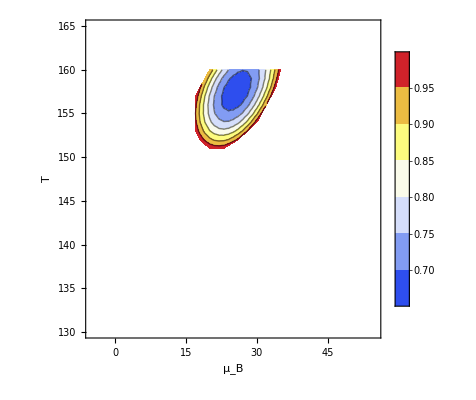

```mathematica
combinedPhaseDiagramWithChi2=Select[combinedData,#[[3]]<1&][[All,{2,1,3}]];
ListContourPlot[
combinedPhaseDiagramWithChi2,
Frame->True,
FrameLabel->{Style["μ_B",20],Style["T",20]},
PlotRange->{{-5,55},{130,165}},
Contours->Automatic,
ColorFunction->"TemperatureMap",
ContourShading->True,
PlotLegends->Automatic,
InterpolationOrder->1
]
```

### Perform χ^2 interpolations

```mathematica
make2DInterpolator[data_]:=Module[
{coords,xvals,yvals,zmap,zgrid},

coords=Keys[data];

(* Extract sorted unique x and y values *)
xvals=Sort@DeleteDuplicates[#[[1]]&/@coords];
yvals=Sort@DeleteDuplicates[#[[2]]&/@coords];

(* Map {x,y} to z *)
zmap=Association[data];

(* Create z-grid:rows=y,columns=x *)
zgrid=Table[zmap[{x,y}],{y,yvals},{x,xvals}];

(* Return interpolating function;note domain is {yvals,xvals} *)
ListInterpolation[zgrid,{yvals,xvals}]
]
```

#### Combined data

```mathematica
reducedCombinedData=combinedData/. {T_,muB_,GlobalChi2_,CuChi2_,AuChi2_,UChi2_,CuMuS_,AuMuS_,UMuS_,CuMuQ_, AuMuQ_,UMuQ_,CuYQ_,AuYQ_,UYQ_}:>{muB,T}->GlobalChi2;
combinedDataInterpolator=make2DInterpolator[reducedCombinedData];
(* Find χ^2-minimum *)
minChi2Global=Min[combinedData[[All,3]]];
locationMinChi2Global=First@Select[combinedData,#[[3]]==minChi2Global&][[All,{1,2}]]/.{T_,muB_}:>{muB,T};
```

#### Cu

```mathematica
reducedCuData=combinedData/. {T_,muB_,GlobalChi2_,CuChi2_,AuChi2_,UChi2_,CuMuS_,AuMuS_,UMuS_,CuMuQ_, AuMuQ_,UMuQ_,CuYQ_,AuYQ_,UYQ_}:>{muB,T}->CuChi2;
CuDataInterpolator=make2DInterpolator[reducedCuData];
(* Find χ^2-minimum *)
minChi2Cu=Min[combinedData[[All,4]]];
locationMinChi2Cu=First@Select[combinedData,#[[4]]==minChi2Cu&][[All,{1,2}]]/.{T_,muB_}:>{muB,T};
```

#### Au

```mathematica
reducedAuData=combinedData/. {T_,muB_,GlobalChi2_,CuChi2_,AuChi2_,UChi2_,CuMuS_,AuMuS_,UMuS_,CuMuQ_, AuMuQ_,UMuQ_,CuYQ_,AuYQ_,UYQ_}:>{muB,T}->AuChi2;
AuDataInterpolator=make2DInterpolator[reducedAuData];
(* Find χ^2-minimum *)
minChi2Au=Min[combinedData[[All,5]]];
locationMinChi2Au=First@Select[combinedData,#[[5]]==minChi2Au&][[All,{1,2}]]/.{T_,muB_}:>{muB,T};
```

#### U

```mathematica
reducedUData=combinedData/. {T_,muB_,GlobalChi2_,CuChi2_,AuChi2_,UChi2_,CuMuS_,AuMuS_,UMuS_,CuMuQ_, AuMuQ_,UMuQ_,CuYQ_,AuYQ_,UYQ_}:>{muB,T}->UChi2;
UDataInterpolator=make2DInterpolator[reducedUData];
(* Find χ^2-minimum *)
minChi2U=Min[combinedData[[All,6]]];
locationMinChi2U=First@Select[combinedData,#[[6]]==minChi2U&][[All,{1,2}]]/.{T_,muB_}:>{muB,T};
```

### Minima

```mathematica
Print["=====> Global: (χ^2)_min = ",minChi2Global, " at ", "(μ_B,T) = ", locationMinChi2Global]
Print["=====> Cu: (χ^2)_min = ",minChi2Cu, " at ", "(μ_B,T) = ", locationMinChi2Cu]
Print["=====> Au: (χ^2)_min = ",minChi2Au, " at ", "(μ_B,T) = ", locationMinChi2Au]
Print["=====> U: (χ^2)_min = ",minChi2U, " at ", "(μ_B,T) = ", locationMinChi2U]
```

=====> Global: (χ^2)_min = 0.662367 at (μ_B,T) = {26.001,158.}

=====> Cu: (χ^2)_min = 0.95781 at (μ_B,T) = {23.001,156.}

=====> Au: (χ^2)_min = 0.386464 at (μ_B,T) = {28.001,160.}

=====> U: (χ^2)_min = 0.510734 at (μ_B,T) = {28.001,157.}

### ContourPlot in the (T, μ_B) plane

#### ContourPlot definitions

```mathematica
CombinedContourPlot=ContourPlot[
combinedDataInterpolator[T,muB],{muB,0,50},{T,135,160},
Contours->{minChi2Global,minChi2Global+1},
ContourStyle->Directive[LightOrange,Thickness[0.005],Bold,Opacity[0.4]],
PlotLegends->Automatic,
ContourShading->{None,Directive[LightOrange,Opacity[0.2]]},
Frame->True,
PlotRangePadding->1,
FrameLabel->{Style["μ_B",20],Style["T",20]},
Epilog->{{
LightOrange,
Text[Style["★",14,Bold],locationMinChi2Global]
},
{
Red,
Text[Style["★",14,Bold],locationMinChi2Cu]
},
{
Blue,
Text[Style["★",14,Bold],locationMinChi2Au]
},
{
Darker@Green,
Text[Style["★",14,Bold],locationMinChi2U]
}}
];
CuContourPlot=ContourPlot[
CuDataInterpolator[T,muB],{muB,0,50},{T,135,160},
Contours->{minChi2Cu,minChi2Cu+1},
ContourStyle->Directive[Red,Thickness[0.005],Bold,Opacity[0.4]],
PlotLegends->Automatic,
ContourShading->False,
Frame->True,
FrameLabel->{Style["μ_B",20],Style["T",20]}
];
AuContourPlot=ContourPlot[
AuDataInterpolator[T,muB],{muB,0,50},{T,135,160},
Contours->{minChi2Au,minChi2Au+1},
ContourStyle->Directive[Blue,Thickness[0.005],Bold,Opacity[0.4],Dotted],
PlotLegends->Automatic,
ContourShading->False,
Frame->True,
FrameLabel->{Style["μ_B",20],Style["T",20]}
];
UContourPlot=ContourPlot[
UDataInterpolator[T,muB],{muB,0,50},{T,135,160},
Contours->{minChi2U,minChi2U+1},
ContourStyle->Directive[Darker@Green,Thickness[0.005],Bold,Opacity[0.4],Dashed],
PlotLegends->Automatic,
ContourShading->False,
Frame->True,
FrameLabel->{Style["μ_B",20],Style["T",20]}
];
Show[CombinedContourPlot,CuContourPlot,AuContourPlot,UContourPlot]
```

#### Show ContourPlot

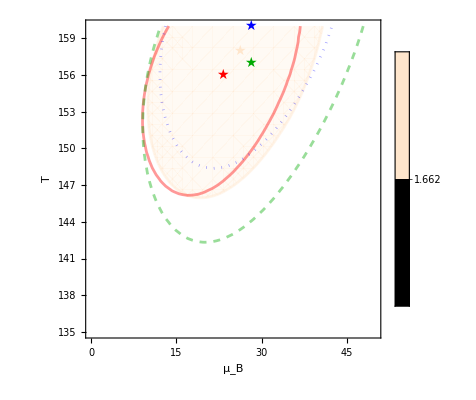

#### χ^2 vs μ_B/T

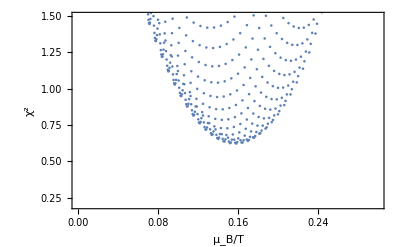

```mathematica
phasedigALLTMuB2=totmuS[[All,{2,1,3}]];
chi2Interp=phasedigALLTMuB2/. {muB_,T_,chi2_}:>{muB/T,chi2};
ListPlot[chi2Interp,Frame->True,FrameLabel->{Style["μ_B/T",20],Style["χ^2",20]},PlotRange->{{0,0.3},{0.2,1.5}}]
```

### Plot of T vs μ_S

```mathematica
phasedigALLTMUS=Select[totmuS,#[[3]]<1&][[All,{1,4,5,6}]];
ListPlot[phasedigALLTMUS[[All,{2,1}]],Frame->True,FrameLabel->{Style["μ_S",20],Style["T",20]},PlotStyle->Red,PlotLabel->"CuCu"];
ListPlot[phasedigALLTMUS[[All,{3,1}]],Frame->True,FrameLabel->{Style["μ_S",20],Style["T",20]},PlotStyle->Blue, PlotLabel->"AuAu"];
ListPlot[phasedigALLTMUS[[All,{4,1}]],Frame->True,FrameLabel->{Style["μ_S",20],Style["T",20]},PlotStyle->Green,PlotLabel->"UU"];
```

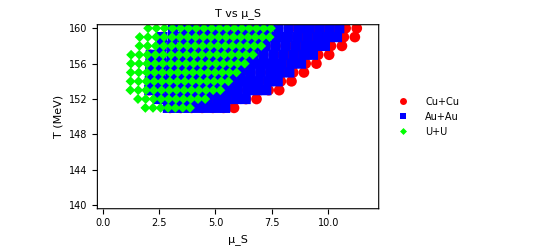

```mathematica
cuMuS=phasedigALLTMUS[[All,{2,1}]];  
auMuS=phasedigALLTMUS[[All,{3,1}]]; 
uMuS=phasedigALLTMUS[[All,{4,1}]]; 
ListPlot[{cuMuS,auMuS,uMuS},Frame->True,FrameLabel->{Style["μ_S",20],Style["T (MeV)",20]},PlotStyle->{Red,Blue,Green},PlotMarkers->Automatic,PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.9,0.2}]],PlotRange->{{0,12},{140,160}},PlotLabel->"T vs μ_S"]
```

```mathematica
MUScuData=Select[totmuS,#[[3]]<1&][[All,{1,4,3}]]; 
MUSauData=Select[totmuS,#[[3]]<1&][[All,{1,5,3}]]; 
MUSuData=Select[totmuS,#[[3]]<1&][[All,{1,6,3}]];  

cuContourData=MUScuData[[All,{2,1,3}]];
auContourData=MUSauData[[All,{2,1,3}]];
uContourData=MUSuData[[All,{2,1,3}]];
```

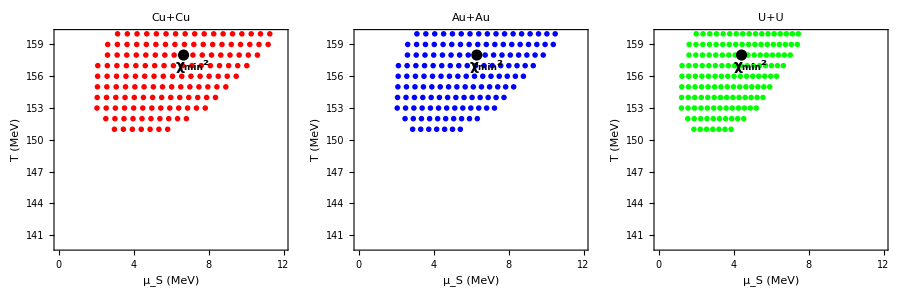

```mathematica
SigmaPlot[data_,systemName_,color_]:=Module[{MUSchi2Interp,MUSminChi2,MUSoneSigmaLevel,MUSminPoint},MUSchi2Interp=Interpolation[data/. {muS_,T_,chi2_}:>{{muS,T}->chi2},InterpolationOrder->2];
MUSminChi2=Min[data[[All,3]]];
MUSoneSigmaLevel=MUSminChi2+1;
MUSminPoint=First@Select[data,#[[3]]==MUSminChi2&][[All,{1,2}]];
ListContourPlot[data,InterpolationOrder->2,Contours->{MUSminChi2,MUSoneSigmaLevel},ContourStyle->{Directive[color,Thickness[0.01]],Directive[color,Dashed,Thickness[0.005]]},ColorFunction->(None&),ContourShading->None,Frame->True,PlotRange->{{0,12},{140,160}},FrameLabel->{Style["μ_S (MeV)",20,Bold],Style["T (MeV)",20,Bold]},PlotLabel->Style[systemName,16,Bold],Epilog->{color,PointSize[0.01],Point[data[[All,{1,2}]]],{Black,PointSize[0.02],Point[MUSminPoint]},Text[Style[Row[{Superscript[Subscript["χ","min"],"2"](* "= ",NumberForm[MUSminChi2,{4,2}]*)}],14,Bold,Black],MUSminPoint+{0.5,-1}]}]]

cuPlot=SigmaPlot[cuContourData,"Cu+Cu",Red];
auPlot=SigmaPlot[auContourData,"Au+Au",Blue];
uPlot=SigmaPlot[uContourData,"U+U",Green];
GraphicsRow[{cuPlot,auPlot,uPlot},ImageSize->900,Spacings->0]
```

#### χ^2 vs μ_S/T

```mathematica
TMUScuChi2Data=Select[totmuS,#[[3]]<1&][[All,{4,1,3}]]/. {muS_,T_,chi2_}:>{muS/T,chi2};
TMUSauChi2Data=Select[totmuS,#[[3]]<1&][[All,{5,1,3}]]/. {muS_,T_,chi2_}:>{muS/T,chi2};
TMUSuChi2Data=Select[totmuS,#[[3]]<1&][[All,{6,1,3}]]/. {muS_,T_,chi2_}:>{muS/T,chi2};
```

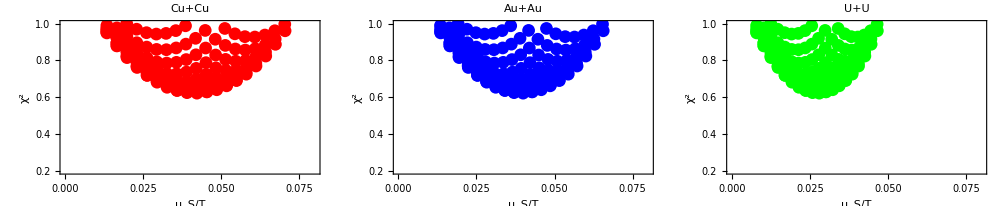

```mathematica
cuPlot=ListPlot[TMUScuChi2Data,Frame->True,FrameLabel->{Style["μ_S/T",20],Style["χ^2",20]},PlotStyle->{Red},PlotRange->{{0,0.08},{0.2,1.0}},PlotLabel->Style["Cu+Cu",10,Bold],ImageSize->1000];
auPlot=ListPlot[TMUSauChi2Data,Frame->True,FrameLabel->{Style["μ_S/T",20],Style["χ^2",20]},PlotStyle->{Blue},PlotRange->{{0,0.08},{0.2,1.0}},PlotLabel->Style["Au+Au",10,Bold],ImageSize->1000];
uPlot=ListPlot[TMUSuChi2Data,Frame->True,FrameLabel->{Style["μ_S/T",20],Style["χ^2",20]},PlotStyle->{Green},PlotRange->{{0,0.08},{0.2,1.0}},PlotLabel->Style["U+U",10,Bold],ImageSize->1000];
GraphicsRow[{cuPlot,auPlot,uPlot},ImageSize->1000,Spacings->0]
```

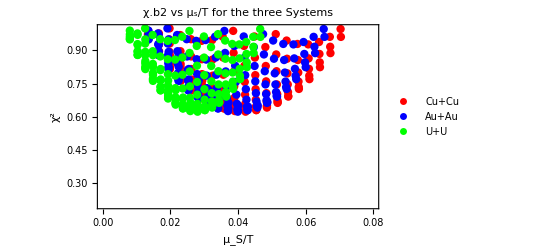

```mathematica
ListPlot[{TMUScuChi2Data,TMUSauChi2Data,TMUSuChi2Data},Frame->True,FrameLabel->{Style["μ_S/T",20],Style["χ^2",20]},PlotStyle->{{Red,PointSize[0.015]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}},PlotRange->{{0,0.08},{0.2,1.0}},PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.85,0.2}]],PlotLabel->Style["χ.b2 vs μₛ/T for the three Systems",18]]
```

### Plot of T vs μ_Q

```mathematica
phasedigALLTMUQ=Select[totmuQ,#[[3]]<1&][[All,{1,4,5,6}]];
ListPlot[phasedigALLTMUQ[[All,{2,1}]],Frame->True,FrameLabel->{Style["μ_Q",20],Style["T",20]},PlotRange->{{-10,10},{140,160}},PlotStyle->Red,PlotLabel->"CuCu"];
ListPlot[phasedigALLTMUQ[[All,{3,1}]],Frame->True,FrameLabel->{Style["μ_Q",20],Style["T",20]},PlotRange->{{-10,10},{140,160}},PlotStyle->Blue, PlotLabel->"AuAu"];
ListPlot[phasedigALLTMUQ[[All,{4,1}]],Frame->True,FrameLabel->{Style["μ_Q",20],Style["T",20]},PlotRange->{{-10,10},{140,160}},PlotStyle->Green,PlotLabel->"UU"];
```

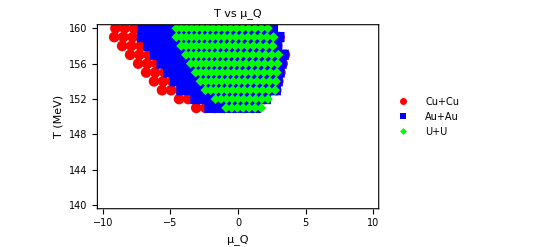

```mathematica
MUQcuData=phasedigALLTMUQ[[All,{2,1}]];  
MUQauData=phasedigALLTMUQ[[All,{3,1}]]; 
MUQuData=phasedigALLTMUQ[[All,{4,1}]]; 
ListPlot[{MUQcuData,MUQauData,MUQuData},Frame->True,FrameLabel->{Style["μ_Q",20],Style["T (MeV)",20]},PlotStyle->{Red,Blue,Green},PlotMarkers->Automatic,PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.9,0.8}]],PlotRange->{{-10,10},{140,160}},PlotLabel->"T vs μ_Q"]
```

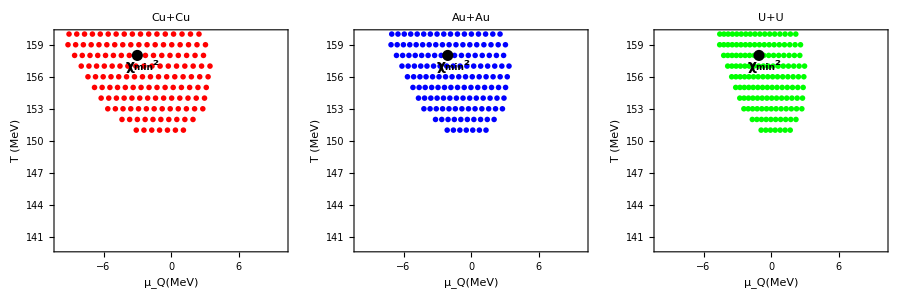

```mathematica
MuQcuData=Select[totmuQ,#[[3]]<1&][[All,{1,4,3}]]; 
MuQauData=Select[totmuQ,#[[3]]<1&][[All,{1,5,3}]];  
MuQuData=Select[totmuQ,#[[3]]<1&][[All,{1,6,3}]]; 

cuQContour=MuQcuData[[All,{2,1,3}]];
auQContour=MuQauData[[All,{2,1,3}]];
uQContour=MuQuData[[All,{2,1,3}]];

SigmaPlot[data_,systemName_,color_]:=Module[{MUQchi2Interp,MUQminChi2,MUQoneSigmaLevel,MUQminPoint},MUQchi2Interp=Interpolation[data/. {muQ_,T_,chi2_}:>{{muQ,T}->chi2},InterpolationOrder->2];
MUQminChi2=Min[data[[All,3]]];
MUQoneSigmaLevel=MUQminChi2+1;
MUQminPoint=First@Select[data,#[[3]]==MUQminChi2&][[All,{1,2}]];
ListContourPlot[data,InterpolationOrder->2,Contours->{MUQminChi2,MUQoneSigmaLevel},ContourStyle->{Directive[color,Thickness[0.01]],Directive[color,Dashed,Thickness[0.005]]},ColorFunction->(None&),ContourShading->None,PlotLegends->None,Frame->True,PlotRange->{{-10,10},{140,160}},FrameLabel->{Style["μ_Q(MeV)",20,Bold],Style["T (MeV)",20,Bold]},PlotLabel->Style[systemName,16,Bold],Epilog->{color,PointSize[0.01],Point[data[[All,{1,2}]]],{Black,PointSize[0.02],Point[MUQminPoint]},Text[Style[Row[{Superscript[Subscript["χ","min"],"2"](* "= ",NumberForm[MUSminChi2,{4,2}]*)}],14,Bold,Black],MUQminPoint+{0.5,-1}]}]]

MuQcuPlot=SigmaPlot[cuQContour,"Cu+Cu",Red];
MuQauPlot=SigmaPlot[auQContour,"Au+Au",Blue];
MuQuPlot=SigmaPlot[uQContour,"U+U",Green];
GraphicsRow[{MuQcuPlot,MuQauPlot,MuQuPlot},ImageSize->900,Spacings->0]
```

#### χ^2 vs μ_Q/T

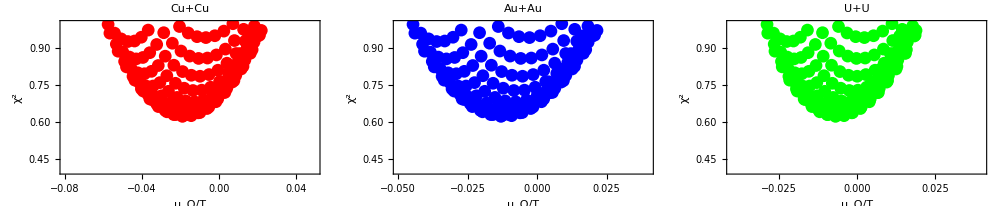

```mathematica
TMUQcuChi2Data=Select[totmuQ,#[[3]]<1&][[All,{4,1,3}]]/. {muQ_,T_,chi2_}:>{muQ/T,chi2};
TMUQauChi2Data=Select[totmuQ,#[[3]]<1&][[All,{5,1,3}]]/. {muQ_,T_,chi2_}:>{muQ/T,chi2};
TMUQuChi2Data=Select[totmuQ,#[[3]]<1&][[All,{6,1,3}]]/. {muQ_,T_,chi2_}:>{muQ/T,chi2};


muQcuPlot=ListPlot[TMUQcuChi2Data,Frame->True,FrameLabel->{Style["μ_Q/T",20],Style["χ^2",20]},PlotStyle->{Red},PlotRange->{{-0.08,0.05},{0.4,1.0}},PlotLabel->Style["Cu+Cu",10,Bold],ImageSize->1000];
muQauPlot=ListPlot[TMUQauChi2Data,Frame->True,FrameLabel->{Style["μ_Q/T",20],Style["χ^2",20]},PlotStyle->{Blue},PlotRange->{{-0.05,0.04},{0.4,1.0}},PlotLabel->Style["Au+Au",10,Bold],ImageSize->1000];
muQuPlot=ListPlot[TMUQuChi2Data,Frame->True,FrameLabel->{Style["μ_Q/T",20],Style["χ^2",20]},PlotStyle->{Green},PlotRange->{{-0.04,0.04},{0.4,1.0}},PlotLabel->Style["U+U",10,Bold],ImageSize->1000];
GraphicsRow[{muQcuPlot,muQauPlot,muQuPlot},ImageSize->1000,Spacings->0]
```

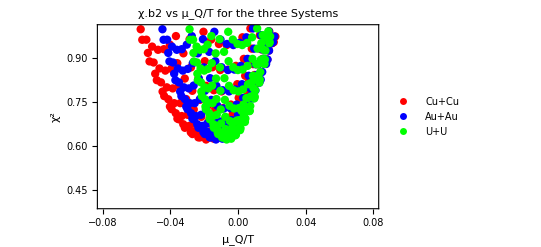

```mathematica
ListPlot[{TMUQcuChi2Data,TMUQauChi2Data,TMUQuChi2Data},Frame->True,FrameLabel->{Style["μ_Q/T",20],Style["χ^2",20]},PlotStyle->{{Red,PointSize[0.015]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}},PlotRange->{{-0.08,0.08},{0.4,1.0}},PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.85,0.2}]],PlotLabel->Style["χ.b2 vs μ_Q/T for the three Systems",18]]
```

### Plot of T vs Z/A

```mathematica
phasedigALL=Select[totZA,#[[3]]<1&][[All,{1,4,5,6}]];
ListPlot[phasedigALL[[All,{2,1}]],Frame->True,FrameLabel->{Style["Z/A",20],Style["T",20]},PlotRange->{{-1,2},{140,160}},PlotStyle->Red,PlotLabel->"CuCu"];
ListPlot[phasedigALL[[All,{3,1}]],Frame->True,FrameLabel->{Style["Z/A",20],Style["T",20]},PlotRange->{{-1,2},{140,160}},PlotStyle->Blue, PlotLabel->"AuAu"];
ListPlot[phasedigALL[[All,{4,1}]],Frame->True,FrameLabel->{Style["Z/A",20],Style["T",20]},PlotRange->{{-1,2},{140,160}},PlotStyle->Green,PlotLabel->"UU"];
```

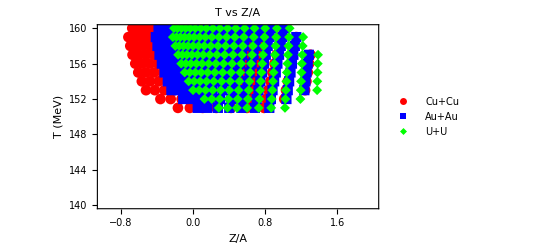

```mathematica
cuData=phasedigALL[[All,{2,1}]];  
auData=phasedigALL[[All,{3,1}]]; 
uData=phasedigALL[[All,{4,1}]]; 
ListPlot[{cuData,auData,uData},Frame->True,FrameLabel->{Style["Z/A",20],Style["T (MeV)",20]},PlotStyle->{Red,Blue,Green},PlotMarkers->Automatic,PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.9,0.8}]],PlotRange->{{-1,2},{140,160}},PlotLabel->"T vs Z/A"]
```

### Plot of χ^2 vs μ_B

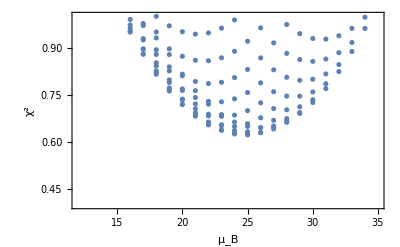

```mathematica
phasedigALL=Select[totmuS,#[[3]]<1&][[All,{2,3}]]; (*this excludes all high-χ.b2 data points*)
ListPlot[phasedigALL,Frame->True,FrameLabel->{Style["μ_B",20],Style["χ^2",20]}, PlotRange->{{12,35},{0.4,1}}]
```

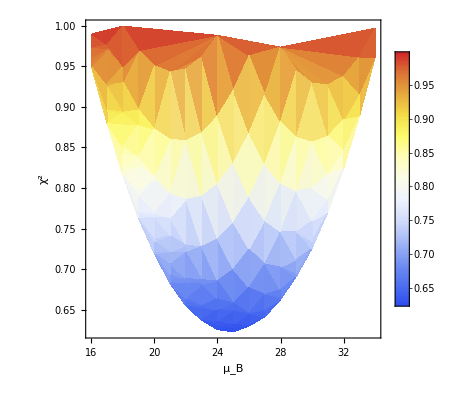

```mathematica
heatmapData=Select[totmuS,#[[3]]<1&][[All,{2,3,3}]];
ListDensityPlot[heatmapData,Frame->True,FrameLabel->{Style["μ_B",20],Style["χ^2",20]},ColorFunction->"TemperatureMap",PlotLegends->Automatic,InterpolationOrder->1]
```

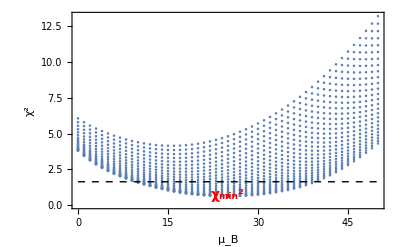

```mathematica
phasedigALL=totmuS[[All,{2,3}]];  (*This includes all the data point regardlesss of the χ.b2 value*)
minChi2=Min[phasedigALL[[All,2]]];
oneSigmaLevel=minChi2+1;
minPoint=First@Select[phasedigALL,#[[2]]==minChi2&];

ListPlot[phasedigALL,Frame->True,FrameLabel->{Style["μ_B",20],Style["χ^2",20]},PlotRange->All,Epilog->{Red,PointSize[Large],Point[minPoint],Text[Style[Row[{Superscript[Subscript["χ","min"],"2"]}],14,Bold],minPoint+{0,0.05}],{Directive[Dashed,Black],Line[{{Min[phasedigALL[[All,1]]],oneSigmaLevel},{Max[phasedigALL[[All,1]]],oneSigmaLevel}}]}}]
```

### Plot of Z/A vs μ_Q

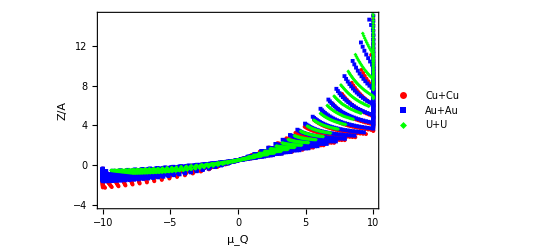

```mathematica
cuZAMuQ=Table[{totmuQ[[i,4]],totZA[[i,4]]},{i,len}];
auZAMuQ=Table[{totmuQ[[i,5]],totZA[[i,5]]},{i,len}];
uZAMuQ=Table[{totmuQ[[i,6]],totZA[[i,6]]},{i,len}];
ListPlot[{cuZAMuQ,auZAMuQ,uZAMuQ},PlotStyle->{Red,Blue,Green},PlotMarkers->{Automatic,4},Joined->False,Frame->True,FrameLabel->{Style["μ_Q",18],Style["Z/A",18]},PlotLegends->{"Cu+Cu","Au+Au","U+U"}, PlotRange->{{-10,10},{-4,15}}]
```

## Sort list for the individual system

CuValue = T, muB, Cu chi2, Cu muS, Cu muQ , Cu Z/A
AuValue =  T, muB, Au chi2, Au muS, Au muQ , Au Z/A
UValue =  T, muB, U chi2, U muS, U muQ , U Z/A

```mathematica
CuValue= Table[{sortCuCu[[i,1]],sortCuCu[[i,2]],sortCuCu[[i,8]],sortCuCu[[i,3]],sortCuCu[[i,4]],sortCuCu[[i,6]] },{i,len}];
AuValue= Table[{sortAuAu[[i,1]],sortAuAu[[i,2]],sortAuAu[[i,8]],sortAuAu[[i,3]],sortAuAu[[i,4]],sortAuAu[[i,6]] },{i,len}];
UValue= Table[{sortUU[[i,1]],sortUU[[i,2]],sortUU[[i,8]],sortUU[[i,3]],sortUU[[i,4]],sortUU[[i,6]] },{i,len}];
```

### T vs MuB for Cu, Au & U

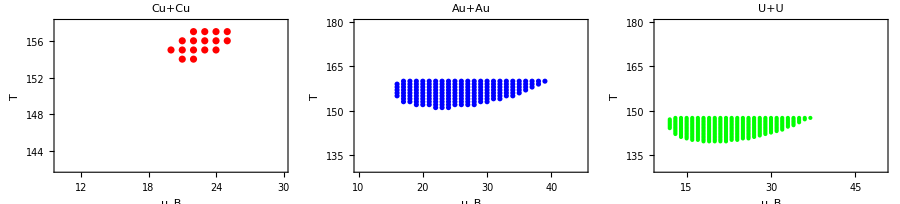

```mathematica
CUPhaseDiagram=Select[CuValue,#[[3]]<1&][[All,{2,1}]];
AuPhaseDiagram=Select[AuValue,#[[3]]<1&][[All,{2,1}]];
UPhaseDiagram=Select[UValue,#[[3]]<1&][[All,{2,1}]];
CuTMuB=ListPlot[CUPhaseDiagram,Frame->True,FrameLabel->{Style["μ_B",20],Style["T",20]},PlotStyle->Red,PlotRange->{{10,30},{142,158}},PlotLabel->"Cu+Cu"];
AuTMuB=ListPlot[AuPhaseDiagram,Frame->True,FrameLabel->{Style["μ_B",20],Style["T",20]},PlotStyle->Blue,PlotRange->{{10,45},{130,180}},PlotLabel->"Au+Au"];
UTMuB=ListPlot[UPhaseDiagram,Frame->True,FrameLabel->{Style["μ_B",20],Style["T",20]},PlotStyle->Green,PlotRange->{{10,50},{130,180}},PlotLabel->"U+U"];
GraphicsRow[{CuTMuB,AuTMuB,UTMuB},ImageSize->900,Spacings->0]
```

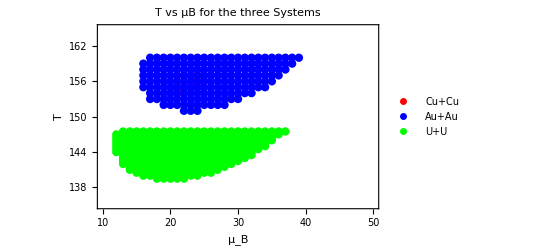

```mathematica
ListPlot[{CUPhaseDiagram,AuPhaseDiagram,UPhaseDiagram},Frame->True,FrameLabel->{Style["μ_B",20],Style["T",20]},PlotStyle->{{Red,PointSize[0.015]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}},PlotRange->{{10,50},{135,165}},PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.85,0.2}]],PlotLabel->Style["T vs μB for the three Systems",18]]
```

For Cu+Cu

```mathematica
chi2InterpCu=Interpolation[CuValue[[All,{2,1,3}]],InterpolationOrder->2];
minChi2Cu=NMinValue[chi2InterpCu[{muB,T}],{{muB,10,30},{T,142,158}}];
minPointCu=NArgMin[chi2InterpCu[{muB,T}],{{muB,10,30},{T,142,158}}];
oneSigmaLevelCu=minChi2Cu+1;

cuContourPlot=ListContourPlot[CuValue[[All,{2,1,3}]],InterpolationOrder->2,Contours->{minChi2Cu,oneSigmaLevelCu},ContourStyle->{Directive[Red,Thickness[0.01]],Directive[Black,Dashed, Thickness[0.005]]},(*ColorFunction->(None&),*)ContourShading->None,Frame->True,FrameLabel->{Style["μ_B (MeV)",16],Style["T (MeV)",16]},PlotLabel->Style["Cu+Cu χ^2",16],PlotLegends->Placed[LineLegend[{Red,Black},{"min","1-σ"}],Below]];

Print["χ.b2 Cu+Cu: ",minChi2Cu];
```

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,4.001,5.001,6.001,7.001,8.001,9.001,«41»},{135.,«9»,«16»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{7.63837,7.24472,6.87684,6.53535,6.22081,5.93374,5.67464,5.44393,5.24201,5.06923,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NArgMin::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,4.001,5.001,6.001,7.001,8.001,9.001,«41»},{135.,«9»,«16»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{7.63837,7.24472,6.87684,6.53535,6.22081,5.93374,5.67464,5.44393,5.24201,5.06923,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5.,7.,0.,{51.,26.},{3.,3.},0.,0.,0.,0.,Automatic,«3»},{{0.001,1.001,2.001,«5»,8.001,9.001,«41»},{«1»}},{Developer`PackedArrayForm,{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,«1317»},{7.63837,7.24472,6.87684,6.53535,6.22081,5.93374,5.67464,5.44393,5.24201,5.06923,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {NMinValue[{«1»,InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,«3»,7.001,8.001,9.001,«41»},{«1»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{7.63837,7.24472,6.87684,6.53535,6.22081,5.93374,5.67464,5.44393,5.24201,5.06923,«1316»}},{Automatic,Automatic}][T]},«1»],1+«1»} is not a valid contour specification.

χ.b2 Cu+Cu: NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,10,30},{T,142,158}}]

For Au+Au

```mathematica
MuBRangeAu=MinMax[AuValue[[All,2]]]; 
TRangeAu=MinMax[AuValue[[All,1]]];  
chi2InterpAu=Interpolation[AuValue[[All,{2,1,3}]],InterpolationOrder->2];
minChi2Au=NMinValue[chi2InterpAu[{muB,T}],{{muB,MuBRangeAu[[1]],MuBRangeAu[[2]]},{T,TRangeAu[[1]],TRangeAu[[2]]}}];
minPointAu=NArgMin[chi2InterpAu[{muB,T}],{{muB,MuBRangeAu[[1]],MuBRangeAu[[2]]},{T,TRangeAu[[1]],TRangeAu[[2]]}}];
oneSigmaLevelAu=minChi2Au+1;

AuContourPlot=ListContourPlot[AuValue[[All,{2,1,3}]],InterpolationOrder->2,Contours->{minChi2Au,oneSigmaLevelAu},ContourStyle->{Directive[Blue,Thickness[0.01]],Directive[Black,Dashed, Thickness[0.005]]},(*ColorFunction->(None&),*)ContourShading->None,Frame->True,FrameLabel->{Style["μ_B(MeV)",16],Style["T (MeV)",16]},PlotLabel->Style["Au+Au χ^2",16],PlotLegends->Placed[LineLegend[{Blue,Black},{"min","1-σ"}],Below]];

Print["Au+Au minimum χ.b2: ",minChi2Au];
```

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,4.001,5.001,6.001,7.001,8.001,9.001,«41»},{135.,«10»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{7.18583,6.843,6.51785,6.21077,5.92208,5.65211,5.40115,5.16946,4.95728,4.76483,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NArgMin::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,4.001,5.001,6.001,7.001,8.001,9.001,«41»},{135.,«10»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{7.18583,6.843,6.51785,6.21077,5.92208,5.65211,5.40115,5.16946,4.95728,4.76483,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5.,7.,0.,{51.,26.},{3.,3.},0.,0.,0.,0.,Automatic,«3»},{{0.001,1.001,2.001,«5»,8.001,9.001,«41»},{«1»}},{Developer`PackedArrayForm,{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,«1317»},{7.18583,6.843,6.51785,6.21077,5.92208,5.65211,5.40115,5.16946,4.95728,4.76483,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {«1»,1+«1»} is not a valid contour specification.

Au+Au minimum χ.b2: NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135.,160.}}]

For U+U

```mathematica
MuBRangeU=MinMax[UValue[[All,2]]]; 
TRangeU=MinMax[UValue[[All,1]]];
chi2InterpU=Interpolation[UValue[[All,{2,1,3}]],InterpolationOrder->2];
minChi2U=NMinValue[chi2InterpU[{muB,T}],{{muB,MuBRangeU[[1]],MuBRangeU[[2]]},{T,TRangeU[[1]],TRangeU[[2]]}}];
minPointU=NArgMin[chi2InterpU[{muB,T}],{{muB,MuBRangeU[[1]],MuBRangeU[[2]]},{T,TRangeU[[1]],TRangeU[[2]]}}];
oneSigmaLevelU=minChi2U+1;

UContourPlot=ListContourPlot[UValue[[All,{2,1,3}]],InterpolationOrder->2,Contours->{minChi2U,oneSigmaLevelU},ContourStyle->{Directive[Green,Thickness[0.01]],Directive[Black,Dashed, Thickness[0.005]]},(*ColorFunction->(None&),*)ContourShading->None,Frame->True,FrameLabel->{Style["μ_B (MeV)",16],Style["T (MeV)",16]},PlotLabel->Style["U+U χ^2",16],PlotLegends->Placed[LineLegend[{Green,Black},{"min","1-σ"}],Below]];

Print["χ.b2 U+U: ",minChi2U];
```

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,147.5}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,4.001,5.001,6.001,7.001,8.001,9.001,«41»},{135.,«9»,«16»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{3.36697,3.29467,3.22651,3.16255,3.10294,3.04786,2.99734,2.95142,2.91013,2.8735,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NArgMin::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,147.5}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,4.001,5.001,6.001,7.001,8.001,9.001,«41»},{135.,«9»,«16»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{3.36697,3.29467,3.22651,3.16255,3.10294,3.04786,2.99734,2.95142,2.91013,2.8735,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinValue::bcons: The following constraints are not valid: {«1»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {«1»,1+NMinValue[{InterpolatingFunction[{{0.001,50.001},{135.,147.5}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{«1»,{135.,135.5,136.,136.5,137.,«6»,138.,138.5,139.,139.5,«16»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{3.36697,3.29467,3.22651,3.16255,3.10294,3.04786,2.99734,2.95142,2.91013,2.8735,«1316»}},{Automatic,Automatic}][muB],«1»},«1»]} is not a valid contour specification.

χ.b2 U+U: NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135,147.5}}]

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5.,7.,0.,{51.,26.},{3.,3.},0.,0.,0.,0.,Automatic,«3»},{{0.001,1.001,2.001,«5»,8.001,9.001,«41»},{«1»}},{Developer`PackedArrayForm,{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,«1317»},{7.63837,7.24472,6.87684,6.53535,6.22081,5.93374,5.67464,5.44393,5.24201,5.06923,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {1+«1»} is not a valid contour specification.

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5.,7.,0.,{51.,26.},{3.,3.},0.,0.,0.,0.,Automatic,«3»},{{0.001,1.001,2.001,«5»,8.001,9.001,«41»},{«1»}},{Developer`PackedArrayForm,{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,«1317»},{7.18583,6.843,6.51785,6.21077,5.92208,5.65211,5.40115,5.16946,4.95728,4.76483,«1316»}},{Automatic,Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {1+NMinValue[{InterpolatingFunction[{{0.001,50.001},{135.,160.}},{5,7,0,{51,26},{3,3},0,0,0,0,Automatic,«3»},{{0.001,1.001,2.001,3.001,«3»,7.001,8.001,9.001,«41»},{«1»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«1317»},{7.18583,6.843,6.51785,6.21077,5.92208,5.65211,5.40115,5.16946,4.95728,4.76483,«1316»}},{Automatic,Automatic}][muB],«1»},«1»]} is not a valid contour specification.

NMinValue::bcons: The following constraints are not valid: {«1»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {1+NMinValue[«1»,{{muB,0.001,50.001},{T,135,147.5}}]} is not a valid contour specification.

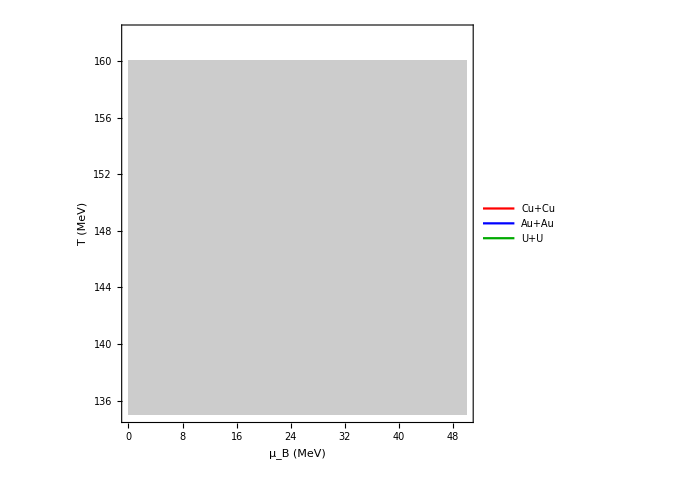

```mathematica
CuPlotMuB=ListContourPlot[CuValue[[All,{2,1,3}]],InterpolationOrder->2,Contours->{minChi2Cu+1},ContourStyle->{Directive[Red,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_B (MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["Cu+Cu",14],PlotRange->{{0,50},{130,170}}];
AuPlotMuB=ListContourPlot[AuValue[[All,{2,1,3}]],InterpolationOrder->2,Contours->{minChi2Au+1},ContourStyle->{Directive[Blue,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_B (MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["Au+Au",14],PlotRange->{{0,50},{130,170}}];
UPlotMuB=ListContourPlot[UValue[[All,{2,1,3}]],InterpolationOrder->2,Contours->{minChi2U+1},ContourStyle->{Directive[Darker@Green,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_B (MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["U+U",14],PlotRange->{{0,50},{130,170}}];
(*Show[CuPlotMuB,AuPlotMuB,UPlotMuB,ImageSize->500]*)
Legended[Show[{CuPlotMuB,AuPlotMuB,UPlotMuB},Frame->True,FrameLabel->{Style["μ_B (MeV)",24],Style["T (MeV)",24]},FrameTicksStyle->Directive[FontSize->20,FontWeight->Bold],PlotLabel->None,PlotRange->{{0,50},{135,162}},ImageSize->500],Placed[LineLegend[{Red,Blue,Darker@Green},{"Cu+Cu","Au+Au","U+U"},LegendMarkerSize->30],Scaled[{0.9,0.2}]]]
```

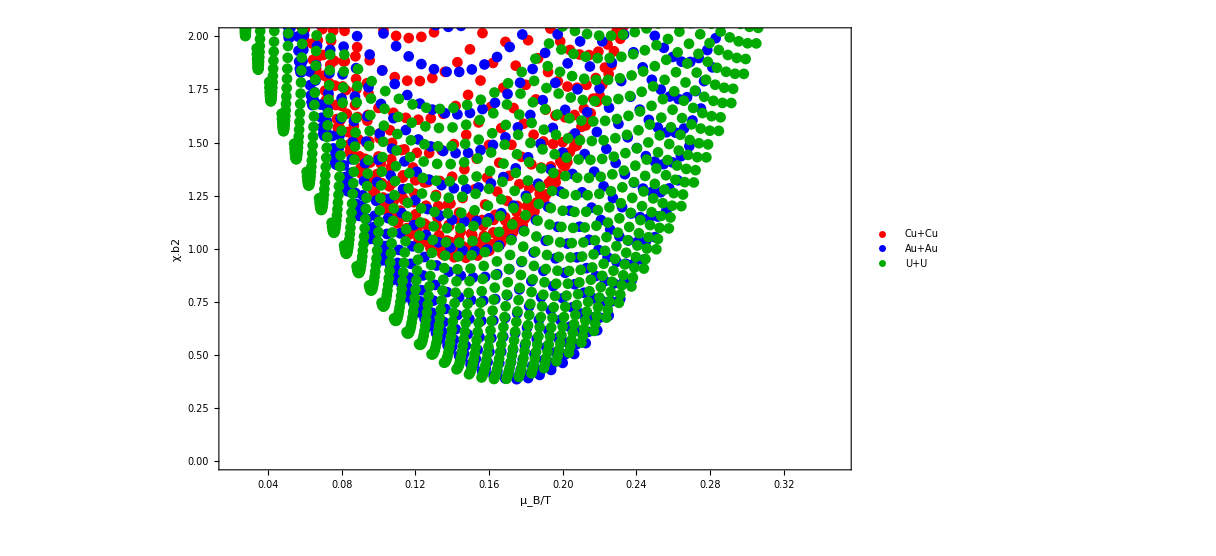

```mathematica
cuMuBoTChi2=CuValue[[All,{2,1,3}]]/. {muB_,T_,chi2_}:>{muB/T,chi2};
auMuBoTChi2=AuValue[[All,{2,1,3}]]/. {muB_,T_,chi2_}:>{muB/T,chi2};
uMuBoTChi2=UValue[[All,{2,1,3}]]/. {muB_,T_,chi2_}:>{muB/T,chi2};

MuBoTcuPlot=ListPlot[cuMuBoTChi2,PlotStyle->Red,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_B/T",16],Style["χ^2",16]},PlotLabel->Style["Cu+Cu",14],PlotRange->{{0.02,0.35},{0,2}}];
MuBoTauPlot=ListPlot[auMuBoTChi2,PlotStyle->Blue,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_B/T",16],Style["χ^2",16]},PlotLabel->Style["Au+Au",14],PlotRange->{{0.01,0.3},{0.1,1.5}}];
MuBoTuPlot=ListPlot[uMuBoTChi2,PlotStyle->Darker@Green,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_B/T",16],Style["χ^2",16]},PlotLabel->Style["U+U",14],PlotRange->{{0.01,0.35},{0.2,1.5}}];
(*Show[{MuBoTcuPlot,MuBoTauPlot,MuBoTuPlot},PlotLabel->None,ImageSize->900]*)
Legended[Show[{MuBoTcuPlot,MuBoTauPlot,MuBoTuPlot},Frame->True,FrameLabel->{Style["μ_B/T",24],Style["χ.b2",24]},FrameTicksStyle->Directive[FontSize->20,FontWeight->Bold],PlotLabel->None,ImageSize->900],Placed[PointLegend[{Red,Blue,Darker@Green},{"Cu+Cu","Au+Au","U+U"},LegendMarkerSize->20],Scaled[{0.9,0.2}]]]
```

Error band

```mathematica
getChi2ErrorBand[data_,minChi2_]:=Module[{oneSigmaLevel,chi2Values,lower,upper,errMinus,errPlus},oneSigmaLevel=minChi2+1;
chi2Values=Select[data,Abs[#[[2]]-oneSigmaLevel]<0.01&][[All,2]];
lower=Min[chi2Values];
upper=Max[chi2Values];
errMinus=minChi2-lower;
errPlus=upper-minChi2;
{minChi2,errMinus,errPlus}]
cuChiBand=getChi2ErrorBand[cuMuBoTChi2,minChi2Cu];
auChiBand=getChi2ErrorBand[auMuBoTChi2,minChi2Au];
uChiBand=getChi2ErrorBand[uMuBoTChi2,minChi2U];
Grid[Prepend[{{"Cu+Cu",Sequence@@cuChiBand},{"Au+Au",Sequence@@auChiBand},{"U+U",Sequence@@uChiBand}},{"System","χ.b2 min","Error −","Error +"}],Frame->All,Alignment->Center,ItemStyle->Directive[Bold]]
```

System | χ.b2 min | Error − | Error +
Cu+Cu | NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,10,30},{T,142,158}}] | -∞+NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,10,30},{T,142,158}}] | -∞-NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,10,30},{T,142,158}}]
Au+Au | NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135.,160.}}] | -∞+NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135.,160.}}] | -∞-NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135.,160.}}]
U+U | NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135,147.5}}] | -∞+NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135,147.5}}] | -∞-NMinValue[{InterpolatingFunction[…][muB],InterpolatingFunction[…][T]},{{muB,0.001,50.001},{T,135,147.5}}]

### T vs MuS for Cu, Au & U

```mathematica
CUPhaseDiagramMUS=Select[CuValue,#[[3]]<1&][[All,{4,1}]];
AuPhaseDiagramMUS=Select[AuValue,#[[3]]<1&][[All,{4,1}]];
UPhaseDiagramMUS=Select[UValue,#[[3]]<1&][[All,{4,1}]];
CuTMuS=ListPlot[CUPhaseDiagramMUS,Frame->True,FrameLabel->{Style["μ_S",20],Style["T",20]},PlotStyle->Red,PlotRange->{{0,8},{142,155}},PlotLabel->"Cu+Cu"];
AuTMuS=ListPlot[AuPhaseDiagramMUS,Frame->True,FrameLabel->{Style["μ_S",20],Style["T",20]},PlotStyle->Blue,PlotRange->{{0,15},{140,170}},PlotLabel->"Au+Au"];
UTMuS=ListPlot[UPhaseDiagramMUS,Frame->True,FrameLabel->{Style["μ_S",20],Style["T",20]},PlotStyle->Green,PlotRange->{{0,12},{130,165}},PlotLabel->"U+U"];
GraphicsRow[{CuTMuS,AuTMuS,UTMuS},ImageSize->1000,Spacings->0];
```

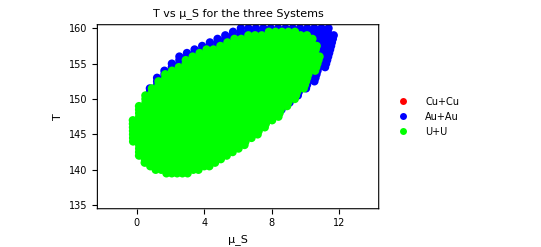

```mathematica
ListPlot[{CUPhaseDiagramMUS,AuPhaseDiagramMUS,UPhaseDiagramMUS},Frame->True,FrameLabel->{Style["μ_S",20],Style["T",20]},PlotStyle->{{Red,PointSize[0.015]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}},PlotRange->{{-2,14},{135,160}},PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.85,0.2}]],PlotLabel->Style["T vs μ_S for the three Systems",18]]
```

For Cu+Cu

```mathematica
chi2InterpCuMUS=Interpolation[CuValue[[All,{4,1,3}]],InterpolationOrder->1];
minChi2CuMUS=NMinValue[chi2InterpCuMUS[{muS,T}],{{muS,0,10},{T,142,152}}];
minPointCuMUS=NArgMin[chi2InterpCuMUS[{muS,T}],{{muS,0,10},{T,142,152}}];
oneSigmaLevelCuMUS=minChi2CuMUS+1;

cuContourPlotMUS=ListContourPlot[CuValue[[All,{4,1,3}]],InterpolationOrder->2,Contours->{minChi2CuMUS,oneSigmaLevelCuMUS},ContourStyle->{Directive[Red,Thickness[0.01]],Directive[Black,Dashed, Thickness[0.005]]},(*ColorFunction->(None&),*)ContourShading->None,Frame->True,FrameLabel->{Style["μ_B (MeV)",16],Style["T (MeV)",16]},PlotLabel->Style["Cu+Cu χ^2",16],PlotLegends->Placed[LineLegend[{Red,Black},{"min","1-σ"}],Below]];

Print["χ.b2 Cu+Cu: ",minChi2CuMUS];
```

NMinValue::bcons: The following constraints are not valid: {«1»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NArgMin::bcons: The following constraints are not valid: {«1»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinValue::bcons: The following constraints are not valid: {«1»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {NMinValue[{«1»,InterpolatingFunction[{{-4.38593,15.3103},{135.,160.}},{5,4227,0,{1326,6},{2,2},0,0,0,0,Automatic,«3»},{«1»},{7.63837,7.25927,6.95963,6.73498,6.54596,6.37517,6.22285,6.08921,5.97447,5.87883,«1316»},{Automatic}][T]},{{muS,0,10},{T,142,152}}],1+NMinValue[{«1»},{{muS,0,10},{T,142,152}}]} is not a valid contour specification.

χ.b2 Cu+Cu: NMinValue[{InterpolatingFunction[…][muS],InterpolatingFunction[…][T]},{{muS,0,10},{T,142,152}}]

For Au+Au

```mathematica
chi2InterpAuMUS=Interpolation[AuValue[[All,{4,1,3}]],InterpolationOrder->1];
minChi2AuMUS=NMinValue[chi2InterpAuMUS[{muS,T}],{{muS,0,10},{T,140,160}}];
minPointAuMUS=NArgMin[chi2InterpAuMUS[{muS,T}],{{muS,0,10},{T,140,160}}];
oneSigmaLevelAuMUS=minChi2AuMUS+1;

auContourPlotMUS=ListContourPlot[AuValue[[All,{4,1,3}]],InterpolationOrder->1,Contours->{minChi2AuMUS,oneSigmaLevelAuMUS},ContourStyle->{Directive[Blue,Thickness[0.01]],Directive[Black,Dashed,Thickness[0.005]]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_S (MeV)",16],Style["T (MeV)",16]},PlotRange->{{0,12},{140,160}},PlotLabel->Style["Au+Au χ^2",16],PlotLegends->Placed[LineLegend[{Blue,Black},{"min","1-σ"}],Below]];

Print["χ.b2 Au+Au: ",minChi2AuMUS];
```

NMinValue::bcons: The following constraints are not valid: {«1»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NArgMin::bcons: The following constraints are not valid: {«1»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinValue::bcons: The following constraints are not valid: {InterpolatingFunction[{{-4.38593,15.3103},{135.,160.}},{5.,4227.,0.,{1326.,0.},{2.,2.},0.,0.,0.,0.,Automatic,«3»},{«1»},{7.18583,6.93224,6.69741,6.47732,6.27206,6.0817,5.90632,5.74595,5.60066,5.47049,«1316»},{Automatic}][T]}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Contours::ilevels: {NMinValue[{«1»,InterpolatingFunction[{{-4.38593,15.3103},{135.,160.}},{5,4227,0,{1326,0},{2,2},0,0,0,0,Automatic,«3»},{«1»},{7.18583,6.93224,6.69741,6.47732,6.27206,6.0817,5.90632,5.74595,5.60066,5.47049,«1316»},{Automatic}][T]},{{muS,0,10},{T,140,160}}],1+NMinValue[{«1»,InterpolatingFunction[{{-4.38593,15.3103},{135.,160.}},«3»,{«9»}][T]},{«1»}]} is not a valid contour specification.

χ.b2 Au+Au: NMinValue[{InterpolatingFunction[…][muS],InterpolatingFunction[…][T]},{{muS,0,10},{T,140,160}}]

For U+U

```mathematica
chi2InterpUMUS=Interpolation[UValue[[All,{4,1,3}]],InterpolationOrder->1];
minChi2UMUS=NMinValue[chi2InterpUMUS[{muS,T}],{{muS,0,8},{T,135,160}}];
minPointUMUS=NArgMin[chi2InterpUMUS[{muS,T}],{{muS,0,8},{T,135,160}}];
oneSigmaLevelUMUS=minChi2UMUS+1;

uContourPlotMUS=ListContourPlot[UValue[[All,{4,1,3}]],InterpolationOrder->1,Contours->{minChi2UMUS,oneSigmaLevelUMUS},ContourStyle->{Directive[Darker@Green,Thickness[0.01]],Directive[Black,Dashed,Thickness[0.005]]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_S (MeV)",16],Style["T (MeV)",16]},PlotRange->{{-5,15},{135,160}},PlotLabel->Style["U+U χ^2",16],PlotLegends->Placed[LineLegend[{Darker@Green,Black},{"min","1-σ"}],Below]];

Print["χ.b2 U+U: ",minChi2UMUS];
```

χ.b2 U+U: 0.371137

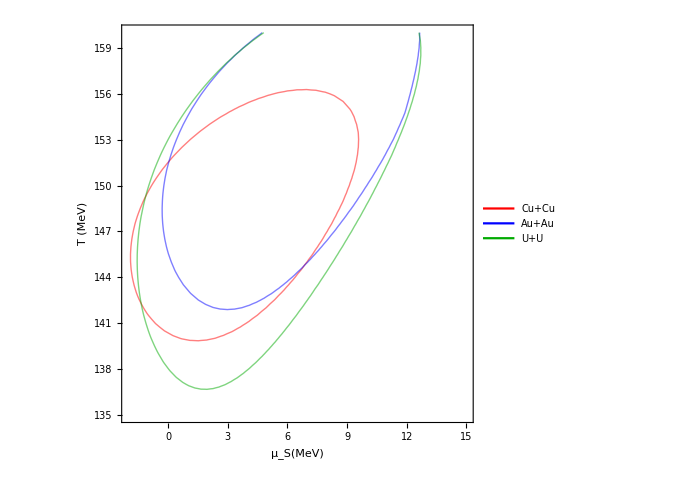

```mathematica
CuPlotMuS=ListContourPlot[CuValue[[All,{4,1,3}]],InterpolationOrder->1,Contours->{minChi2CuMUS+1},ContourStyle->{Directive[Red,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_S(MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["Cu+Cu",14],PlotRange->{{0,15},{135,165}}];
AuPlotMuS=ListContourPlot[AuValue[[All,{4,1,3}]],InterpolationOrder->1,Contours->{minChi2AuMUS+1},ContourStyle->{Directive[Blue,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_S (MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["Au+Au",14],PlotRange->{{0,15},{135,165}}];
UPlotMuS=ListContourPlot[UValue[[All,{4,1,3}]],InterpolationOrder->1,Contours->{minChi2UMUS+1},ContourStyle->{Directive[Darker@Green,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_S(MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["U+U",14],PlotRange->{{0,15},{135,165}}];
Legended[Show[{CuPlotMuS,AuPlotMuS,UPlotMuS},Frame->True,FrameLabel->{Style["μ_S(MeV)",16],Style["T (MeV)",16]},FrameTicksStyle->Directive[FontSize->16],PlotLabel->None,PlotRange->{{-2,15},{135,160}},ImageSize->500],Placed[LineLegend[{Red,Blue,Darker@Green},{"Cu+Cu","Au+Au","U+U"},LegendMarkerSize->30],Scaled[{0.9,0.2}]]]
```

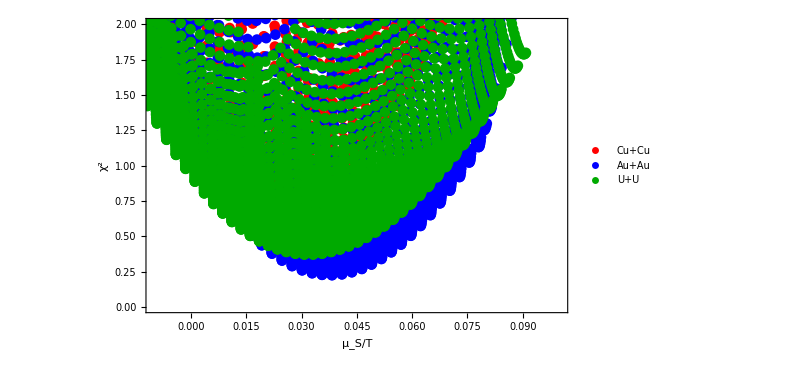

```mathematica
cuMuSoTChi2=CuValue[[All,{4,1,3}]]/. {muS_,T_,chi2_}:>{muS/T,chi2};
auMuSoTChi2=AuValue[[All,{4,1,3}]]/. {muS_,T_,chi2_}:>{muS/T,chi2};
uMuSoTChi2=UValue[[All,{4,1,3}]]/. {muS_,T_,chi2_}:>{muS/T,chi2};

MuSoTcuPlot=ListPlot[cuMuSoTChi2,PlotStyle->Red,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_S/T",16],Style["χ^2",16]},PlotLabel->Style["Cu+Cu",14],PlotRange->{{-0.01,0.1},{0,2}}];
MuSoTauPlot=ListPlot[auMuSoTChi2,PlotStyle->Blue,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_S/T",16],Style["χ^2",16]},PlotLabel->Style["Au+Au",14],PlotRange->{{-0.01,0.1},{0,2}}];
MuSoTuPlot=ListPlot[uMuSoTChi2,PlotStyle->Darker@Green,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_S/T",16],Style["χ^2",16]},PlotLabel->Style["U+U",14],PlotRange->{{-0.01,0.1},{0,2}}];
Legended[Show[{MuSoTcuPlot,MuSoTauPlot,MuSoTuPlot},Frame->True,FrameLabel->{Style["μ_S/T",16],Style["χ^2",16]},FrameTicksStyle->Directive[FontSize->16],PlotLabel->None,ImageSize->600],Placed[PointLegend[{Red,Blue,Darker@Green},{"Cu+Cu","Au+Au","U+U"},LegendMarkerSize->20],Scaled[{0.9,0.2}]]]
```

Error band

```mathematica
getChi2ErrorBandMUS[MuSdata_,MuSminChi2_]:=Module[{MuSoneSigmaLevel,MuSchi2Values,MuSlower,MuSupper,MuSerrMinus,MuSerrPlus},
MuSoneSigmaLevel=MuSminChi2+1;
MuSchi2Values=Select[MuSdata,Abs[#[[2]]-MuSoneSigmaLevel]<0.01&][[All,2]];
MuSlower=Min[MuSchi2Values];
MuSupper=Max[MuSchi2Values];
MuSerrMinus=MuSminChi2-MuSlower;
MuSerrPlus=MuSupper-MuSminChi2;
{MuSminChi2,MuSerrMinus,MuSerrPlus}]
cuChiBandMuS=getChi2ErrorBandMUS[cuMuSoTChi2,minChi2CuMUS];
auChiBandMuS=getChi2ErrorBandMUS[auMuSoTChi2,minChi2AuMUS];
uChiBandMuS=getChi2ErrorBandMUS[uMuSoTChi2,minChi2UMUS];
Grid[Prepend[{{"Cu+Cu",Sequence@@cuChiBandMuS},{"Au+Au",Sequence@@auChiBandMuS},{"U+U",Sequence@@uChiBandMuS}},{"System","χ.b2 min","Error −","Error +"}],Frame->All,Alignment->Center,ItemStyle->Directive[Bold]]
```

System | χ.b2 min | Error − | Error +
Cu+Cu | 0.720406 | -0.991004 | 1.00655
Au+Au | 0.224463 | -0.992497 | 1.00952
U+U | 0.371137 | -0.990943 | 1.00759

### T vs MuQ for Cu, Au & U

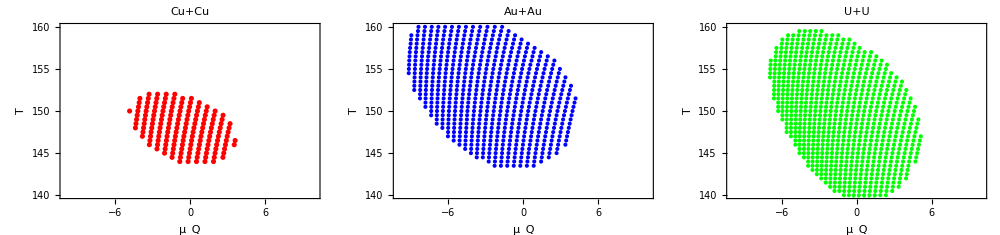

```mathematica
CUPhaseDiagramMUQ=Select[CuValue,#[[3]]<1&][[All,{5,1}]];
AuPhaseDiagramMUQ=Select[AuValue,#[[3]]<1&][[All,{5,1}]];
UPhaseDiagramMUQ=Select[UValue,#[[3]]<1&][[All,{5,1}]];
CuTMuQ=ListPlot[CUPhaseDiagramMUQ,Frame->True,FrameLabel->{Style["μ_Q",20],Style["T",20]},PlotStyle->Red,PlotRange->{{-10,10},{140,160}},PlotLabel->"Cu+Cu"];
AuTMuQ=ListPlot[AuPhaseDiagramMUQ,Frame->True,FrameLabel->{Style["μ_Q",20],Style["T",20]},PlotStyle->Blue,PlotRange->{{-10,10},{140,160}},PlotLabel->"Au+Au"];
UTMuQ=ListPlot[UPhaseDiagramMUQ,Frame->True,FrameLabel->{Style["μ_Q",20],Style["T",20]},PlotStyle->Green,PlotRange->{{-10,10},{140,160}},PlotLabel->"U+U"];
GraphicsRow[{CuTMuQ,AuTMuQ,UTMuQ},ImageSize->1000,Spacings->0]
```

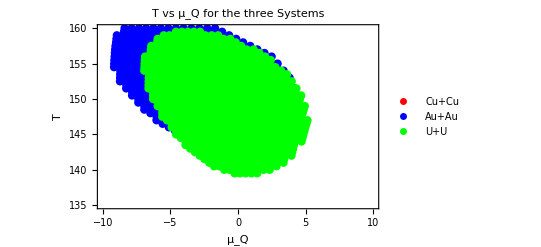

```mathematica
ListPlot[{CUPhaseDiagramMUQ,AuPhaseDiagramMUQ,UPhaseDiagramMUQ},Frame->True,FrameLabel->{Style["μ_Q",20],Style["T",20]},PlotStyle->{{Red,PointSize[0.015]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}},PlotRange->{{-10,10},{135,160}},PlotLegends->Placed[{"Cu+Cu","Au+Au","U+U"},Scaled[{0.9,0.2}]],PlotLabel->Style["T vs μ_Q for the three Systems",18]]
```

For Cu+Cu

```mathematica
cuMuQ=CuValue[[All,{5,1,3}]];
cuMuQData=DeleteDuplicatesBy[cuMuQ,Most];
chi2InterpCuMUQ=Interpolation[cuMuQData,InterpolationOrder->1];
muQRange=MinMax[cuMuQData[[All,1]]];
TRangeMuQ=MinMax[cuMuQData[[All,2]]];
minChi2CuMUQ=NMinValue[chi2InterpCuMUQ[{muQ,T}],{{muQ,muQRange[[1]],muQRange[[2]]},{T,TRangeMuQ[[1]],TRangeMuQ[[2]]}}];
minPointCuMUQ=NArgMin[chi2InterpCuMUQ[{muQ,T}],{{muQ,muQRange[[1]],muQRange[[2]]},{T,TRangeMuQ[[1]],TRangeMuQ[[2]]}}];
oneSigmaLevelCuMUQ=minChi2CuMUQ+1;

cuContourPlotMUQ=ListContourPlot[cuMuQData,InterpolationOrder->2,Contours->{minChi2CuMUQ,oneSigmaLevelCuMUQ},ContourStyle->{Directive[Red,Thickness[0.01]],Directive[Black,Dashed,Thickness[0.005]]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_Q (MeV)",16],Style["T (MeV)",16]},PlotLabel->Style["Cu+Cu χ^2",16],PlotLegends->Placed[LineLegend[{Red,Black},{"min","1-σ"}],Below]];

Print["χ.b2 Cu+Cu: ",minChi2CuMUQ];
```

χ.b2 Cu+Cu: 0.720406

For Au+Au

```mathematica
auMuQ=AuValue[[All,{5,1,3}]];
auMuQData=DeleteDuplicatesBy[auMuQ,Most];
chi2InterpAuMUQ=Interpolation[auMuQData,InterpolationOrder->1];
muQRangeAu=MinMax[auMuQData[[All,1]]];
TRangeAu=MinMax[auMuQData[[All,2]]];
minChi2AuMUQ=NMinValue[chi2InterpAuMUQ[{muQ,T}],{{muQ,muQRangeAu[[1]],muQRangeAu[[2]]},{T,TRangeAu[[1]],TRangeAu[[2]]}}];
minPointAuMUQ=NArgMin[chi2InterpAuMUQ[{muQ,T}],{{muQ,muQRangeAu[[1]],muQRangeAu[[2]]},{T,TRangeAu[[1]],TRangeAu[[2]]}}];
oneSigmaLevelAuMUQ=minChi2AuMUQ+1;

auContourPlotMUQ=ListContourPlot[auMuQData,InterpolationOrder->2,Contours->{minChi2AuMUQ,oneSigmaLevelAuMUQ},ContourStyle->{Directive[Blue,Thickness[0.01]],Directive[Black,Dashed,Thickness[0.005]]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_Q(MeV)",16],Style["T (MeV)",16]},PlotLabel->Style["Au+Au χ^2",16],PlotLegends->Placed[LineLegend[{Blue,Black},{"min","1-σ"}],Below]];

Print["χ.b2 Au+Au: ",minChi2AuMUQ];
```

χ.b2 Au+Au: 0.224463

For U+U

```mathematica
uMuQ=UValue[[All,{5,1,3}]];
uMuQData=DeleteDuplicatesBy[uMuQ,Most];
chi2InterpUMUQ=Interpolation[uMuQData,InterpolationOrder->1];
muQRangeU=MinMax[uMuQData[[All,1]]];
TRangeU=MinMax[uMuQData[[All,2]]];
minChi2UMUQ=NMinValue[chi2InterpUMUQ[{muQ,T}],{{muQ,muQRangeU[[1]],muQRangeU[[2]]},{T,TRangeU[[1]],TRangeU[[2]]}}];
minPointUMUQ=NArgMin[chi2InterpUMUQ[{muQ,T}],{{muQ,muQRangeU[[1]],muQRangeU[[2]]},{T,TRangeU[[1]],TRangeU[[2]]}}];
oneSigmaLevelUMUQ=minChi2UMUQ+1;

uContourPlotMUQ=ListContourPlot[uMuQData,InterpolationOrder->2,Contours->{minChi2UMUQ,oneSigmaLevelUMUQ},ContourStyle->{Directive[Darker@Green,Thickness[0.01]],Directive[Black,Dashed,Thickness[0.005]]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_Q(MeV)",16],Style["T (MeV)",16]},PlotLabel->Style["U+U χ^2",16],PlotLegends->Placed[LineLegend[{Darker@Green,Black},{"min","1-σ"}],Below]];

Print["χ.b2 U+U: ",minChi2UMUQ];
```

χ.b2 U+U: 0.371137

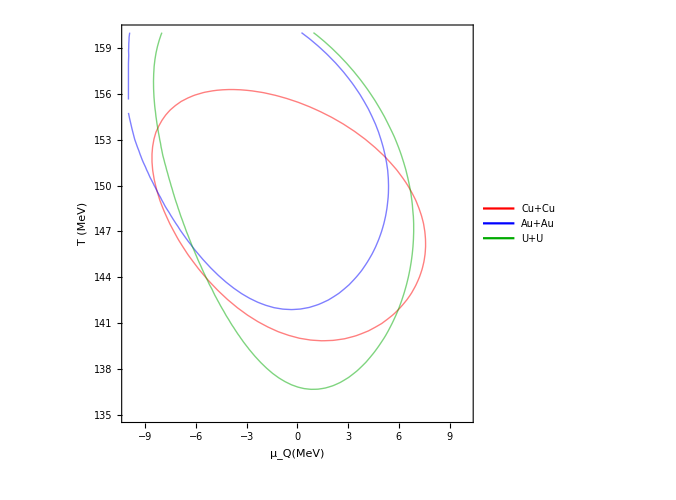

```mathematica
CuPlotMuQ=ListContourPlot[cuMuQData,InterpolationOrder->2,Contours->{minChi2CuMUQ+1},ContourStyle->{Directive[Red,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_Q(MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["Cu+Cu",14],PlotRange->{{-15,15},{135,165}}];
AuPlotMuQ=ListContourPlot[auMuQData,InterpolationOrder->2,Contours->{minChi2AuMUQ+1},ContourStyle->{Directive[Blue,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_Q(MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["Au+Au",14],PlotRange->{{-15,15},{135,165}}];
UPlotMuQ=ListContourPlot[uMuQData,InterpolationOrder->2,Contours->{minChi2UMUQ+1},ContourStyle->{Directive[Darker@Green,Thick]},ContourShading->None,Frame->True,FrameLabel->{Style["μ_Q(MeV)",14],Style["T (MeV)",14]},PlotLabel->Style["U+U",14],PlotRange->{{-15,15},{135,165}}];

Legended[Show[{CuPlotMuQ,AuPlotMuQ,UPlotMuQ},Frame->True,FrameLabel->{Style["μ_Q(MeV)",16],Style["T (MeV)",16]},FrameTicksStyle->Directive[FontSize->16],PlotLabel->None,PlotRange->{{-10,10},{135,160}},ImageSize->500],Placed[LineLegend[{Red,Blue,Darker@Green},{"Cu+Cu","Au+Au","U+U"},LegendMarkerSize->30],Scaled[{0.9,0.1}]]]
```

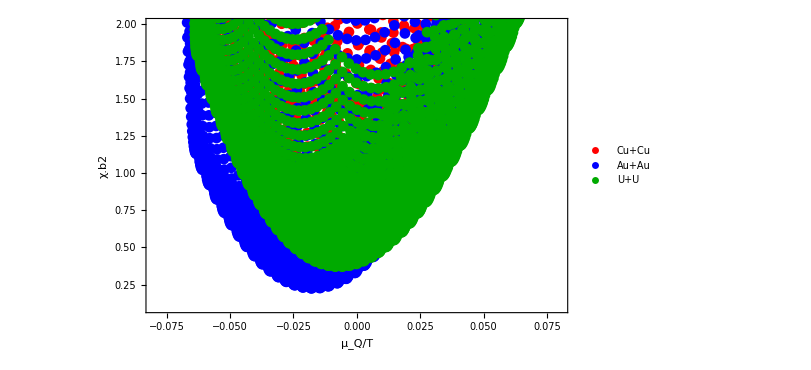

```mathematica
cuMuQoTChi2=CuValue[[All,{5,1,3}]]/. {muQ_,T_,chi2_}:>{muQ/T,chi2};
auMuQoTChi2=AuValue[[All,{5,1,3}]]/. {muQ_,T_,chi2_}:>{muQ/T,chi2};
uMuQoTChi2=UValue[[All,{5,1,3}]]/. {muQ_,T_,chi2_}:>{muQ/T,chi2};
muQoTcuPlot=ListPlot[cuMuQoTChi2,PlotStyle->Red,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_Q/T",16],Style["χ.b2",16]},PlotLabel->Style["Cu+Cu",14],PlotRange->{{-0.08,0.08},{0.1,2}}];
muQoTauPlot=ListPlot[auMuQoTChi2,PlotStyle->Blue,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_Q/T",16],Style["χ.b2",16]},PlotLabel->Style["Au+Au",14],PlotRange->{{-0.08,0.08},{0.1,2}}];
muQoTuPlot=ListPlot[uMuQoTChi2,PlotStyle->Darker@Green,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["μ_Q/T",16],Style["χ.b2",16]},PlotLabel->Style["U+U",14],PlotRange->{{-0.08,0.08},{0.1,2}}];
Legended[Show[{muQoTcuPlot,muQoTauPlot,muQoTuPlot},Frame->True,FrameLabel->{Style["μ_Q/T",16],Style["χ.b2",16]},FrameTicksStyle->Directive[FontSize->16],PlotLabel->None,ImageSize->600],Placed[PointLegend[{Red,Blue,Darker@Green},{"Cu+Cu","Au+Au","U+U"},LegendMarkerSize->10],Scaled[{0.9,0.2}]]]
```

Error band

```mathematica
getChi2ErrorBandMUQ[MuQdata_,MuQminChi2_]:=Module[{MuQoneSigmaLevel,MuQchi2Values,MuQlower,MuQupper,MuQerrMinus,MuQerrPlus},
MuQoneSigmaLevel=MuQminChi2+1;
MuQchi2Values=Select[MuQdata,Abs[#[[2]]-MuQoneSigmaLevel]<0.01&][[All,2]];
MuQlower=Min[MuQchi2Values];
MuQupper=Max[MuQchi2Values];
MuQerrMinus=MuQminChi2-MuQlower;
MuQerrPlus=MuQupper-MuQminChi2;
{MuQminChi2,MuQerrMinus,MuQerrPlus}]
cuChiBandMuQ=getChi2ErrorBandMUQ[cuMuQoTChi2,minChi2CuMUQ];
auChiBandMuQ=getChi2ErrorBandMUQ[auMuQoTChi2,minChi2AuMUQ];
uChiBandMuQ=getChi2ErrorBandMUQ[uMuQoTChi2,minChi2UMUQ];
Grid[Prepend[{{"Cu+Cu",Sequence@@cuChiBandMuQ},{"Au+Au",Sequence@@auChiBandMuQ},{"U+U",Sequence@@uChiBandMuQ}},{"System","χ.b2 min","Error −","Error +"}],Frame->All,Alignment->Center,ItemStyle->Directive[Bold]]
```

System | χ.b2 min | Error − | Error +
Cu+Cu | 0.720406 | -0.991004 | 1.00655
Au+Au | 0.224463 | -0.992497 | 1.00952
U+U | 0.371137 | -0.990943 | 1.00759